## Definitions

```mathematica
NbName = "802"; (*  ReverseSort[list_]:=Reverse@Sort@list;*)
λ0=0.5;       Needs["MaTeX`"];

		Ls =Range[34,34,2]; 	    tV={0};				hV={{0.001,0,0}};

(*With[{φ=0,h=0.2},{ {h,0,φ}(*,{h,15,φ},{h,30,φ},{h,45,φ},{h,60,φ},{h,75,φ},{h,90,φ}*)  }]; (*.2612*) (*hV=Sort@Union[ Table[ {h,0,0},{h,0,.95,.025}]  ,  Table[ {h,0,0},{h,.0125,.95,.025}]] ;*)*)
		steps=350;                                     acuracy=5;   (* 4  32*)                             (* ΔeV=0.04999;*) ΔeV=0.099999; eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ;  (*Table[ev,{ev,1500,1500,100}];*)

Js={0.};
Ks={-1.}; 
Γs={0.};(* Table[γ,{γ,0.,.0,.2}];*)
hV=Table[{h,0,0},{h,0.01,1,0.025}];
(*{  {0.1,0,0}  }*)(*Table[{h,0,0},{h,0.,1,.05}];*)(*Sort@Join[Table[{h^3,0,0},{h,.04,.4,.02}],Table[{h,0,0},{h,0.,1,.01}]  ]*)

(*hV={{0.00001,0,0} }  *)
```

#### Constants

```mathematica
mysort[list_]:=Module[ {sorted=Sort@list,half=⌊Length[list]/2⌋},  Join[ sorted[[half+1;;-1]], sorted[[half;;1;;-1]] ]  ];
```

```mathematica
Gmat={KroneckerProduct[  PauliMatrix[0],-ⅈ PauliMatrix[2] ],KroneckerProduct[- ⅈ PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-ⅈ PauliMatrix[2],  PauliMatrix[1] ]};
Mmat= {KroneckerProduct[  PauliMatrix[3],ⅈ PauliMatrix[2] ],KroneckerProduct[ ⅈ PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],ⅈ PauliMatrix[2] ]};
```

```mathematica
one[i_,j_,N_]:= SparseArray[ {i,j} -> 1, {N,N}];  block[i_,j_] := one[i,j,8];

hc=1/(√3){1,1,1};hb=1/(√2){1,-1,0};ha=1/(√6){1,1,-2};hx={1,0,0};
 hAngle[θ_,ϕ_]:= ha Cos[ϕ π/180] Sin[θ π/180]+hb Sin[ϕ π/180] Sin[θ π/180]+ hc Cos[θ π/180] ;  (* Magnetic field directions a, b, c*)
nx={1/2,(√3)/2};  ny={-1/2,(√3)/2};                                                                                           (* Honeycomb Bravais basis  *)

δx={-√3/2,-1/2}/√3;      
δy={√3/2,-1/2}/√3;     
δz={0,1}/√3;   
(* NN vectors  *)
```

```mathematica
(*χGx =- {{0.5249,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = -{{0.5249,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz =-{{0.5249,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = {{ⅈ,0.000001,0.000001,0.000001},{-0.000001,ⅈ,0.000001,-0.000001},{-0.000001,-0.000001,ⅈ,0.000001},{-0.000001,0.000001,-0.000001,ⅈ}}; ωGB = ωGA;*)
```

```mathematica
round[x_]:=N[Norm[1000 x]/1000];
```

```mathematica
to3digits[list0_]:=Module[{list=list0},If[ Length@list>=3, list, list=Flatten[{{0},list},1]; If[ Length@list>=3, list,  list=Flatten[{{0},list},1] ] ]; StringJoin[ToString/@list]     ];
```

### matrices to TeX

```mathematica
Gmat=1/4{KroneckerProduct[  PauliMatrix[0],-ⅈ PauliMatrix[2] ],KroneckerProduct[- ⅈ PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-ⅈ PauliMatrix[2],  PauliMatrix[1] ]};
Mmat= 1/4{KroneckerProduct[  PauliMatrix[3],ⅈ PauliMatrix[2] ],KroneckerProduct[ ⅈ PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],ⅈ PauliMatrix[2] ]};
```

```mathematica
(*MatrixForm@Table[    Tr[ Pmat[[α]]^† .Pmat[[β]]]  , {α,1,3}, {β,1,3}]
MatrixForm@Table[    Tr[ Mmat[[α]]^† .Mmat[[β]]]  , {α,1,3}, {β,1,3}]
MatrixForm@Table[    Tr[ Mmat[[α]]^† .Gmat[[β]]]  , {α,1,3}, {β,1,3}]
MatrixForm@Table[    Tr[ Gmat[[α]]^† .Gmat[[β]]]  , {α,1,3}, {β,1,3}]
Module[{Jv,Kv,Gv,Gpv,ones,JM,Jbb},
ones={1,1,1};Jv={Subscript[J, x],Subscript[J, y],Subscript[J, z]};Kv=ones {Subscript[K, x],Subscript[K, y],Subscript[K, z]}; Gv={Subscript[Γ, x],Subscript[Γ, y],Subscript[Γ, z]}; Gpv=ones 0;
JM= Jmat[Jv,Kv,Gv,Gpv];
Print[MatrixForm/@JM];
Jbb=Table[ JM[[γ,γ,β]] ,{γ,1,3},{β,1,3}];
Print[MatrixForm@Jbb];(*
Print[TeXForm[Inverse@Jbb]];*)
Print[MatrixForm@(Inverse[Jbb].{h^x,h^y,h^z}    )  ];
];*)
```

```mathematica
Jmat[J_,K_,G_,Gp_]:={
{{J[[1]]+K[[1]],Gp[[1]],Gp[[1]]},{Gp[[1]],J[[1]],G[[1]]},{Gp[[1]],G[[1]],J[[1]]}},
{{J[[2]],Gp[[2]],G[[2]]},{Gp[[2]],J[[2]]+K[[2]],Gp[[2]]},{G[[2]],Gp[[2]],J[[2]]}},
{{J[[3]],G[[3]],Gp[[3]]},{G[[3]],J[[3]],Gp[[3]]},{Gp[[3]],Gp[[3]],J[[3]]+K[[3]]}}
};
```

```mathematica
ClearAll[Wi,Wj];
Wirm=Table[Subscript[Wi,α,β ],{α,0,3},{β,0,3}];
Wjrm=Table[Subscript[Wj,α,β ],{α,0,3},{β,0,3}];
Urm={Table[Subscript[Uxij,α,β ],{α,0,3},{β,0,3}],Table[Subscript[Uyij,α,β ],{α,0,3},{β,0,3}],Table[Subscript[Uzij,α,β ],{α,0,3},{β,0,3}] };
```

```mathematica
(*Tr[Wrm.Urm]==Sum[Wrm[[i,j]]Urm[[j,i]],{i,1,4},{j,1,4}]  
Tr[Wrm^ᵀ.Urm]==Sum[Wrm[[i,j]]Urm[[i,j]],{i,1,4},{j,1,4}]*)
```

```mathematica
(*ClearAll[J,K,Γ,Γp];
constantC=Module[{Jv,Kv,Gv,Gpv,ones},
ones={1,1,1};Jv=ones 0;Kv=ones K; Gv=ones 0; Gpv=ones 0;
Sum[Jmat[Jv,Kv,Gv,Gpv][[γ,α,β]](Tr[Wirm^ᵀ.Mmat[[α]] ]   Tr[Wjrm^ᵀ.Mmat[[β]] ] +2   Tr[Urm[[γ]]^ᵀ.Mmat[[α]].Urm[[γ]].Mmat[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]
];

Bham=Module[{Jv,Kv,Gv,Gpv,ones,hv,λv},
ones={1,1,1};Jv=ones 0;Kv=ones 0; Gv=ones 0; Gpv=ones 0;hv={hx,hy,hz};λv={λx,λy,λz};
Sum[ Sum[1/2 Jmat[Jv,Kv,Gv,Gpv][[γ,α,β]]Mmat[[α]]    Tr[Wjrm^ᵀ.Mmat[[β]] ],{α,1,3},{β,1,3}] - hv[[γ]] Mmat[[γ]] + λv[[γ]]Gmat⟦γ⟧ ,{γ,1,3}]
];
Aham=Module[{Jv,Kv,Gv,Gpv,ones}, 
ones={1,1,1};Jv=ones J;Kv=ones K; Gv=ones G; Gpv=ones 0;
Table[
Sum[Jmat[Jv,Kv,Gv,Gpv][[γ,α,β]](Mmat[[α]].Urm[[γ]].Mmat[[β]]    ),{α,1,3},{β,1,3}]
,{γ,1,3}]
];*)
```

### for pure

```mathematica
toλ[h_,Δv_:0.262]:= {h[[1]]^2,h[[2]]^2,h[[3]]^2}/Δv;
```

```mathematica
toKappa[h_,Δv_:0.262]:=8h[[1]]h[[2]]h[[3]]/(  3 Δv^2 );
```

if we know the direction, we can invert kappa to h

```mathematica
KappaToH[κ_,d_,Δv_:0.262]:=Module[{C=d[[1]]d[[2]]d[[3]]},If[C==0,{0,0,0},  d CubeRoot[3  Δv^2 κ/(8C)]   ]] ;
```

```mathematica
(*d={1,-1,0}/√2; abs=1;κ= toKappa[abs d];h=KappaToH[κ,d]; Print[N[abs d],"; ",h]*)
```

#### file

```mathematica
(*dataToFilePure[ parameters_,L_,acuracy_,gauge_,data_] :=
Module[ {path,f},		createDir@FileNameJoin[  {NotebookDirectory[], "Files","pure", gauge}] ;
		path = toPathPure[parameters,L,acuracy,gauge];		
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];
(*toPathPure[κ_,L_,K_,gauge_]:=  
FileNameJoin[  {NotebookDirectory[], "Files","pure", gauge,"data", StringReplace["K=Z-L=Y-kappa=M.txt",     {"Y"-> ToString[L], "M"->  ToString@N[Round[10000κ]/10000]  , "Z"-> ToString[K]}   ] }];*)

toPathPure[parameters0_,L_,acuracy_,gauge_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{       NotebookDirectory[]   , "Files" ,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[ path_]:= Module[{(*path,*)f,data}, 
(*path= toPathPure[κ,L,K,gauge];*)
f = OpenRead[path];
data=ReadList[ f];
Close[f];
data[[-1]]  ];*)
```

```mathematica
dataToFilePure[ parameters0_,L_,acuracy_,gauge_,data_] :=
Module[ {path,parameters=parameters0,f},		
(*createDir@FileNameJoin[{NotebookDirectory[],"Files","pure", gauge}] ;*)
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
createDir@FileNameJoin[{NotebookDirectory[],"Files","pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }]
           }] ;
		path = toPathPure[parameters,L,acuracy,gauge];		
		Print["Pure path=",path];Print[];
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];

toPathPure[parameters0_,L_,acuracy_,gauge_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{NotebookDirectory[], "Files" ,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],
"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[path_]:=Module[ {f,data},
f = OpenRead[path];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
data=ReadList[f];
Close[f];			
data[[-1]]
];
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

```mathematica
dataToFilePure[ parameters0_,L_,acuracy_,data_,gauge_,NbName_]:=
Module[ {path,f,parameters=parameters0},
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;		
(*createDir@FileNameJoin[{Directory[],"Files","pure", gauge}] ;*)
createDir@FileNameJoin[{NotebookDirectory[],"Files",NbName,"pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->ToString[parameters[[9]]],"X2"->ToString[parameters[[10]]],"X3"->ToString[parameters[[1;;3]]],"X4"->ToString[parameters[[5;;7]]] }] }];
		path = toPathPure[parameters,L,acuracy,gauge,NbName];		
		(*Print["Pure path=",path];Print[];*)
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];		 
		 
toPathPure[parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{NotebookDirectory[], "Files" ,NbName,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],
"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[path_]:=Module[ {f,data},
f = OpenRead[path];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
data=ReadList[f];
Close[f];			
data[[-1]]
];
```

```mathematica
quadrupoleToFilePure[parameters0_,L_,acuracy_,gauge_,data_,hI_]:= Module[{h,hS,path,r1,θ1,ϕ1,r2,θ2,ϕ2,f,parameters=parameters0,dirPath},
	parameters[[1]]=0; parameters[[3]]=0; parameters[[5]]=0; parameters[[7]]=0;		
	h=parameters[[4]]; hS=parameters[[8]]; {r1,θ1,ϕ1}=hI[[1]];  {r2,θ2,ϕ2}=hI[[-1]];  
	dirPath=FileNameJoin[{NotebookDirectory[],"Files",NbName,"pure",gauge,"QuadrupoleData"}];
	createDir@dirPath;
	path = FileNameJoin[{dirPath,"data", 
StringReplace["h=(M1,N1,T1)(M2,N2,T2)_L=Y_A=Z.txt",
{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M1"->  ToString[r1,InputForm] ,"N1"->ToString@ϕ1,"T1"->ToString@θ1
,"M2"->  ToString[r2,InputForm] ,"N2"->ToString@ϕ2,"T2"->ToString@θ2}]   }];		
		(*Print["Quadrupole path path=",path];Print[];*)
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];

LoadquadrupolePure[parameters0_,L_,acuracy_,gauge_,hI_]:= Module[{h,hS,path,r1,θ1,ϕ1,r2,θ2,ϕ2,f,data,parameters=parameters0,dirPath},
	parameters[[1]]=0; parameters[[3]]=0; parameters[[5]]=0; parameters[[7]]=0;		
	h=parameters[[4]]; hS=parameters[[8]]; {r1,θ1,ϕ1}=hI[[1]];  {r2,θ2,ϕ2}=hI[[-1]];  
	dirPath=FileNameJoin[{NotebookDirectory[],"Files",NbName,"pure",gauge,"QuadrupoleData"}];
	createDir@dirPath;
	path = FileNameJoin[{dirPath,"data", StringReplace["h=(M1,N1,T1)(M2,N2,T2)_L=Y_A=Z.txt",
	{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M1"->  ToString[r1,InputForm] ,"N1"->ToString@ϕ1,"T1"->ToString@θ1,"M2"->  ToString[r2,InputForm] ,"N2"->ToString@ϕ2,"T2"->ToString@θ2}]   }];		
	
	f = OpenRead[path];
	If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
	data=ReadList[f];
	Close[f];			
	data
        ];
```

#### Auxiliary matrices for the Hamiltonian [2x2 matrices]

we define Z2 gauge field u[r] for each unit cell r as a three component vector which each component correspond α to the gauge field in the α bond for the A site in the unit cell r.

```mathematica
toR[m0_,n0_,L_,M_]:= Module[{Δn=⌊n0/L⌋,n,m},n=Mod[n0 ,L]; m=Mod[m0+M Δn,L]; m + n L+1];
```

```mathematica
HNN[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{r=toR[m,n ,L,M]},Table[{{0,(-K⟦r,α⟧+λ[[α]]) u⟦r,α⟧ },{0,0}},{α,1,3}]]; 
HNNNA[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m,n ,L,M],toR[m,n ,L,M],toR[m,n,L,M]},
r2={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]}        }      ,
Table[{{κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]],0},{0,0 }},{α,1,3}]
];
HNNNB[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m-1,n ,L,M],toR[m,n -1,L,M],toR[m,n,L,M]},
r2={toR[m-1,n ,L,M],toR[m,n-1 ,L,M],toR[m,n,L,M]}        }      ,
Table[{{0,0},{0,κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]]}},{α,1,3}]
];
					
Hreal[K_,κ_,λ_,u_,L_,M_,δk_] := Module[{Nc=L^2,H },

 H= ⅈ Sum[Module[{Hnn,HnnnA,HnnnB, φ=δk.(m nx+n ny),
r={toR[m+1,n ,L,M],toR[m,n+1 ,L,M],toR[m,n ,L,M]},
RA={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]},
RB={toR[m-1,n+1 ,L,M],toR[m,n-1 ,L,M],toR[m+1,n,L,M]}    },

Hnn=HNN[K,κ,λ,u,m,n,L,M] ;HnnnA=HNNNA[K,κ,λ,u,m,n,L,M] ;HnnnB=HNNNB[K,κ,λ,u,m,n,L,M] ;

Sum[       KroneckerProduct[ one[r[[3]],r[[α]],Nc],Hnn[[α]]]   +
KroneckerProduct[ one[r[[3]],RA[[α]],Nc],HnnnA[[α]]]   +
KroneckerProduct[ one[r[[3]],RB[[α]],Nc],HnnnB[[α]]]   ,{α,1,3}] Exp[ⅈ φ]      ] 
,{m,0,L-1},{n,0,L-1}];

 H+H†];

TmatPure[L_] :=KroneckerProduct[   IdentityMatrix[L^2],  {{1,1},{ⅈ,-ⅈ}} ];
UmatPure[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ⟦2⟧ᵀ ];
EandUPure[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R⟦2⟧ᵀ }];
𝕌occupiedPure[TU_,Nc_]:= Drop[Take[TUᵀ,-Nc-1],{2}]ᵀ;


correlations[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+(n-1)L-1; Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4 +2rz,2 L^2,1];
-u[[m,n]] icc[[J,Io]]    ], {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L,1]; rz=m+(n-1)L-1;rx=mx+(n-1)L-1;Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4+2rx,2 L^2,1];
icc[[J,Io]]      ]   , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, 
ny=Mod[n+1,L,1];my=If[ny==1,Mod[m-M,L,1] , m];  ry=my+(ny-1)L-1;rz=m+(n-1)L-1;Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4+2ry,2 L^2,1];
icc[[J,Io]]    ]    , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS
];
```

#### to MF pure

```mathematica
(* writting the exp values in the form of the MF parameters:   *)
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1 +2rz,2 L^2,1];
 {{    1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[ Mod[rz+1, L^2,1] ,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1+2rx,2 L^2,1];
 {{   1/2(icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ Mod[rz+1,L^2,1] ,1]] ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2 L^2,1];J=Mod[1+ 1+2ry,2 L^2,1];
 {{     1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[ Mod[rz+1,L^2,1],2]] ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];

toMFparametersOccupiedPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L].U;(*𝕌h=𝕌[[;;,-Nc;;-1]];*)𝕌h=𝕌occupiedPure[𝕌,Nc];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1 +2rz,2 L^2,1];
 {{    1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,u[[ Mod[rz+1, L^2,1] ,3]] }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1+2rx,2 L^2,1];
 {{   1/2(icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,u[[ Mod[rz+1,L^2,1] ,1]] ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2 L^2,1];J=Mod[1+ 1+2ry,2 L^2,1];
 {{     1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,u[[ Mod[rz+1,L^2,1],2]] ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

```mathematica
(* writting the exp values in the form of the MF parameters:   *)
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1 +2rz,2 L^2,1];
 {{   -u[[rz+1,3]]  1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1 }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1+2rx,2 L^2,1];
 {{ -u[[ rz+1 ,1]]  1/2(icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,-1 ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2 L^2,1];J=Mod[1+ 1+2ry,2 L^2,1];
 {{   -u[[rz+1,2]]  1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,-1 ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

#### gauge pure

```mathematica
nx={1/2,(√3)/2};ny={-1/2,(√3)/2};     δx={-√3/2,-1/2}/√3;δy={√3/2,-1/2}/√3;δz={0,1}/√3;
 
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
σsites[m_,n_,σ_]:=m nx+n ny-σ δz;
```

```mathematica
gaugeConfigUPure[σ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[σ[[m+n L1+1,3]]>= 0, Cyan ,Darker@Blue],Thickness[linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[σ[[m+n L1+1,1]]>= 0, Magenta ,Darker@Red],Thickness[linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[σ[[m+n L1+1,2]]>= 0, Darker@Yellow ,Darker@Green],Thickness[linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]            ];  

uniformU[u_,L1_,L2_]:=Table[   {u,u,u}     ,L1 L2];
flipUoneZbond[u0_,L1_,L2_]:= Module[{R1,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, R1= { m0,n0};
  Module[{r,m,n}, m =Mod[R1[[1]],L1] ; n=Mod[R1[[2]],L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   ;  u           ];
flipUZMaxSpaced[u0_,L1_,L2_]:= Module[{R1,d,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, d=⌊(L1-1)/2⌋; R1= { m0,n0};
Do[  Module[{r,m,n}, m =Mod[R1[[1]]+i,L1] ; n=Mod[R1[[2]]-i,L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   , {i,0,d-1}];  u           ];
```

consider other gauge configurations:

```mathematica
uniformU[u_,L_]:=Table[ {u,u,u},L^2];
gauge2vX[u0_,L_]:= Module[{d1,d2,u=u0,mS,nS,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ; r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];               u           ];
gauge2vY[u0_,L_]:= Module[{d1,d2,u=u0,mW,nW,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mW=r2-1;nW=L-r2-1;
Do[  Module[{r,m,n}, m =mW+i; n=nW; r = m+n L+1;    u[[r,2]] =-u0[[r,2]];      ]   , {i,1,d1}];                u           ];
gauge2vZ[u0_,L_]:= Module[{d1,d2,u=u0,mW,nW,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mW=r2-1;nW=L-r2-1;
Do[  Module[{r,m,n}, m =mW+i; n=nW-i+1; r = m+n L+1;    u[[r,3]] =-u0[[r,3]];      ]   , {i,1,d1}];                u           ];
gauge4v[u0_,L_]:= Module[{d1,d2,u=u0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  
mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];               u           ];
```

```mathematica
positionVortex[v_,L_]:=Module[{d1,d2,r2,mS,nS,mW,nW,mE,nE,mN,nN},
		 r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2; 

		 mS=r2-1;           nS=r2-1;
		 mW=r2-1;           nW=L-r2-1;
		 mE=L-r2-1;     nE=r2-1;
		 mN=L-r2-1;     nN=L-r2-1;

		{{mS,nS},{mW,nW},{mE,nE},{mN,nN}}[[v]]
]
```

v=1  South, v=2 West, v=3 East, v=4 North

```mathematica
gauge2v[u0_,L_,α_]:= Module[{d1,d2,u=u0,m0,n0,r2 ,v},   r2= ⌊1/2 ⌈L/2⌉⌋;   Do[  Module[{r,m,n},
							m={r2-1,             r2-1+i,              r2-1+i   }⟦α⟧; 
							n={r2-1+i,       L-r2-1,             L-r2-i   }⟦α⟧;
 r = m+n L+1;    u[[r,α]] =-u0[[r,α]];      ]   , {i,1,d1}];                u           ];
```

#### correlation

```mathematica
(*spin-spin correlation*)
ssC[χ_,ω_,r_,L_,M_]:=Module[ {m,n,mx,my,ny,R},n=⌊(r-1)/L⌋;m=r-1-n L;mx=Mod[m+1,L];ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];
 R={ mx+n L +1,my+ny L +1,m+n L +1};
Table[ ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]]   - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]]
,
{γ,1,3}, {α,1,3},{β,1,3}]
];

ssC2[χ_,ω_,m_,n_,L_]:=Module[ {mx,ny,R,r=Mod[m,L] +Mod[n,L] L +1},mx=Mod[m+1,L];ny=Mod[n+1,L]; R={ mx+n L +1,m+ny L +1,r};
Table[ ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]]   - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]],
{γ,1,3}, {α,1,3},{β,1,3}]                                      ];
```

#### electric field

```mathematica
uniform[K_,L1_,L2_]:=Table[   {K,K,K}     ,L1 L2];  

(************* Fix this ******************)
(*addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
r[[1]]=m+n L1 +1;r[[2]]=Mod[m-1,L1]+Mod[n+1,L2] L1 +1;r[[3]]=Mod[m-1,L1]+n L1 +1;r[[4]]=Mod[m-1,L1]+Mod[n-1,L2] L1 +1;r[[5]]=m+Mod[n-1,L2] L1+1;r[[6]]=Mod[m+1,L1]+Mod[n-1,L2] L1 +1;
K[[ r[[1]],3    ]]=K0;K[[ r[[2]],2    ]]=K0;K[[ r[[3]],1    ]]=K0;K[[ r[[4]],3   ]]=K0;K[[ r[[5]],2    ]]=K0;K[[ r[[6]],1   ]]=K0;
K];*)
(**************         ****************)

addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0;  
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];
(*
addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m-1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n-1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n-1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];*)
add2Vortices[ Ko_,K1_,K2_, R1_,R2_,L1_,L2_] :=Module[ {K}, K = addVortex[ Ko,K1, R1,L1,L2]; addVortex[ K,K2, R2,L1,L2]];
add4Vortices[ K0_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortex[ K0,Kmod, R1,L,L]; K = addVortex[ K,Kmod, R2,L,L]; K = addVortex[ K,Kmod, R3,L,L]; addVortex[ K,Kmod, R4,L,L]];
add2VorticesMaxSpaced[ Ko_,K1_,K2_,L1_,L2_] := Module[{R1,R2,d}, d=⌊(L1-1)/2⌋; R1= {⌊L1/2⌋ ,⌊(L2+1)/2⌋ };R2= {⌊L1/2⌋   +d,⌊(L2+1)/2⌋ -d};
	add2Vortices[ Ko,K1,K2, R1,R2,L1,L2]];
add4VorticesMaxSpaced[ K0_,Kmod_,L_] :=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4Vortices[ K0,Kmod, RS,RW, RE,RN,L] ];

χGx = {{0.5249,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = {{0.5249,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz ={{0.5249,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
(*ωGA =  ⅈ IdentityMatrix[4];ωGB =  ⅈ IdentityMatrix[4];*)
```

#### more

```mathematica
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
gaugeConfig[χ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[χ[[3,m+n L1+1]][[4,4]]>= 0, Cyan ,Darker@Blue], If[χ[[3,m+n L1+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] ,Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L1+1]][[2,2]]>= 0, Magenta ,Darker@Red],If[χ[[1,m+n L1+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L1+1]][[3,3]]>= 0, Darker@Yellow ,Darker@Green],If[χ[[2,m+n L1+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]
];
```

```mathematica
gaugeConfig[χ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[χ[[3,m+n L1+1]][[4,4]]>= 0, Darker@Yellow ,Darker@Blue],If[χ[[3,m+n L1+1]][[4,4]]>= 0,  Thickness[1.5linethick] ,Thickness[linethick] ] ,Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L1+1]][[2,2]]>= 0, Cyan,Darker@Red],If[χ[[1,m+n L1+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L1+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L1+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]
];
```

```mathematica
MFΓconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Γx,Γy,Γz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
max=Max@Abs@Union[Γx,Γy,Γz];meanX=(Mean@Γx)/max; meanY=(Mean@Γy)/max; meanZ=(Mean@Γz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,4]]+χ[[1,m+n L+1]][[4,3]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,4]]+χ[[2,m+n L+1]][[4,2]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,3]]+χ[[3,m+n L+1]][[3,2]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFJconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Jx,Jy,Jz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@Union[Jx,Jy,Jz];meanX=(Mean@Jx)/max; meanY=(Mean@Jy)/max; meanZ=(Mean@Jz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2; (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.5+5Abs[χx-meanX]],Thickness[  Abs[χx]^2. linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.5+5Abs[χy-meanY]],Thickness[Abs[χy]^2. linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.5+5Abs[χz-meanZ]],Thickness[Abs[χz]^2. linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFKconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
max=Max@Abs@Union[Kx,Ky,Kz];meanX=(Mean@Kx)/max; meanY=(Mean@Ky)/max; meanZ=(Mean@Kz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[2,2]]-(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2);
χy=1/max(χ[[2,m+n L+1]][[3,3]]-(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2);
χz=1/max(χ[[3,m+n L+1]][[4,4]]-(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2); (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.9 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.9 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.9 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
SSΓconfig[χ_,ω_,L_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,3]]+ss[[r,1]][[3,2]])/2, {r,1,L^2} ]; 
y=Table[  (ss[[r,2]][[1,3]]+ss[[r,2]][[3,1]])/2, {r,1,L^2} ]; 
z=Table[  (ss[[r,3]][[1,2]]+ss[[r,3]][[2,1]])/2, {r,1,L^2} ]; 
max=Max@Abs@Union[x,y,z];meanX=(Mean@x)/max; meanY=(Mean@y)/max; meanZ=(Mean@z)/max;
Print["Γ max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[2,3]]+ss[[m+n L+1,1]][[3,2]])/2;
ssy=1/max(ss[[m+n L+1,2]][[1,3]]+ss[[m+n L+1,2]][[3,1]])/2;
ssz=1/max(ss[[m+n L+1,3]][[1,2]]+ss[[m+n L+1,3]][[2,1]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2+ssx/2],Opacity[.7+Abs[ssx-meanX]],Thickness[  Abs[ssx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2+ssy/2],Opacity[.7+Abs[ssy-meanY]],Thickness[Abs[ssy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2+ssz/2],Opacity[.7+Abs[ssz-meanZ]],Thickness[Abs[ssz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
SSJconfig[χ_,ω_,L_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  (ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  (ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
max=Max@Abs@Union[x,y,z];mean=(Mean@Union[x,y,z])/max; meanY=(Mean@y)/max; meanZ=(Mean@z)/max;
Print["J max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2;
ssy=1/max(ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2;
ssz=1/max(ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2+ssx/2],Opacity[.7+Abs[ssx-mean]],Thickness[  Abs[ssx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2+ssy/2],Opacity[.7+Abs[ssy-mean]],Thickness[Abs[ssy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2+ssz/2],Opacity[.7+Abs[ssz-mean]],Thickness[Abs[ssz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSKconfig[χ_,ω_,L_]:=Module[{bonds,linethick=.016 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  ss[[r,1]][[1,1]]-(ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  ss[[r,2]][[2,2]]-(ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  ss[[r,3]][[3,3]]-(ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
max=Max@Abs@Union[x,y,z];mean=(Mean@Union[x,y,z])/max; meanY=(Mean@y)/max; meanZ=(Mean@z)/max;
Print["K max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[1,1]]-(ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2);
ssy=1/max(ss[[m+n L+1,2]][[2,2]]-(ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2);
ssz=1/max(ss[[m+n L+1,3]][[3,3]]-(ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2);
{    
{Blend[ {Cyan,White,Darker@Red},1/2+ssx/2],Opacity[.1+8Abs[ssx-mean]],Thickness[  Abs[ssx]^2.15 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2+ssy/2],Opacity[.1+8Abs[ssy-mean]],Thickness[Abs[ssy]^2.15 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2+ssz/2],Opacity[.1+8Abs[ssz-mean]],Thickness[Abs[ssz]^2.15 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

#### MF config

```mathematica
MFΓconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Γx,Γy,Γz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
max=Max@Abs@Union[Γx,Γy,Γz];meanX=(Mean@Γx)/max; meanY=(Mean@Γy)/max; meanZ=(Mean@Γz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,4]]+χ[[1,m+n L+1]][[4,3]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,4]]+χ[[2,m+n L+1]][[4,2]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,3]]+χ[[3,m+n L+1]][[3,2]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFJconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Jx,Jy,Jz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@Union[Jx,Jy,Jz];meanX=(Mean@Jx)/max; meanY=(Mean@Jy)/max; meanZ=(Mean@Jz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2; (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.5+5Abs[χx-meanX]],Thickness[  Abs[χx]^2. linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.5+5Abs[χy-meanY]],Thickness[Abs[χy]^2. linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.5+5Abs[χz-meanZ]],Thickness[Abs[χz]^2. linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFKconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
max=Max@Abs@Union[Kx,Ky,Kz];meanX=(Mean@Kx)/max; meanY=(Mean@Ky)/max; meanZ=(Mean@Kz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[2,2]]-(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2);
χy=1/max(χ[[2,m+n L+1]][[3,3]]-(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2);
χz=1/max(χ[[3,m+n L+1]][[4,4]]-(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2); (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.9 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.9 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.9 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
(*Row[ {MFKconfig[χ0,Ls[[l]] ],MFJconfig[χ0,Ls[[l]] ],MFΓconfig[χ0,Ls[[l]] ]  }   ]*)
```

#### corr config

```mathematica
signPower[x_,exp_]:= x Power[Abs[x],exp-1];
```

```mathematica
With[{thick1=.015,thick2=0.01,op=0.1,opS=2.1,exp=2.05,colors={Hue[0.66,1,1],Gray,Hue[1,1,1]}  },

SSΓconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,m1,m2,mean}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,3]]+ss[[r,1]][[3,2]])/2, {r,1,L^2} ]; y=Table[  (ss[[r,2]][[1,3]]+ss[[r,2]][[3,1]])/2, {r,1,L^2} ]; z=Table[  (ss[[r,3]][[1,2]]+ss[[r,3]][[2,1]])/2, {r,1,L^2} ]; 
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["Γ max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[2,3]]+ss[[m+n L+1,1]][[3,2]])/2;
ssy=1/max(ss[[m+n L+1,2]][[1,3]]+ss[[m+n L+1,2]][[3,1]])/2;
ssz=1/max(ss[[m+n L+1,3]][[1,2]]+ss[[m+n L+1,3]][[2,1]])/2;
{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSJconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  (ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  (ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
{m1,m2}=Sort[{Min[#],Max[#]}&@Union[x,y,z]]; mean=((Mean@Union[x,y,z])-m1)/(m2-m1); 
Print["J max= ",max,"; "(*,m1,m2,mean,Sort@((x-m1)/(m2-m1)-mean)/(1+Abs@mean)*)];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/(m2-m1)((ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2-m1);
ssy=1/(m2-m1)((ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2-m1);
ssz=1/(m2-m1)((ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2-m1);

{    
{Blend[ colors,0.5+(ssx-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssx-mean]],Thickness[ (1+signPower[(ssx-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,0.5+ (ssy-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssy-mean]],Thickness[(1+signPower[(ssy-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,0.5+ (ssz-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssz-mean]],Thickness[(1+signPower[(ssz-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSKconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size =thick2(Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  ss[[r,1]][[1,1]]-(ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  ss[[r,2]][[2,2]]-(ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  ss[[r,3]][[3,3]]-(ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["K max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[1,1]]-(ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2);
ssy=1/max(ss[[m+n L+1,2]][[2,2]]-(ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2);
ssz=1/max(ss[[m+n L+1,3]][[3,3]]-(ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2);

{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];

];
```

```mathematica
(*SSJconfig[χ0,ω0,Ls[[l]] ]*)
```

```mathematica
(*Row[ {SSKconfig[χ0,ω0,Ls[[l]] ],SSJconfig[χ0,ω0,Ls[[l]] ],SSΓconfig[χ0,ω0,Ls[[l]] ]  }   ]*)
```

### MF definitions Old

#### Saving and Loading data

To create a given NotebookDirectory  “path” if it does not exist:

```mathematica
(*
createDir[path_] :=Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateNotebookDirectory@File[path]; ,Null]  ]; *)
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

to read the data at “pathData” :

```mathematica
loadData[pathData_]:=
Module[ {f,data},
		        f = OpenRead[pathData];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ pathData ]; Abort[] ];
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

```mathematica
toPath [parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, filename,r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
If[gauge=="free",parameters[[5;;7]]=parameters0[[1;;3]];parameters[[10]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[5;;7]]=parameters0[[1;;3]];filename="lambda_X2_JKG=X3"; ];
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace[filename,{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];
```

```mathematica
dataToFile[ parameters0_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f,filename,parameters=parameters0}, 
If[gauge=="free",parameters[[5;;7]]=parameters0[[1;;3]];parameters[[10]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[5;;7]]=parameters0[[1;;3]];filename="lambda_X2_JKG=X3"; ];
		createDir@FileNameJoin[{ NotebookDirectory[] ,"Files",  NbName,gauge, StringReplace[filename,
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }]      }] ;
		path = toPath[ parameters,L,acuracy,gauge,NbName];		
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];
```

create a function that automatically creates a path name given a set of values [  parameters = { J, K, Γ, {hx,hy,hz} }  ]

```mathematica
loadDataTry[pathData_]:=
Module[ {f,data,path=FindFile[pathData]},
If[path==$Failed,(*Print["New entry at:",pathData];*)Return[$Failed]];
		        f = OpenRead[pathData];
(*If[f==$Failed, Print["Failed to OpenRead file at: ", pathData ]; Abort[] ];*)
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

#### saving more draft

```mathematica
(*toPath [parameters_,L_,acuracy_,gauge_,NbName_]:= Module[{h=parameters[[4]] , r,ϕ,θ}, r=N[Round[ 10000Norm@h]/10000];θ=If[ Abs[r]<10^-5,0,Re@ArcCos[(h⟦1⟧+h[[2]]+h[[3]])/(√3    r)]];ϕ=If[ Abs[r Sin[θ]]<10^-5,0,Re@ArcCos[(h⟦1⟧+h[[2]]-2 h[[3]])/(r Sin[θ] √6) ]];   
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace["JKG_P",{"P"->  ToString[parameters[[1;;3]]  ]}] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"-> If[Abs[ϕ-0]<10^-3,"0",ToString@Round[180/π ϕ] ] ,"T"-> If[Abs[θ-ArcTan[√2]]<10^-3,"0",If[Abs[θ]<10^-5,"0",ToString@Round[180/π θ]    ]  ]}   ] 
   }]];*)
```

```mathematica
(*saveGraph[file_,name_,parameters_,J_,K_,Γ_,gauge_,NbName_]:= Module[{filePath,h=parameters[[4]] , r,ϕ,θ}, r=Norm@h;
θ=If[Abs[r]<10^-5,0,Re@ArcCos[(h⟦1⟧+h[[2]]+h[[3]])/(√3    r)]]; ϕ=If[Abs[r Sin[θ]]<10^-5,π/4,Re@ArcCos[(h⟦1⟧+h[[2]]-2 h[[3]])/(r Sin[θ] √6) ]];   
filePath=FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace["JKG_P",{"P"->  ToString[ {J,K,Γ}  ] }] , "graph"  ,name   }];
Export[filePath,file]
];
saveFile[file_,name_,NbName_,options_:0]:= Module[{filePath},   
filePath=FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,name}];
If[options===0,Export[filePath,file],  Export[filePath,file,options]]
];*)
```

```mathematica
(*createDir[path_] :=Module[ {l=Length@FileNames[path]},		If[ l==0,  CreateNotebookDirectory@File[path]; ,Null]  ]; *)
(*
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateNotebookDirectory@File@FileNameJoin[{path,"data" }]; CreateNotebookDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
loadData[pathData_]:=
Module[ {f,data},
		        f = OpenRead[pathData];
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
dataToFile[ parameters_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f},
		createDir@FileNameJoin[{ NotebookDirectory[] ,"Files",  NbName,gauge, StringReplace["JKG_P",{"P"->  ToString[parameters[[1;;3]]  ]}]     }] ;
		path = toPath[ parameters,L,acuracy,gauge,NbName];		
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];
toPath [parameters_,L_,acuracy_,gauge_,NbName_]:= Module[{h=parameters[[4]] , r,ϕ,θ}, r=N[Round[10000 Norm@h]/10000];θ=If[ Abs[r]<10^-5,0,Re@ArcCos[(h[[1]]+h[[2]]+h[[3]])/(Sqrt[3]    r)]];ϕ=If[ Abs[r Sin[θ]]<10^-5,0,Re@ArcCos[(    h[[1]]+h[[2]]-2 h[[3]]    )/(r Sin[θ] Sqrt[6]) ]];   
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace["JKG_P",{"P"->  ToString[parameters[[1;;3]]  ]}] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"-> If[Abs[ϕ-0]<10^-3,"0",ToString@Round[180/π ϕ] ] ,"T"-> If[Abs[θ-ArcTan[Sqrt[2]]]<10^-3,"0",If[Abs[θ]<10^-5,"0",ToString@Round[180/π θ]    ]  ]}   ] 
   }]];
saveGraph[file_,name_,parameters_,J_,K_,Γ_,gauge_,NbName_]:= Module[{filePath,h=parameters[[4]] , r,ϕ,θ}, r=Norm@h;
θ=If[Abs[r]<10^-5,0,Re@ArcCos[(h[[1]]+h[[2]]+h[[3]])/(Sqrt[3]    r)]]; ϕ=If[Abs[r Sin[θ]]<10^-5,π/4,Re@ArcCos[(    h[[1]]+h[[2]]-2 h[[3]]    )/(r Sin[θ] Sqrt[6] ) ]];   
filePath=FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace["JKG_P",{"P"->  ToString[ {J,K,Γ}  ] }] , "graph"  ,name   }];
Export[filePath,file]
];
saveFile[file_,name_,NbName_,options_:0]:= Module[{filePath},   
filePath=FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,name}];
If[options===0,Export[filePath,file],  Export[filePath,file,options]]
];
*)
```

#### old matrix elements

```mathematica
(*{{0,0,0,0,-K ⟦r,1⟧χ⟦1,r,2,2⟧+Γ ⟦r,1⟧(-χ⟦1,r,3,4⟧-χ⟦1,r,4,3⟧)+J ⟦r,1⟧ (-χ⟦1,r,2,2⟧-χ⟦1,r,3,3⟧-χ⟦1,r,4,4⟧),J ⟦r,1⟧ χ⟦1,r,2,1⟧+K ⟦r,1⟧ χ⟦1,r,2,1⟧,J ⟦r,1⟧ χ⟦1,r,3,1⟧,J ⟦r,1⟧ χ⟦1,r,4,1⟧},
{0,0,0,0,J ⟦r,1⟧ χ⟦1,r,1,2⟧+K⟦r,1⟧ χ⟦1,r,1,2⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧-K ⟦r,1⟧ χ⟦1,r,1,1⟧,0,0},
{0,0,0,0,Γ ⟦r,1⟧χ⟦1,r,4,1⟧+J ⟦r,1⟧ χ⟦1,r,1,3⟧,0,-J ⟦r,1⟧ χ⟦1,r,1,1⟧,Γ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0, Γ⟦r,1⟧ χ⟦1,r,3,1⟧+J ⟦r,1⟧ χ⟦1,r,1,4⟧,0,Γ ⟦r,1⟧χ⟦1,r,1,1⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}}+*)
(*{
{0,0,0,0,             0,0,0,0 },
{-heff[J,K,Γ,h,ω, 2][[1]] + λ1⟦r,2,1⟧  ,0,λ2⟦r,2,3⟧,0,         0,0,0,0   },
{-heff[J,K,Γ,h,ω, 2][[2]] + λ1⟦r,2,2⟧ ,0,0,λ2⟦r,2,1⟧,         0,0,0,0   },
{-heff[J,K,Γ,h,ω, 2][[3]] + λ1⟦r,2,3⟧ ,λ2⟦r,2,2⟧,0,0,         0,0,0,0   },
{0,0,0,0,0,0,0,0},
{0,0,0,0,-heff[J,K,Γ,h,ω, 1][[1]] + λ1⟦r,1,1⟧  ,0,λ2⟦r,1,3⟧,0},
{0,0,0,0,-heff[J,K,Γ,h,ω, 1][[2]] + λ1⟦r,1,2⟧ ,0,0,λ2⟦r,1,1⟧},
{0,0,0,0,-heff[J,K,Γ,h,ω, 1][[3]] + λ1⟦r,1,3⟧ ,λ2⟦r,1,2⟧,0,0} }*)
(*
{{0,0,0,0,                Γ⟦r,3⟧  (-χ⟦3,r,2,3⟧-χ⟦3,r,3,2⟧)+J ⟦r,3⟧ (-χ⟦3,r,2,2⟧-χ⟦3,r,3,3⟧-χ⟦3,r,4,4⟧)-K⟦r,3⟧ χ⟦3,r,4,4⟧,J ⟦r,3⟧ χ⟦3,r,2,1⟧,J ⟦r,3⟧ χ⟦3,r,3,1⟧,J ⟦r,3⟧ χ⟦3,r,4,1⟧+K⟦r,3⟧  χ⟦3,r,4,1⟧},
{-heff[J,K,Γ,h,ω,r,2]⟦1⟧ (1-λ),0,λ heff[J,K,Γ,h,ω,r,2]⟦3⟧,0,        J ⟦r,3⟧ χ⟦3,r,1,2⟧+Γ⟦r,3⟧  χ⟦3,r,3,1⟧,-J ⟦r,3⟧ χ⟦3,r,1,1⟧,Γ⟦r,3⟧  χ⟦3,r,1,1⟧,0},{-heff[J,K,Γ,h,ω,r,2]⟦2⟧(1-λ),0,0,λ heff[J,K,Γ,h,ω,r,2]⟦1⟧,        J ⟦r,3⟧ χ⟦3,r,1,3⟧+Γ⟦r,3⟧  χ⟦3,r,2,1⟧,Γ⟦r,3⟧  χ⟦3,r,1,1⟧,-J ⟦r,3⟧ χ⟦3,r,1,1⟧, 0},{-heff[J,K,Γ,h,ω,r,2]⟦3⟧(1-λ),λ heff[J,K,Γ,h,ω,r,2]⟦2⟧,0,0,        J ⟦r,3⟧ χ⟦3,r,1,4⟧+K⟦r,3⟧  χ⟦3,r,1,4⟧,0,0,-J ⟦r,3⟧ χ⟦3,r,1,1⟧-K⟦r,3⟧  χ⟦3,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,- heff[J,K,Γ,h,ω,r,1]⟦1⟧(1-λ),0,λ heff[J,K,Γ,h,ω,r,1]⟦3⟧,0},
{0,0,0,0,-heff[J,K,Γ,h,ω,r,1]⟦2⟧(1-λ),0,0,λ heff[J,K,Γ,h,ω,r,1]⟦1⟧ },
{0,0,0,0,-heff[J,K,Γ,h,ω,r,1]⟦3⟧ (1-λ),λ heff[J,K,Γ,h,ω,r,1]⟦2⟧,0,0}}*)(*{
{0,0,0,0,-K ⟦r,2⟧ χ⟦2,r,3,3⟧+Γ ⟦r,2⟧(-χ⟦2,r,2,4⟧-χ⟦2,r,4,2⟧)+J ⟦r,2⟧ (-χ⟦2,r,2,2⟧-χ⟦2,r,3,3⟧-χ⟦2,r,4,4⟧),J ⟦r,2⟧ χ⟦2,r,2,1⟧,
J ⟦r,2⟧ χ⟦2,r,3,1⟧+K ⟦r,2⟧ χ⟦2,r,3,1⟧,J ⟦r,2⟧ χ⟦2,r,4,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,2⟧+Γ ⟦r,2⟧χ⟦2,r,4,1⟧,-J ⟦r,2⟧ χ⟦2,r,1,1⟧,0,Γ ⟦r,2⟧χ⟦2,r,1,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,3⟧+K ⟦r,2⟧ χ⟦2,r,1,3⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧-K ⟦r,2⟧χ⟦2,r,1,1⟧,0},
{0,0,0,0,Γ ⟦r,2⟧ χ⟦2,r,2,1⟧+J ⟦r,2⟧ χ⟦2,r,1,4⟧,Γ⟦r,2⟧ χ⟦2,r,1,1⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}}+*)
```

```mathematica
(*
Hpol = 1/(√3) KroneckerProduct[   {{0,0,0,0},
{-h,0,h,0},{-heff[J,K,Γ,h,ω,r,2]⟦2⟧,0,0,heff[J,K,Γ,h,ω,r,2]⟦1⟧,        J χ⟦2,r,1,3⟧+Γ χ⟦3,r,2,1⟧,Γ χ⟦3,r,1,1⟧,-J χ⟦2,r,1,1⟧, 0},{-heff[J,K,Γ,h,ω,r,2]⟦3⟧,heff[J,K,Γ,h,ω,r,2]⟦2⟧,0,0,        J χ⟦3,r,1,4⟧+K⟦r,3⟧  χ⟦3,r,1,4⟧,0,0,-J χ⟦3,r,1,1⟧-K⟦r,3⟧  χ⟦3,r,1,1⟧},
{0,0,0,0,0,0,0,0} }  ]
*)
```

#### Hamiltonian matrices

let K = K⟦r,α⟧

```mathematica
auxHx[J_,K_,Γ_,h_,χ_,ω_,r_]:={{0,0,0,0,-K ⟦r,1⟧χ⟦1,r,2,2⟧+Γ ⟦r,1⟧(-χ⟦1,r,3,4⟧-χ⟦1,r,4,3⟧)+J ⟦r,1⟧ (-χ⟦1,r,2,2⟧-χ⟦1,r,3,3⟧-χ⟦1,r,4,4⟧),J ⟦r,1⟧ χ⟦1,r,2,1⟧+K ⟦r,1⟧ χ⟦1,r,2,1⟧,J ⟦r,1⟧ χ⟦1,r,3,1⟧,J ⟦r,1⟧ χ⟦1,r,4,1⟧},
{0,0,0,0,J ⟦r,1⟧ χ⟦1,r,1,2⟧+K⟦r,1⟧ χ⟦1,r,1,2⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧-K ⟦r,1⟧ χ⟦1,r,1,1⟧,0,0},
{0,0,0,0,Γ ⟦r,1⟧χ⟦1,r,4,1⟧+J ⟦r,1⟧ χ⟦1,r,1,3⟧,0,-J ⟦r,1⟧ χ⟦1,r,1,1⟧,Γ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0, Γ⟦r,1⟧ χ⟦1,r,3,1⟧+J ⟦r,1⟧ χ⟦1,r,1,4⟧,0,Γ ⟦r,1⟧χ⟦1,r,1,1⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}}; 

auxHy[J_,K_,Γ_,h_,χ_,ω_,r_]:={{0,0,0,0,-K ⟦r,2⟧ χ⟦2,r,3,3⟧+Γ ⟦r,2⟧(-χ⟦2,r,2,4⟧-χ⟦2,r,4,2⟧)+J ⟦r,2⟧ (-χ⟦2,r,2,2⟧-χ⟦2,r,3,3⟧-χ⟦2,r,4,4⟧),J ⟦r,2⟧ χ⟦2,r,2,1⟧,
J ⟦r,2⟧ χ⟦2,r,3,1⟧+K ⟦r,2⟧ χ⟦2,r,3,1⟧,J ⟦r,2⟧ χ⟦2,r,4,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,2⟧+Γ ⟦r,2⟧χ⟦2,r,4,1⟧,-J ⟦r,2⟧ χ⟦2,r,1,1⟧,0,Γ ⟦r,2⟧χ⟦2,r,1,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,3⟧+K ⟦r,2⟧ χ⟦2,r,1,3⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧-K ⟦r,2⟧χ⟦2,r,1,1⟧,0},
{0,0,0,0,Γ ⟦r,2⟧ χ⟦2,r,2,1⟧+J ⟦r,2⟧ χ⟦2,r,1,4⟧,Γ⟦r,2⟧ χ⟦2,r,1,1⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}};
(*
heff[J_,K_,Γ_,h_,ω_,r_,σ_]:=2{  1/2 h[[1]]- (3 J ⟦r⟧ +K ⟦r,1⟧)/2 ω⟦σ,r,2,1⟧ -Γ (ω⟦σ,r,3,1⟧ +ω⟦σ,r,4,1⟧ )
,1/2 h⟦2⟧- (3 J ⟦r⟧ +K ⟦r,2⟧)/2 ω⟦σ,r,3,1⟧-Γ (ω⟦σ,r,2,1⟧ +ω⟦σ,r,4,1⟧  )
,1/2 h⟦3⟧- (3 J ⟦r⟧ +K ⟦r,3⟧)/2 ω⟦σ,r,4,1⟧-Γ (ω⟦σ,r,2,1⟧ +ω⟦σ,r,3,1⟧ )  };        *)

heff[J_,K_,Γ_,h_,ω_,r_,σ_]:=
Module[ {R,m,n,mx,ny,L,Nc},  
Nc=Length@K; L= Round[√Nc ];   n=⌊(r-1)/L⌋;m=r-1-n L;  
If[σ==2,mx=Mod[m+1,L];ny=Mod[n+1,L];, mx=Mod[m-1,L];ny=Mod[n-1,L]; ]  ; R={mx+n L+1,m+ny L+1,m+n L+1}; 
{    h[[1]]-K ⟦r,1⟧ ω⟦σ,R[[1]],2,1⟧ -  J ⟦r,1⟧ ( ω⟦σ,R[[1]],2,1⟧ +ω⟦σ,R[[2]],2,1⟧ +ω⟦σ,R[[3]],2,1⟧ )-Γ⟦r,2⟧ ω⟦σ,R[[1]],4,1⟧ -Γ⟦r,3⟧ ω⟦σ,R[[1]],3,1⟧ 
,h⟦2⟧-K ⟦r,2⟧ ω⟦σ,R[[2]],3,1⟧ -  J ⟦r,2⟧ ( ω⟦σ,R[[1]],3,1⟧ +ω⟦σ,R[[2]],3,1⟧ +ω⟦σ,R[[3]],3,1⟧ )-Γ⟦r,3⟧ ω⟦σ,R[[2]],2,1⟧ -Γ⟦r,1⟧ ω⟦σ,R[[2]],4,1⟧  
,h⟦3⟧-K ⟦r,3⟧ ω⟦σ,R[[3]],4,1⟧ -  J ⟦r,3⟧ ( ω⟦σ,R[[1]],4,1⟧ +ω⟦σ,R[[2]],4,1⟧ +ω⟦σ,R[[3]],4,1⟧ )-Γ⟦r,1⟧ ω⟦σ,R[[3]],3,1⟧ -Γ⟦r,2⟧ ω⟦σ,R[[3]],2,1⟧ 
}];
```

```mathematica
HeffList[J_,K_,Γ_,h_,ω_]:=Module[{L,Nc},Nc=Length@K; L= Round[√Nc ];      Table[
Module[ {RA,RB,m,n,mAx,nAy,mBx,nBy},  n=⌊(r-1)/L⌋;m=r-1-n L;  
mAx=Mod[m+1,L];nAy=Mod[n+1,L]; mBx=Mod[m-1,L]; nBy=Mod[n-1,L];  RA={mAx+n L+1,m+nAy L+1,m+n L+1}; RB={mBx+n L+1,m+nBy L+1,m+n L+1}; 

{ {   h[[1]]-K ⟦r,1⟧ ω⟦2,r,2,1⟧-(J⟦r,1⟧+J⟦r,2⟧+J⟦r,3⟧) ω⟦2,r,2,1⟧ -2Γ⟦r,2⟧ ω⟦2,RA[[2]],4,1⟧ -2Γ⟦r,3⟧ ω⟦2,RA[[3]],3,1⟧ 
,h⟦2⟧-K ⟦r,2⟧ ω⟦2,r,3,1⟧-(J⟦r,1⟧+J⟦r,2⟧+J⟦r,3⟧) ω⟦2,r,3,1⟧ -2Γ⟦r,3⟧ ω⟦2,RA[[3]],2,1⟧ -2Γ⟦r,1⟧ ω⟦2,RA[[1]],4,1⟧  
,h⟦3⟧-K ⟦r,3⟧ ω⟦2,r,4,1⟧-(J⟦r,1⟧+J⟦r,2⟧+J⟦r,3⟧) ω⟦2,r,4,1⟧ -2Γ⟦r,1⟧ ω⟦2,RA[[1]],3,1⟧ -2Γ⟦r,2⟧ ω⟦2,RA[[2]],2,1⟧ 
} ,
{    h[[1]]-K ⟦RB[[1]],1⟧ ω⟦1,RB[[1]],2,1⟧-Sum[J⟦RB[[β]],β⟧ω⟦1,RB[[β]],2,1⟧,{β,1,3}] -2Γ⟦RB[[2]],2⟧ ω⟦1,RB[[2]],4,1⟧ -2Γ⟦RB[[3]],3⟧ ω⟦1,RB[[3]],3,1⟧ 
,h⟦2⟧-K ⟦RB[[2]],2⟧ ω⟦1,RB[[2]],3,1⟧-Sum[J⟦RB[[β]],β⟧ω⟦1,RB[[β]],3,1⟧,{β,1,3}] -2Γ⟦RB[[3]],3⟧ ω⟦1,RB[[3]],2,1⟧ -2Γ⟦RB[[1]],1⟧ ω⟦1,RB[[3]],4,1⟧  
,h⟦3⟧-K ⟦RB[[3]],3⟧ ω⟦1,RB[[3]],4,1⟧-Sum[J⟦RB[[β]],β⟧ω⟦1,RB[[β]],4,1⟧,{β,1,3}] -2Γ⟦RB[[1]],1⟧ ω⟦1,RB[[1]],3,1⟧ -2Γ⟦RB[[2]],2⟧ ω⟦1,RB[[2]],2,1⟧ 
}}
],    {r,1,Nc}]    ];

λ2List[Heff_,ω_]:=Module[{L,Nc},Nc=Length@Heff; L= Round[√Nc ];
Table[Module[ {RA,RB,m,n,mAx,nAy,mBx,nBy},  n=⌊(r-1)/L⌋;m=r-1-n L;  
mAx=Mod[m+1,L];nAy=Mod[n+1,L]; mBx=Mod[m-1,L];nBy=Mod[n-1,L];  RA={mAx+n L+1,m+nAy L+1,m+n L+1}; RB={mBx+n L+1,m+nBy L+1,m+n L+1}; 
Re@{{   Heff⟦r,1,1⟧ ω⟦2,r,2,1⟧/(ω⟦2,r,2,1⟧ -ω⟦2,r,3,4⟧+I 10^-9.9),   Heff⟦r,1,2⟧ ω⟦2,r,3,1⟧/(ω⟦2,r,3,1⟧ -ω⟦2,r,4,2⟧+I 10^-9.9),   Heff⟦r,1,3⟧ ω⟦2,r,4,1⟧/(ω⟦2,r,4,1⟧ -ω⟦2,r,2,3⟧ +I 10^-9.9)} ,
{   Heff⟦r,2,1⟧ ω⟦1,r,2,1⟧/(ω⟦1,r,2,1⟧ -ω⟦1,r,3,4⟧+I 10^-9.9),   Heff⟦r,2,2⟧ ω⟦1,r,3,1⟧/(ω⟦1,r,3,1⟧ -ω⟦1,r,4,2⟧ +I 10^-9.9),   Heff⟦r,2,3⟧ ω⟦1,r,4,1⟧/(ω⟦1,r,4,1⟧ -ω⟦1,r,2,3⟧+I 10^-9.9)}}
],    {r,1,Nc}] ];
λ1List[Heff_,ω_]:=Module[{L,Nc},Nc=Length@Heff; L= Round[√Nc ];
Table[
Re@{{   Heff⟦r,1,1⟧ (-ω⟦2,r,3,4⟧)/(ω⟦2,r,2,1⟧ -ω⟦2,r,3,4⟧+I 10^-9.9),   Heff⟦r,1,2⟧ (-ω⟦2,r,4,2⟧)/(ω⟦2,r,3,1⟧ -ω⟦2,r,4,2⟧ +I 10^-9.9),   Heff⟦r,1,3⟧ (-ω⟦2,r,2,3⟧)/(ω⟦2,r,4,1⟧ -ω⟦2,r,2,3⟧+I 10^-9.9)} ,
{   Heff⟦r,2,1⟧ (-ω⟦1,r,3,4⟧)/(ω⟦1,r,2,1⟧ -ω⟦1,r,3,4⟧+I 10^-9.9),   Heff⟦r,2,2⟧ (-ω⟦1,r,4,2⟧)/(ω⟦1,r,3,1⟧ -ω⟦1,r,4,2⟧ +I 10^-9.9),   Heff⟦r,2,3⟧ (-ω⟦1,r,2,3⟧)/(ω⟦1,r,4,1⟧ -ω⟦1,r,2,3⟧+I 10^-9.9)}}
,    {r,1,Nc}] ];
```

```mathematica
(*r=1; MatrixForm@auxHy[Jv,Kv,Γv,h,χ,ω,r]*)
```

```mathematica
auxHx[J_,K_,Γ_,h_,χ_,ω_,r_]:={
{0,0,0,0,-K⟦r,1⟧ χ[[1,r,2,2]],K⟦r,1⟧ χ[[1,r, 2,1]],0,0},
{0,0,0,0, K⟦r,1⟧ χ[[1,r, 1,2]],-K⟦r,1⟧ χ[[1,r, 1,1]],0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,J⟦r,1⟧ (-χ[[1, r,2,2]]-χ[[1, r,3,3]]-χ[[1,r, 4,4]]),J⟦r,1⟧ χ[[1,r, 2,1]],J⟦r,1⟧ χ[[1,r, 3,1]],J⟦r,1⟧ χ[[1,r, 4,1]]},
{0,0,0,0,J⟦r,1⟧ χ[[1,r, 1,2]],-J⟦r,1⟧ χ[[1,r, 1,1]],0,0},
{0,0,0,0,J⟦r,1⟧ χ[[1,r, 1,3]],0,-J⟦r,1⟧ χ[[1,r, 1,1]],0},
{0,0,0,0,J⟦r,1⟧ χ[[1,r, 1,4]],0,0,-J⟦r,1⟧ χ[[1,r, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,Γ⟦r,1⟧ (-χ[[1,r,3,4]]-χ[[1,r, 4,3]]),0,Γ⟦r,1⟧ χ[[1,r, 4,1]],Γ⟦r,1⟧  χ[[1,r, 3,1]]},
{0,0,0,0,0,0,0,0},
{0,0,0,0,Γ⟦r,1⟧ χ[[1,r, 1,4]],0,0,Γ⟦r,1⟧ χ[[1,r, 1,1]]},
{0,0,0,0,Γ⟦r,1⟧ χ[[1,r, 1,3]],0,Γ⟦r,1⟧ χ[[1,r, 1,1]],0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}; 

auxHy[J_,K_,Γ_,h_,χ_,ω_,r_]:={
{0,0,0,0,-K⟦r,2⟧ χ[[2,r, 3,3]],0,K ⟦r,2⟧ χ[[2,r, 3,1]],0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,K⟦r,2⟧ χ[[2,r, 1,3]],0,-K ⟦r,2⟧ χ[[2,r, 1,1]],0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,J⟦r,2⟧(-χ[[2,r, 2,2]]-χ[[2,r, 3,3]]-χ[[2,r, 4,4]]),J⟦r,2⟧  χ[[2,r, 2,1]],J⟦r,2⟧  χ[[2,r, 3,1]],J⟦r,2⟧  χ[[2,r, 4,1]]},
{0,0,0,0,J⟦r,2⟧χ[[2,r, 1,2]],-J⟦r,2⟧ χ[[2,r, 1,1]],0,0},
{0,0,0,0,J⟦r,2⟧ χ[[2,r, 1,3]],0,-J⟦r,2⟧ χ[[2,r, 1,1]],0},
{0,0,0,0,J⟦r,2⟧ χ[[2,r, 1,4]],0,0,-J⟦r,2⟧ χ[[2,r, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,Γ⟦r,2⟧ (-χ[[2,r, 2,4]]-χ[[2, r,4,2]]),Γ⟦r,2⟧ χ[[2,r, 4,1]],0,Γ⟦r,2⟧ χ[[2,r, 2,1]]},
{0,0,0,0,Γ⟦r,2⟧ χ[[2,r, 1,4]],0,0,Γ⟦r,2⟧ χ[[2,r, 1,1]]},
{0,0,0,0,0,0,0,0},
{0,0,0,0,Γ⟦r,2⟧ χ[[2,r, 1,2]],Γ⟦r,2⟧ χ[[2,r, 1,1]],0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
auxHz[J_,K_,Γ_,h_,χ_,ω_,r_,λ1_,λ2_,heff_]:={
{0,0,0,0,         -K⟦r,3⟧ χ[[3,r, 4,4]],0,0, K⟦r,3⟧ χ[[3,r, 4,1]]    },
{0,0,0,0,         0,0,0,0   },
{0,0,0,0,         0,0,0,0   },
{0,0,0,0,         K⟦r,3⟧ χ[[3,r, 1,4]],0,0,-K⟦r,3⟧ χ[[3,r, 1,1]]  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,         J⟦r,3⟧(-χ[[3, r,2,2]]-χ[[3,r, 3,3]]-χ[[3,r, 4,4]]),J⟦r,3⟧ χ[[3, r,2,1]],J⟦r,3⟧ χ[[3,r, 3,1]],J⟦r,3⟧ χ[[3,r, 4,1]]    },
{0,0,0,0,         J⟦r,3⟧ χ[[3,r, 1,2]],-J⟦r,3⟧ χ[[3,r, 1,1]],0,0   },
{0,0,0,0,         J⟦r,3⟧ χ[[3,r, 1,3]],0,-J⟦r,3⟧ χ[[3,r, 1,1]], 0  },
{0,0,0,0,         J⟦r,3⟧ χ[[3,r, 1,4]],0,0,-J⟦r,3⟧ χ[[3,r, 1,1]]  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,         Γ⟦r,3⟧(-χ[[3,r, 2,3]]-χ[[3,r, 3,2]]),Γ⟦r,3⟧ χ[[3,r, 3,1]],Γ⟦r,3⟧ χ[[3,r, 2,1]],0   },
{0,0,0,0,         Γ⟦r,3⟧ χ[[3,r, 1,3]],0,Γ⟦r,3⟧ χ[[3,r, 1,1]],0   },
{0,0,0,0,         Γ⟦r,3⟧ χ[[3,r, 1,2]],Γ⟦r,3⟧ χ[[3,r, 1,1]],0, 0  },
{0,0,0,0,         0,0,0,0  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,             0,0,0,0 },
{-heff⟦r,2,2⟧+λ1⟦r,2,1⟧ ,0,λ2⟦r,2,3⟧,0,         0,0,0,0   },
{-heff⟦r,2,2⟧+λ1⟦r,2,2⟧ ,0,0,λ2⟦r,2,1⟧,         0,0,0,0   },
{-heff⟦r,2,3⟧+λ1⟦r,2,3⟧ ,λ2⟦r,2,2⟧,0,0,         0,0,0,0   },
{0,0,0,0,0,0,0,0},
{0,0,0,0,-heff⟦r,1,1⟧+λ1⟦r,1,1⟧  ,0,λ2⟦r,1,3⟧,0},
{0,0,0,0,-heff⟦r,1,2⟧+λ1⟦r,1,2⟧ ,0,0,λ2⟦r,1,1⟧},
{0,0,0,0,-heff⟦r,1,3⟧+λ1⟦r,1,3⟧ ,λ2⟦r,1,2⟧,0,0} };
```

```mathematica
HMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ1_,λ2_,Heff_] := Module[{Nc=L1 L2,H}, H= ⅈ Sum[Module[{rx,ry,rz,mx,ny}, mx=Mod[m+1,L1,1];ny=Mod[n+1,L2,1];
 rx=mx+(n-1)L1;ry=m+(ny-1)L1;rz=m+(n-1)L1;
 KroneckerProduct[ one[rz,rx,Nc],auxHx[J,K,Γ,h,χ,ω,rz]]+  KroneckerProduct[ one[rz,ry,Nc],auxHy[J,K,Γ,h,χ,ω,rz]]+ KroneckerProduct[ one[rz,rz,Nc],auxHz[J,K,Γ,h,χ,ω,rz,λ1,λ2,Heff] ]
] ,{m,1,L1},{n,1,L2}];  H+H†];
```

Energy

```mathematica
EnMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧  - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@(E/Nc)   ];
EnLagMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ_:λ0] := Module[{Nc=L1 L2,E},
E= λ Sum[Module[{r,mx,ny}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
      h[[1]] (   ω⟦σ,r[[3]],1+1,1⟧+ω⟦σ,r[[3]] , 2+1,3+1⟧    )  
+h[[2]] (   ω⟦σ,r[[3]],2+1,1⟧+ω⟦σ,r[[3]] , 3+1,1+1⟧    )  
+h[[3]] (   ω⟦σ,r[[3]],3+1,1⟧+ω⟦σ,r[[3]] , 1+1,2+1⟧    )         
  ], {σ,1,2},   {m,0,L1-1},{n,0,L2-1} ]; E/Nc   ];
```

#### Mean field

T matrix: from c Majorana fermions to f complex fermions

```mathematica
Tx = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,1,0,0}},{4,4}]  ]; 
Ty = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,0,1,0}},{4,4}]  ];
Tz = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {1,0,0,1}},{4,4}]  ]; 
Tmat[L1_,L2_] := Module[{Nc=L1 L2,T}, T=Sum[Module[{rx,ry,rz,mx,ny},
 mx=Mod[m+1,L1,1];ny=Mod[n+1,L2,1]; rx=mx+(n-1)L1;ry=m+(ny-1)L1;rz=m+(n-1)L1;
 KroneckerProduct[ one[rz,rx,Nc],Tx]+  KroneckerProduct[ one[rz,ry,Nc],Ty]+ KroneckerProduct[ one[rz,rz,Nc],Tz ]] ,{m,1,L1},{n,1,L2}];T];
```

Eigen-values, eigen-vectors and U matrix

```mathematica
Umat[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ⟦2⟧ᵀ ];
EandU[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R⟦2⟧ᵀ }];
𝕌occupied[TU_,Nc_]:= Drop[Take[TUᵀ,-4Nc-1],{2}]ᵀ;
```

Computing all MF parameters at once

```mathematica
MFparametersALL[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2]},
TU=Tmat[L,L].U;TUh=TU[[;;,-4Nc;;-1]];u=ⅈ  TUh.TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧,u}
]; 
bilinears[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2],ξ=Array[Null,6]},
TU=Tmat[L,L].U;TUh=TU[[;;,-4Nc;;-1]];u=ⅈ  TUh.TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=m+Mod[n+1,L ] L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])         ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=Mod[m-1,L ]+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;  r=Mod[m+1,L ]+Mod[n-1,L] L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[4]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=m+Mod[n-1,L ] L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[5]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=Mod[m+1,L ]+n L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[6]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,mx,ny,Io,J},
r=Mod[m-1,L ]+Mod[n+1,L] L;rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β+4 +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
Chop[{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧,{ξ[[1]],ξ[[2]],ξ[[3]]},{ξ[[4]],ξ[[5]],ξ[[6]]} ,u },10^-16]
];

MFparametersALLoccupied[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2]},
TU=Tmat[L,L].U;TUh=𝕌occupied[TU,Nc];u=Chop[ⅈ  TUh.TUh† ];
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧}
];
```

Changing individual JKΓ values due to electric field to trap the vortex

```mathematica
(*uniform[K_,L1_,L2_]:=Table[   {K,K,K}     ,L1 L2]; (* for K = J,K,Γ*)
addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
r[[1]]=m+n L1 +1;r[[2]]=Mod[m,L1]+Mod[n+1,L2] L1 +1;r[[3]]=Mod[m-1,L1]+Mod[n+1,L2]L1 +1;r[[4]]=Mod[m-1,L1]+Mod[n+1,L2]L1 +1;r[[5]]=Mod[m-1,L1]+n L1 +1;r[[6]]=m+n L1 +1;
K[[ r[[1]],1]]=K0;K[[ r[[2]],3]]=K0;K[[ r[[3]],2]]=K0;
K[[ r[[4]],1]]=K0;K[[ r[[5]],3]]=K0;K[[ r[[6]],2]]=K0;
K];*)
```

```mathematica
(*add2Vortices[ Ko_,K1_,K2_, R1_,R2_,L1_,L2_] :=Module[ {K}, K = addVortex[ Ko,K1, R1,L1,L2]; addVortex[ K,K2, R2,L1,L2]];
add2VorticesMaxSpaced[ Ko_,K1_,K2_,L1_,L2_] := Module[{R1,R2,d}, d=⌊(L1-1)/2⌋; R1= {⌊L1/2⌋ ,⌊(L2+1)/2⌋ };R2= {⌊L1/2⌋   +d,⌊(L2+1)/2⌋ -d};
	add2Vortices[ Ko,K1,K2, R1,R2,L1,L2]];*)
```

```mathematica
(*flipBondsZMaxSpaced[χ0_,L1_,L2_]:= Module[{R1,d,χ=χ0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1}, d=⌊(L1-1)/2⌋; R1= { m0,n0};
Do[  Module[{r,m,n}, m =Mod[R1[[1]]+i,L1] ; n=Mod[R1[[2]]-i,L2] ; r = m+n L1+1;       χ[[3, r ]][[4,4]] =-χ0[[3, r ]][[4,4]] ;       χ[[3, r ]][[1,1]] =-χ0[[3, r ]][[1,1]]  ]   , {i,0,d-1}];
χ           ];*)
```

#### Mean field 2

```mathematica
(*
chi[u_,L_]:=Module[ {Nc=L^2,χ},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];
Do[
Module[{rz,rx,ry,Io},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Io]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Io]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Io]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],Io]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{{},{},{}},{{},{},{}},u }
];
*)
```

```mathematica
(*MFpParallel[U_,L_,T_] :=Module[  { Nc=L^2,TU,TUh,u,χ,ω},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];
TU=T.U;TUh=TU[[;;,-4Nc;;-1]];u=Chop[I TUh.TUh†,10^-12];
Do[
Module[{rz,rx,ry,Io},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Io]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Io]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Io]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],Io]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{{},{},{}},{{},{},{}},u }
];*)
```

```mathematica
MFpParallel[U_,L_,T_] :=Module[  { Nc=L^2,TU,TUh,u,χ,ω},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];
TU=T . U;TUh=TU[[;;,-4Nc;;-1]];u=Chop[I TUh . TUh†,10^-12];
   Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊(R0-16rz)/4⌋+1;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
    χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {R0,0,16Nc-1}  ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{{},{},{}},{{},{},{}},u }
];
```

```mathematica
BiParallel[U_,L_,T_] :=Module[  { Nc=L^2,TU,TUh,χ,ω,ξ,u},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];ξ=Array[Null,{6,Nc,4,4}];
TU=T . U;TUh=TU[[;;,-4Nc;;-1]];u=Chop[I TUh . TUh†,10^-12];
Do[
Module[{rz,rx,ry,Io,R},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
R={m+Mod[n+1,L]L,Mod[m-1,L]+n L,Mod[m+1,L]+Mod[n-1,L] L,m+Mod[n-1,L]L,Mod[m+1,L]+n L,Mod[m-1,L]+Mod[n+1,L] L};
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Mod[α+8rz,8Nc,1]]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Mod[α+8rz,8Nc,1]]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[α+8rz,8Nc,1]]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],  Mod[α+8rz,8Nc,1]]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[α+4+8rz,8Nc,1]]];

ξ[[1,rz+1,α,β]]=u[[Mod[β+8R[[1]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[2,rz+1,α,β]]=u[[Mod[β+8R[[2]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[3,rz+1,α,β]]=u[[Mod[β+8R[[3]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[4,rz+1,α,β]]=u[[Mod[β+4+8R[[4]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
ξ[[5,rz+1,α,β]]=u[[Mod[β+4+8R[[5]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
ξ[[6,rz+1,α,β]]=u[[Mod[β+4+8R[[6]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],{ξ[[1]],ξ[[2]],ξ[[3]]},{ξ[[4]],ξ[[5]],ξ[[6]]} ,u }
];
```

```mathematica
(*u1=icc[u,L,T]; 
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊(R0-16rz)/4⌋+1;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {R0,0,16Nc-1}  ];   
Do[
    Module[{rz,rx,ry,Io},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
    Do[
    Module[{m,n,rx,ry,Io},n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {rz,0,Nc-1}, {α,1,4},{β,1,4}  ];*)
```

```mathematica
(*
MFp2Parallel[U_,L_,T_,u_,χ_,ω_] :=Module[  { Nc=L^2,TU,TUh},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];
TU=T.U;TUh=TU[[;;,-4Nc;;-1]];u= Chop[I TUh.TUh†,10^-12];
Do[
Module[{rz,rx,ry,Io},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Io]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Io]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Io]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],Io]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
];
Bi2Parallel[U_,L_,T_,u_,χ_,ω_,ξ_] :=Module[  { Nc=L^2,TU,TUh},
χ=Array[Null,{3,Nc,4,4}];ω=Array[Null,{2,Nc,4,4}];ξ=Array[Null,{6,Nc,4,4}];
TU=T.U;TUh=TU[[;;,-4Nc;;-1]];u=Chop[I TUh.TUh†,10^-12];
Do[
Module[{rz,rx,ry,Io,R},rz=m+n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];
R={m+Mod[n+1,L]L,Mod[m-1,L]+n L,Mod[m+1,L]+Mod[n-1,L] L,m+Mod[n-1,L]L,Mod[m+1,L]+n L,Mod[m-1,L]+Mod[n+1,L] L};
χ[[1,rz+1,α,β]]=u[[Mod[β+4+8rx,8Nc,1],Mod[α+8rz,8Nc,1]]];
χ[[2,rz+1,α,β]]=u[[Mod[β+4+8ry,8Nc,1],Mod[α+8rz,8Nc,1]]];
χ[[3,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[α+8rz,8Nc,1]]];
ω[[1,rz+1,α,β]]=u[[Mod[β+8rz,8Nc,1],  Mod[α+8rz,8Nc,1]]];
ω[[2,rz+1,α,β]]=u[[Mod[β+4+8rz,8Nc,1],Mod[α+4+8rz,8Nc,1]]];

ξ[[1,rz+1,α,β]]=u[[Mod[β+8R[[1]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[2,rz+1,α,β]]=u[[Mod[β+8R[[2]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[3,rz+1,α,β]]=u[[Mod[β+8R[[3]],8Nc,1],Mod[α+8rz,8Nc,1]]];
ξ[[4,rz+1,α,β]]=u[[Mod[β+4+8R[[4]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
ξ[[5,rz+1,α,β]]=u[[Mod[β+4+8R[[5]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
ξ[[6,rz+1,α,β]]=u[[Mod[β+4+8R[[6]],8Nc,1],Mod[α+4+8rz,8Nc,1]]];
]; 
, {n,0,L-1}, {m,0,L-1}, {α,1,4},{β,1,4}  ];
];
*)
```

#### Mean field 3

```mathematica
χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];       χ ];
```

```mathematica
χfixgauge[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[α+1,α+1]] = u0[[r,α]]Abs@χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];
```

```mathematica
χgaugetransf[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[1,1]] = -u0[[r,α]]χ0[[α,r]][[1,1]]; χ[[α,r]][[α+1,α+1]] = -u0[[r,α]]χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];
```

```mathematica
χgaugetransf[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[1,1]] = Abs@χ0[[α,r]][[1,1]]; χ[[α,r]][[α+1,α+1]] = -Abs@χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];
```

```mathematica
icc[U_,L_,T_]:=Module[  { Nc=L^2,TUh,icc}, TUh=Chop[(T . U)[[;;,-4Nc;;-1]],10^-12];icc= I TUh . TUh† ; (icc-ConjugateTranspose[icc] )/2 ];
```

```mathematica
χgauge4vCHANGE[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;                       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =-χ0[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1;                  r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =-χ0[[1,r]][[1,1]];         ]   , {i,1,d1}];
Do[  Module[{r,m,n}, m =mS ; n=Mod[nS-i,L] ;      r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =-χ0[[1,r]][[1,1]];       ]   , {i,0,d1-1}];   
Do[  Module[{r,m,n}, m =mN ; n=Mod[nN+i+1,L]; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =-χ0[[1,r]][[1,1]];      ]   , {i,0,d1-1}];       χ ];
```

```mathematica
χgauge4vChangeXtoY[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;
d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-Abs@χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =Abs@χ0[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-Abs@χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =Abs@χ0[[1,r]][[1,1]];         ]   , {i,1,d1}];
Do[  Module[{r,m,n},m =mS+i  ; n=nS;        r = m+n L+1;    χ[[2,r]][[3,3]] =Abs@χ0[[2,r]][[3,3]]; χ[[2,r]][[1,1]] =-Abs@χ0[[2,r]][[1,1]];       ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN -i+1; n=nN; r = m+n L+1;    χ[[2,r]][[3,3]] =Abs@χ0[[2,r]][[3,3]]; χ[[2,r]][[1,1]] =-Abs@χ0[[2,r]][[1,1]];     ]   , {i,1,d1}];       χ ];
```

```mathematica
χgauge4vChangeXtoZ[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,mW,nW,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;
d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;mW=r2-1;nW=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-Abs@χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =Abs@χ0[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-Abs@χ0[[1,r]][[2,2]];  χ[[1,r]][[1,1]] =Abs@χ0[[1,r]][[1,1]];         ]   , {i,1,d1}];
Do[  Module[{r,m,n}, m =Mod[mS+i,L]; n=Mod[nS-i+1,L]; r = m+n L+1;    χ[[3,r]][[4,4]] =Abs@χ0[[3,r]][[4,4]]; χ[[3,r]][[1,1]] =-Abs@χ0[[3,r]][[1,1]];       ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =Mod[mW+i,L]; n=Mod[nW-i+1,L]; r = m+n L+1;    χ[[3,r]][[4,4]] =Abs@χ0[[3,r]][[4,4]]; χ[[3,r]][[1,1]] =-Abs@χ0[[3,r]][[1,1]];     ]   , {i,1,d1}];       χ ];
```

#### Energy MF

```mathematica
EnMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧  - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@(E/Nc)   ];
EnLagMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ_:λ0] := Module[{Nc=L1 L2,E},
E= λ Sum[Module[{r,mx,ny}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
      h[[1]] (   ω⟦σ,r[[3]],1+1,1⟧+ω⟦σ,r[[3]] , 2+1,3+1⟧    )  
+h[[2]] (   ω⟦σ,r[[3]],2+1,1⟧+ω⟦σ,r[[3]] , 3+1,1+1⟧    )  
+h[[3]] (   ω⟦σ,r[[3]],3+1,1⟧+ω⟦σ,r[[3]] , 1+1,2+1⟧    )         
  ], {σ,1,2},   {m,0,L1-1},{n,0,L2-1} ]; E/Nc   ];
```

```mathematica
EnMF0[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-2 h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧    +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧ +Abs[ - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧ ] +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@(E/Nc)   ];
```

#### Spin-spin correlation

for NN

```mathematica
sscNNlocal[χ_,ω_,m_,n_,L_]:=Module[ {mx,ny,R,r=Mod[m,L] +Mod[n,L] L +1},mx=Mod[m+1,L];ny=Mod[n+1,L]; R={ mx+n L +1,m+ny L +1,r};
Table[ ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]]   - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]],
{γ,1,3}, {α,1,3},{β,1,3}]
];
sscNN[χ_,ω_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;   R={ Mod[m+1,L]+n L +1,m+Mod[n+1,L] L +1,r};
Table[    ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]] +Abs[- χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  ] +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]] ,
{γ,1,3}, {α,1,3},{β,1,3}]
],{r,1,L^2}];   
(*
sscNN[χ0_,ω_,L_]:=Module[{χ=χ0},
Do[  χ[[α,r]][[1,1]] = Abs@χ0[[α,r]][[1,1]]; Do[χ[[α,r]][[β+1,γ+1]] = -Abs@χ0[[α,r]][[β+1,γ+1]] ,{β,1,3},{γ,1,3} ];      ,{α,1,3} , {r,1,L^2}];   

Table[ Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;   R={ Mod[m+1,L]+n L +1,m+Mod[n+1,L] L +1,r};
Table[    ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]] - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]   +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]] ,
{γ,1,3}, {α,1,3},{β,1,3}]
],{r,1,L^2}]];*)
```

```mathematica
changeSign[m_,s_]:={{s m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧,m⟦1,4⟧},{m⟦2,1⟧,s m⟦2,2⟧,s m⟦2,3⟧,s m⟦2,4⟧},{m⟦3,1⟧,s m⟦3,2⟧,s m⟦3,3⟧,s m⟦3,4⟧},{m⟦4,1⟧,s m⟦4,2⟧,s m⟦4,3⟧,s m⟦4,4⟧}};
```

```mathematica
sscNN[χ0_,u0_,ω_,L_]:=Module[{χ=χ0},
Do[  χ[[α,r]] =χ0[[α,r]](-u0[[r,α]]) (*changeSign[   χ0[[α,r]],   (-u0[[r,α]])]*)       ,{α,1,3} , {r,1,L^2}];   
Table[ Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;   R={ Mod[m+1,L]+n L +1,m+Mod[n+1,L] L +1,r};
Table[     ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]] - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]   +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]] ,
{γ,1,3}, {α,1,3},{β,1,3}]        ],{r,1,L^2}]];
```

```mathematica
signSSNN[χ_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;  Table[  Sign[ - χ[[γ,r,α+1,α+1]] χ[[γ,r,0+1,0+1]]] ,{γ,1,3}, {α,1,3}]  ],{r,1,L^2}];
```

for NNN

```mathematica
sscNNNlocal[ξ_,ω_,m_,n_,σ_,L_]:=Module[ {R,r}, r=m+n L +1;
R={    { m+Mod[n+1,L] L +1,Mod[m-1,L]+n L +1,Mod[m+1,L]+Mod[n-1,L] L +1},
	{ m+Mod[n-1,L] L +1,Mod[m+1,L]+n L +1,Mod[m-1,L]+Mod[n+1,L] L +1}};
Table[ ω[[σ,r,α+1,0+1]]   ω[[σ,R[[σ,γ]],β+1,0+1]]   - ξ[[σ,γ,r,α+1,β+1]] ξ[[σ,γ,r,0+1,0+1]]  +  ξ[[σ,γ,r,α+1,0+1]] ξ[[σ,γ,r,0+1,β+1]],
{γ,1,3}, {α,1,3},{β,1,3}]
];
```

```mathematica
sscNNN[ξ_,ω_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;  
R={    { m+Mod[n+1,L] L +1,Mod[m-1,L]+n L +1,Mod[m+1,L]+Mod[n-1,L] L +1},
	{ m+Mod[n-1,L] L +1,Mod[m+1,L]+n L +1,Mod[m-1,L]+Mod[n+1,L] L +1}  };
Table[ ω[[σ,r,α+1,0+1]]   ω[[σ,R[[σ,γ]],β+1,0+1]]  - ξ[[σ,γ,r,α+1,β+1]] ξ[[σ,γ,r,0+1,0+1]]  +  ξ[[σ,γ,r,α+1,0+1]] ξ[[σ,γ,r,0+1,β+1]]  ,
{γ,1,3}, {α,1,3},{β,1,3}]
]
,{σ,1,2},{r,1,L^2}];
```

```mathematica
signSSNNN[ξ_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;  Table[  Sign[ - ξ[[1,γ,r,α+1,β+1]] ξ[[1,γ,r,0+1,0+1]]] ,{γ,1,3}, {α,1,3},{β,1,3}]  ],{r,1,L^2}];
```

```mathematica
(*signSSNNN[ξ0,Ls[[1]] ]*)
```

#### MF more - reflection and symmetrization

```mathematica
reflectXinternal[m_]:={
{m[[1,1]],m[[1,3]],m[[1,2]],m[[1,4]]},
{m[[3,1]],m[[3,3]],m[[3,2]],m[[3,4]]},
{m[[2,1]],m[[2,3]],m[[2,2]],m[[2,4]]},
{m[[4,1]],m[[4,3]],m[[4,2]],m[[4,4]]} };
(*reflectX[χ0_,ω0_,L_]:=Module[{χ={0,0,0},ω={0,0}},
χ[[1]]=Flatten[Table[ reflectXinternal@χ0[[2]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
χ[[2]]=Flatten[Table[ reflectXinternal@χ0[[1]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
χ[[3]]=Flatten[Table[ reflectXinternal@χ0[[3]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
ω[[1]]=Flatten[Table[ reflectXinternal@ω0[[1]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
ω[[2]]=Flatten[Table[ reflectXinternal@ω0[[2]][[n+L m +1]] ,{m,0,L-1},{n,0,L-1}],1];
{χ,ω}
];*)

(*reflectXinternal[m_]:={{m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧,m⟦1,4⟧},{m⟦2,1⟧,m⟦2,2⟧,m⟦2,3⟧,m⟦2,4⟧},{m⟦3,1⟧,m⟦3,2⟧,m⟦3,3⟧,m⟦3,4⟧},{m⟦4,1⟧,m⟦4,2⟧,m⟦4,3⟧,m⟦4,4⟧}};*)

reflectX[χ0_,ω0_,L_]:=Module[{χ=χ0,ω=ω0,Nc=L^2},
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;(*rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1; *)
    χ[[1,m+L n +1]]=reflectXinternal@χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=reflectXinternal@χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=reflectXinternal@χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=reflectXinternal@ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=reflectXinternal@ω0[[2]][[n+L m +1]] ;
    ]; , {r,0,Nc-1}  ];   
{χ,ω}];
(*
reflectX[χ0_,ω0_,L_]:=Module[{χ=χ0,ω=ω0,Nc=L^2},
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;(*rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1; *)
    χ[[1,m+L n +1]]=χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=ω0[[2]][[n+L m +1]] ;
    ]; , {r,0,Nc-1}  ];   
{χ,ω}];*)
```

```mathematica
χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ; r = m+n L+1;    χ[[1,r]][[1,1]] = -Abs@χ0[[1,r]][[1,1]]; χ[[1,r]][[2,2]] = Abs@χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1;r = m+n L+1;    χ[[1,r]][[1,1]] = -Abs@χ0[[1,r]][[1,1]]; χ[[1,r]][[2,2]] = Abs@χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];     χ ];
```

```mathematica
symmχgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2,Nc=L^2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[Do[χ[[γ,r]][[1,1]]=Abs@χ0[[γ,r]][[1,1]];   χ[[γ,r]][[γ+1,γ+1]]=-Abs@χ0[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];                ,{r,0,Nc-1}];   
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[1,1]] = -Abs@χ0[[1,r]][[1,1]]; χ[[1,r]][[2,2]] = Abs@χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[1,1]] = -Abs@χ0[[1,r]][[1,1]]; χ[[1,r]][[2,2]] = Abs@χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];     χ ];
```

```mathematica
patchχgauge4v[χ0_,ω0_,L_]:= Module[{d1,d2,χ=χ0,ω=ω0,mS,nS,mN,nN,r2,Nc=L^2},   
r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;
    χ[[1,m+L n+1]]=reflectXinternal@χ0[[2]][[n+L m+1]] ;
    χ[[2,m+L n+1]]=reflectXinternal@χ0[[1]][[n+L m+1]] ;
    χ[[3,m+L n+1]]=reflectXinternal@χ0[[3]][[n+L m+1]] ;
    ω[[1,m+L n+1]]=reflectXinternal@ω0[[1]][[n+L m+1]] ;
    ω[[2,m+L n+1]]=reflectXinternal@ω0[[2]][[n+L m+1]] ;
]; , {r,0,Nc-1}  ];

Do[ Module[{r,m,n}, m=mS+i;   n=nS-δ; r=m+n L+1;  χ[[1,r]]=χ0[[1,r]]; χ[[2,r]]=χ0[[2,r]]; χ[[3,r]]=χ0[[3,r]]; ω[[1,r]]=ω0[[1,r]]; ω[[2,r]]=ω0[[2,r]];      ], {δ,{0}}, {i,1,d1}];   
Do[ Module[{r,m,n}, m=mN-i+1; n=nN+δ; r=m+n L+1;  χ[[1,r]]=χ0[[1,r]]; χ[[2,r]]=χ0[[2,r]]; χ[[3,r]]=χ0[[3,r]]; ω[[1,r]]=ω0[[1,r]]; ω[[2,r]]=ω0[[2,r]];      ], {δ,{0}}, {i,1,d1}]; 
 (* 
Do[Do[χ[[γ,r]][[1,1]]=Abs@χ0[[γ,r]][[1,1]];   χ[[γ,r]][[γ+1,γ+1]]=-Abs@χ0[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];            ,{r,1,Nc}]; 
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[1,1]]=-Abs@χ[[1,r]][[1,1]]; Do[χ[[1,r]][[γ,γ]]=Abs@χ[[1,r]][[γ,γ]];,{γ,2,4}];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[1,1]]=-Abs@χ[[1,r]][[1,1]]; Do[χ[[1,r]][[γ,γ]]= Abs@χ[[1,r]][[γ,γ]];,{γ,2,4}];      ]   , {i,1,d1}]; 
*)
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[2,2]]=-χ[[1,r]][[2,2]]; χ[[1,r]][[1,1]]=-χ[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]]=-χ[[1,r]][[2,2]]; χ[[1,r]][[1,1]]=-χ[[1,r]][[1,1]];     ]   , {i,1,d1}]; 


{χ,ω}];
```

```mathematica
patchχgauge4v[χ0_,ω0_,L_]:= Module[{d1,d2,χ=χ0,ω=ω0,χ2=χ0,ω2=ω0,mS,nS,mN,nN,r2,Nc=L^2},   
r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;
    χ[[1,m+L n+1]]=reflectXinternal@χ0[[2]][[n+L m+1]] ;
    χ[[2,m+L n+1]]=reflectXinternal@χ0[[1]][[n+L m+1]] ;
    χ[[3,m+L n+1]]=reflectXinternal@χ0[[3]][[n+L m+1]] ;
    ω[[1,m+L n+1]]=reflectXinternal@ω0[[1]][[n+L m+1]] ;
    ω[[2,m+L n+1]]=reflectXinternal@ω0[[2]][[n+L m+1]] ;
]; , {r,0,Nc-1}  ];


Do[ Module[{r,m,n}, m=mS+δ;   n=nS+i; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}];   (*
Do[ Module[{r,m,n}, m=mN-δ; n=nN-i+1; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{1}}, {i,2,d1-1}]; 
Do[ Module[{r,m,n}, m=mS+δ;   n=nS+i; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{1}}, {i,2,d1-1}];   *)
Do[ Module[{r,m,n}, m=mN-δ; n=nN-i+1; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}]; 
  
Do[Do[χ2[[γ,r]][[1,1]]=Abs@χ2[[γ,r]][[1,1]];   χ2[[γ,r]][[γ+1,γ+1]]=-Abs@χ2[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];            ,{r,1,Nc}]; 
(*
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[1,1]]=-Abs@χ[[1,r]][[1,1]]; Do[χ[[1,r]][[γ,γ]]=Abs@χ[[1,r]][[γ,γ]];,{γ,2,4}];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[1,1]]=-Abs@χ[[1,r]][[1,1]]; Do[χ[[1,r]][[γ,γ]]= Abs@χ[[1,r]][[γ,γ]];,{γ,2,4}];      ]   , {i,1,d1}]; 
*)
(*
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;  r = m+n L+1;    χ[[1,r]][[2,2]]=-χ[[1,r]][[2,2]]; χ[[1,r]][[1,1]]=-χ[[1,r]][[1,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]]=-χ[[1,r]][[2,2]]; χ[[1,r]][[1,1]]=-χ[[1,r]][[1,1]];     ]   , {i,1,d1}]; 
*)
χ2=χgauge4v[χ2,L];

(*
Do[  Module[{r,m,n}, m =mS ; n=nS+i ; r = m+n L+1;     χ2[[1,r]][[1,1]] = -Abs@χ2[[1,r]][[1,1]]; χ2[[1,r]][[2,2]] = Abs@χ2[[1,r]][[2,2]]; 
Do[ χ2[[γ,r]][[1,1]] = Abs@χ2[[γ,r]][[1,1]];           χ2[[γ,r]][[γ+1,γ+1]] = -Abs@χ2[[γ,r]][[γ+1,γ+1]];          ,{γ,2,3}];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1;r = m+n L+1;     χ2[[1,r]][[1,1]] = -Abs@χ2[[1,r]][[1,1]]; χ2[[1,r]][[2,2]] = Abs@χ2[[1,r]][[2,2]]; 
Do[ χ2[[γ,r]][[1,1]] = Abs@χ2[[γ,r]][[1,1]];           χ2[[γ,r]][[γ+1,γ+1]] = -Abs@χ2[[γ,r]][[γ+1,γ+1]];          ,{γ,2,3}];      ]   , {i,1,d1}];  *)

{χ2,ω2}];
```

```mathematica
patchχgauge4v[χ0_,ω0_,L_]:= Module[{d1,d2,χ=χ0,ω=ω0,χ2=χ0,ω2=ω0,mS,nS,mN,nN,r2,Nc=L^2},   
r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;
    χ[[1,m+L n+1]]=reflectXinternal@χ0[[2]][[n+L m+1]] ;
    χ[[2,m+L n+1]]=reflectXinternal@χ0[[1]][[n+L m+1]] ;
    χ[[3,m+L n+1]]=reflectXinternal@χ0[[3]][[n+L m+1]] ;
    ω[[1,m+L n+1]]=reflectXinternal@ω0[[1]][[n+L m+1]] ;
    ω[[2,m+L n+1]]=reflectXinternal@ω0[[2]][[n+L m+1]] ;
]; , {r,0,Nc-1}  ];

Do[ Module[{r,m,n}, m=mS+δ;   n=nS+i; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}];
Do[ Module[{r,m,n}, m=mN-δ; n=nN-i+1; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}]; 
  
Do[Do[χ2[[γ,r]][[1,1]]=Abs@χ2[[γ,r]][[1,1]];   χ2[[γ,r]][[γ+1,γ+1]]=-Abs@χ2[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];            ,{r,1,Nc}]; 

χ2=χgauge4v[χ2,L];

{χ2,ω2}];
```

```mathematica
patchTranslation2[χ0_,ω0_,L_]:= Module[{d1,d2,χ=χ0,ω=ω0,χ2=χ0,ω2=ω0,mS,nS,mN,nN,r2,Nc=L^2},   
r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[ Module[{m,n,mT,nT}, 
   n=⌊r/L⌋;m=r-n L; nT=Mod[n+2r2,L];
    χ[[1,m+L n+1]]=χ0[[1]][[m+L nT+1]] ;
    χ[[2,m+L n+1]]=χ0[[2]][[m+L nT+1]] ;
    χ[[3,m+L n+1]]=χ0[[3]][[m+L nT+1]] ;
    ω[[1,m+L n+1]]=ω0[[1]][[m+L nT+1]] ;
    ω[[2,m+L n+1]]=ω0[[2]][[m+L nT+1]] ;
]; , {r,0,Nc-1}  ];

Do[ Module[{r,m,n}, m=mS+δ;   n=nS+i; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}];
Do[ Module[{r,m,n}, m=mN-δ; n=nN-i+1; r=m+n L+1;  χ2[[1,r]]=χ[[1,r]]; χ2[[2,r]]=χ[[2,r]]; χ2[[3,r]]=χ[[3,r]]; ω2[[1,r]]=ω[[1,r]]; ω2[[2,r]]=ω[[2,r]];      ], {δ,{0,1}}, {i,0,d1+1}]; 
  
Do[Do[χ2[[γ,r]][[1,1]]=Abs@χ2[[γ,r]][[1,1]];   χ2[[γ,r]][[γ+1,γ+1]]=-Abs@χ2[[γ,r]][[γ+1,γ+1]];   ,{γ,1,3}];            ,{r,1,Nc}]; 

χ2=χgauge4v[χ2,L];

{χ2,ω2}];
```

#### More reflections

```mathematica
(*reflectZ[χ0_,ω0_,L_]:=Module[{χ=χ0,ω=ω0,Nc=L^2},
Do[ Module[{m,n,mR,nR}, 
   n=⌊r/L⌋;m=r-n L;
mR=L-1-n;nR=L-1-m;
rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;
    χ[[1,m+L n +1]]=reflectXinternal@χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=reflectXinternal@χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=reflectXinternal@χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=reflectXinternal@ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=reflectXinternal@ω0[[2]][[n+L m +1]] ;
    ]; , {r,0,Nc-1}  ];   
{χ,ω}];*)
```

```mathematica
reflectXinternalSign[m_]:={
{m[[1,1]],-m[[1,3]],-m[[1,2]],-m[[1,4]]},
{-m[[3,1]],m[[3,3]],m[[3,2]],m[[3,4]]},
{-m[[2,1]],m[[2,3]],m[[2,2]],m[[2,4]]},
{-m[[4,1]],m[[4,3]],m[[4,2]],m[[4,4]]} };

reflectXsign[χ0_,ω0_,L_]:=Module[{χ=χ0,ω=ω0,Nc=L^2},
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;(*rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1; *)
    χ[[1,m+L n +1]]=reflectXinternalSign@χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=reflectXinternalSign@χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=reflectXinternalSign@χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=reflectXinternalSign@ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=reflectXinternalSign@ω0[[2]][[n+L m +1]] ;
    ]; , {r,0,Nc-1}  ];   
{χ,ω}];
```

```mathematica
reflectX2[χ0_,ω0_,ξ0_,L_]:=Module[{χ=χ0,ω=ω0,ξ=ξ0,Nc=L^2},
Do[ Module[{m,n}, 
   n=⌊r/L⌋;m=r-n L;(*rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1];rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1; *)
    χ[[1,m+L n +1]]=reflectXinternal@χ0[[2]][[n+L m +1]] ;
    χ[[2,m+L n +1]]=reflectXinternal@χ0[[1]][[n+L m +1]] ;
    χ[[3,m+L n +1]]=reflectXinternal@χ0[[3]][[n+L m +1]] ;
    ω[[1,m+L n +1]]=reflectXinternal@ω0[[1]][[n+L m +1]] ;
    ω[[2,m+L n +1]]=reflectXinternal@ω0[[2]][[n+L m +1]] ;

ξ[[1,1,m+L n +1]]=ξ0[[1,1]][[n+L m +1]] ;
ξ[[1,2,m+L n +1]]=ξ0[[1,2]][[n+L m +1]] ;
ξ[[1,3,m+L n +1]]=ξ0[[1,3]][[n+L m +1]] ;

ξ[[2,1,m+L n +1]]=ξ0[[2,1]][[n+L m +1]] ;
ξ[[2,2,m+L n +1]]=ξ0[[2,2]][[n+L m +1]] ;
ξ[[2,3,m+L n +1]]=ξ0[[2,3]][[n+L m +1]] ;


    ]; , {r,0,Nc-1}  ];   
{χ,ω,ξ}];
```

#### MF config

```mathematica
MFΓconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Γx,Γy,Γz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
max=Max@Abs@Union[Γx,Γy,Γz];meanX=(Mean@Γx)/max; meanY=(Mean@Γy)/max; meanZ=(Mean@Γz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,4]]+χ[[1,m+n L+1]][[4,3]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,4]]+χ[[2,m+n L+1]][[4,2]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,3]]+χ[[3,m+n L+1]][[3,2]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFJconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Jx,Jy,Jz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@Union[Jx,Jy,Jz];meanX=(Mean@Jx)/max; meanY=(Mean@Jy)/max; meanZ=(Mean@Jz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2; (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.5+5Abs[χx-meanX]],Thickness[  Abs[χx]^2. linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.5+5Abs[χy-meanY]],Thickness[Abs[χy]^2. linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.5+5Abs[χz-meanZ]],Thickness[Abs[χz]^2. linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFKconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
max=Max@Abs@Union[Kx,Ky,Kz];meanX=(Mean@Kx)/max; meanY=(Mean@Ky)/max; meanZ=(Mean@Kz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[2,2]]-(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2);
χy=1/max(χ[[2,m+n L+1]][[3,3]]-(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2);
χz=1/max(χ[[3,m+n L+1]][[4,4]]-(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2); (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.9 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.9 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.9 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
(*Row[ {MFKconfig[χ0,Ls[[l]] ],MFJconfig[χ0,Ls[[l]] ],MFΓconfig[χ0,Ls[[l]] ]  }   ]*)
```

```mathematica
MFconfig[χ_,ω_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,Γx,Γy,Γz,Jx,Jy,Jz,max,meanY}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@χ;meanY=(Mean@Ky)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
(*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
Module[{colorX,colorY,colorZ,r=m+n L+1},
colorX= Blend[{Blend[ {Cyan,Gray,Darker@Red},1/2-Kx[[r]]/(2max)],Blend[ {Magenta,Gray,Darker@Green},1/2-Jx[[r]]/(2max)],Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-Γx[[r]]/(2max)]        }];
colorY= Blend[{Blend[ {Cyan,Gray,Darker@Red},1/2-Ky[[r]]/(2max)],Blend[ {Magenta,Gray,Darker@Green},1/2-Jy[[r]]/(2max)],Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-Γy[[r]]/(2max)]        }];
colorZ= Blend[{Blend[ {Cyan,Gray,Darker@Red},1/2-Kz[[r]]/(2max)],Blend[ {Magenta,Gray,Darker@Green},1/2-Jz[[r]]/(2max)],Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-Γz[[r]]/(2max)]        }];
{{colorX,Opacity[.7+Abs[Kx[[r]]/max-meanY]],Thickness[  Abs[Kx[[r]]/max]^2.9 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{colorY,Opacity[.7+Abs[Ky[[r]]/max-meanY]],Thickness[Abs[Ky[[r]]/max]^2.9 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{colorZ,Opacity[.7+Abs[Kz[[r]]/max-meanY]],Thickness[Abs[Kz[[r]]/max]^2.9 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}
],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

#### corr config

```mathematica
signPower[x_,exp_]:= x Power[Abs[x],exp-1];
```

```mathematica
With[{thick1=.015,thick2=0.01,op=0.1,opS=2.1,exp=2.05,colors={Hue[0.66,1,1],Gray,Hue[1,1,1]}  },

SSΓconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,m1,m2,mean}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,3]]+ss[[r,1]][[3,2]])/2, {r,1,L^2} ]; y=Table[  (ss[[r,2]][[1,3]]+ss[[r,2]][[3,1]])/2, {r,1,L^2} ]; z=Table[  (ss[[r,3]][[1,2]]+ss[[r,3]][[2,1]])/2, {r,1,L^2} ]; 
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["Γ max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[2,3]]+ss[[m+n L+1,1]][[3,2]])/2;
ssy=1/max(ss[[m+n L+1,2]][[1,3]]+ss[[m+n L+1,2]][[3,1]])/2;
ssz=1/max(ss[[m+n L+1,3]][[1,2]]+ss[[m+n L+1,3]][[2,1]])/2;
{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSJconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  (ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  (ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
{m1,m2}=Sort[{Min[#],Max[#]}&@Union[x,y,z]]; mean=((Mean@Union[x,y,z])-m1)/(m2-m1); 
Print["J max= ",max,"; "(*,m1,m2,mean,Sort@((x-m1)/(m2-m1)-mean)/(1+Abs@mean)*)];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/(m2-m1)((ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2-m1);
ssy=1/(m2-m1)((ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2-m1);
ssz=1/(m2-m1)((ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2-m1);

{    
{Blend[ colors,0.5+(ssx-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssx-mean]],Thickness[ (1+signPower[(ssx-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,0.5+ (ssy-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssy-mean]],Thickness[(1+signPower[(ssy-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,0.5+ (ssz-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssz-mean]],Thickness[(1+signPower[(ssz-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSKconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size =thick2(Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  ss[[r,1]][[1,1]]-(ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  ss[[r,2]][[2,2]]-(ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  ss[[r,3]][[3,3]]-(ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["K max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[1,1]]-(ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2);
ssy=1/max(ss[[m+n L+1,2]][[2,2]]-(ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2);
ssz=1/max(ss[[m+n L+1,3]][[3,3]]-(ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2);

{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];

];
```

```mathematica
(*SSJconfig[χ0,ω0,Ls[[l]] ]*)
```

```mathematica
(*Row[ {SSKconfig[χ0,ω0,Ls[[l]] ],SSJconfig[χ0,ω0,Ls[[l]] ],SSΓconfig[χ0,ω0,Ls[[l]] ]  }   ]*)
```

#### local gauge violation ω

```mathematica
gaugeViolation[ω_,L_]:=Table[  1/3(ω[[σ,r,2,1]]+ω[[σ,r,3,4]]+ω[[σ,r,3,1]]+ω[[σ,r,4,2]]+ω[[σ,r,4,1]]+ω[[σ,r,2,3]])         ,{r,1,L^2},{σ,1,2}];
δωCF[δω_,mean_]:=Module[ {t,cr,num=(δω-mean)},cr=Sign[num](Abs@num)^(4/5);  t= ( cr +1 )/2;                Blend[{Hue[0,0.94,0.99],White,Hue[0.67,0.63,1.]  },t]       ];
```

```mathematica
(*{min,max}={Min[#],Max[#] }&@gaugeViolation[ω0,Ls[[1]]];
gaugeViolation[ω0,Ls[[1]]][[1,1]]*)
```

```mathematica
(*Max@Re@ω0*)
```

```mathematica
(*100 max/Max@Re@ω0*)
```

```mathematica
omegaConfig[ω_,χ_,L_]:=Module[{bonds,linethick=.016 (Log[7]/Log[L]),lattice,size,title,gV,min,max,mean,δω}, size = 0.013 (Log[7]/Log[L])^2 ;
gV=gaugeViolation[ω,L];
{min,max}={Min[#],Max[#] }&@gV; (*min=0;*)
δω=(gV-min)/(max-min);
mean=Mean@Mean@δω; mean=0;mean=δω[[1,1]];
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{δωCF[δω[[m+n L+1,1]],mean     ],PointSize[2.35  size ],Point[asites[m,n]]},
{δωCF[δω[[m+n L+1,2]],mean     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,0,L-1},{n,0,L-1} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] , Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];

	Graphics[{lattice},ImageSize->300]
];
```

```mathematica
(*omegaConfig[ω0,χ0,Ls[[1]]]*)
```

#### MF gauge-config 2

```mathematica
WilsonLoop[χ_,ω_,L_]:=Module[{cyc}, cyc={{3,4},{4,2},{2,3}};
Table[Module[{m,n,R,W={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+Mod[n,L] L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ Mod[m,L]+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                     χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
(-W[[1]]+W[[2]])
],{p,0,L^2-1}]  ];
```

```mathematica
setP[x_,p_]:=N[ Round[10^p x]/10^p];
setP1[x_]:=N[ Round[10 x]/10];
```

```mathematica
applyHueP[x_,p_]:=Hue@@Table[ setP[x[[n]],p[[n]] ],{n,1,4}]
```

```mathematica
WilsonLoopGraphicsZoom[χ_,ω_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) }, cyc={{3,4},{4,2},{2,3}};
Flatten[#,1]&@Table[Module[{R,W={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.3,0.96], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2(-W[[1]]+W[[2]]     ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,0,L/2-1},{n,L/2,L-1}]  ];
```

```mathematica
MFgaugeConfigZoom[χ0_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,χ,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[3,m+n L+1]][[4,4]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[1,m+n L+1]][[2,2]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[2,m+n L+1]][[3,3]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
plaquettes=WilsonLoopGraphicsZoom[χ,ω,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->500,ContentSelectable->True,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];
```

#### comment

```mathematica
(*MFgaugeConfig0[χ0_,ω_,L_]:=Module[{bonds,linethick=.01(Log[7]/Log[L]),lattice,size,χ,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Darker@Yellow, Gray ,Darker@Blue},1/2(1-χ[[3,m+n L+1]][[4,4]])  ],Thickness[(1+Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Red},1/2(1-χ[[1,m+n L+1]][[2,2]])  ],Thickness[(1+Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Magenta, Gray ,Darker@Green},1/2(1-χ[[2,m+n L+1]][[3,3]])  ],Thickness[(1+Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
plaquettes=WilsonLoopGraphics[χ,ω,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->300]
];*)
```

```mathematica
(*MFgaugeConfig[χ0_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.006 (Log[7]/Log[L]),lattice,size,χ,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[3,m+n L+1]][[4,4]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[1,m+n L+1]][[2,2]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[2,m+n L+1]][[3,3]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
plaquettes=WilsonLoopGraphics[χ,ω,L];
Graphics[{plaquettes,(*bonds,*)lattice},ImageSize->500,ContentSelectable->True(*,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}*)
]  ];*)
```

```mathematica
(*MFgaugeConfig[χ0_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.006 (Log[7]/Log[L]),lattice,size,χ,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[3,m+n L+1]][[4,4]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[1,m+n L+1]][[2,2]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[2,m+n L+1]][[3,3]])  ],Thickness[(1+1.5root[#,rt]&@Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
plaquettes=WilsonLoopGraphics[χ,ω,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->1000,Epilog->{Inset[ title ,Scaled[{0,0.95}],{Left,Center}],Inset[ comment[[1]] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ comment[[2]] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];  *)
```

```mathematica
(*MFgaugeConfig[χ0,ω0,Ls[[1]], "step\\!=\\! XX, \\; \\xi\\!=\\!X4",{"J\\!=\\!X1, \\; K\\!=\\!X2, \\; \\Gamma\\!=\\!X3" ,"\\mathbf{h}=Y1"}]*)
```

```mathematica
(*Sort@WilsonLoop[χ0,ω0,Ls[[1]] ]*)
```

```mathematica
(*gaugeConfig[χ0,Ls[[1]],Ls[[1]] ]*)
```

```mathematica
WilsonLoopGraphics[χ_,ω_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) }, cyc={{3,4},{4,2},{2,3}};
Table[Module[{m,n,R,W={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.05,1,0.9,0.8], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2(-W[[1]]+W[[2]] ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ],
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{p,0,L^2-1}]  ];
```

```mathematica
WilsonLoopGraphics[χ_,ω_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) }, cyc={{3,4},{4,2},{2,3}};
Table[Module[{m,n,R,W={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.3,0.96], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2(-W[[1]]+W[[2]] ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ],
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{p,0,L^2-1}]  ];
```

```mathematica
MFgaugeConfig[χ0_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,χ,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[3,m+n L+1]][[4,4]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[1,m+n L+1]][[2,2]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[2,m+n L+1]][[3,3]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
plaquettes=WilsonLoopGraphics[χ,ω,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->500,ContentSelectable->True,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];
```

### MF definitions Symm

#### Saving and Loading data

To create a given NotebookDirectory  “path” if it does not exist:

```mathematica
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

to read the data at “pathData” :

```mathematica
loadData[pathData_]:=
Module[ {f,data},
		        f = OpenRead[pathData];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ pathData ]; Abort[] ];
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

```mathematica
toPath [parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, filename,r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
If[gauge=="free",parameters[[5;;7]]=parameters0[[1;;3]];parameters[[10]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[5;;7]]=parameters0[[1;;3]];filename="lambda_X2_JKG=X3"; ];
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace[filename,{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];
```

```mathematica
dataToFile[ parameters0_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f,filename,parameters=parameters0}, 
If[gauge=="free",parameters[[5;;7]]=parameters0[[1;;3]];parameters[[10]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[5;;7]]=parameters0[[1;;3]];filename="lambda_X2_JKG=X3"; ];
		createDir@FileNameJoin[{ NotebookDirectory[] ,"Files",  NbName,gauge, StringReplace[filename,
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }]      }] ;
		path = toPath[ parameters,L,acuracy,gauge,NbName];		
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];
```

create a function that automatically creates a path name given a set of values [  parameters = { J, K, Γ, {hx,hy,hz} }  ]

```mathematica
loadDataTry[pathData_]:=
Module[ {f,data,path=FindFile[pathData]},
If[path==$Failed,(*Print["New entry at:",pathData];*)Return[$Failed]];
		        f = OpenRead[pathData];
(*If[f==$Failed, Print["Failed to OpenRead file at: ", pathData ]; Abort[] ];*)
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

#### Hamiltonian matrices

let K = K⟦r,α⟧

```mathematica
auxHx[J_,K_,Γ_,h_,χ_,ω_,r_]:={{0,0,0,0,-K ⟦r,1⟧χ⟦1,r,2,2⟧+Γ ⟦r,1⟧(-χ⟦1,r,3,4⟧-χ⟦1,r,4,3⟧)+J ⟦r,1⟧ (-χ⟦1,r,2,2⟧-χ⟦1,r,3,3⟧-χ⟦1,r,4,4⟧),J ⟦r,1⟧ χ⟦1,r,2,1⟧+K ⟦r,1⟧ χ⟦1,r,2,1⟧,J ⟦r,1⟧ χ⟦1,r,3,1⟧,J ⟦r,1⟧ χ⟦1,r,4,1⟧},
{0,0,0,0,J ⟦r,1⟧ χ⟦1,r,1,2⟧+K⟦r,1⟧ χ⟦1,r,1,2⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧-K ⟦r,1⟧ χ⟦1,r,1,1⟧,0,0},
{0,0,0,0,Γ ⟦r,1⟧χ⟦1,r,4,1⟧+J ⟦r,1⟧ χ⟦1,r,1,3⟧,0,-J ⟦r,1⟧ χ⟦1,r,1,1⟧,Γ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0, Γ⟦r,1⟧ χ⟦1,r,3,1⟧+J ⟦r,1⟧ χ⟦1,r,1,4⟧,0,Γ ⟦r,1⟧χ⟦1,r,1,1⟧,-J ⟦r,1⟧ χ⟦1,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}}; 

auxHy[J_,K_,Γ_,h_,χ_,ω_,r_]:={{0,0,0,0,-K ⟦r,2⟧ χ⟦2,r,3,3⟧+Γ ⟦r,2⟧(-χ⟦2,r,2,4⟧-χ⟦2,r,4,2⟧)+J ⟦r,2⟧ (-χ⟦2,r,2,2⟧-χ⟦2,r,3,3⟧-χ⟦2,r,4,4⟧),J ⟦r,2⟧ χ⟦2,r,2,1⟧,
J ⟦r,2⟧ χ⟦2,r,3,1⟧+K ⟦r,2⟧ χ⟦2,r,3,1⟧,J ⟦r,2⟧ χ⟦2,r,4,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,2⟧+Γ ⟦r,2⟧χ⟦2,r,4,1⟧,-J ⟦r,2⟧ χ⟦2,r,1,1⟧,0,Γ ⟦r,2⟧χ⟦2,r,1,1⟧},
{0,0,0,0,J ⟦r,2⟧ χ⟦2,r,1,3⟧+K ⟦r,2⟧ χ⟦2,r,1,3⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧-K ⟦r,2⟧χ⟦2,r,1,1⟧,0},
{0,0,0,0,Γ ⟦r,2⟧ χ⟦2,r,2,1⟧+J ⟦r,2⟧ χ⟦2,r,1,4⟧,Γ⟦r,2⟧ χ⟦2,r,1,1⟧,0,-J ⟦r,2⟧ χ⟦2,r,1,1⟧},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0}};
(*
heff[J_,K_,Γ_,h_,ω_,r_,σ_]:=2{  1/2 h[[1]]- (3 J ⟦r⟧ +K ⟦r,1⟧)/2 ω⟦σ,r,2,1⟧ -Γ (ω⟦σ,r,3,1⟧ +ω⟦σ,r,4,1⟧ )
,1/2 h⟦2⟧- (3 J ⟦r⟧ +K ⟦r,2⟧)/2 ω⟦σ,r,3,1⟧-Γ (ω⟦σ,r,2,1⟧ +ω⟦σ,r,4,1⟧  )
,1/2 h⟦3⟧- (3 J ⟦r⟧ +K ⟦r,3⟧)/2 ω⟦σ,r,4,1⟧-Γ (ω⟦σ,r,2,1⟧ +ω⟦σ,r,3,1⟧ )  };        *)

heff[J_,K_,Γ_,h_,ω_,r_,σ_]:=
Module[ {R,m,n,mx,ny,L,Nc},  
Nc=Length@K; L= Round[√Nc ];   n=⌊(r-1)/L⌋;m=r-1-n L;  
If[σ==2,mx=Mod[m+1,L];ny=Mod[n+1,L];, mx=Mod[m-1,L];ny=Mod[n-1,L]; ]  ; R={mx+n L+1,m+ny L+1,m+n L+1}; 
{    h[[1]]-K ⟦r,1⟧ ω⟦σ,R[[1]],2,1⟧ -  J ⟦r,1⟧ ( ω⟦σ,R[[1]],2,1⟧ +ω⟦σ,R[[2]],2,1⟧ +ω⟦σ,R[[3]],2,1⟧ )-Γ⟦r,2⟧ ω⟦σ,R[[1]],4,1⟧ -Γ⟦r,3⟧ ω⟦σ,R[[1]],3,1⟧ 
,h⟦2⟧-K ⟦r,2⟧ ω⟦σ,R[[2]],3,1⟧ -  J ⟦r,2⟧ ( ω⟦σ,R[[1]],3,1⟧ +ω⟦σ,R[[2]],3,1⟧ +ω⟦σ,R[[3]],3,1⟧ )-Γ⟦r,3⟧ ω⟦σ,R[[2]],2,1⟧ -Γ⟦r,1⟧ ω⟦σ,R[[2]],4,1⟧  
,h⟦3⟧-K ⟦r,3⟧ ω⟦σ,R[[3]],4,1⟧ -  J ⟦r,3⟧ ( ω⟦σ,R[[1]],4,1⟧ +ω⟦σ,R[[2]],4,1⟧ +ω⟦σ,R[[3]],4,1⟧ )-Γ⟦r,1⟧ ω⟦σ,R[[3]],3,1⟧ -Γ⟦r,2⟧ ω⟦σ,R[[3]],2,1⟧ 
}];
```

```mathematica
HeffList[J_,K_,Γ_,h_,ω_]:=Module[{L,Nc},Nc=Length@K; L= Round[√Nc ];      Table[
Module[ {RA,RB,m,n,mAx,nAy,mBx,nBy},  n=⌊(r-1)/L⌋;m=r-1-n L;  
mAx=Mod[m+1,L];nAy=Mod[n+1,L]; mBx=Mod[m-1,L]; nBy=Mod[n-1,L];  RA={mAx+n L+1,m+nAy L+1,m+n L+1}; RB={mBx+n L+1,m+nBy L+1,m+n L+1}; 

{ {   h[[1]]-K ⟦r,1⟧ ω⟦2,r,2,1⟧-(J⟦r,1⟧+J⟦r,2⟧+J⟦r,3⟧) ω⟦2,r,2,1⟧ -2Γ⟦r,2⟧ ω⟦2,RA[[2]],4,1⟧ -2Γ⟦r,3⟧ ω⟦2,RA[[3]],3,1⟧ 
,h⟦2⟧-K ⟦r,2⟧ ω⟦2,r,3,1⟧-(J⟦r,1⟧+J⟦r,2⟧+J⟦r,3⟧) ω⟦2,r,3,1⟧ -2Γ⟦r,3⟧ ω⟦2,RA[[3]],2,1⟧ -2Γ⟦r,1⟧ ω⟦2,RA[[1]],4,1⟧  
,h⟦3⟧-K ⟦r,3⟧ ω⟦2,r,4,1⟧-(J⟦r,1⟧+J⟦r,2⟧+J⟦r,3⟧) ω⟦2,r,4,1⟧ -2Γ⟦r,1⟧ ω⟦2,RA[[1]],3,1⟧ -2Γ⟦r,2⟧ ω⟦2,RA[[2]],2,1⟧ 
} ,
{    h[[1]]-K ⟦RB[[1]],1⟧ ω⟦1,RB[[1]],2,1⟧-Sum[J⟦RB[[β]],β⟧ω⟦1,RB[[β]],2,1⟧,{β,1,3}] -2Γ⟦RB[[2]],2⟧ ω⟦1,RB[[2]],4,1⟧ -2Γ⟦RB[[3]],3⟧ ω⟦1,RB[[3]],3,1⟧ 
,h⟦2⟧-K ⟦RB[[2]],2⟧ ω⟦1,RB[[2]],3,1⟧-Sum[J⟦RB[[β]],β⟧ω⟦1,RB[[β]],3,1⟧,{β,1,3}] -2Γ⟦RB[[3]],3⟧ ω⟦1,RB[[3]],2,1⟧ -2Γ⟦RB[[1]],1⟧ ω⟦1,RB[[3]],4,1⟧  
,h⟦3⟧-K ⟦RB[[3]],3⟧ ω⟦1,RB[[3]],4,1⟧-Sum[J⟦RB[[β]],β⟧ω⟦1,RB[[β]],4,1⟧,{β,1,3}] -2Γ⟦RB[[1]],1⟧ ω⟦1,RB[[1]],3,1⟧ -2Γ⟦RB[[2]],2⟧ ω⟦1,RB[[2]],2,1⟧ 
}}
],    {r,1,Nc}]    ];

λ2List[Heff_,ω_]:=Module[{L,Nc},Nc=Length@Heff; L= Round[√Nc ];
Table[Module[ {RA,RB,m,n,mAx,nAy,mBx,nBy},  n=⌊(r-1)/L⌋;m=r-1-n L;  
mAx=Mod[m+1,L];nAy=Mod[n+1,L]; mBx=Mod[m-1,L];nBy=Mod[n-1,L];  RA={mAx+n L+1,m+nAy L+1,m+n L+1}; RB={mBx+n L+1,m+nBy L+1,m+n L+1}; 
Re@{{   Heff⟦r,1,1⟧ ω⟦2,r,2,1⟧/(ω⟦2,r,2,1⟧ -ω⟦2,r,3,4⟧+I 10^-9.9),   Heff⟦r,1,2⟧ ω⟦2,r,3,1⟧/(ω⟦2,r,3,1⟧ -ω⟦2,r,4,2⟧+I 10^-9.9),   Heff⟦r,1,3⟧ ω⟦2,r,4,1⟧/(ω⟦2,r,4,1⟧ -ω⟦2,r,2,3⟧ +I 10^-9.9)} ,
{   Heff⟦r,2,1⟧ ω⟦1,r,2,1⟧/(ω⟦1,r,2,1⟧ -ω⟦1,r,3,4⟧+I 10^-9.9),   Heff⟦r,2,2⟧ ω⟦1,r,3,1⟧/(ω⟦1,r,3,1⟧ -ω⟦1,r,4,2⟧ +I 10^-9.9),   Heff⟦r,2,3⟧ ω⟦1,r,4,1⟧/(ω⟦1,r,4,1⟧ -ω⟦1,r,2,3⟧+I 10^-9.9)}}
],    {r,1,Nc}] ];
λ1List[Heff_,ω_]:=Module[{L,Nc},Nc=Length@Heff; L= Round[√Nc ];
Table[
Re@{{   Heff⟦r,1,1⟧ (-ω⟦2,r,3,4⟧)/(ω⟦2,r,2,1⟧ -ω⟦2,r,3,4⟧+I 10^-9.9),   Heff⟦r,1,2⟧ (-ω⟦2,r,4,2⟧)/(ω⟦2,r,3,1⟧ -ω⟦2,r,4,2⟧ +I 10^-9.9),   Heff⟦r,1,3⟧ (-ω⟦2,r,2,3⟧)/(ω⟦2,r,4,1⟧ -ω⟦2,r,2,3⟧+I 10^-9.9)} ,
{   Heff⟦r,2,1⟧ (-ω⟦1,r,3,4⟧)/(ω⟦1,r,2,1⟧ -ω⟦1,r,3,4⟧+I 10^-9.9),   Heff⟦r,2,2⟧ (-ω⟦1,r,4,2⟧)/(ω⟦1,r,3,1⟧ -ω⟦1,r,4,2⟧ +I 10^-9.9),   Heff⟦r,2,3⟧ (-ω⟦1,r,2,3⟧)/(ω⟦1,r,4,1⟧ -ω⟦1,r,2,3⟧+I 10^-9.9)}}
,    {r,1,Nc}] ];
```

```mathematica
(*r=1; MatrixForm@auxHy[Jv,Kv,Γv,h,χ,ω,r]*)
```

```mathematica
auxHx[J_,K_,Γ_,h_,χ_,ω_,r_]:={
{0,0,0,0,-K⟦r,1⟧ χ[[1,r,2,2]],K⟦r,1⟧ χ[[1,r, 2,1]],0,0},
{0,0,0,0, K⟦r,1⟧ χ[[1,r, 1,2]],-K⟦r,1⟧ χ[[1,r, 1,1]],0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,J⟦r,1⟧ (-χ[[1, r,2,2]]-χ[[1, r,3,3]]-χ[[1,r, 4,4]]),J⟦r,1⟧ χ[[1,r, 2,1]],J⟦r,1⟧ χ[[1,r, 3,1]],J⟦r,1⟧ χ[[1,r, 4,1]]},
{0,0,0,0,J⟦r,1⟧ χ[[1,r, 1,2]],-J⟦r,1⟧ χ[[1,r, 1,1]],0,0},
{0,0,0,0,J⟦r,1⟧ χ[[1,r, 1,3]],0,-J⟦r,1⟧ χ[[1,r, 1,1]],0},
{0,0,0,0,J⟦r,1⟧ χ[[1,r, 1,4]],0,0,-J⟦r,1⟧ χ[[1,r, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,Γ⟦r,1⟧ (-χ[[1,r,3,4]]-χ[[1,r, 4,3]]),0,Γ⟦r,1⟧ χ[[1,r, 4,1]],Γ⟦r,1⟧  χ[[1,r, 3,1]]},
{0,0,0,0,0,0,0,0},
{0,0,0,0,Γ⟦r,1⟧ χ[[1,r, 1,4]],0,0,Γ⟦r,1⟧ χ[[1,r, 1,1]]},
{0,0,0,0,Γ⟦r,1⟧ χ[[1,r, 1,3]],0,Γ⟦r,1⟧ χ[[1,r, 1,1]],0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}; 

auxHy[J_,K_,Γ_,h_,χ_,ω_,r_]:={
{0,0,0,0,-K⟦r,2⟧ χ[[2,r, 3,3]],0,K ⟦r,2⟧ χ[[2,r, 3,1]],0},
{0,0,0,0,0,0,0,0},
{0,0,0,0,K⟦r,2⟧ χ[[2,r, 1,3]],0,-K ⟦r,2⟧ χ[[2,r, 1,1]],0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,J⟦r,2⟧(-χ[[2,r, 2,2]]-χ[[2,r, 3,3]]-χ[[2,r, 4,4]]),J⟦r,2⟧  χ[[2,r, 2,1]],J⟦r,2⟧  χ[[2,r, 3,1]],J⟦r,2⟧  χ[[2,r, 4,1]]},
{0,0,0,0,J⟦r,2⟧χ[[2,r, 1,2]],-J⟦r,2⟧ χ[[2,r, 1,1]],0,0},
{0,0,0,0,J⟦r,2⟧ χ[[2,r, 1,3]],0,-J⟦r,2⟧ χ[[2,r, 1,1]],0},
{0,0,0,0,J⟦r,2⟧ χ[[2,r, 1,4]],0,0,-J⟦r,2⟧ χ[[2,r, 1,1]]},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,Γ⟦r,2⟧ (-χ[[2,r, 2,4]]-χ[[2, r,4,2]]),Γ⟦r,2⟧ χ[[2,r, 4,1]],0,Γ⟦r,2⟧ χ[[2,r, 2,1]]},
{0,0,0,0,Γ⟦r,2⟧ χ[[2,r, 1,4]],0,0,Γ⟦r,2⟧ χ[[2,r, 1,1]]},
{0,0,0,0,0,0,0,0},
{0,0,0,0,Γ⟦r,2⟧ χ[[2,r, 1,2]],Γ⟦r,2⟧ χ[[2,r, 1,1]],0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
auxHz[J_,K_,Γ_,h_,χ_,ω_,r_,λ1_,λ2_,heff_]:={
{0,0,0,0,         -K⟦r,3⟧ χ[[3,r, 4,4]],0,0, K⟦r,3⟧ χ[[3,r, 4,1]]    },
{0,0,0,0,         0,0,0,0   },
{0,0,0,0,         0,0,0,0   },
{0,0,0,0,         K⟦r,3⟧ χ[[3,r, 1,4]],0,0,-K⟦r,3⟧ χ[[3,r, 1,1]]  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,         J⟦r,3⟧(-χ[[3, r,2,2]]-χ[[3,r, 3,3]]-χ[[3,r, 4,4]]),J⟦r,3⟧ χ[[3, r,2,1]],J⟦r,3⟧ χ[[3,r, 3,1]],J⟦r,3⟧ χ[[3,r, 4,1]]    },
{0,0,0,0,         J⟦r,3⟧ χ[[3,r, 1,2]],-J⟦r,3⟧ χ[[3,r, 1,1]],0,0   },
{0,0,0,0,         J⟦r,3⟧ χ[[3,r, 1,3]],0,-J⟦r,3⟧ χ[[3,r, 1,1]], 0  },
{0,0,0,0,         J⟦r,3⟧ χ[[3,r, 1,4]],0,0,-J⟦r,3⟧ χ[[3,r, 1,1]]  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,         Γ⟦r,3⟧(-χ[[3,r, 2,3]]-χ[[3,r, 3,2]]),Γ⟦r,3⟧ χ[[3,r, 3,1]],Γ⟦r,3⟧ χ[[3,r, 2,1]],0   },
{0,0,0,0,         Γ⟦r,3⟧ χ[[3,r, 1,3]],0,Γ⟦r,3⟧ χ[[3,r, 1,1]],0   },
{0,0,0,0,         Γ⟦r,3⟧ χ[[3,r, 1,2]],Γ⟦r,3⟧ χ[[3,r, 1,1]],0, 0  },
{0,0,0,0,         0,0,0,0  },
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}+{
{0,0,0,0,             0,0,0,0 },
{-heff⟦r,2,2⟧+λ1⟦r,2,1⟧ ,0,λ2⟦r,2,3⟧,0,         0,0,0,0   },
{-heff⟦r,2,2⟧+λ1⟦r,2,2⟧ ,0,0,λ2⟦r,2,1⟧,         0,0,0,0   },
{-heff⟦r,2,3⟧+λ1⟦r,2,3⟧ ,λ2⟦r,2,2⟧,0,0,         0,0,0,0   },
{0,0,0,0,0,0,0,0},
{0,0,0,0,-heff⟦r,1,1⟧+λ1⟦r,1,1⟧  ,0,λ2⟦r,1,3⟧,0},
{0,0,0,0,-heff⟦r,1,2⟧+λ1⟦r,1,2⟧ ,0,0,λ2⟦r,1,1⟧},
{0,0,0,0,-heff⟦r,1,3⟧+λ1⟦r,1,3⟧ ,λ2⟦r,1,2⟧,0,0} };
```

```mathematica
HMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ1_,λ2_,Heff_] := Module[{Nc=L1 L2,H}, H= ⅈ Sum[Module[{rx,ry,rz,mx,ny}, mx=Mod[m+1,L1,1];ny=Mod[n+1,L2,1];
 rx=mx+(n-1)L1;ry=m+(ny-1)L1;rz=m+(n-1)L1;
 KroneckerProduct[ one[rz,rx,Nc],auxHx[J,K,Γ,h,χ,ω,rz]]+  KroneckerProduct[ one[rz,ry,Nc],auxHy[J,K,Γ,h,χ,ω,rz]]+ KroneckerProduct[ one[rz,rz,Nc],auxHz[J,K,Γ,h,χ,ω,rz,λ1,λ2,Heff] ]
] ,{m,1,L1},{n,1,L2}];  H+H†];
```

Energy

```mathematica
EnMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧  - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@(E/Nc)   ];
EnLagMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ_:λ0] := Module[{Nc=L1 L2,E},
E= λ Sum[Module[{r,mx,ny}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
      h[[1]] (   ω⟦σ,r[[3]],1+1,1⟧+ω⟦σ,r[[3]] , 2+1,3+1⟧    )  
+h[[2]] (   ω⟦σ,r[[3]],2+1,1⟧+ω⟦σ,r[[3]] , 3+1,1+1⟧    )  
+h[[3]] (   ω⟦σ,r[[3]],3+1,1⟧+ω⟦σ,r[[3]] , 1+1,2+1⟧    )         
  ], {σ,1,2},   {m,0,L1-1},{n,0,L2-1} ]; E/Nc   ];
```

#### Mean field parameters

T matrix: from c Majorana fermions to f complex fermions

```mathematica
Tx = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,1,0,0}},{4,4}]  ]; 
Ty = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,0,1,0}},{4,4}]  ];
Tz = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {1,0,0,1}},{4,4}]  ]; 
Tmat[L1_,L2_] := Module[{Nc=L1 L2,T}, T=Sum[Module[{rx,ry,rz,mx,ny},
 mx=Mod[m+1,L1,1];ny=Mod[n+1,L2,1]; rx=mx+(n-1)L1;ry=m+(ny-1)L1;rz=m+(n-1)L1;
 KroneckerProduct[ one[rz,rx,Nc],Tx]+  KroneckerProduct[ one[rz,ry,Nc],Ty]+ KroneckerProduct[ one[rz,rz,Nc],Tz ]] ,{m,1,L1},{n,1,L2}];T];
```

Eigen-values, eigen-vectors and U matrix

```mathematica
Umat[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ⟦2⟧ᵀ ];
EandU[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R⟦2⟧ᵀ }];
𝕌occupied[TU_,Nc_]:= Drop[Take[TUᵀ,-4Nc-1],{2}]ᵀ;
```

```mathematica
χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];       χ ];
```

```mathematica
icc[U_,L_,T_]:=Module[  { Nc=L^2,TUh,icc}, TUh=Chop[(T . U)[[;;,-4Nc;;-1]],10^-12];icc= I TUh . TUh† ; (icc-ConjugateTranspose[icc] )/2 ];
```

Computing all MF parameters at once

```mathematica
MFparametersALL[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2]},
TU=Tmat[L,L].U;TUh=TU[[;;,-4Nc;;-1]];u=ⅈ  TUh.TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧,u}
]; 
bilinears[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2],ξ=Array[Null,6]},
TU=Tmat[L,L].U;TUh=TU[[;;,-4Nc;;-1]];u=ⅈ  TUh.TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=m+Mod[n+1,L ] L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])         ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=Mod[m-1,L ]+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;  r=Mod[m+1,L ]+Mod[n-1,L] L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[4]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=m+Mod[n-1,L ] L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[5]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=Mod[m+1,L ]+n L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[6]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,mx,ny,Io,J},
r=Mod[m-1,L ]+Mod[n+1,L] L;rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β+4 +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
Chop[{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧,{ξ[[1]],ξ[[2]],ξ[[3]]},{ξ[[4]],ξ[[5]],ξ[[6]]} ,u },10^-16]
];
```

#### Energy MF

```mathematica
EnMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧  - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@(E/Nc)   ];
EnLagMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ_:λ0] := Module[{Nc=L1 L2,E},
E= λ Sum[Module[{r,mx,ny}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
      h[[1]] (   ω⟦σ,r[[3]],1+1,1⟧+ω⟦σ,r[[3]] , 2+1,3+1⟧    )  
+h[[2]] (   ω⟦σ,r[[3]],2+1,1⟧+ω⟦σ,r[[3]] , 3+1,1+1⟧    )  
+h[[3]] (   ω⟦σ,r[[3]],3+1,1⟧+ω⟦σ,r[[3]] , 1+1,2+1⟧    )         
  ], {σ,1,2},   {m,0,L1-1},{n,0,L2-1} ]; E/Nc   ];
```

```mathematica
EnMF0[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-2 h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧    +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧ +Abs[ - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧ ] +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@(E/Nc)   ];
```

#### Spin-spin correlation

for NN

```mathematica
sscNNlocal[χ_,ω_,m_,n_,L_]:=Module[ {mx,ny,R,r=Mod[m,L] +Mod[n,L] L +1},mx=Mod[m+1,L];ny=Mod[n+1,L]; R={ mx+n L +1,m+ny L +1,r};
Table[ ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]]   - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]],
{γ,1,3}, {α,1,3},{β,1,3}]
];
sscNN[χ_,ω_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;   R={ Mod[m+1,L]+n L +1,m+Mod[n+1,L] L +1,r};
Table[    ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]] +Abs[- χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]  ] +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]] ,
{γ,1,3}, {α,1,3},{β,1,3}]
],{r,1,L^2}];
```

```mathematica
changeSign[m_,s_]:={{s m⟦1,1⟧,m⟦1,2⟧,m⟦1,3⟧,m⟦1,4⟧},{m⟦2,1⟧,s m⟦2,2⟧,s m⟦2,3⟧,s m⟦2,4⟧},{m⟦3,1⟧,s m⟦3,2⟧,s m⟦3,3⟧,s m⟦3,4⟧},{m⟦4,1⟧,s m⟦4,2⟧,s m⟦4,3⟧,s m⟦4,4⟧}};
```

```mathematica
sscNN[χ0_,u0_,ω_,L_]:=Module[{χ=χ0},
Do[  χ[[α,r]] =χ0[[α,r]](-u0[[r,α]]) (*changeSign[   χ0[[α,r]],   (-u0[[r,α]])]*)       ,{α,1,3} , {r,1,L^2}];   
Table[ Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;   R={ Mod[m+1,L]+n L +1,m+Mod[n+1,L] L +1,r};
Table[     ω[[1,r,α+1,0+1]]   ω[[2,R[[γ]],β+1,0+1]] - χ[[γ,r,α+1,β+1]] χ[[γ,r,0+1,0+1]]   +  χ[[γ,r,α+1,0+1]] χ[[γ,r,0+1,β+1]] ,
{γ,1,3}, {α,1,3},{β,1,3}]        ],{r,1,L^2}]];
```

```mathematica
signSSNN[χ_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;  Table[  Sign[ - χ[[γ,r,α+1,α+1]] χ[[γ,r,0+1,0+1]]] ,{γ,1,3}, {α,1,3}]  ],{r,1,L^2}];
```

for NNN

```mathematica
sscNNNlocal[ξ_,ω_,m_,n_,σ_,L_]:=Module[ {R,r}, r=m+n L +1;
R={    { m+Mod[n+1,L] L +1,Mod[m-1,L]+n L +1,Mod[m+1,L]+Mod[n-1,L] L +1},
	{ m+Mod[n-1,L] L +1,Mod[m+1,L]+n L +1,Mod[m-1,L]+Mod[n+1,L] L +1}};
Table[ ω[[σ,r,α+1,0+1]]   ω[[σ,R[[σ,γ]],β+1,0+1]]   - ξ[[σ,γ,r,α+1,β+1]] ξ[[σ,γ,r,0+1,0+1]]  +  ξ[[σ,γ,r,α+1,0+1]] ξ[[σ,γ,r,0+1,β+1]],
{γ,1,3}, {α,1,3},{β,1,3}]
];
```

```mathematica
sscNNN[ξ_,ω_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;  
R={    { m+Mod[n+1,L] L +1,Mod[m-1,L]+n L +1,Mod[m+1,L]+Mod[n-1,L] L +1},
	{ m+Mod[n-1,L] L +1,Mod[m+1,L]+n L +1,Mod[m-1,L]+Mod[n+1,L] L +1}  };
Table[ ω[[σ,r,α+1,0+1]]   ω[[σ,R[[σ,γ]],β+1,0+1]]  - ξ[[σ,γ,r,α+1,β+1]] ξ[[σ,γ,r,0+1,0+1]]  +  ξ[[σ,γ,r,α+1,0+1]] ξ[[σ,γ,r,0+1,β+1]]  ,
{γ,1,3}, {α,1,3},{β,1,3}]
]
,{σ,1,2},{r,1,L^2}];
```

```mathematica
signSSNNN[ξ_,L_]:=Table[
Module[ {m,n,R}, n=⌊(r-1)/L⌋;m=r-n L-1;  Table[  Sign[ - ξ[[1,γ,r,α+1,β+1]] ξ[[1,γ,r,0+1,0+1]]] ,{γ,1,3}, {α,1,3},{β,1,3}]  ],{r,1,L^2}];
```

#### MF config

```mathematica
MFΓconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Γx,Γy,Γz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
max=Max@Abs@Union[Γx,Γy,Γz];meanX=(Mean@Γx)/max; meanY=(Mean@Γy)/max; meanZ=(Mean@Γz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,4]]+χ[[1,m+n L+1]][[4,3]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,4]]+χ[[2,m+n L+1]][[4,2]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,3]]+χ[[3,m+n L+1]][[3,2]])/2;
{    
{Blend[ {Cyan,White,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.85 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,White,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.85 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,White,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.85 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFJconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Jx,Jy,Jz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@Union[Jx,Jy,Jz];meanX=(Mean@Jx)/max; meanY=(Mean@Jy)/max; meanZ=(Mean@Jz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2;
χy=1/max(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2;
χz=1/max(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2; (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.5+5Abs[χx-meanX]],Thickness[  Abs[χx]^2. linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.5+5Abs[χy-meanY]],Thickness[Abs[χy]^2. linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.5+5Abs[χz-meanZ]],Thickness[Abs[χz]^2. linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
MFKconfig[χ_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,max,meanX,meanY,meanZ}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
max=Max@Abs@Union[Kx,Ky,Kz];meanX=(Mean@Kx)/max; meanY=(Mean@Ky)/max; meanZ=(Mean@Kz)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{χx,χy,χz},
χx=1/max(χ[[1,m+n L+1]][[2,2]]-(χ[[1,m+n L+1]][[3,3]]+χ[[1,m+n L+1]][[4,4]])/2);
χy=1/max(χ[[2,m+n L+1]][[3,3]]-(χ[[2,m+n L+1]][[2,2]]+χ[[2,m+n L+1]][[4,4]])/2);
χz=1/max(χ[[3,m+n L+1]][[4,4]]-(χ[[3,m+n L+1]][[2,2]]+χ[[3,m+n L+1]][[3,3]])/2); (*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
{    
{Blend[ {Cyan,Gray,Darker@Red},1/2-χx/2],Opacity[.7+Abs[χx-meanX]],Thickness[  Abs[χx]^2.9 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ {Magenta,Gray,Darker@Green},1/2-χy/2],Opacity[.7+Abs[χy-meanY]],Thickness[Abs[χy]^2.9 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-χz/2],Opacity[.7+Abs[χz-meanZ]],Thickness[Abs[χz]^2.9 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

```mathematica
(*Row[ {MFKconfig[χ0,Ls[[l]] ],MFJconfig[χ0,Ls[[l]] ],MFΓconfig[χ0,Ls[[l]] ]  }   ]*)
```

```mathematica
MFconfig[χ_,ω_,L_]:=Module[{bonds,linethick=.015 (Log[7]/Log[L]),lattice,size,Kx,Ky,Kz,Γx,Γy,Γz,Jx,Jy,Jz,max,meanY}, size = 0.01 (Log[7]/Log[L])^2 ; 
Kx=Table[ χ[[1,r]][[2,2]]- (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ];  
Ky=Table[ χ[[2,r]][[3,3]]- (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Kz=Table[χ[[3,r]][[4,4]]- (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ];  
Γx=Table[  (χ[[1,r]][[3,4]]+χ[[1,r]][[4,3]])/2, {r,1,L^2} ]; 
Γy=Table[  (χ[[2,r]][[2,4]]+χ[[2,r]][[4,2]])/2, {r,1,L^2} ];
Γz=Table[ (χ[[3,r]][[3,2]]+χ[[3,r]][[2,3]])/2, {r,1,L^2} ];
Jx=Table[  (χ[[1,r]][[3,3]]+χ[[1,r]][[4,4]])/2, {r,1,L^2} ]; 
Jy=Table[  (χ[[2,r]][[2,2]]+χ[[2,r]][[4,4]])/2, {r,1,L^2} ]; 
Jz=Table[ (χ[[3,r]][[2,2]]+χ[[3,r]][[3,3]])/2, {r,1,L^2} ]; 
max=Max@Abs@χ;meanY=(Mean@Ky)/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
(*Print["x=",χx,"; y=",χy,"; z=",χz,"; "];*)
Module[{colorX,colorY,colorZ,r=m+n L+1},
colorX= Blend[{Blend[ {Cyan,Gray,Darker@Red},1/2-Kx[[r]]/(2max)],Blend[ {Magenta,Gray,Darker@Green},1/2-Jx[[r]]/(2max)],Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-Γx[[r]]/(2max)]        }];
colorY= Blend[{Blend[ {Cyan,Gray,Darker@Red},1/2-Ky[[r]]/(2max)],Blend[ {Magenta,Gray,Darker@Green},1/2-Jy[[r]]/(2max)],Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-Γy[[r]]/(2max)]        }];
colorZ= Blend[{Blend[ {Cyan,Gray,Darker@Red},1/2-Kz[[r]]/(2max)],Blend[ {Magenta,Gray,Darker@Green},1/2-Jz[[r]]/(2max)],Blend[ {Darker@Yellow,Gray,Darker@Blue},1/2-Γz[[r]]/(2max)]        }];
{{colorX,Opacity[.7+Abs[Kx[[r]]/max-meanY]],Thickness[  Abs[Kx[[r]]/max]^2.9 linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{colorY,Opacity[.7+Abs[Ky[[r]]/max-meanY]],Thickness[Abs[Ky[[r]]/max]^2.9 linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{colorZ,Opacity[.7+Abs[Kz[[r]]/max-meanY]],Thickness[Abs[Kz[[r]]/max]^2.9 linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}
],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
```

#### corr config

```mathematica
signPower[x_,exp_]:= x Power[Abs[x],exp-1];
```

```mathematica
With[{thick1=.015,thick2=0.01,op=0.1,opS=2.1,exp=2.05,colors={Hue[0.66,1,1],Gray,Hue[1,1,1]}  },

SSΓconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,m1,m2,mean}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,3]]+ss[[r,1]][[3,2]])/2, {r,1,L^2} ]; y=Table[  (ss[[r,2]][[1,3]]+ss[[r,2]][[3,1]])/2, {r,1,L^2} ]; z=Table[  (ss[[r,3]][[1,2]]+ss[[r,3]][[2,1]])/2, {r,1,L^2} ]; 
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["Γ max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[2,3]]+ss[[m+n L+1,1]][[3,2]])/2;
ssy=1/max(ss[[m+n L+1,2]][[1,3]]+ss[[m+n L+1,2]][[3,1]])/2;
ssz=1/max(ss[[m+n L+1,3]][[1,2]]+ss[[m+n L+1,3]][[2,1]])/2;
{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSJconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size = thick2 (Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  (ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  (ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  (ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
{m1,m2}=Sort[{Min[#],Max[#]}&@Union[x,y,z]]; mean=((Mean@Union[x,y,z])-m1)/(m2-m1); 
Print["J max= ",max,"; "(*,m1,m2,mean,Sort@((x-m1)/(m2-m1)-mean)/(1+Abs@mean)*)];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/(m2-m1)((ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2-m1);
ssy=1/(m2-m1)((ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2-m1);
ssz=1/(m2-m1)((ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2-m1);

{    
{Blend[ colors,0.5+(ssx-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssx-mean]],Thickness[ (1+signPower[(ssx-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,0.5+ (ssy-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssy-mean]],Thickness[(1+signPower[(ssy-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,0.5+ (ssz-mean)/(1+Abs@mean)],Opacity[op+opS Abs[ssz-mean]],Thickness[(1+signPower[(ssz-mean)/(1+Abs@mean),exp])linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];
SSKconfig[χ_,ω_,L_]:=Module[{bonds,linethick=thick1 (Log[7]/Log[L]),lattice,size,x,y,z,ss,max,mean,m1,m2}, size =thick2(Log[7]/Log[L])^2 ; 
ss=sscNN[χ,ω,L];
x=Table[  ss[[r,1]][[1,1]]-(ss[[r,1]][[2,2]]+ss[[r,1]][[3,3]])/2, {r,1,L^2} ];
y=Table[  ss[[r,2]][[2,2]]-(ss[[r,2]][[1,1]]+ss[[r,2]][[3,3]])/2, {r,1,L^2} ];
z=Table[  ss[[r,3]][[3,3]]-(ss[[r,3]][[1,1]]+ss[[r,3]][[2,2]])/2, {r,1,L^2} ];
m1=Min@Union[x,y,z];m2=Max@Union[x,y,z];max=Max@Abs@{m1,m2};mean=(Mean@Union[x,y,z])/max; 
Print["K max= ",max,"; "];
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L-1},{n,0,L-1} ], 2    ];
bonds=Flatten[Table[
Module[{ssx,ssy,ssz},
ssx=1/max(ss[[m+n L+1,1]][[1,1]]-(ss[[m+n L+1,1]][[2,2]]+ss[[m+n L+1,1]][[3,3]])/2);
ssy=1/max(ss[[m+n L+1,2]][[2,2]]-(ss[[m+n L+1,2]][[1,1]]+ss[[m+n L+1,2]][[3,3]])/2);
ssz=1/max(ss[[m+n L+1,3]][[3,3]]-(ss[[m+n L+1,3]][[1,1]]+ss[[m+n L+1,3]][[2,2]])/2);

{    
{Blend[ colors,1/2+(ssx-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssx-mean]/Abs[m2-m1]],Thickness[  Abs[ssx/mean]^exp linethick],Line[{asites[m,n],bsites[m+1,n]}]},   (*x-bonds*)
{Blend[ colors,1/2+(ssy-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssy-mean]/Abs[m2-m1]],Thickness[Abs[ssy/mean]^exp linethick],Line[{asites[m,n],bsites[m,n+1]}]}, (*y-bonds*)
{Blend[ colors,1/2+(ssz-mean)/Abs[m2-m1]],Opacity[op+opS Abs[ssz-mean]/Abs[m2-m1]],Thickness[Abs[ssz/mean]^exp linethick],Line[{asites[m,n],bsites[m,n]}]}     (*z-bonds*)
}],{m,0,L-1},{n,0,L-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->600]
];

];
```

```mathematica
(*SSJconfig[χ0,ω0,Ls[[l]] ]*)
```

```mathematica
(*Row[ {SSKconfig[χ0,ω0,Ls[[l]] ],SSJconfig[χ0,ω0,Ls[[l]] ],SSΓconfig[χ0,ω0,Ls[[l]] ]  }   ]*)
```

#### local gauge violation ω

```mathematica
gaugeViolation[ω_,L_]:=Table[  1/3(ω[[σ,r,2,1]]+ω[[σ,r,3,4]]+ω[[σ,r,3,1]]+ω[[σ,r,4,2]]+ω[[σ,r,4,1]]+ω[[σ,r,2,3]])         ,{r,1,L^2},{σ,1,2}];
δωCF[δω_,mean_]:=Module[ {t,cr,num=(δω-mean)},cr=Sign[num](Abs@num)^(4/5);  t= ( cr +1 )/2;                Blend[{Hue[0,0.94,0.99],White,Hue[0.67,0.63,1.]  },t]       ];
```

```mathematica
(*{min,max}={Min[#],Max[#] }&@gaugeViolation[ω0,Ls[[1]]];
gaugeViolation[ω0,Ls[[1]]][[1,1]]*)
```

```mathematica
(*Max@Re@ω0*)
```

```mathematica
(*100 max/Max@Re@ω0*)
```

```mathematica
omegaConfig[ω_,χ_,L_]:=Module[{bonds,linethick=.016 (Log[7]/Log[L]),lattice,size,title,gV,min,max,mean,δω}, size = 0.013 (Log[7]/Log[L])^2 ;
gV=gaugeViolation[ω,L];
{min,max}={Min[#],Max[#] }&@gV; (*min=0;*)
δω=(gV-min)/(max-min);
mean=Mean@Mean@δω; mean=0;mean=δω[[1,1]];
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{δωCF[δω[[m+n L+1,1]],mean     ],PointSize[2.35  size ],Point[asites[m,n]]},
{δωCF[δω[[m+n L+1,2]],mean     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,0,L-1},{n,0,L-1} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] , Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];

	Graphics[{lattice},ImageSize->300]
];
```

```mathematica
(*omegaConfig[ω0,χ0,Ls[[1]]]*)
```

#### MF gauge-config 2

```mathematica
WilsonLoop[χ_,ω_,L_]:=Module[{cyc}, cyc={{3,4},{4,2},{2,3}};
Table[Module[{m,n,R,W={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+Mod[n,L] L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ Mod[m,L]+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                     χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
(-W[[1]]+W[[2]])
],{p,0,L^2-1}]  ];
```

```mathematica
setP[x_,p_]:=N[ Round[10^p x]/10^p];
setP1[x_]:=N[ Round[10 x]/10];
```

```mathematica
applyHueP[x_,p_]:=Hue@@Table[ setP[x[[n]],p[[n]] ],{n,1,4}]
```

```mathematica
WilsonLoopGraphicsZoom[χ_,ω_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) }, cyc={{3,4},{4,2},{2,3}};
Flatten[#,1]&@Table[Module[{R,W={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.3,0.96], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2(-W[[1]]+W[[2]]     ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,0,L/2-1},{n,L/2,L-1}]  ];
```

```mathematica
MFgaugeConfigZoom[χ0_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,χ,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@χ0; χ=χ0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
bonds=Flatten[Table[
{    { Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[3,m+n L+1]][[4,4]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[3,m+n L+1]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[1,m+n L+1]][[2,2]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@χ[[2,m+n L+1]][[3,3]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[2,m+n L+1]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
plaquettes=WilsonLoopGraphicsZoom[χ,ω,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->500,ContentSelectable->True,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];
```

### Charge density def

#### Couplings

```mathematica
Jc[eV0_,JH_,U_,t_]:=1/54 ((2 (t[[1]]-t[[3]])^2)/(eV0-JH+U)-(2 (t[[1]]-t[[3]])^2)/(eV0+JH-U)-(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0+3 JH-U)+(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0-3 JH+U)+(2 t[[1]]+t[[3]])^2/(-eV0+2 JH+U)+(2 t[[1]]+t[[3]])^2/(eV0+2 JH+U));
Kc[eV0_,JH_,U_,t_]:=(2JH)/9( (t[[1]]-t[[3]])^2-3 t[[2]]^2 ) (eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Γc[eV0_,JH_,U_,t_]:= (4 JH t[[2]] (t[[1]]-t[[3]]))/9(eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
```

```mathematica
(* Winter 2017 - Table 1 - JH, U          Winter 2016 - Table 1 and 6 - t
Module[ {eV0,JH,U,t,J,K,Γ},
eV0=0;U=2.4;JH=0.4;t={50,160,-100,0,60};
J=Jc[eV0,JH,U,t];K=Kc[eV0,JH,U,t];Γ=Γc[eV0,JH,U,t];
Print["J=",N@Round[J]/1000," meV; K=",N@Round[K]/1000," meV; Γ=",N@Round[Γ]/1000," meV"];
Print["J/K=", J/K, "; ", "Γ/K=",Γ/K]
]*)
```

we may express in units where K( V0=0 ) = 1, so the couplings rates are

```mathematica
Jr[eV0_,JH_,U_,t_]:=Jc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Kr[eV0_,JH_,U_,t_]:=Kc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Γr[eV0_,JH_,U_,t_]:= Γc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
```

```mathematica
(*Module[{legends,plots,K05,Kc05},
legends=Table[ StringReplace[(*"J=Y1,\\;\\Gamma=Y2,\\; t_1=X1,\\;t_2=X2,\\;t_3=X3"*)"J(0)=Y1,\\;\\Gamma(0)=Y2",{"Y1"-> ToString[N@Round[100Jr[0,JH,U,ts[[i]] ]]/100],"Y2"->ToString[N@Round[100Γr[0,JH,U,ts[[i]] ]]/100],
"X1"-> ToString[ts[[i,1]]],"X2"-> ToString[ts[[i,2]]],"X3"-> ToString[ts[[i,3]]]    }    ],{i,1,Length@ts}];
K05=Table[{0.5,Kr[(U-3JH)0.5,JH,U,ts[[i]]]    },{i,1,Length@ts}];
Kc05=Table[{0.5,Kc[(U-3JH)0.5,JH,U,ts[[i]]]    },{i,1,Length@ts}];
plots={
Plot[  Evaluate@Table[Jr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "J(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Heisenberg coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],
Plot[  Evaluate@Table[Kr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},Epilog-> {Inset[MaTeX[ StringReplace["K(\\xi=0.5)=Z1 \\, K(0)","Z1"-> ToString[N@Round[100K05[[1,2]]    ]/100]    ]  ,Magnification->1.2 ],K05[[1]],Scaled[{-0.1,-0.15}]  ] , {PointSize[Large],Point[K05]}},
  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "K(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Kitaev coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],(*
Plot[  Evaluate@Table[Kc[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},Epilog-> {Inset[MaTeX[ StringReplace["K(\\xi=0.5)=Z1","Z1"-> ToString[N@Round[100Kc05[[1,2]]    ]/100]    ]  ,Magnification->1.2 ],Kc05[[1]],Scaled[{-0.1,-0.15}]  ] , {PointSize[Large],Point[Kc05]}},
  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "K(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Kitaev coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],*)
Plot[  Evaluate@Table[Γr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "\\Gamma(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\Gamma\\text{ coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.95}],{0,1} } ] ]
};
plots
]*)
```

we can also use the explicit form

```mathematica
(*Jr[eV0_,JH_,U_,t_]:=((JH-U) (3 JH-U) (-3 JH+U) (-JH+U))/(12 JH (-3 t2^2+(t1-t3)^2) (3 JH^2-4 JH U+U^2))  (-(2 (t1-t3)^2)/(eV0+JH-U)-(6 t1 (t1+2 t3))/(eV0+3 JH-U)+(6 t1 (t1+2 t3))/(eV0-3 JH+U)+(2 (t1-t3)^2)/(eV0-JH+U)+(2 t1+t3)^2/(-eV0+2 JH+U)+(2 t1+t3)^2/(eV0+2 JH+U)) ;
Kr[eV0_,JH_,U_,t_]:=-((JH-U) (3 JH-U) (eV0^2+3 JH^2-4 JH U+U^2))/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Γr[eV0_,JH_,U_,t_]:= -(2t[[2]] (t[[1]]-t[[3]]))/( (t[[1]]-t[[3]])^2-3 t[[2]]^2 ) ((JH-U) (3 JH-U) (eV0^2+3 JH^2-4 JH U+U^2))/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));*)
```

```mathematica
(*ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
(*Js={N@Jr[eV0,JH,U,t]};Ks={N@Kr[eV0,JH,U,t]};Γs={N@Γr[eV0,JH,U,t]};  *)  
(*  κ=0.1 : h=0.3292;   κ=0.2 : 0.41475; κ=0.05 : 0.2612 *)
(*parameters = Tuples[{Js , Ks,Γs ,hs} ] ; *)
parameters=Flatten[ Table[ {N@Jr[eV0,JH,U,ts[[t]] ],N@Kr[eV0,JH,U,ts[[t]]],N@Γr[eV0,JH,U,ts[[t]]],hs[[h]] } ,  {t,1,Length@tV},  {h,1,Length@hV}],1];*)
```

```mathematica
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
parameters=Table[Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
```

#### Coefficients - charge density

```mathematica
(*ClearAll[JH,U,t1,t2,t3,t4,t5,η]
C1=Table[0,4,4,4];
C2=Table[0,4,4,4];
With[ {t1=τ1 t2,t2=t2,t3=τ3 t2,t4=τ4 t2,t5=τ5 t2},
Do[C1[[μ+1,ν+1,ρ+1]] =coefTriang11[η U,U,{t1,t2,t3,t4,t5}][[μ+1,ν+1,ρ+1]] +coefTriang12[η U,U,{t1,t2,t3,t4,t5}][[ν+1,μ+1,ρ+1]] ;
C2[[μ+1,ν+1,ρ+1]] =coefTriang21[η U,U,{t1,t2,t3,t4,t5}][[μ+1,ν+1,ρ+1]] +coefTriang22[η U,U,{t1,t2,t3,t4,t5}][[ν+1,μ+1 ,ρ+1]] ;  
 ,{μ,0,3},{ν,0,3},{ρ,0,3} ] ;  ]
𝒞1= Factor@Simplify[ (C1 U^3 )/(t2^3 τ5) ];
𝒞2= Factor@Simplify[ (C2 U^3 )/(t2^3 τ5) ];
TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=11)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString[TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞1[[μ+1,ν+1,ρ+1]]    ]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,1,3},{ν,1,3},{ρ,0,0} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=11)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞1[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,1,3},{ν,0,0},{ρ,1,3} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=11)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞1[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,0,0},{ν,1,3},{ρ,1,3} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=1)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞2[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,1,3},{ν,1,3},{ρ,0,0} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=1)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞2[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,1,3},{ν,0,0},{ρ,1,3} ]
]
Column@Module[{align="&="},
Flatten@Table[ 
StringJoin[
StringReplace[ToString@TeXForm[  C^{StringJoin[ToString[μ],ToString[ν],  ToString[ρ]  ]   }] ,{"C"-> "\\mathbb{C}_{(s=1)}","\\left\{"->"","\\right\}"->""}]
,align
, StringReplace[ToString@TeXForm[Collect[# ,{τ1,τ3} ]&/@𝒞2[[μ+1,ν+1,ρ+1]]], {"\\text{$\\tau $"->"\\tau_{"}]  
, " \\;  \\\\  "
]  ,{μ,0,0},{ν,1,3},{ρ,1,3} ]
]*)
```

```mathematica
coefTriang11[JH_,U_,t_]:={{{0,0,0,0},{0,(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (2 JH^5 (298 t[[1]]^2-87 t[[1]] t[[3]]-211 t[[3]]^2)+2 JH^4 (-10 t[[1]]^2+9 t[[1]] t[[3]]+t[[3]]^2) U+JH^3 (-312 t[[1]]^2+107 t[[1]] t[[3]]+205 t[[3]]^2) U^2+14 JH^2 (5 t[[1]]^2-2 t[[1]] t[[3]]-3 t[[3]]^2) U^3+JH (44 t[[1]]^2-13 t[[1]] t[[3]]-31 t[[3]]^2) U^4+12 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^5),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (63 t[[1]]+44 t[[3]])-9 JH^3 (16 t[[1]]+9 t[[3]]) U-2 JH^2 (45 t[[1]]+28 t[[3]]) U^2+JH (92 t[[1]]+49 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4)},{0,1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^5 (-636 t[[1]]^2+386 t[[1]] t[[3]]+250 t[[3]]^2)+2 JH^4 (-30 t[[1]]^2+23 t[[1]] t[[3]]+7 t[[3]]^2) U+JH^3 (392 t[[1]]^2-219 t[[1]] t[[3]]-173 t[[3]]^2) U^2+2 JH^2 (-45 t[[1]]^2+22 t[[1]] t[[3]]+23 t[[3]]^2) U^3+JH (-44 t[[1]]^2+25 t[[1]] t[[3]]+19 t[[3]]^2) U^4+12 (2 t[[1]]^2-t[[1]] t[[3]]-t[[3]]^2) U^5),(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),(JH t[[2]] t[[5]] (JH^4 (-62 t[[1]]+11 t[[3]])+4 JH^3 (17 t[[1]]+7 t[[3]]) U-JH^2 (19 t[[1]]+29 t[[3]]) U^2+4 JH (t[[1]]+2 t[[3]]) U^3-9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)},{0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (97 t[[1]]+34 t[[3]])+45 JH^3 (4 t[[1]]+t[[3]]) U+2 JH^2 (59 t[[1]]+26 t[[3]]) U^2-JH (104 t[[1]]+37 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4),-((JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2)),-(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3)}},{{0,0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (-2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (106 t[[1]]^2-125 t[[1]] t[[3]]+19 t[[3]]^2) U+2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(-22 t[[1]]^2+29 t[[1]] t[[3]]-7 t[[3]]^2) U^3),(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{-(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (-276 t[[1]]^2+250 t[[1]] t[[3]]+26 t[[3]]^2)+20 JH^3 (t[[1]]-t[[3]]) t[[3]] U+JH^2 (94 t[[1]]^2-87 t[[1]] t[[3]]-7 t[[3]]^2) U^2+2 JH (3 t[[1]]^2-t[[1]] t[[3]]-2 t[[3]]^2) U^3+(-22 t[[1]]^2+17 t[[1]] t[[3]]+5 t[[3]]^2) U^4),0,0,0},{(JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (-2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (106 t[[1]]^2-125 t[[1]] t[[3]]+19 t[[3]]^2) U+2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(-22 t[[1]]^2+29 t[[1]] t[[3]]-7 t[[3]]^2) U^3),(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),0},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (-244 t[[1]]^2+186 t[[1]] t[[3]]+58 t[[3]]^2)+4 JH^3 (4 t[[1]]^2-3 t[[1]] t[[3]]-t[[3]]^2) U+JH^2 (86 t[[1]]^2-71 t[[1]] t[[3]]-15 t[[3]]^2) U^2+2 JH (t[[1]]^2+3 t[[1]] t[[3]]-4 t[[3]]^2) U^3+(-22 t[[1]]^2+17 t[[1]] t[[3]]+5 t[[3]]^2) U^4),0,0,0},{(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (JH^4 (62 t[[1]]-11 t[[3]])-4 JH^3 (17 t[[1]]+7 t[[3]]) U+JH^2 (19 t[[1]]+29 t[[3]]) U^2-4 JH (t[[1]]+2 t[[3]]) U^3+9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,-(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3)},{(JH t[[2]] t[[5]] (2 JH^3 (122 t[[1]]+79 t[[3]])-45 JH^2 (2 t[[1]]+t[[3]]) U-2 JH (41 t[[1]]+25 t[[3]]) U^2+21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2),0,0,0},{-(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),0,0,0}}}
```

```mathematica
coefTriang12[JH_,U_,t_]:={{{0,0,0,0},{0,(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^5 (-636 t[[1]]^2+386 t[[1]] t[[3]]+250 t[[3]]^2)+2 JH^4 (-30 t[[1]]^2+23 t[[1]] t[[3]]+7 t[[3]]^2) U+JH^3 (392 t[[1]]^2-219 t[[1]] t[[3]]-173 t[[3]]^2) U^2+2 JH^2 (-45 t[[1]]^2+22 t[[1]] t[[3]]+23 t[[3]]^2) U^3+JH (-44 t[[1]]^2+25 t[[1]] t[[3]]+19 t[[3]]^2) U^4+12 (2 t[[1]]^2-t[[1]] t[[3]]-t[[3]]^2) U^5),(JH t[[2]] t[[5]] (JH^4 (-62 t[[1]]+11 t[[3]])+4 JH^3 (17 t[[1]]+7 t[[3]]) U-JH^2 (19 t[[1]]+29 t[[3]]) U^2+4 JH (t[[1]]+2 t[[3]]) U^3-9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)},{0,1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (2 JH^5 (298 t[[1]]^2-87 t[[1]] t[[3]]-211 t[[3]]^2)+2 JH^4 (-10 t[[1]]^2+9 t[[1]] t[[3]]+t[[3]]^2) U+JH^3 (-312 t[[1]]^2+107 t[[1]] t[[3]]+205 t[[3]]^2) U^2+14 JH^2 (5 t[[1]]^2-2 t[[1]] t[[3]]-3 t[[3]]^2) U^3+JH (44 t[[1]]^2-13 t[[1]] t[[3]]-31 t[[3]]^2) U^4+12 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^5),(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (63 t[[1]]+44 t[[3]])-9 JH^3 (16 t[[1]]+9 t[[3]]) U-2 JH^2 (45 t[[1]]+28 t[[3]]) U^2+JH (92 t[[1]]+49 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4)},{0,-((JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2)),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (97 t[[1]]+34 t[[3]])+45 JH^3 (4 t[[1]]+t[[3]]) U+2 JH^2 (59 t[[1]]+26 t[[3]]) U^2-JH (104 t[[1]]+37 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4),-(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3)}},{{0,(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (-2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (106 t[[1]]^2-125 t[[1]] t[[3]]+19 t[[3]]^2) U+2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(-22 t[[1]]^2+29 t[[1]] t[[3]]-7 t[[3]]^2) U^3),0},{(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (-244 t[[1]]^2+186 t[[1]] t[[3]]+58 t[[3]]^2)+4 JH^3 (4 t[[1]]^2-3 t[[1]] t[[3]]-t[[3]]^2) U+JH^2 (86 t[[1]]^2-71 t[[1]] t[[3]]-15 t[[3]]^2) U^2+2 JH (t[[1]]^2+3 t[[1]] t[[3]]-4 t[[3]]^2) U^3+(-22 t[[1]]^2+17 t[[1]] t[[3]]+5 t[[3]]^2) U^4),0,0,0},{(JH t[[2]] t[[5]] (JH^4 (62 t[[1]]-11 t[[3]])-4 JH^3 (17 t[[1]]+7 t[[3]]) U+JH^2 (19 t[[1]]+29 t[[3]]) U^2-4 JH (t[[1]]+2 t[[3]]) U^3+9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (-2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (106 t[[1]]^2-125 t[[1]] t[[3]]+19 t[[3]]^2) U+2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(-22 t[[1]]^2+29 t[[1]] t[[3]]-7 t[[3]]^2) U^3),0,(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (-276 t[[1]]^2+250 t[[1]] t[[3]]+26 t[[3]]^2)+20 JH^3 (t[[1]]-t[[3]]) t[[3]] U+JH^2 (94 t[[1]]^2-87 t[[1]] t[[3]]-7 t[[3]]^2) U^2+2 JH (3 t[[1]]^2-t[[1]] t[[3]]-2 t[[3]]^2) U^3+(-22 t[[1]]^2+17 t[[1]] t[[3]]+5 t[[3]]^2) U^4),0,0,0},{-(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,0,(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),-(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3)},{(JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2),0,0,0},{(JH t[[2]] t[[5]] (2 JH^3 (122 t[[1]]+79 t[[3]])-45 JH^2 (2 t[[1]]+t[[3]]) U-2 JH (41 t[[1]]+25 t[[3]]) U^2+21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0},{-(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),0,0,0}}};
```

```mathematica
coefTriang21[JH_,U_,t_]:=
{{{0,0,0,0},{0,(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (2 JH^4 (122 t[[1]]^2-93 t[[1]] t[[3]]-29 t[[3]]^2)+4 JH^3 (-4 t[[1]]^2+3 t[[1]] t[[3]]+t[[3]]^2) U+JH^2 (-86 t[[1]]^2+71 t[[1]] t[[3]]+15 t[[3]]^2) U^2-2 JH (t[[1]]^2+3 t[[1]] t[[3]]-4 t[[3]]^2) U^3+(22 t[[1]]^2-17 t[[1]] t[[3]]-5 t[[3]]^2) U^4),(JH t[[2]] t[[5]] (-2 JH^3 (122 t[[1]]+79 t[[3]])+45 JH^2 (2 t[[1]]+t[[3]]) U+2 JH (41 t[[1]]+25 t[[3]]) U^2-21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{0,1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (JH^4 (276 t[[1]]^2-250 t[[1]] t[[3]]-26 t[[3]]^2)-20 JH^3 (t[[1]]-t[[3]]) t[[3]] U+JH^2 (-94 t[[1]]^2+87 t[[1]] t[[3]]+7 t[[3]]^2) U^2+2 JH (-3 t[[1]]^2+t[[1]] t[[3]]+2 t[[3]]^2) U^3+(22 t[[1]]^2-17 t[[1]] t[[3]]-5 t[[3]]^2) U^4),-(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),-((JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2))},{0,-((JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)),(JH t[[2]] t[[5]] (JH^4 (-62 t[[1]]+11 t[[3]])+4 JH^3 (17 t[[1]]+7 t[[3]]) U-JH^2 (19 t[[1]]+29 t[[3]]) U^2+4 JH (t[[1]]+2 t[[3]]) U^3-9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3),(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3)}},{{0,0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (-106 t[[1]]^2+125 t[[1]] t[[3]]-19 t[[3]]^2) U-2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(22 t[[1]]^2-29 t[[1]] t[[3]]+7 t[[3]]^2) U^3),(JH t[[2]] t[[5]] (-2 JH^3 (118 t[[1]]+125 t[[3]])+9 JH^2 (14 t[[1]]+15 t[[3]]) U+2 JH (13 t[[1]]+23 t[[3]]) U^2-9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{-(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^5 (636 t[[1]]^2-386 t[[1]] t[[3]]-250 t[[3]]^2)+2 JH^4 (30 t[[1]]^2-23 t[[1]] t[[3]]-7 t[[3]]^2) U+JH^3 (-392 t[[1]]^2+219 t[[1]] t[[3]]+173 t[[3]]^2) U^2+2 JH^2 (45 t[[1]]^2-22 t[[1]] t[[3]]-23 t[[3]]^2) U^3+JH (44 t[[1]]^2-25 t[[1]] t[[3]]-19 t[[3]]^2) U^4+12 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^5),0,0,0},{1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (97 t[[1]]+34 t[[3]])-45 JH^3 (4 t[[1]]+t[[3]]) U-2 JH^2 (59 t[[1]]+26 t[[3]]) U^2+JH (104 t[[1]]+37 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4),0,0,0}},{{0,1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)JH t[[5]] (2 JH^3 (98 t[[1]]^2-115 t[[1]] t[[3]]+17 t[[3]]^2)+JH^2 (-106 t[[1]]^2+125 t[[1]] t[[3]]-19 t[[3]]^2) U-2 JH (19 t[[1]]^2-26 t[[1]] t[[3]]+7 t[[3]]^2) U^2+(22 t[[1]]^2-29 t[[1]] t[[3]]+7 t[[3]]^2) U^3),-(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),0},{-1/(108 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3)t[[5]] (2 JH^5 (298 t[[1]]^2-87 t[[1]] t[[3]]-211 t[[3]]^2)+2 JH^4 (-10 t[[1]]^2+9 t[[1]] t[[3]]+t[[3]]^2) U+JH^3 (-312 t[[1]]^2+107 t[[1]] t[[3]]+205 t[[3]]^2) U^2+14 JH^2 (5 t[[1]]^2-2 t[[1]] t[[3]]-3 t[[3]]^2) U^3+JH (44 t[[1]]^2-13 t[[1]] t[[3]]-31 t[[3]]^2) U^4+12 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^5),0,0,0},{-(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (JH^2 (22 t[[1]]+29 t[[3]])+3 (t[[1]]+2 t[[3]]) U^2+JH (-8 t[[1]] U+14 t[[3]] U)))/(54 (JH-U) (3 JH-U)^3 (2 JH+U)^2),0,0,0}},{{0,(JH t[[2]] t[[5]] (-2 JH^3 (118 t[[1]]+125 t[[3]])+9 JH^2 (14 t[[1]]+15 t[[3]]) U+2 JH (13 t[[1]]+23 t[[3]]) U^2-9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3)},{1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (63 t[[1]]+44 t[[3]])+9 JH^3 (16 t[[1]]+9 t[[3]]) U+2 JH^2 (45 t[[1]]+28 t[[3]]) U^2-JH (92 t[[1]]+49 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4),0,0,0},{(JH t[[2]] t[[5]] (JH^4 (62 t[[1]]-11 t[[3]])-4 JH^3 (17 t[[1]]+7 t[[3]]) U+JH^2 (19 t[[1]]+29 t[[3]]) U^2-4 JH (t[[1]]+2 t[[3]]) U^3+9 t[[1]] U^4))/(54 (2 JH+U)^2 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0}}};
```

```mathematica
coefTriang22[JH_,U_,t_]:={{{0,0,0,0},{0,(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),1/(54 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^4 (214 t[[1]]^2-115 t[[1]] t[[3]]-99 t[[3]]^2)+45 JH^3 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U+JH^2 (-70 t[[1]]^2+37 t[[1]] t[[3]]+33 t[[3]]^2) U^2+27 JH (2 t[[1]]^2-t[[1]] t[[3]]-t[[3]]^2) U^3+6 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^4),-((JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3))},{0,-1/(54 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^4 (94 t[[1]]^2-25 t[[1]] t[[3]]-69 t[[3]]^2)+18 JH^3 (-3 t[[1]]^2+t[[1]] t[[3]]+2 t[[3]]^2) U+JH^2 (-34 t[[1]]^2+13 t[[1]] t[[3]]+21 t[[3]]^2) U^2+2 JH (19 t[[1]]^2-8 t[[1]] t[[3]]-11 t[[3]]^2) U^3+6 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^4),-(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (97 t[[1]]+34 t[[3]])+45 JH^3 (4 t[[1]]+t[[3]]) U+2 JH^2 (59 t[[1]]+26 t[[3]]) U^2-JH (104 t[[1]]+37 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4)},{0,(JH t[[2]] t[[5]] (-2 JH^3 (122 t[[1]]+79 t[[3]])+45 JH^2 (2 t[[1]]+t[[3]]) U+2 JH (41 t[[1]]+25 t[[3]]) U^2-21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (63 t[[1]]+44 t[[3]])-9 JH^3 (16 t[[1]]+9 t[[3]]) U-2 JH^2 (45 t[[1]]+28 t[[3]]) U^2+JH (92 t[[1]]+49 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4),(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3)}},{{0,(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),0,(JH t[[2]] t[[5]] (-2 JH^3 (118 t[[1]]+125 t[[3]])+9 JH^2 (14 t[[1]]+15 t[[3]]) U+2 JH (13 t[[1]]+23 t[[3]]) U^2-9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{(JH t[[2]]^2 t[[5]] (7 JH^2-8 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0},{-1/(54 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^4 (214 t[[1]]^2-115 t[[1]] t[[3]]-99 t[[3]]^2)+45 JH^3 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U+JH^2 (-70 t[[1]]^2+37 t[[1]] t[[3]]+33 t[[3]]^2) U^2+27 JH (2 t[[1]]^2-t[[1]] t[[3]]-t[[3]]^2) U^3+6 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^4),0,0,0},{1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (-4 JH^4 (63 t[[1]]+44 t[[3]])+9 JH^3 (16 t[[1]]+9 t[[3]]) U+2 JH^2 (45 t[[1]]+28 t[[3]]) U^2-JH (92 t[[1]]+49 t[[3]]) U^3+12 (2 t[[1]]+t[[3]]) U^4),0,0,0}},{{0,0,-(JH t[[2]]^2 t[[5]] (22 JH^2-23 JH U+6 U^2))/(27 (3 JH^2-4 JH U+U^2)^3),(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)},{1/(54 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[5]] (JH^4 (94 t[[1]]^2-25 t[[1]] t[[3]]-69 t[[3]]^2)+18 JH^3 (-3 t[[1]]^2+t[[1]] t[[3]]+2 t[[3]]^2) U+JH^2 (-34 t[[1]]^2+13 t[[1]] t[[3]]+21 t[[3]]^2) U^2+2 JH (19 t[[1]]^2-8 t[[1]] t[[3]]-11 t[[3]]^2) U^3+6 (-2 t[[1]]^2+t[[1]] t[[3]]+t[[3]]^2) U^4),0,0,0},{-(JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3),0,0,0},{(JH t[[2]] t[[5]] (2 JH^3 (122 t[[1]]+79 t[[3]])-45 JH^2 (2 t[[1]]+t[[3]]) U-2 JH (41 t[[1]]+25 t[[3]]) U^2+21 (2 t[[1]]+t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0}},{{0,(JH t[[2]] t[[5]] (-2 JH^3 (118 t[[1]]+125 t[[3]])+9 JH^2 (14 t[[1]]+15 t[[3]]) U+2 JH (13 t[[1]]+23 t[[3]]) U^2-9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),(JH t[[2]] t[[5]] (JH^3 (236 t[[1]]+250 t[[3]])-9 JH^2 (14 t[[1]]+15 t[[3]]) U-2 JH (13 t[[1]]+23 t[[3]]) U^2+9 (2 t[[1]]+3 t[[3]]) U^3))/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0},{1/(108 (2 JH+U) (3 JH^2-4 JH U+U^2)^3)t[[2]] t[[5]] (4 JH^4 (97 t[[1]]+34 t[[3]])-45 JH^3 (4 t[[1]]+t[[3]]) U-2 JH^2 (59 t[[1]]+26 t[[3]]) U^2+JH (104 t[[1]]+37 t[[3]]) U^3-12 (2 t[[1]]+t[[3]]) U^4),0,0,0},{(JH t[[2]] t[[5]] (JH^3 (68 t[[1]]+66 t[[3]])-9 JH^2 (2 t[[1]]+3 t[[3]]) U-2 JH (13 t[[1]]+9 t[[3]]) U^2+(10 t[[1]]+11 t[[3]]) U^3))/(36 (2 JH+U) (3 JH^2-4 JH U+U^2)^3),0,0,0},{-(JH t[[2]]^2 t[[5]] (19 JH^2-14 JH U+3 U^2))/(54 (3 JH^2-4 JH U+U^2)^3),0,0,0}}};
```

#### Map

for i0 I want it to be 1 or 2 depending if tNum indicates a triangle of type 1 or 2 ( l in the apex or in the base)

```mathematica
map[list_,tNum_]:= Module[ {p0,pS,i0},
i0= ((Sign[(Mod[ #,9,1] -3.1)]+1)/2+1)& @tNum;
p0={ {1,2,3}, {1,3,2} }[[i0]];
pS= {{3,1,2},{1,2,3},{2,3,1},
{1,3,2},{1,2,3},{2,1,3},{2,3,1},{3,2,1},{3,1,2},
{3,1,2},{1,2,3},{2,3,1},
{2,3,1},{2,1,3},{1,2,3},{1,3,2},{3,1,2},{3,2,1}   }[[tNum]];
list/.{pS[[1]]->p0[[1]],pS[[2]]->p0[[2]],    pS[[3]]->p0[[3]]   }  (* list/.{p0[[1]]->pS[[1]],p0[[2]]->pS[[2]],    p0[[3]]->pS[[3]]   }*)
];
```

Here I will include, for each triangle, the two contributions from  exchanging the positions for jk.
To do it I will consider the contribution from the coefficients for these two paths, and

```mathematica
(*densityTriangLocal[m_,n_,L_,C1_,C2_,sNN_,sNNN_]:=   Module[{δnA,δnB,δn=Table[0,18],r,R}, 
r=m +n L +1;
R={Mod[m+1,L]+Mod[n-1,L] L+1, Mod[m+1,L]+n L+1, m+Mod[n+1,L] L+1, Mod[m-1,L]+Mod[n+1,L] L+1, Mod[m-1,L]+n L+1, m+ Mod[n-1,L] L+1};

δn[[1]]=Sum[      C1@@map[ {α,0,β},1 ] sNN[[r]][[ 3,α,β ]]        +C1@@map[ {0,α,β},1 ] sNN[[r]][[ 1,α,β ]]                   +C1@@map[ {α,β,0},1 ] sNNN[[2,r]][[ 2,α,β ]]                        ,{α,1,3},{β,1,3}];
δn[[2]]=Sum[      C1@@map[ {α,0,β},2 ] sNN[[r]][[ 1,α,β ]]        +C1@@map[ {0,α,β},2 ] sNN[[r]][[ 2,α,β ]]                   +C1@@map[ {α,β,0},2 ] sNNN[[2,R[[2]] ]][[ 3,α,β ]]                ,{α,1,3},{β,1,3}];
δn[[3]]=Sum[      C1@@map[ {α,0,β},3 ] sNN[[r]][[ 2,α,β ]]        +C1@@map[ {0,α,β},3 ] sNN[[r]][[ 3,α,β ]]                   +C1@@map[ {α,β,0},3 ] sNNN[[2,R[[3]] ]][[ 1,α,β ]]                ,{α,1,3},{β,1,3}];

δn[[4]]=Sum[      C2@@map[ {α,0,β},4 ] sNN[[r]][[ 1,α,β ]]        +C2@@map[ {0,α,β},4 ] sNNN[[1,r]][[ 3,α,β ]]           +C2@@map[ {α,β,0},4 ] sNN[[R[[1]]]][[ 2,α,β ]]                     ,{α,1,3},{β,1,3}];
δn[[5]]=Sum[      C2@@map[ {α,0,β},5 ]sNN[[r]][[ 1,α,β ]]        +C2@@map[ {0,α,β},5 ]sNNN[[1,R[[2]] ]][[ 2,α,β ]]   +C2@@map[ {α,β,0},5 ] sNN[[R[[2]]]][[ 3,α,β ]]                ,{α,1,3},{β,1,3}];
δn[[6]]=Sum[      C2@@map[ {α,0,β},6 ] sNN[[r]][[ 2,α,β ]]        +C2@@map[ {0,α,β},6 ]sNNN[[1,r ]][[ 1,α,β ]]          +C2@@map[ {α,β,0},6 ] sNN[[R[[3]]]][[ 3,α,β ]]                      ,{α,1,3},{β,1,3}];

δn[[7]]=Sum[      C2@@map[ {α,0,β},7 ] sNN[[r]][[ 2,α,β ]]        +C2@@map[ {0,α,β},7 ]sNNN[[1,R[[4]] ]][[ 3,α,β ]]   +C2@@map[ {α,β,0},7 ]  sNN[[R[[4]]]][[ 1,α,β ]]                  ,{α,1,3},{β,1,3}];
δn[[8]]=Sum[      C2@@map[ {α,0,β},8 ] sNN[[r]][[ 3,α,β ]]        +C2@@map[ {0,α,β},8 ] sNNN[[1,r ]][[ 2,α,β ]]          +C2@@map[ {α,β,0},8 ] sNN[[R[[5]]]][[ 1,α,β ]]                        ,{α,1,3},{β,1,3}];
δn[[9]]=Sum[      C2@@map[ {α,0,β},9 ] sNN[[r]][[ 3,α,β ]]        +C2@@map[ {0,α,β},9 ] sNNN[[1,R[[6]] ]][[ 1,α,β ]]   +C2@@map[ {α,β,0},9 ]sNN[[R[[6]]]][[ 2,α,β ]]                 ,{α,1,3},{β,1,3}];


δn[[10]]=Sum[    C1@@map[{α,0,β},10]  sNN[[r]][[3,α,β]]        +C1@@map[{0,α,β},10] sNN[[R[[5]]]][[1,α,β]]              +C1@@map[{α,β,0},10] sNNN[[1,r]][[2,α,β]]                    ,{α,1,3},{β,1,3}];
δn[[11]]=Sum[    C1@@map[{α,0,β},11]  sNN[[R[[5]]]][[1,α,β]] +C1@@map[{0,α,β},11] sNN[[R[[6]]]][[2,α,β]]              +C1@@map[{α,β,0},11] sNNN[[1,R[[5]]]][[3,α,β]]             ,{α,1,3},{β,1,3}];
δn[[12]]=Sum[    C1@@map[{α,0,β},12]  sNN[[R[[6]]]][[2,α,β]] +C1@@map[{0,α,β},12] sNN[[r]][[3,α,β]]                     +C1@@map[{α,β,0},12 ] sNNN[[1,R[[6]]]][[1,α,β]]            ,{α,1,3},{β,1,3}];

δn[[13]]=Sum[    C2@@map[{α,0,β},13] sNN[[R[[6]]]][[2,α,β]] +C2@@map[{0,α,β},13] sNNN[[2,R[[1]]]][[3,α,β]]      +C2@@map[{α,β,0},13] sNN[[R[[6]]]][[1,α,β]]                ,{α,1,3},{β,1,3}];
δn[[14]]=Sum[    C2@@map[{α,0,β},14] sNN[[R[[6]]]][[2,α,β]] +C2@@map[{0,α,β},14] sNNN[[2,R[[6]]]][[1,α,β]]      +C2@@map[{α,β,0},14] sNN[[R[[6]]]][[3,α,β]]                ,{α,1,3},{β,1,3}];
δn[[15]]=Sum[    C2@@map[{α,0,β},15] sNN[[R[[5]]]][[1,α,β]] +C2@@map[{0,α,β},15] sNNN[[2,R[[5]]]][[2,α,β]]      +C2@@map[{α,β,0},15] sNN[[R[[5]]]][[3,α,β]]               ,{α,1,3},{β,1,3}];

δn[[16]]=Sum[    C2@@map[{α,0,β},16] sNN[[R[[5]]]][[1,α,β]] +C2@@map[{0,α,β},16] sNNN[[2,r]][[3,α,β]]              +C2@@map[{α,β,0},16] sNN[[R[[5]]]][[2,α,β]]                     ,{α,1,3},{β,1,3}];
δn[[17]]=Sum[    C2@@map[{α,0,β},17] sNN[[r]][[3,α,β]]        +C2@@map[{0,α,β},17] sNNN[[2,R[[3]]]][[1,α,β]]       +C2@@map[{α,β,0},17] sNN[[r]][[2,α,β]]              ,{α,1,3},{β,1,3}];
δn[[18]]=Sum[    C2@@map[{α,0,β},18] sNN[[r]][[3,α,β]]        +C2@@map[{0,α,β},18] sNNN[[2,R[[2]]]][[2,α,β]]       +C2@@map[{α,β,0},18] sNN[[r]][[1,α,β]]              ,{α,1,3},{β,1,3}];

δnA=Sum[δn[[i]]       ,{i,1,9}];
δnB=Sum[δn[[i+9]] ,{i,1,9}];

Re@{δnA,δnB}                                 ]; *)
```

```mathematica
densityTriangLocal[m_,n_,L_,C1_,C2_,sNN_,sNNN_]:=   Module[{δnA,δnB,δn=Table[0,18],r,R}, 
r=m +n L +1;
R={
Mod[m+1,L]+Mod[n-1,L] L+1, (* R[[1]] : m+1, n-1 *)
Mod[m+1,L]+n L+1,                         (* R[[2]] : m+1, n   *)
m+Mod[n+1,L] L+1,                         (* R[[3]] : m  , n+1 *)
Mod[m-1,L]+Mod[n+1,L] L+1, (* R[[4]] : m-1, n+1 *)
Mod[m-1,L]+n L+1,                         (* R[[5]] : m-1, n   *)
m+ Mod[n-1,L] L+1                            (* R[[6]] : m  , n-1 *)
};

δn[[1]]=Sum[      C1@@map[ {α,0,β},1 ] sNN[[r]][[ 3,β,α ]]        +C1@@map[ {0,α,β},1 ] sNN[[r]][[ 1,β,α ]]                   +C1@@map[ {α,β,0},1 ] sNNN[[2,r]][[ 2,α,β ]]                        ,{α,1,3},{β,1,3}];
δn[[2]]=Sum[      C1@@map[ {α,0,β},2 ] sNN[[r]][[ 1,β,α ]]        +C1@@map[ {0,α,β},2 ] sNN[[r]][[ 2,β,α ]]                   +C1@@map[ {α,β,0},2 ] sNNN[[2,R[[2]] ]][[ 3,α,β ]]                ,{α,1,3},{β,1,3}];
δn[[3]]=Sum[      C1@@map[ {α,0,β},3 ] sNN[[r]][[ 2,β,α ]]        +C1@@map[ {0,α,β},3 ] sNN[[r]][[ 3,β,α ]]                   +C1@@map[ {α,β,0},3 ] sNNN[[2,R[[3]] ]][[ 1,α,β ]]                ,{α,1,3},{β,1,3}];

δn[[4]]=Sum[      C2@@map[ {α,0,β},4 ] sNN[[r]][[ 1,β,α ]]        +C2@@map[ {0,α,β},4 ] sNNN[[1,r]][[ 3,β,α ]]           +C2@@map[ {α,β,0},4 ] sNN[[R[[1]]]][[ 2,β,α  ]]                     ,{α,1,3},{β,1,3}];
δn[[5]]=Sum[      C2@@map[ {α,0,β},5 ]sNN[[r]][[ 1,β,α ]]        +C2@@map[ {0,α,β},5 ]sNNN[[1,R[[2]] ]][[ 2,α,β ]]   +C2@@map[ {α,β,0},5 ] sNN[[R[[2]]]][[ 3,β,α  ]]                ,{α,1,3},{β,1,3}];
δn[[6]]=Sum[      C2@@map[ {α,0,β},6 ] sNN[[r]][[ 2,β,α ]]        +C2@@map[ {0,α,β},6 ]sNNN[[1,r ]][[ 1,β,α  ]]          +C2@@map[ {α,β,0},6 ] sNN[[R[[3]]]][[ 3,β,α  ]]                      ,{α,1,3},{β,1,3}];

δn[[7]]=Sum[      C2@@map[ {α,0,β},7 ] sNN[[r]][[ 2,β,α ]]        +C2@@map[ {0,α,β},7 ]sNNN[[1,R[[4]] ]][[ 3,α,β ]]   +C2@@map[ {α,β,0},7 ]  sNN[[R[[4]]]][[ 1,β,α  ]]                  ,{α,1,3},{β,1,3}];
δn[[8]]=Sum[      C2@@map[ {α,0,β},8 ] sNN[[r]][[ 3,β,α ]]        +C2@@map[ {0,α,β},8 ] sNNN[[1,r ]][[ 2,β,α  ]]          +C2@@map[ {α,β,0},8 ] sNN[[R[[5]]]][[ 1,β,α  ]]                        ,{α,1,3},{β,1,3}];
δn[[9]]=Sum[      C2@@map[ {α,0,β},9 ] sNN[[r]][[ 3,β,α ]]        +C2@@map[ {0,α,β},9 ] sNNN[[1,R[[6]] ]][[ 1,α,β ]]   +C2@@map[ {α,β,0},9 ]sNN[[R[[6]]]][[ 2,β,α  ]]                 ,{α,1,3},{β,1,3}];

δn[[10]]=Sum[    C1@@map[{α,0,β},10]  sNN[[r]][[3,α,β]]        +C1@@map[{0,α,β},10] sNN[[R[[5]]]][[1,α,β]]              +C1@@map[{α,β,0},10] sNNN[[1,r]][[2,α,β]]                    ,{α,1,3},{β,1,3}];
δn[[11]]=Sum[    C1@@map[{α,0,β},11]  sNN[[R[[5]]]][[1,α,β]] +C1@@map[{0,α,β},11] sNN[[R[[6]]]][[2,α,β]]              +C1@@map[{α,β,0},11] sNNN[[1,R[[5]]]][[3,α,β]]             ,{α,1,3},{β,1,3}];
δn[[12]]=Sum[    C1@@map[{α,0,β},12]  sNN[[R[[6]]]][[2,α,β]] +C1@@map[{0,α,β},12] sNN[[r]][[3,α,β]]                     +C1@@map[{α,β,0},12 ] sNNN[[1,R[[6]]]][[1,α,β]]            ,{α,1,3},{β,1,3}];

δn[[13]]=Sum[    C2@@map[{α,0,β},13] sNN[[R[[6]]]][[2,α,β]] +C2@@map[{0,α,β},13] sNNN[[2,R[[1]]]][[3,α,β]]      +C2@@map[{α,β,0},13] sNN[[R[[6]]]][[1,α,β]]                ,{α,1,3},{β,1,3}];
δn[[14]]=Sum[    C2@@map[{α,0,β},14] sNN[[R[[6]]]][[2,α,β]] +C2@@map[{0,α,β},14] sNNN[[2,r]][[1,β,α]]      +C2@@map[{α,β,0},14] sNN[[R[[6]]]][[3,α,β]]                ,{α,1,3},{β,1,3}];
δn[[15]]=Sum[    C2@@map[{α,0,β},15] sNN[[R[[5]]]][[1,α,β]] +C2@@map[{0,α,β},15] sNNN[[2,R[[5]]]][[2,α,β]]      +C2@@map[{α,β,0},15] sNN[[R[[5]]]][[3,α,β]]               ,{α,1,3},{β,1,3}];

δn[[16]]=Sum[    C2@@map[{α,0,β},16] sNN[[R[[5]]]][[1,α,β]] +C2@@map[{0,α,β},16] sNNN[[2,r]][[3,β,α]]              +C2@@map[{α,β,0},16] sNN[[R[[5]]]][[2,α,β]]                     ,{α,1,3},{β,1,3}];
δn[[17]]=Sum[    C2@@map[{α,0,β},17] sNN[[r]][[3,α,β]]        +C2@@map[{0,α,β},17] sNNN[[2,R[[3]]]][[1,α,β]]       +C2@@map[{α,β,0},17] sNN[[r]][[2,α,β]]              ,{α,1,3},{β,1,3}];
δn[[18]]=Sum[    C2@@map[{α,0,β},18] sNN[[r]][[3,α,β]]        +C2@@map[{0,α,β},18] sNNN[[2,r]][[2,β,α]]       +C2@@map[{α,β,0},18] sNN[[r]][[1,α,β]]              ,{α,1,3},{β,1,3}];

δnA=Sum[δn[[i]]       ,{i,1,9}];
δnB=Sum[δn[[i+9]] ,{i,1,9}];

(*Re@*)Chop[{δnA,δnB},10^(-16)]          ];
```

```mathematica
densityTriang[L_,c11_,c21_,c12_,c22_,sNN_,sNNN_]:= Module[{C1,C2},     
Do[C1[μ,ν,ρ]=c11[[μ+1,ν+1,ρ+1]] +c12[[ν+1,μ+1,ρ+1]] ;C2[μ,ν,ρ]=c21[[μ+1,ν+1,ρ+1]] +c22[[ν+1,μ+1 ,ρ+1]] ;  
 ,{μ,0,3},{ν,0,3},{ρ,0,3} ];
Table[    Module[{m,n}, n=⌊(r-1)/L⌋; m=r-n L-1; densityTriangLocal[m,n,L,C1,C2,sNN,sNNN] ]   ,{r,1,L^2}  ]                                       ];
```

```mathematica
densityTriangReflectZ[δn_,L_]:= Module[{δn2},   
δn2=Table[    Module[{m,n,mR,nR}, n=⌊(r-1)/L⌋; m=r-n L-1; mR=L-1-n; nR=L-1-m; {  δn[[r,1]] , δn[[mR+nR L+1,1]] }   ]   ,{r,1,L^2}  ] ;
Print[ Mean@Abs@(δn-δn2) ];
                             δn2     ];
```

```mathematica
(*δn2=densityTriangReflectZ[δn0,Ls[[1]] ];*)
```

#### Plot density

```mathematica
root[num_,r_]:=Sign[num](Abs@num)^r;
```

```mathematica
chargeCF[num_]:=Module[ {t},  t= ( CubeRoot[num] +1 )/2;                  Hue[ (t+1)/2,0.78,0.7]         ];
chargeCF[num_]:=Module[ {t},  t= ( num +1 )/2;                  Hue[ (t+1)/2,0.78,0.7]         ];
chargeCF[num_]:=Module[ {t,cr},cr=num;  t= ( cr +1 )/2;                Blend[{Hue[0,0.84,0.99],White,Hue[0.67,0.63,1.]  },t]       ];
chargeCF[num_]:=Module[ {t,cr},cr=Sign[num](Abs@num)^(3/5);  t= ( cr +1 )/2;                Blend[{Hue[0,0.84,0.99],White,Hue[0.67,0.63,1.]  },t]       ];
chargeCFgray[num_]:=Module[ {t,cr},cr=Sign[num]Sqrt[Abs@num];  t= ( cr +1 )/2;                Blend[{Hue[0,1,1],Gray,Hue[0.67,1,1]  },t]       ];
```

```mathematica
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
chargeConfig[δn_,χ_,L_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L+5]),lattice,size = 0.013 (Log[7]/Log[L+5])^2,title},
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{chargeCF[δn[[m+n L+1,1]]     ],PointSize[2.35  size ],Point[asites[m,n]]},
{chargeCF[δn[[m+n L+1,2]]     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,0,L-1},{n,0,L-1} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] , Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];

	Graphics[{bonds,lattice},ImageSize->300]
];
```

add a caption with parameters and max charge density:

```mathematica
chargeConfigCAP[δn_,χ_,L_,parameters_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size= 0.013 (Log[7]/Log[L])^2 ,J , K,Γ,h,κ,d,title}, 
size = 0.013  ;linethick=.012 ;
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{chargeCF[δn[[m+n L+1,1]]     ],PointSize[2.35  size ],Point[asites[m,n]]},
{chargeCF[δn[[m+n L+1,2]]     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,0,L-1},{n,0,L-1} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0,Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] ,Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0,  Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
{J , K,Γ,h}=parameters[[1]]; If[  Norm[h]==0, κ=0;d={1,1,1};,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000);d= h/Norm[h];];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ}] ;
	Show[Graphics[{bonds,lattice}, PlotRegion-> {{-L/2,L/2},{(L-3)/2 √3,(L+2)/2 √3}}],     Frame-> True,  
PlotLabel->MaTeX[title,Magnification->1.5] 
]
]
```

```mathematica
(*
chargeConfigCAP[δn1,χ0,Ls[[1]] , parameters]
Show[chargeConfigCAP[δn1,χ0,Ls[[1]] , parameters], PlotRange-> {(Ls[[1]]-3)/2 √3,(Ls[[1]]+2)/2 √3}  ]
*)
```

```mathematica
chargeConfigFlux[δn0_,χ_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.01(Log[7]/Log[L+6]),lattice,fluxes, size = 0.012 (Log[7]/Log[L+6])^2,min,max,total,δn},
{min,max}=MinMax[Abs@δn0];
total=Total[Total@δn0];
δn=If[max!=0,δn0/max,δn0];
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{chargeCF[δn[[m+n L+1,1]]     ],PointSize[2.35  size ],Point[asites[m,n]]},
{chargeCF[δn[[m+n L+1,2]]     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,0,L-1},{n,0,L-1} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] , Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];

fluxes=Module[{cyc,linethickFlux=.013 (Log[7]/Log[L+4]) }, cyc={{3,4},{4,2},{2,3}};
Flatten[#,1]&@Table[Module[{R,W={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.5,0.96,1], Hue[0.5,0,0.5,0.3] ,Hue[0.65,1,1,0.2]},(1/2+1/2(-W[[1]]+W[[2]]     ) )  ]   ,EdgeForm[{Thickness[linethickFlux],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,0,L-1},{n,0,L-1}]  ];
 


	Graphics[{fluxes,bonds,lattice},ImageSize->1000, Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.98}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{Max }|\\delta n_{j}|=",ToString[TeXForm@ScientificForm@max]   ],
Magnification->1.5] ,Scaled[{0,0.9}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{Min }|\\delta n_{j}| =",ToString[TeXForm@ScientificForm@min]  ],
Magnification->1.5] ,Scaled[{0,0.88}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{ }\\sum_j \\delta n_{j} =",ToString[TeXForm@ScientificForm@total]  ],
Magnification->1.5] ,Scaled[{0,0.855}],{Left,Center}],
Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.98}],{Right,Center}],
Inset[ MaTeX[comment[[2]],Magnification->1.5] ,Scaled[{1.0,0.9}],{Right,Center}]}]

];
```

```mathematica
chargeConfigFluxZoom[δn0_,χ_,ω_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.01(Log[7]/Log[L+6]),lattice,fluxes, size = 0.016(Log[7]/Log[L+5])^2,min,max,total,δn,height=0.12,
m0={0,0},n0={0,0}},
{min,max}=MinMax[Abs@δn0];
total=Total[δn0];
δn=If[max!=0,δn0/max,δn0];(*
m0[[1]]=0;m0[[2]]=L/2-1;
n0[[1]]=L/2;n0[[2]]=L-1;*)
m0=Take[ Range[0,L/2-1]  ,{Max[1,Round[L/4-6]  ],Min[Round[L/4+6],L/2]} ] ;
n0=Take[ Range[L/2-1,L-1] ,{Max[1,Round[L/4-6]  ],Min[Round[L/4+6],L/2]} ]  ;
lattice=Flatten[
Table[{  
{Black,PointSize[4 size],Point[asites[m,n]]},
{Black,PointSize[4 size],Point[bsites[m,n]]}  , 
{chargeCF[δn[[m+n L+1,1]]     ],PointSize[2.35  size ],Point[asites[m,n]]},
{chargeCF[δn[[m+n L+1,2]]     ],PointSize[2.35  size],Point[bsites[m,n]]}     
},{m,m0 },{n,n0} ], 2    ];

bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] , Opacity[0.6],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0,Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ], Opacity[0.6],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[0.6],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
}, {m,m0 },{n,n0} (*{m,0,L/2-1},{n,L/2,L-1}*) ], 2    ];

fluxes=Module[{cyc,linethickFlux=.02 (Log[7]/Log[L+5]) }, cyc={{3,4},{4,2},{2,3}};
Flatten[#,1]&@Table[Module[{R,W={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
W[[1]]= Product[   Extract[ω[[R[[i,2]]+1,R[[i]][[1]]  ]],   cyc[[R[[i,3]]]]    ]  ,{i,1,6}];
W[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },                   χ[[γ-1,R[[i]][[1]]  ]][[γ,γ]]     ]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.5,0.96,1], Hue[0.5,0,0.5,0.3] ,Hue[0.65,1,1,0.2]},(1/2+1/2(-W[[1]]+W[[2]]     ) )  ]   ,EdgeForm[{Thickness[linethickFlux],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,m0 },{n,n0}]  ]; 


	Graphics[{fluxes,bonds,lattice},ImageSize->1000, Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.98}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{Max}|\\delta n_{j}|=",ToString[TeXForm@ScientificForm@max]   ],
Magnification->1.5] ,Scaled[{0,height}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\text{Min }|\\delta n_{j}| =",ToString[TeXForm@ScientificForm@min]  ],
Magnification->1.5] ,Scaled[{0,height-0.02}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\sum_{j\\in A,B}\\!\\delta n_{j} =",StringJoin[ToString@TeXForm@ScientificForm@Total@total [[1]] ,If[total[[2]]>0,"+","" ],ToString@TeXForm@ScientificForm@Total@total [[2]]     ]   ],
Magnification->1.5] ,Scaled[{0,height-0.045}],{Left,Center}],
Inset[ MaTeX[StringJoin["\\phantom{\\sum_{j\\in A,B}\\!\\delta n_{j}} =",StringJoin[ToString@TeXForm@ScientificForm@Total@total  ]   ],
Magnification->1.5] ,Scaled[{0,height-0.065}],{Left,Center}],
Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.98}],{Right,Center}],
Inset[ MaTeX[comment[[2]],Magnification->1.5] ,Scaled[{1.0,0.9}],{Right,Center}]}]

];
```

```mathematica
(* l=1; p=1;
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g0", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
d=parameters[[1,p]][[8]]; If[  Norm[h]==0, κ=0,κ= N@Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000 ];

	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];     nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];                      
                                                                                                                      
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN];
(*δn0=δn; ξ0=ξ; sNN0=sNN;sNNN0=sNNN;χ0=χ;*)
(*δn1=  Module[ {max=Max[Abs@δn],δ0=Abs[4 ((JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3))]},(*Print["max/δ0=",max/δ0];*)    δn/max    ];*)	
Print[nameComplement];
(* graphics*)
{δn0,χ0,ω0,L0}={δn,χ,ω,L};

Print@chargeConfigFluxZoom[δn0,χ0,ω0,L0,StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@Round[1000J]/1000],"X2"->ToString@N@Round[1000K]/1000,"X3"-> ToString@N@Round[1000Γ]/1000,"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}]       ]
]*)
```

### Charge config

```mathematica
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
(*  κ=0.1 : h=0.3292;   κ=0.2 : 0.41475; κ=0.05 : 0.2612 *)
parameters=Table[Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
```

#### circles

```mathematica
position[σ_,m_,n_]:=m nx+n ny-KroneckerDelta[σ,1]δz;
 rings[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
angle[V0_]:=Module[{v=V0},180 N[  ArcTan[v⟦1⟧,v⟦2⟧  ]/π]      ];
```

```mathematica
pointsRings[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,angle[position[σ,m,n]-Rv],N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-L,2L},{n,-L,2L} ],2] ,Last], #[[5]]<=(d0)&]  ];
```

```mathematica
chargePlotCircle[δn_,L_,par_,d_,v_:1]:=Module[{points,title,m0=0,n0=L-1,J,K,Γ,h,κ,max}, max=Max[Abs@δn];(*Print[max];*)
points = pointsRings[L,v];
points=Table[   Module[   {pi=points⟦i⟧,σ,m,n,φ},{σ,m,n,φ}=pi⟦1;;4⟧;
Style[   {φ, Abs@δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]    } , chargeCFgray[δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,6+6 +12}];

{J , K,Γ,h}=par; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];
points=Sort/@Partition[points,6];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}] ;


ListPlot[ points,Joined->False,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\varphi \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{-180,180},{0,1.1  max}} ,    PlotLabel->MaTeX[title,Magnification->2.2]                           ]                ];
```

```mathematica
chargeLogPlotCircle[δn_,L_,par_,d_]:=Module[{points,title,m0=0,n0=L-1,J,K,Γ,h,κ,max}, max=Max[Abs@δn];(* Print[max];*)
points = pointsRings[L,1];
points=Table[   Module[   {pi=points⟦i⟧,σ,m,n,φ},{σ,m,n,φ}=pi⟦1;;4⟧;
Style[   {φ, Abs@δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]    } , chargeCFgray[δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,6+6 +12+12+18+18+24}];

{J , K,Γ,h}=par; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];
points=Sort/@Partition[points,6];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}] ;


ListLogPlot[ points,Joined->False,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\varphi \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{-180,180},{0.0005max,1.2 max}} ,    PlotLabel->MaTeX[title,Magnification->2.2]                             ]                ];
```

```mathematica
(*chargeLogPlotCircle[δn0,Ls[[l]],parameters⟦p⟧,hV[[  Mod[p,Length@hV,1]  ]] ]*)
```

```mathematica
(*chargePlotCircle[δn0,Ls[[l]],parameters⟦p⟧,hV[[  Mod[p,Length@hV,1]  ]] ]*)
```

```mathematica
(* pline = chargeConfigZZ[δn1,χ0,Ls[[1]]]; pplot=chargePlotZZ[δn1,Ls[[1]] ,parameters,1 ]; *)
```

#### zigzag

```mathematica
(*position[σ_,m_,n_]:=m nx+n ny+σ,0δz;*)
position[σ_,m_,n_]:=m nx+n ny-KroneckerDelta[σ,1]δz;
```

```mathematica
position[σ_,m_,n_]:=m nx+n ny-σ δz;
```

```mathematica
lineZigZag[m0_,n0_,L_]:=Table[Module[{σ=Mod[i,2],m,n}, m=Mod[m0+i,L];n=Mod[n0-i-1+σ ,L] ; position[σ,m,n] ] , {i,0,L-1}];
```

```mathematica
(*
gauge2v[u0_,L_,α_]:= Module[{d1,d2,u=u0,m0,n0,r2 ,v},   r2= ⌊1/2 ⌈L/2⌉⌋;   Do[  Module[{r,m,n},
							m={r2-1,             r2-1+i,              r2-1+i   }⟦α⟧; 
							n={r2-1+i,       L-r2-1,             L-r2-i   }⟦α⟧;
 r = m+n L+1;    u[[r,α]] =-u0[[r,α]];      ]   , {i,1,d1}];                u           ];
*)
```

```mathematica
chargeConfigZZ[δn_,χ_,L_]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,title,m0,n0,i,mar=0.85,Op=0.3}, 
size = 0.013 (Log[7]/Log[L])^2 ;m0=0;n0=L-1;(*m0=⌈L/2⌉ -1;  n0=⌈(L+1)/2⌉-1*)
lattice=Flatten[Table[Module[{σ=Mod[i,2],m,n},m=Mod[m0+⌊(i-1)/2⌋,L];n=Mod[n0-⌊(i-1)/2⌋+σ-1,L] ;
{  
{Black,PointSize[4 size],Point[position[σ,m,n]]},
{chargeCF[δn[[m+n L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]} 
}  ]
,{i,1,2L-1} ]   ,1];
bonds=Flatten[Table[{    
{If[χ[[3,m+n L+1]][[4,4]]>= 0, Yellow ,Darker@Blue],If[χ[[3,m+n L+1]][[4,4]]>= 0, Thickness[1.5 linethick] ,Thickness[linethick] ] ,Opacity[Op],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L+1]][[2,2]]>= 0, Cyan ,Darker@Red],If[χ[[1,m+n L+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Opacity[Op],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Opacity[Op],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L-1},{n,0,L-1} ], 2    ];
	Graphics[{bonds,lattice},ImageSize->1200,PlotRange->{(L-3.5)/2 √3+mar,(L-0.5)/2 √3-mar+1/(2 √3)}]
];
```

```mathematica
chargePlotZZ[δn_,L_,par_,d_]:=Module[{points,title,m0=0,n0=L-1,J,K,Γ,h,κ,min,max}, {min,max}=MinMax[Abs@δn]; (*Print[max];*)
{J , K,Γ,h}=par[[1;;4]]; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}] ;points = Table[   Module[   {σ=Mod[i,2],m,n},m=m0+⌊(i-1)/2⌋;n=n0-⌊(i-1)/2⌋-1+σ; 
Style[   {position[σ,m,n][[1]], Abs@δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]    } , chargeCFgray[δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L-1}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{-L/2-1.5,L/2+1},{min,1.5 max}} ,    PlotLabel->MaTeX[title,Magnification->2.2]                             ]                ];
```

```mathematica
chargePlotZZstring[δn_,L_,par_]:=Module[{points,title,m0,n0,J,K,Γ,JKΓmod,h,κ,d,max}, max=Max[Abs@δn]; (*Print[max];*)
{J , K,Γ,h}=par[[1;;4]];JKΓmod=par[[5;;7]] ;d=par[[8]]; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}] ;

{m0,n0}=positionVortex[1,L];
points = Table[   Module[   {σ=Mod[i-1,2],m,n},
m=m0;n=n0+⌈(i-1)/2⌉; 
Style[   { Mod[⌈(i-1)/2⌉-σ/2 +L/4,L] -L/2, Abs@δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]    } , chargeCFgray[δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\left(-\\frac{1}{2},\\frac{\\sqrt{3}}{2}\\right) \\cdot \\big( \\mathbf{R}_l-\\mathbf{R}_0 \\big) \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{-L/2-1.5,L/2+1},{0.0005max,1.5 max}} ,    PlotLabel->MaTeX[title,Magnification->2.2]                             ]                ];
```

```mathematica
(*chargePlotZZstring[δn0,Ls[[l]],parameters⟦p⟧,hV[[  Mod[p,Length@hV,1]  ]] ]*)
```

```mathematica
(* pline = chargeConfigZZ[δn1,χ0,Ls[[1]]]; pplot=chargePlotZZ[δn1,Ls[[1]] ,parameters,1 ]; *)
```

#### moments circle

mainly the octopole, but it would be nice to also calculate the monopole and dipole for a given radius around the vortex
	take R<L about the two vortices at R_v1  and  R_v2,  from this the multipoles at the center of each vortex are ( where R_(l α) is the component of the vector  R-R_v for the respective vortex)
	q      =   ∑_l   δn_l             d_α      =   ∑_l   δn_l   R_(l α)             	Q_αβ      =   ∑_l   δn_l   ( 3  R_(l α)      R_(l α)     - | R_l|^2     δ_αβ  )             
	to calculate these sums, for each vortex, I will make a sequence will  {position, charge, distance}, where the distance it is with respect to the center of the vortex

```mathematica
rings[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
ringsVortex[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-2,L+1},{n,-2,L+1} ],2] ,Last], #[[4]]<=((d0-0.5)/2)&]  ];
```

```mathematica
graphRings[δn1_,L_,v_]:=Module[{ sites= ringsVortex[L,v],bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,J , K,Γ,h,κ,d,title}, size = 2 0.013 (Log[7]/Log[L])^2 ;
lattice=
Table[Module[{σ=sites[[i,1]],m=sites[[i,2]],n=sites[[i,3]]},
{  {Black,PointSize[4 size],Point[position[σ,m,n]]    },
{chargeCF[δn1[[Mod[m,L]+Mod[n,L] L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]    }     
}],{i,1,Length@sites} ];
	Graphics[{lattice},ImageSize->500]
];
```

```mathematica
chargeVortex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6  ,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<=R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},      1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]               ],{l,1,Length@rings} ]
];
dipoleVortex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L]; Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<=R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (position[σ,m,n]-Rv)                                           ],{l,1,Length@rings} ]
];
quadrupoleVortex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<=R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]],δR0,δR}, δR0=position[σ,m,n]-Rv;δR={δR0[[1]],δR0[[2]],0};

       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (  3 TensorProduct[δR,δR ]  -Norm[δR]^2{{1,0,0},{0,1,0},{0,0,1}}      )            ],{l,1,Length@rings} ]

];
```

#### moments diamond

mainly the octopole, but it would be nice to also calculate the monopole and dipole for a given radius around the vortex
	take R<L about the two vortices at R_v1  and  R_v2,  from this the multipoles at the center of each vortex are ( where R_(l α) is the component of the vector  R-R_v for the respective vortex)
	q      =   ∑_l   δn_l             d_α      =   ∑_l   δn_l   R_(l α)             	Q_αβ      =   ∑_l   δn_l   ( 3  R_(l α)      R_(l α)     - | R_l|^2     δ_αβ  )             
	to calculate these sums, for each vortex, I will make a sequence will  {position, charge, distance}, where the distance it is with respect to the center of the vortex

```mathematica
Norm1[v_]:=Sum[Abs[v⟦i⟧],{i,1,Length[v]}]
```

```mathematica
diamond[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
ringsVortexDia[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,-2,L+1},{n,-2,L+1} ],2] ,Last], #[[4]]<(d0/2)&]  ];
```

```mathematica
graphRingsDia[δn1_,L_,v_]:=Module[{ sites= ringsVortexDia[L,v],bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,J , K,Γ,h,κ,d,title}, size = 2 0.013 (Log[7]/Log[L])^2 ;
lattice=
Table[Module[{σ=sites[[i,1]],m=sites[[i,2]],n=sites[[i,3]]},
{  {Black,PointSize[4 size],Point[position[σ,m,n]]    },
{chargeCF[δn1[[Mod[m,L]+Mod[n,L] L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]    }     
}],{i,1,Length@sites} ];
	Graphics[{lattice},ImageSize->500]
];
```

```mathematica
chargeVortexDia[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6  ,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=(d0-1)/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},      1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]               ],{l,1,Length@rings} ]
];
dipoleVortexDia[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L]; Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=(d0-1)/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (position[σ,m,n]-Rv)                                           ],{l,1,Length@rings} ]
];
quadrupoleVortexDia[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=(d0-1)/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm1[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]],δR0,δR}, δR0=position[σ,m,n]-Rv;δR={δR0[[1]],δR0[[2]],0};

       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (  3 TensorProduct[δR,δR ]  -Norm[δR]^2{{1,0,0},{0,1,0},{0,0,1}}      )            ],{l,1,Length@rings} ]

];
```

#### moments hexagon

```mathematica
(*Norm2[v_]:= √3(Abs[v. δx]+Abs[v. δy]+Abs[v. δz]);*)
```

```mathematica
Norm2[v_]:=1/(√3)(  Abs[v⟦2⟧]+1/2 Abs[√3 v⟦1⟧- v⟦2⟧]+1/2 Abs[√3 v⟦1⟧+ v⟦2⟧] );
```

```mathematica
(*With[{v={π,E}},Simplify[√3(Abs[v. δx]+Abs[v. δy]+Abs[v. δz]) ==(  Abs[v⟦2⟧]+1/2 Abs[√3 v⟦1⟧- v⟦2⟧]+1/2 Abs[√3 v⟦1⟧+ v⟦2⟧] )  ]   ]*)
```

```mathematica
hexagon[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
ringsVortexHex[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-2,L+1},{n,-2,L+1} ],2] ,Last], #[[4]]<(d0/2)&]  ];
```

```mathematica
graphRingsHex[δn1_,L_,v_]:=Module[{ sites= ringsVortexHex[L,v],bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,J , K,Γ,h,κ,d,title}, size = 2 0.013 (Log[7]/Log[L])^2 ;
lattice=
Table[Module[{σ=sites[[i,1]],m=sites[[i,2]],n=sites[[i,3]]},
{  {Black,PointSize[4 size],Point[position[σ,m,n]]    },
{chargeCF[δn1[[Mod[m,L]+Mod[n,L] L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]    }     
}],{i,1,Length@sites} ];
	Graphics[{lattice},ImageSize->500]
];
```

```mathematica
chargeVortexHex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6  ,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},      1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]               ],{l,1,Length@rings} ]
];
dipoleVortexHex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L]; Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (position[σ,m,n]-Rv)               ],{l,1,Length@rings} ]
];
quadrupoleVortexHex[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]],δR0,δR}, δR0=position[σ,m,n]-Rv;δR={δR0[[1]],δR0[[2]],0};

       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (  3 TensorProduct[δR,δR ]  -Norm[δR]^2{{1,0,0},{0,1,0},{0,0,1}}      )            ],{l,1,Length@rings} ]

];
```

#### moments hexagon 3

```mathematica
Norm3[v_]:= 1/(√3)(Abs[v. (-nx)]+Abs[v. (ny)]+Abs[v. (nx-ny)]);
```

```mathematica
Norm3[v0_]:=Module[{v=N@v0}, 1/(2 √3)( 2Abs[v⟦1⟧]+Abs[v⟦1⟧+ √3 v⟦2⟧]+Abs[-v⟦1⟧+ √3 v⟦2⟧] ) ];
```

```mathematica
(*With[{v={π,E}},Simplify[ (Abs[v. (-nx)]+Abs[v. (ny)]+Abs[v. (nx-ny)])==  ( Abs[v⟦1⟧]+Abs[-v⟦1⟧/2-1/2 √3 v⟦2⟧]+Abs[-v⟦1⟧/2+1/2 √3 v⟦2⟧] )  ]   ]*)
```

```mathematica
hexagon3[L_,m0_,n0_]:=Module[{Rv},Rv=m0 nx+n0 ny+{0,1/(√3)};
SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,0,L-1},{n,0,L-1} ],2] ,Last]  ];
```

```mathematica
ringsVortexHex3[L_,v_]:=Module[{m0,n0,d1,d2,d0,Rv,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2]; {m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};
Select[SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,-2,L+1},{n,-2,L+1} ],2] ,Last], #[[4]]<(d0/2)&]  ];
```

```mathematica
graphRingsHex3[δn1_,L_,v_]:=Module[{ sites= ringsVortexHex3[L,v],bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,J , K,Γ,h,κ,d,title}, size = 2 0.013 (Log[7]/Log[L])^2 ;
lattice=
Table[Module[{σ=sites[[i,1]],m=sites[[i,2]],n=sites[[i,3]]},
{  {Black,PointSize[4 size],Point[position[σ,m,n]]    },
{chargeCF[δn1[[Mod[m,L]+Mod[n,L] L+1,σ+1]]     ],PointSize[2.35  size],Point[position[σ,m,n]]    }     
}],{i,1,Length@sites} ];
	Graphics[{lattice},ImageSize->500]
];
```

```mathematica
chargeVortexHex3[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6  ,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},      1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]               ],{l,1,Length@rings} ]
];
dipoleVortexHex3[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L]; Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]]},       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (position[σ,m,n]-Rv)               ],{l,1,Length@rings} ]
];
quadrupoleVortexHex3[δn_,L_,v_,R0_:1]:=Module[{m0,n0,d1,d2,Rv,rings,R,r=6,ρ=-1.92289705 10^-6,d0,r2},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,N@Norm3[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[4]]<R&];
Sum[        Module[{σ=rings[[l,1]],m=rings[[l,2]],n=rings[[l,3]],δR0,δR}, δR0=position[σ,m,n]-Rv;δR={δR0[[1]],δR0[[2]],0};

       1/ρ δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]] (  3 TensorProduct[δR,δR ]  -Norm[δR]^2{{1,0,0},{0,1,0},{0,0,1}}      )            ],{l,1,Length@rings} ]

];
```

#### Charge density - Vortex Hex

```mathematica
(*
Module[{v=1,m0,n0,d1,d2,Rv,rings,R,r,L=20,d0,r2,R0=5,rIndexes},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];r=d2;
{m0,n0}=positionVortex[v,L];Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=d0/2,R=R0];
rings=Select[SortBy[Flatten[Table[{σ,m,n,Mod[m,L]+Mod[n,L] L+1,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,-r,L+r},{n,-r,L+r} ],2] ,Last], #[[-1]]<R&];

Print@rings;

mnIndexes=rings[[;;,2;;3]];
rIndexes=Union@rings[[;;,4]]; 

Print["m=",m0,"; n=",n0,"; Index=",mnIndexes];
Print["r=",m0+L n0+1,"; Index=",rIndexes,"; Len=", Length@rIndexes];

];*)
```

```mathematica
densityTriangVortexHex[L_,c11_,c21_,c12_,c22_,sNN_,sNNN_,v_,R0_]:= Module[{C1,C2,m0,n0,d1,d2,Rv,rings,mnIndexes,rIndexes,R=5,r,d0,r2,δn},   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;d0=Min[d1,d2];
r=d2;
{m0,n0}=positionVortex[v,L];  Rv=m0 nx+n0 ny+{0,1/(√3)};If[R0==1,R=5,R=R0];
rings=Select[Flatten[Table[{σ,m,n,Mod[m,L]+Mod[n,L] L+1,N@Norm2[position[σ,m,n]-Rv]},{σ,0,1},{m,m0-r,m0+r},{n,n0-r,n0+r} ],2], #[[-1]]<=R&];
(*mnIndexes=rings[[;;,2;;3]];*)
rIndexes=Sort@rings[[;;,4]]; 

(*Print["m=",m0,"; n=",n0,"; Index=",mnIndexes];
Print["r=",m0+L n0+1,"; Index=",rIndexes];*)
 
Do[C1[μ,ν,ρ]=c11[[μ+1,ν+1,ρ+1]] +c12[[ν+1,μ+1,ρ+1]] ;C2[μ,ν,ρ]=c21[[μ+1,ν+1,ρ+1]] +c22[[ν+1,μ+1 ,ρ+1]] ;  
 ,{μ,0,3},{ν,0,3},{ρ,0,3} ];

δn=Table[{0,0} ,L^2  ];
Do[δn[[r]] = Module[{m,n}, n=⌊(r-1)/L⌋; m=r-n L-1;densityTriangLocal[m,n,L,C1,C2,sNN,sNNN]]  , {r,rIndexes}];

             δn           ];
```

testing timming

```mathematica
(*
p=1;l=-1;
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn2,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1],T1,T2}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure[parameters[[1,p]],L,acuracy, gauge ]  ];
               ω=Table[ωGA,2,{r,1,Nc} ];
          ξ=Table[0 ωGA,2,3,{r,1,Nc} ];
 
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@Round[10000toKappa[h]   ]/10000 ];
	u0= gauge4v[ uniformU[-1,L] ,L];     
	t=ts[[tp]];     
nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];               
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		T1=RepeatedTiming[ δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN]; ][[1]];
		T2=RepeatedTiming[ δn2=densityTriangVortexHex[L,c11,c21,c12,c22,sNN,0sNNN,1,5]; ][[1]]; 

Print["Full: t1=",T1,"; Q1=",MatrixForm@quadrupoleVortexHex[δn,L,1,5] ];
Print["Partial: t2=",T2,"; Q1=",MatrixForm@quadrupoleVortexHex[δn2,L,1,5] ];
]  
"Full: t1="50.1128175"; Q1="({{0.8292930536044381, 2.8520658057473725*^-12, 0.}, {2.8520658057473725*^-12, 0.8282244393923107, 0.}, {0., 0., -1.6575174929967478}})
"Partial: t2="3.0329486"; Q1="({{0.8292930536044381, 2.8520658057473725*^-12, 0.}, {2.8520658057473725*^-12, 0.8282244393923107, 0.}, {0., 0., -1.6575174929967478}})

*)
```

```mathematica
(*RepeatedTiming@
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure[parameters[[1,p]],L,acuracy, gauge ]  ];
               ω=Table[ωGA,2,{r,1,Nc} ];
          ξ=Table[0 ωGA,2,3,{r,1,Nc} ];

	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@Round[10000toKappa[h]   ]/10000 ];
	u0= gauge4v[ uniformU[-1,L] ,L];     
	t=ts[[tp]];     
nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];               
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		(*δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN];*)
δn=densityTriangVortexHex[L,c11,c21,c12,c22,sNN,0sNNN,1,5];
Print[δn];
Print@MatrixForm@quadrupoleVortexHex[δn,L,1,5]
]  *)
```

### Momentum def SO(4)

#### momentum

```mathematica
mx= 2π {1 , 1/Sqrt[3]}; my= 2π {-1 , 1/Sqrt[3]};
(*toMomentum[n_,Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],
				Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n-1,L]+1; p2 =   (n-p1)/L+1;   mxp1/L +myp2/L]
];*)
toMomentum[n_,Nb_]:= Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n,L,1]; p2 =   (n-p1)/L+1;   mx p1/L +my p2/L];
toMomentumTable[L_]:=Table[Module[{p1,p2},p1=Mod[n,L,1];p2=(n-p1)/L+1;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,1,L^2}];
toMomentumInverse[k_,Nb_]:= If[FractionalPart[Sqrt@Nb] != 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],    
Module[ {M = IntegerPart[Sqrt@Nb],p1,p2},   p1=k . nx M/(2π); p2=k . ny M/(2π);  Round[p1 + (p2-1)M ]  ]];
kD2=1/3 mx+2/3 my;
kD1=2/3 mx+1/3 my;
Γpoint={0,0};
Kpoint=2/3 mx+1/3 my;
KPpoint=1/3 mx+2/3 my;
Mpoint=1/2 (Kpoint+KPpoint);
MPpoint=1/2 (Kpoint-mx+KPpoint);
MPPpoint=1/2 (Kpoint+KPpoint-my);
```

```mathematica
(*toLineΓKKΓ0[Nb_]:=Module[ {M = IntegerPart[Sqrt@Nb],ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;*)
```

```mathematica
toLineΓKKΓ0[M_]:=Module[ {ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;

toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,0,1-Ne/M(1-KroneckerDelta[i,Ne]),Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
toLineΓKMΓKMM[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

#### HMF

```mathematica
Gmat=  {KroneckerProduct[  PauliMatrix[0],-ⅈ PauliMatrix[2] ],KroneckerProduct[- ⅈ PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-ⅈ PauliMatrix[2],  PauliMatrix[1] ]};
Mmat=  {KroneckerProduct[  PauliMatrix[3],ⅈ PauliMatrix[2] ],KroneckerProduct[ ⅈ PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],ⅈ PauliMatrix[2] ]};
Nmat=(Mmat-Gmat)/2;
```

```mathematica
mx= 2π {1 , 1/Sqrt[3]}; my= 2π {-1 , 1/Sqrt[3]};
```

```mathematica
toMomentumTable[L_]:=N@Table[Module[{p1,p2},p1=Mod[n,L];p2=(n-p1)/L;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,0,L^2-1}];
(*toMomentumTable[L_]:=N@Table[Module[{p1,p2},p1=Mod[n,L,1];p2=(n-p1)/L+1;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,1,L^2}];*)
Jmat[J_,K_,G_,Gp_]:={
{{J[[1]]+K[[1]],Gp[[1]],Gp[[1]]},{Gp[[1]],J[[1]],G[[1]]},{Gp[[1]],G[[1]],J[[1]]}},
{{J[[2]],Gp[[2]],G[[2]]},{Gp[[2]],J[[2]]+K[[2]],Gp[[2]]},{G[[2]],Gp[[2]],J[[2]]}},
{{J[[3]],G[[3]],Gp[[3]]},{G[[3]],J[[3]],Gp[[3]]},{Gp[[3]],Gp[[3]],J[[3]]+K[[3]]}}   };
```

```mathematica
(*Tk=KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]; *)
Tmom[k_]:=Module[{kx=k.mx,ky=k.my},{{1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,1},{ⅈ,0,0,0,-ⅈ,0,0,0},{0,ⅈ ⅇ^(ⅈ kx),0,0,0,-ⅈ ⅇ^(ⅈ kx),0,0},{0,0,ⅈ ⅇ^(ⅈ ky),0,0,0,-ⅈ ⅇ^(ⅈ ky),0},{0,0,0,ⅈ,0,0,0,-ⅈ}}];
```

matrix inner product

```mathematica
AMF[Jm_,U_]:=Module[{AMF,M=2Nmat},  AMF=Table[    Sum[   1/2 Jm[[γ]][[α,β]] M[[α]].U[[γ]].M[[β]] ,{α,1,3},{β,1,3}]    ,{γ,1,3}];   KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@AMF];
BMF[Jm_,h_,λ_,W_]:=Module[{Ba,Bb,M=Mmat,N=2Nmat,G=Gmat},
Ba=Sum[    Sum[   1/4  Jm[[γ]][[α,β]] N[[α]] Tr[Transpose[W[[2]]].N[[β]] ],{α,1,3},{β,1,3}] - h[[γ]] M[[γ]] + λ[[1]][[γ]] G[[γ]]        ,{γ,1,3}];
Bb=Sum[    Sum[   1/4  Jm[[γ]][[α,β]] N[[α]] Tr[Transpose[W[[1]]].N[[β]] ],{α,1,3},{β,1,3}] - h[[γ]] M[[γ]] + λ[[2]][[γ]] G[[γ]]         ,{γ,1,3}];
{KroneckerProduct[ {{1,0},{0,0}},Re@Ba],KroneckerProduct[ {{0,0},{0,1}},Re@Bb] }];
cMF[Jm_,U_,W_]:=Module[{M=2Nmat}, Sum[ 1/16  Jm[[γ]][[α,β]] (Tr[W[[1]]ᵀ.M[[α]] ] Tr[W[[2]]ᵀ.M[[β]]]+2  Tr[ U[[γ]]ᵀ. M[[α]].U[[γ]].M[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]          ];
enMF[Jm_,U_,W_,h_,λ_]:=Module[{M=Mmat,N=2Nmat,G=Gmat},    cMF[Jm,U,W] +1/4  Sum[   -h[[γ]] Tr[W[[σ]]ᵀ.M[[γ]] ] +λ[[σ,γ]] Tr[W[[σ]]ᵀ.G[[γ]] ]       ,{σ,1,2},{γ,1,3}]        ];
HmfMomentum[Jmatrice_,h_,λ_,U_,W_, k_] := 
Module[{Ax,Ay,Az,BA,BB, hx,hy,hz, kx,ky,ha,HA,HB}, kx=k . nx;ky=k . ny;
{Ax,Ay,Az}=ⅈ AMF[Jmatrice,U];  
ha=Exp[ ⅈ kx] Ax + Exp[ ⅈ ky] Ay + Az;
(*ha=Exp[I k.δx] Ax + Exp[I k.δy] Ay +Exp[I k.δz] Az;*)
HA=N@( ha+ConjugateTranspose@ha );
{BA,BB}= ⅈ BMF[Jmatrice,h,λ,W];
HB=BA+BB;
(HA+HB)   ];
```

```mathematica
(*mysort[list_]:=Module[ {sorted=Sort@list,half=⌊Length[list]/2⌋},  Join[ sorted[[half+1;;-1]], sorted[[half;;1;;-1]] ]  ];
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},mysort[Rᵀ]ᵀ[[2]]ᵀ ];*)UmatK[H_]:= Module[ {R=Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ[[2]]ᵀ ];
```

```mathematica
(*iccK[icc_,k_]:=Module[{iccx,iccy},
iccx=KroneckerProduct[ {{0,1},{0,0}}, Exp[ⅈ k . nx] icc[[1;;4,5;;8]]    ]+KroneckerProduct[ {{0,0},{1,0}}, Exp[-ⅈ k . nx] icc[[5;;8,1;;4]]   ];
iccy=KroneckerProduct[ {{0,1},{0,0}}, Exp[ⅈ k . ny] icc[[1;;4,5;;8]]    ]+KroneckerProduct[ {{0,0},{1,0}}, Exp[-ⅈ k . ny] icc[[5;;8,1;;4]]   ];
N@{iccx ,iccy ,icc } ];*)
(*
parametersMomentum[Jm_,h_,λ_,UG_,WG_,L_]:=Module[ { Nc=L^2,mList,u,χ=Array[Null,3],ω=Array[Null,2]},
mList=toMomentumTable[L];
u=Total@Table[
 Module[{H,Hr,U,𝕌,𝕌less,k,icc,Tk=KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ];  },
k=mList[l];
H=N@HmfMomentum[Jm,h,λ,UG,WG, k];
Hr=Tk† . H . Tk; 
U=UmatK[Hr];
𝕌=Tk . U;
𝕌less=𝕌[[;;,1;;4]];
icc=(1/Nc)Chop[I 𝕌less . 𝕌less† ];
(*icc=(icc-Transpose[icc])/2;{icc Exp[I k . nx],icc Exp[I k . ny],icc }*)
iccK[icc,k]  ]
,{l,1,Nc}]; 
χ[[1]]=Table[ u[[1]][[α,β+4]]   ,  {α,1,4},{β,1,4} ];
χ[[2]]=Table[ u[[2]][[α,β+4]]   ,  {α,1,4},{β,1,4} ];
χ[[3]]=Table[ u[[3]][[α,β+4]]   ,  {α,1,4},{β,1,4} ];
ω[[1]]=Table[ u[[3]][[α,β]]          ,  {α,1,4},{β,1,4} ];
ω[[2]]=Table[ u[[3]][[α+4,β+4]] ,  {α,1,4},{β,1,4} ];
{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]]}
];*)
```

#### definitions for dispersion

```mathematica
Energies[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Table[  N@ {   toMomentum[n,Nb], Chop@Sort[Eigenvalues[ N@HMFk[ J,K, Γ, h,χ,ω,η,toMomentum[n,Nb]]  ]]    }     , {n,1,Nb}] ;
```

```mathematica
dispersion[E_,Nb_]:= Transpose[    Table[  Flatten[{ E⟦i⟧⟦1⟧ , E⟦i⟧⟦2⟧⟦j⟧}] , {j,1,8}       , {i,1,Nb}]  ];
```

Instead of 3D plotting we can do a 2D plot like Fig.2 of Knolle et. al.   Define a path in k space that passes through the two Dirac points. 		A line:

```mathematica
toLineInMomentumSpace[Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", should a perfect square."];Abort[],	Module[ {M = IntegerPart[Sqrt@Nb],ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ]   ];
```

```mathematica
Energiesline[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {M = IntegerPart[Sqrt@Nb],line = toLineInMomentumSpace[Nb]},    Table[  N@ {   line⟦n⟧, Chop@Sort[Eigenvalues[ N@HMFk[ J,K, Γ, h,χ,ω,η, line⟦n⟧], 8 ]]    }     , {n,1,M}] ];
EnergieslinePositive[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {M = IntegerPart[Sqrt@Nb],line = toLineInMomentumSpace[Nb]},   Table[  N@ {    line⟦n⟧   , Sort@Chop@Eigenvalues[ N@HMFk[  J,K, Γ, h,χ,ω,η,line⟦n⟧] , 4, Method->{"FEAST","Interval"->{- 10^-9,10}, "Tolerance"-> 10^-10}    ]    }     , {n,1,M}] ];
lineDispersion[E_,Nb_]:=Module[ {M = IntegerPart[Sqrt@Nb]},    Table[  { (i -1-M)/2  , E⟦i⟧⟦2⟧⟦j⟧ }, {j,1,8}       , {i,1,M} ]  ]
```

I want to output a list { {weight,energy},...} for each energy and sorted by weight  -- if weight is negative, then it has more weight of type-c fermions.
	Want a average of the abs values weighted -1 for c and +1 for b-fermions ( c  has 3x more weight).
	Note that  Sum[Abs[ES⟦i,2,a⟧]^2, {a,1,8}] = Norm[ ES⟦i,2⟧ ] = 1

```mathematica
cutNegativeEV[es_]:= Module[ {ES=Sort@Transpose[es]},  ES⟦5;;8⟧      ];
```

```mathematica
weightSort[es_] := Module[ {ES=es,weight, En},
En=Table[ { -4 Abs[ES⟦i,2,1⟧]^2 -4 Abs[ES⟦i,2,5⟧]^2 + 1,ES⟦i,1⟧ }, {i,1,Length[es]}];
Sort[En]];
```

```mathematica
EnergiesSortedW[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {M = IntegerPart[Sqrt@Nb],line = toLineInMomentumSpace[Nb]},Table[Chop@weightSort@cutNegativeEV[Eigensystem@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧]]  , {i,1,M}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i -1-M/2  , E⟦i⟧⟦j,2⟧ }, {j,1,4}       , {i,1,M} ]  ];
colorW[E_]:=Module[ {M = Length[E]},    Table[   E⟦i⟧⟦j,1⟧ , {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
colorWscaled[E_]:=Module[ {M = Length[E], color=colorW[E]},    Table[   Rescale[    color⟦j,i⟧ ,{Min@color,Max@color}], {j,1,4}       , {i,1,M} ]  ];
colorWFunction[E_,a_]:= Function[{x,y},Module[ {M = Length[E], color=colorWscaled[E]},ColorData["Rainbow"][ color⟦a,Round[x+1+M/2]⟧   ]     ]  ];
```

```mathematica
energyGap[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {energies},  energies= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η, N@kD1], 8 ]]; energies⟦1⟧]
```

```mathematica
(*size=0.005;
Module[ {Γ,J,K,L=Ls[[1]],Nc,h,χ,ω,η=0.45 ,χ0,ω0 ,title, color, j0, L0, EnList0}, 

(*{j0,L0,χ0,ω0,EnList0}= loadData[toPath[parameters[[1]],L,acuracy]][[-1]];Nc = 180^2;*)
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
 Nc=L^2;
{χ,ω}={χG,ωG};
Nc=6^2 Nc;
En = EnergiesSortedW[Nc, J,K, Γ, h,χ,ω,η] ;
 Disp = lineDispersionSortedW[En];
cFun={colorWFunction[En,1],colorWFunction[En,2],colorWFunction[En,3],colorWFunction[En,4]};

title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;

Show[ ListPlot[ Disp⟦1⟧ ,PlotStyle->PointSize[size], Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } ,ColorFunction-> colorWFunction[En,1],ColorFunctionScaling->False  , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->800, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{ } , Automatic}(*
PlotLegends->BarLegend["Rainbow",LegendFunction->"Panel",LegendMargins->0,LabelStyle->Directive[Black,FontSize-> 18,FontFamily->"Helvetica"], LegendLabel->Placed[ MaTeX["0 \\to c, \\qquad \\qquad 1 \\to b ",Magnification->2] ,Left,Rotate[#,90Degree]&]   ],*)  ],
ListPlot[ Disp⟦2⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,2],ColorFunctionScaling->False  ] ,
ListPlot[ Disp⟦3⟧ ,PlotStyle->PointSize[size] , Joined->False , ColorFunction-> colorWFunction[En,3],ColorFunctionScaling->False ] ,
ListPlot[ Disp⟦4⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,4],ColorFunctionScaling->False ] 
]

]*)
```

```mathematica
(*
size=0.005;
Module[ {Γ,J,K,L=Ls[[1]],Nc,h,χ,ω,η=0.45 ,χ0,ω0 ,title, color, j0, L0, EnList0}, 

(*{j0,L0,χ0,ω0,EnList0}= loadData[toPath[parameters[[1]],L,acuracy]][[-1]];Nc = 180^2;*)
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
 Nc=L^2;
{χ,ω}={χG,ωG};
Nc=6^2 Nc;
En = EnergiesSortedW[Nc, J,K, Γ, h,χ,ω,η] ;
 Disp = lineDispersionSortedW[En];
cFun={colorWFunction[En,1],colorWFunction[En,2],colorWFunction[En,3],colorWFunction[En,4]};
(*
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;

Show[ ListPlot[ Disp⟦1⟧ ,PlotStyle->PointSize[size], Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } ,ColorFunction-> colorWFunction[En,1],ColorFunctionScaling->False  , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->800, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{ } , Automatic}(*
PlotLegends->BarLegend["Rainbow",LegendFunction->"Panel",LegendMargins->0,LabelStyle->Directive[Black,FontSize-> 18,FontFamily->"Helvetica"], LegendLabel->Placed[ MaTeX["0 \\to c, \\qquad \\qquad 1 \\to b ",Magnification->2] ,Left,Rotate[#,90Degree]&]   ],*)  ],
ListPlot[ Disp⟦2⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,2],ColorFunctionScaling->False  ] ,
ListPlot[ Disp⟦3⟧ ,PlotStyle->PointSize[size] , Joined->False , ColorFunction-> colorWFunction[En,3],ColorFunctionScaling->False ] ,
ListPlot[ Disp⟦4⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> colorWFunction[En,4],ColorFunctionScaling->False ] 
]
*)
]
*)
```

## Dispersion

#### plain ΓKMΓ

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
EnergiesSortedWΓKMΓ[L_,Jm_,h_,λ_,U_,W_] :=  Module[ {line = toLineΓKMΓ[L]},
Table[Chop[Sort@Eigenvalues@N@HmfMomentum[Jm,h,λ,U,W, line⟦i⟧] ][[5;;8]], {i,1,Length@line}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i   , E⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,λ,L,Nc, En,Disp,Jm,U,W},L=Ls[[1]];
(*{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];*)
U={χGx,χGy,χGz};W={ωGA,ωGB};
 L = 900;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
Nc=L^2;
λ=parameters[[1,p]][[10]]{ h,h};
En = EnergiesSortedWΓKMΓ[L, Jm,h,λ,U,W] ;
Disp = lineDispersionSortedW[En];
dispΓKMΓ[[p]] = Disp    ],{p,1,Length@parameters[[1]]}];
```

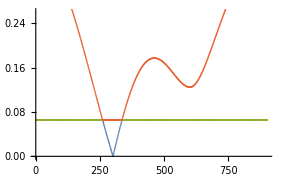

```mathematica
ListPlot@dispΓKMΓ[[1]]
```

```mathematica
dispΓKMΓ[[1,1]][[;;,2]]
```

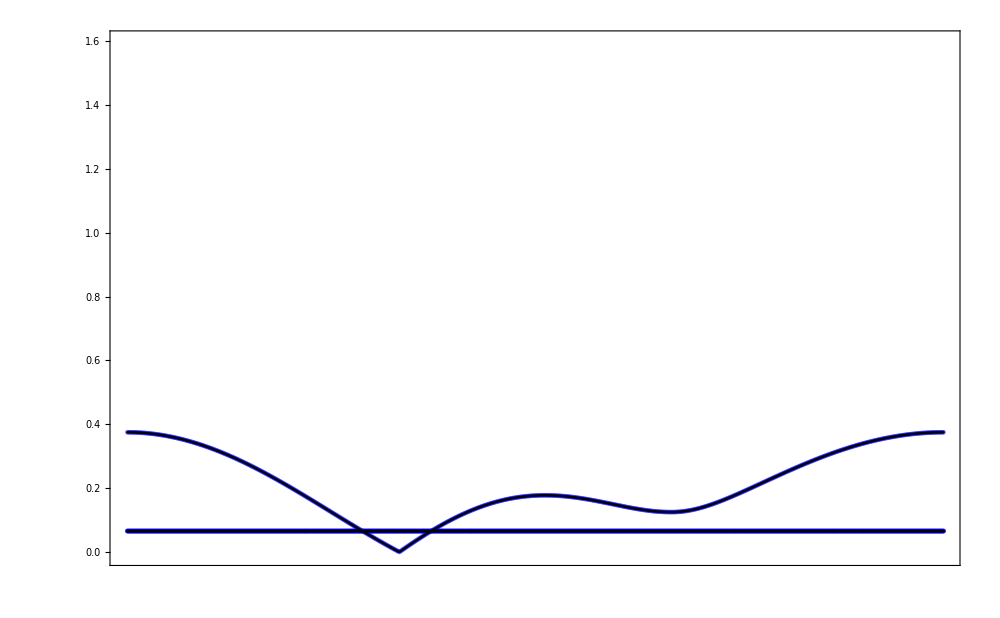

```mathematica
size=0.003;
p0=1;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->False ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.95}],Scaled[{0.5,1}],Scaled[2.5]  ],
 PlotStyle->  {{ Blue,Opacity[0.4],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],   PlotStyle->  {{ Black,Opacity[0.8],PointSize[0.58size]}} ] 
}]
]
```

#### plain ΓKMΓ

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
pathΓKMΓ=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,Kpoint,Mpoint,Γpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Black,Dashed,Opacity[0.5],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
EnergiesSortedWΓKMΓ[L_,Jm_,h_,λ_,U_,W_] :=  Module[ {line = toLineΓKMΓ[L]},
Table[Chop@cutNegativeEV[Eigensystem@N@HmfMomentum[Jm,h,λ,U,W, line⟦i⟧]]  , {i,1,L}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i   , E⟦i⟧⟦j,2⟧ }, {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,λ,L,Nc, En,Disp,Jm,U,W},L=Ls[[1]];
(*{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];*)
U={χGx,χGy,χGz};W={ωGA,ωGB};
 L = 120;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
Nc=L^2;
λ=parameters[[1,p]][[10]]{ h,h};
En = EnergiesSortedWΓKMΓ[L, Jm,h,λ,U,W] ;
Disp = lineDispersionSortedW[En];
dispΓKMΓ[[p]] = Disp    ],{p,1,Length@parameters[[1]]}];
```

```mathematica
ListPlot@dispΓKMΓ[[1]]
```

-Graphics-

```mathematica
dispΓKMΓ[[1,1]][[;;,2]]
```

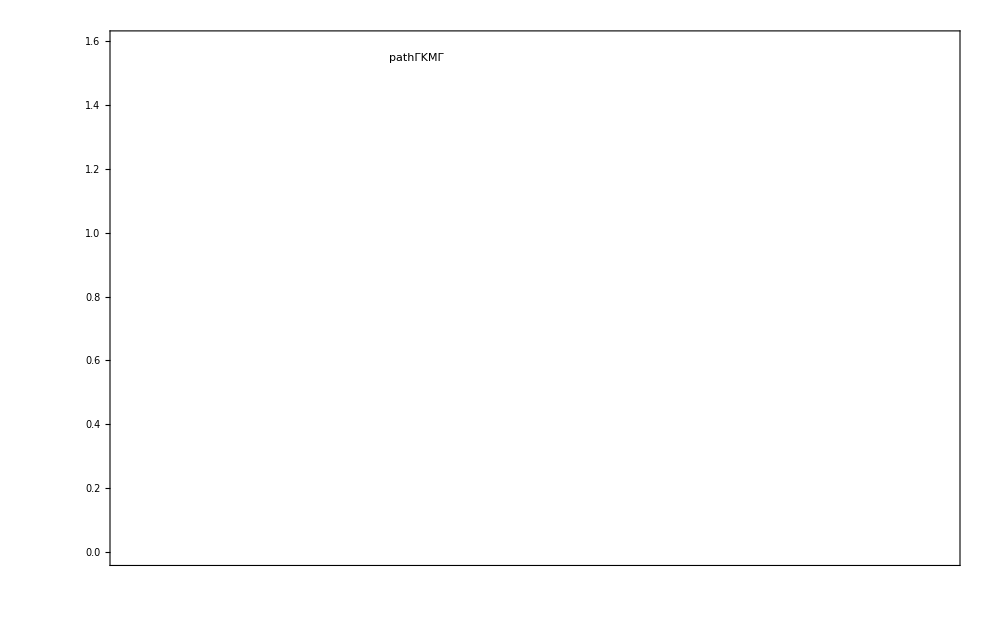

```mathematica
size=0.003;
p0=1;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->False ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.95}],Scaled[{0.5,1}],Scaled[2.5]  ],
 PlotStyle->  {{ Blue,Opacity[0.4],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],   PlotStyle->  {{ Black,Opacity[0.8],PointSize[0.58size]}} ] 
}]
]
```

#### sort for join

```mathematica
pairCP[changepoints_]:=If[Length@changepoints<= 2,{{3,3,3},{1,0,0}},  If[ Subtract@@changepoints[[1;;2,1]] ==0,changepoints[[1;;2]],pairCP@Drop[changepoints,1]   ]   ];
```

```mathematica
sortContinuos[ev_]:=Module[{L,evN=ev,Δcp=2,changepoints,a=0}, L=Length[ev];
While[ a<10 && Δcp>=2  , a=a+1;
changepoints=Sort@Flatten[   Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   )  ,1] ;
Δcp=Length[   Select[ Split@Select[Flatten[changepoints],IntegerQ[#] && #>4&], Length[#]==2&]       ];
PrintTemporary[a];
If[Δcp<1,Continue[]  ];
(*Print[ "Δcp=", Δcp,"; points= ",Sort[    changepoints   ]   ];*)
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints];
evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]]   ],evN           ] 
(*Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];*)
]  ;evN];
```

```mathematica
Module[{j0,L0,χ0,ω0,ξG,EnList0,p=1,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp,line },
L0=Ls[[1]];
L=1800;
line = toLineΓKMΓKMM[L];
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L0,acuracy,"free",NbName ]  ];
ev= sortContinuos@Table[Chop[cutNegativeEV[Eigenvalues@N@HMFk[J,K,Γ,h,χ0,ω0,η,line⟦i⟧]],10^-9]  , {i,1,L}]  ; 
disp=  Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ];
];
```

```mathematica
(*ListPlot[     disp , PlotRange->Full,Joined->True]*)
```

#### plain ΓKMΓ

```mathematica
dispersionContinumΓKMΓ[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line,ks,Ne,Δt,M=L,ev},
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1;  
line=Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1];
ev= sortContinuos@Table[Chop@cutNegativeEV[ Eigenvalues@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧ ] ]    , {i,1,L}]  ; 
Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ]
 ];
```

```mathematica
pathΓKMΓ=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,Kpoint,Mpoint,Γpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Black,Dashed,Opacity[0.5],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
dispΓKMΓ[[p]] = dispersionContinumΓKMΓ[L, J,K, Γ, h,χ0,ω0,η] ;      ],{p,1,Length@parameters[[1]]}];
```

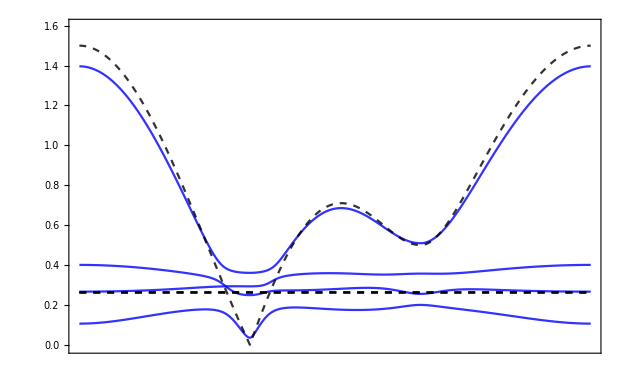

```mathematica
size=0.003;
p0=2;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->True ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.95}],Scaled[{0.5,1}],Scaled[2.5]  ],
 PlotStyle->  {{ Blue,Opacity[0.8],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],  Joined->True ,PlotRange->All, PlotStyle->  {{ Black,Dashed,Opacity[0.8],PointSize[0.4size]}} ] 
}]
]
```

## MF -- microscopic parameters

```mathematica
fgη[0.1]
```

0.598048

```mathematica
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;  (*  κ=0.1 : h=0.3292;   κ=0.2 : 0.41475; κ=0.05 : 0.2612 *)
(*
parameters= Table[Flatten[ 
Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];*)
ClearAll[fgη];
fgη[x_]:=4( 0.14846626697716298+0.01617301308149943 x-0.10144606468699975 x^2+0.4917695763340755 x^3-0.4877422141067209 x^4);
fgη[x_/;x>0.8]:=fgη[0.8];
λhs= Table[ {Norm@x,fgη[Norm@x] }, {x,hs  }];

Module[{parameters0,parameters1},
parameters0=Tuples[{Js,Ks,Γs,hs}];
parameters1=Tuples[{Js,Ks,Γs,hV}];
parameters={Table[  Flatten[{ parameters0[[i]][[1;;4]],parameters1[[i]][[1;;4]],{0},-fgη[parameters1[[i]][[4,1]]]  },1],  {i,1,Length@parameters0}]};       ];

χGx = -{{0.5248657458506312014761390306,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy =- {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz =- {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = {{ⅈ,0,0,0},{0,ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,ⅈ}};ωGB = ωGA;
```

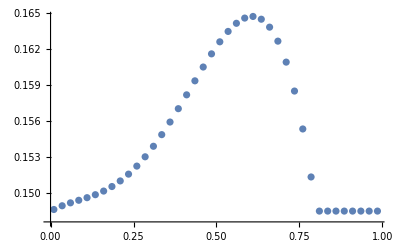

```mathematica
ListPlot@λhs
```

```mathematica
parameters
```

{{{0.,-1.,0.,{0.0288675,0.0288675,0.0288675},0.,-1.,0.,{0.05,0,0},0,-0.14908},{0.,-1.,0.,{0.0866025,0.0866025,0.0866025},0.,-1.,0.,{0.15,0,0},0,-0.150022},{0.,-1.,0.,{0.144338,0.144338,0.144338},0.,-1.,0.,{0.25,0,0},0,-0.151948},{0.,-1.,0.,{0.202073,0.202073,0.202073},0.,-1.,0.,{0.35,0,0},0,-0.155465}}}

```mathematica
χGx = Abs@{{0.5248657458506312014761390306,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = Abs@{{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz = Abs@{{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = {{ⅈ,0,0,0},{0,ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,ⅈ}};ωGB = ωGA;
```

```mathematica
WPG = N@With[{h=hc},Sum[  h[[α]]/Norm[h] Mmat[[α]] ,{α,1,3}] ];
```

## SO(4) loop -- momentum

### testing

```mathematica
(*Tr[ Transpose[WPG].# ]&/@ (Mmat)
χG={χGx,χGy,χGz};
MatrixForm/@χG
MatrixForm/@Table[ - 16  Mmat[[γ]].χG[[γ]].Mmat[[γ]] ,{γ,1,3}]
Print@MatrixForm@DiagonalMatrix[{a,b,c,d}];
MatrixForm/@Table[ - 16  Mmat[[γ]].DiagonalMatrix[{a,b,c,d}].Mmat[[γ]] ,{γ,1,3}]
gmat=Normal@SparseArray[ {{i_,j_}/;j>i:>g[i,j]},{4,4}]
Print@MatrixForm@gmat;
MatrixForm/@Table[ - 16  Mmat[[γ]].gmat.Mmat[[γ]] ,{γ,1,3}]*)
```

```mathematica
p=1;l=1;
 gauge="free_lambda";L=Ls[[l]];EnList={{},{},{}};Δ1=1;Δ2=1;Δωseq={};Δseq={};hp=Mod[p,Length@hV,1];G=Gmat;Δω=0;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
Nc=L^2;
λ=parameters[[1,p]][[10]]{ h,h};
(*If[ p==1, χG={χGx,χGy,χGz}; ωG={ωGA,ωGB}; ];*)
UG={χGx,χGy,χGz}; WG={ωGA,ωGB};  WPG = N@With[{hn=(h+10^-9 hc)},Sum[  hn[[α]]/Norm[hn] Mmat[[α]] ,{α,1,3}] ];
U=UG; W=WG;  
(*U=0  UG; W={WPG,WPG};  *)
Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=(", h,"); ","λ=",λ[[1,1]] ];
(*Print@Jm;*)
kTable=toMomentumTable[L];
For[j=1,j<=50&&Δ1 >= 10^-5, j++,  
u=Chop@Total@Table[
 Module[{H,Hr,Un,𝕌,𝕌less,𝕌gtr,k,icc,Tk  },
k=kTable[[l]];
Tk=1/(√2)Tmom[k](*KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]*);
H=HmfMomentum[Jm,h,λ, U,W, k];
Hr=Tk† . H . Tk; 
Un=UmatK[Hr];
𝕌=Tk . Un;
𝕌gtr=𝕌[[;;,1;;4]];
𝕌less=𝕌[[;;,5;;8]]; 
(*icc=(icc-Transpose[icc])/2;*)
(*Re@iccK[icc,k]*)
(2ⅈ/Nc)Conjugate@Chop@{      
(* 𝕌gtr^* . 𝕌gtr^ᵀ Exp[ⅈ k . nx]+ *)𝕌less . 𝕌less† Exp[-ⅈ k . nx],
(* 𝕌gtr^* . 𝕌gtr^ᵀ Exp[ⅈ k . ny]+ *)𝕌less . 𝕌less† Exp[-ⅈ k . ny],
(* 𝕌gtr^* . 𝕌gtr^ᵀ+ *)𝕌less . 𝕌less†       } 
(*{icc Exp[I k . nx]+ConjugateTranspose@icc Exp[-I k . nx],icc Exp[I k . ny]+ConjugateTranspose@icc Exp[-I k . ny],icc } *)
 ]
,{l,1,Nc}]; 
(*U[[1]]=Table[ u[[1]][[α,β+4]]   ,  {α,1,4},{β,1,4} ];
U[[2]]=Table[ u[[2]][[α,β+4]]   ,  {α,1,4},{β,1,4} ];
U[[3]]=Table[ u[[3]][[α,β+4]]   ,  {α,1,4},{β,1,4} ];
W[[1]]=Table[ u[[3]][[α,β]]          ,  {α,1,4},{β,1,4} ];
W[[2]]=Table[ u[[3]][[α+4,β+4]] ,  {α,1,4},{β,1,4} ];*)
U[[1]]=u[[1]][[1;;4,5;;8]] ;
U[[2]]=u[[2]][[1;;4,5;;8]];
U[[3]]=u[[3]][[1;;4,5;;8]];
W[[1]]=u[[3]][[1;;4,1;;4]];
W[[2]]=u[[3]][[5;;8,5;;8]]; 
(*Print[MatrixForm/@u];*)
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;  
Δω=2/(2 3)Sum[Abs@Tr[Transpose[W[[σ]]].G[[α]] ],{σ,1,2},{α,1,3}] ; Δωseq={Δωseq,{j,Δω}} ;]; 

cmf=cMF[Jm,U,W];   
Esum=Total[  Sum[  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]] ]  ] ,{l,1,Nc}][[1;;4]] ]/(Nc); 

Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω,
"; en=", NumberForm[Re@enMF[Jm,U,W,h,λ],{5,5}],
"; cmf=",NumberForm[Re@#,{5,5}]&@cmf,"; Esum=",NumberForm[Re@#,{5,5}]&@Esum,
"; <Hmf>=",NumberForm[Re@#,{5,5}]&@(1/2 Esum-cmf),"; Wp=", 
NumberForm[#,{5,5}]&/@ Re@{ Product[W⟦σ⟧[[2,3]]W⟦σ⟧[[3,4]] W⟦σ⟧[[4,2]],{σ,1,2}] , (U⟦1⟧⟦2,2⟧)^2 (U⟦2⟧⟦3,3⟧)^2 (U⟦3⟧⟦4,4⟧)^2 }     ];

If[j>40, Print["<icc>=",MatrixForm/@Chop[u,0.0006] ]   ];
(*If[j>40,   Print["U=",MatrixForm/@ Chop[U,0.0006], ";  W=",MatrixForm/@ Chop[W,0.0006] ]     ];  *)
u2=u;  	
];
Print["<icc>=",MatrixForm/@Chop[u,0.0006] ]  
(*
Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω, ";  <icc>=",MatrixForm/@Chop[u,0.0001](*MatrixForm/@  U, ";  W=",MatrixForm/@ W*)]; *)
```

J=0.; K=-1.; G=0.; L=40; h=({0.0057735,0.0057735,0.0057735}); λ=-0.00343219

j=1; Δ=1; Δω=0; en=-0.52498; cmf=-0.52485; Esum=-3.25460; <Hmf>=-1.10250; Wp={7.10750×10^-15,6.88050×10^-30}

j=2; Δ=1.99786; Δω=0.0724804; en=-1.00050; cmf=-0.99987; Esum=-4.01830; <Hmf>=-1.00930; Wp={8.30520×10^-12,1.25260×10^-29}

$Aborted

<icc>={(0 | -0.00198149 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.00797271 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.997901 | 0 | 0 | 0.00198149 | 0 | 0 | 0.00797271
0 | 0 | -0.00101621 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | -0.00198149 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.00797271 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.00101621 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.997901 | 0 | 0.00198149 | 0 | 0 | -0.00797271
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0.+1. ⅈ | 0.00198651 | 0.00198651 | 0.00273886 | -0.999988 | 0 | 0 | 0
-0.00198651 | 0.+1. ⅈ | -0.0450814 | 0.00799537 | 0 | 0 | 0 | 0
-0.00198651 | 0.0450814 | 0.+1. ⅈ | -0.00799537 | 0 | 0 | 0 | 0
-0.00273886 | -0.00799537 | 0.00799537 | 0.+1. ⅈ | 0 | 0 | 0 | 0.999868
0.999988 | 0 | 0 | 0 | 0.+1. ⅈ | 0.00198651 | 0.00198651 | 0.00273886
0 | 0 | 0 | 0 | -0.00198651 | 0.+1. ⅈ | -0.0450814 | 0.00799537
0 | 0 | 0 | 0 | -0.00198651 | 0.0450814 | 0.+1. ⅈ | -0.00799537
0 | 0 | 0 | -0.999868 | -0.00273886 | -0.00799537 | 0.00799537 | 0.+1. ⅈ)}

J=0.; K=-1.; G=0.; L=40; h=({0.0057735,0.0057735,0.0057735}); λ=-0.00343219

j=1; Δ=1; Δω=0; en=-1.57470; cmf=-1.57450; Esum=-6.29840; <Hmf>=-1.57470; Wp={7.10750×10^-15,0.99977}

j=2; Δ=0.000717671; Δω=0.0110023; en=-1.57470; cmf=-1.57450; Esum=-6.29840; <Hmf>=-1.57470; Wp={7.10750×10^-15,0.99976}

j=3; Δ=0.000561917; Δω=0.00875478; en=-1.57470; cmf=-1.57450; Esum=-6.29840; <Hmf>=-1.57470; Wp={7.10770×10^-15,0.99975}

$Aborted

<icc>={(0 | 0 | -0.000659074 | 0 | -0.524865 | 0 | 0 | 0
0 | 0 | 0 | -0.00438447 | 0 | 0.999958 | 0 | 0
0.000659074 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0510996 | 0 | 0 | 0 | 0 | 0 | -0.000659074 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.000659074 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.00438447 | 0 | 0),(0 | -0.000659074 | 0 | 0 | -0.524865 | 0 | 0 | 0
0.000659074 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.00438447 | 0 | 0 | 0.999958 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0510996 | 0 | 0 | 0 | 0 | -0.000659074 | 0 | 0
0 | 0 | 0 | 0 | 0.000659074 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.00438447 | 0),(0.+1. ⅈ | 0.00219616 | 0.00219616 | 0.00219616 | -0.524865 | 0 | 0 | 0
-0.00219616 | 0.+1. ⅈ | -0.00438485 | 0.00438485 | 0 | 0 | 0 | 0
-0.00219616 | 0.00438485 | 0.+1. ⅈ | -0.00438485 | 0 | 0 | 0 | 0
-0.00219616 | -0.00438485 | 0.00438485 | 0.+1. ⅈ | 0 | 0 | 0 | 0.999958
0.524865 | 0 | 0 | 0 | 0.+1. ⅈ | 0.00219616 | 0.00219616 | 0.00219616
0 | 0 | 0 | 0 | -0.00219616 | 0.+1. ⅈ | -0.00438485 | 0.00438485
0 | 0 | 0 | 0 | -0.00219616 | 0.00438485 | 0.+1. ⅈ | -0.00438485
0 | 0 | 0 | -0.999958 | -0.00219616 | -0.00438485 | 0.00438485 | 0.+1. ⅈ)}

```mathematica
toMomentumTable[L_]:=N@Table[
Module[{p1,p2},
p1=Mod[n,L];
p2=(n-p1)/L;
{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}
],{n,0,L^2-1}]
```

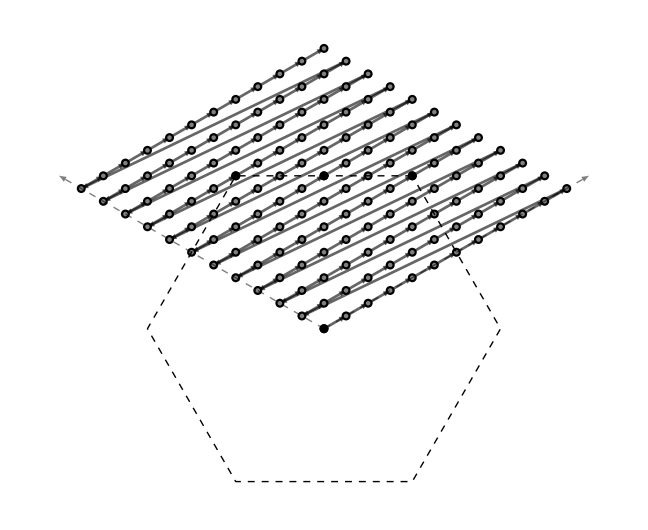

```mathematica
Module[{ps=.01,mag=1.7,L=12},
Graphics[{
{Black,Thickness[0.3ps],Opacity[.6],Arrowheads[{{2ps,0.57}}],
Arrow[#]&/@Partition[  toMomentumTable[L]  ,2,1]},
{Black,PointSize[ps],Opacity[1],Point[toMomentumTable[L]] },
{Gray,PointSize[0.5ps],Opacity[1],Point[toMomentumTable[L]] },
(*{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,Kpoint,Mpoint,Γpoint}  ,2,1]},*)
{Black,PointSize[ps],Point[Mpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
{Black,Dashed,Opacity[0.5],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]
]
```

```mathematica
E0[k_]:=2Abs[ Exp[ ⅈ k.nx] +Exp[ ⅈ k.ny]+1];
```

```mathematica
1/2 1/(2Pi)^2 NIntegrate[E0[{kx-ky,(kx+ky)/(√3)}],{ky,0,2π},{kx,0,2π}]
```

1.5746

```mathematica
Module[{L,Nc,kTable,Esum},        L=100; Nc=L^2;kTable=toMomentumTable[L]; 
(*enlevels= Flatten[ Table[       Thread[ { l,  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]]]]   }]      , {l,1,Nc}] ,1];*)
Print[-  1/(2Nc)Sum[  1/4 E0[kTable[[l]] ], {l,1,Nc}]   ];
Esum=1/Nc Total@Sum[  Sort[   Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]]]]   ][[1;;4]] , {l,1,Nc}];
Print[ Esum    ];
Print[ 1/2 Esum - cMF[Jm,U,W]    ]


]
```

-0.393649

-1.57461

-0.393649+0. ⅈ

```mathematica
MatrixForm/@Mmat
```

{(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
MatrixForm/@Gmat
```

{(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

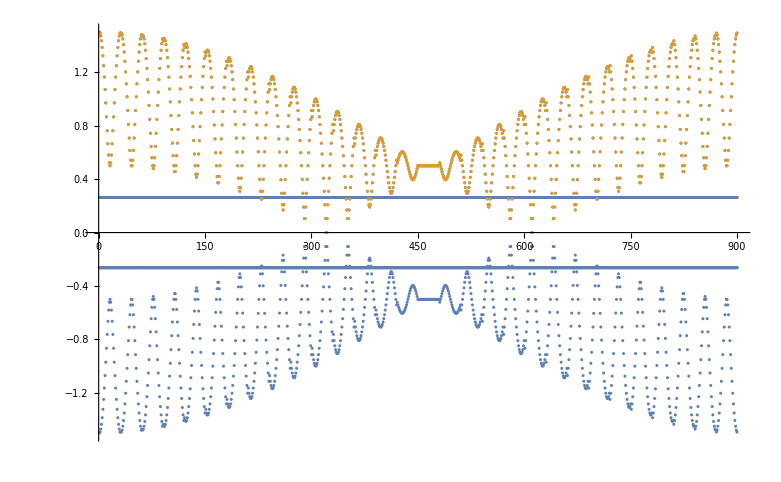

```mathematica
Module[{L,Nc,kTable},
L=30;
Nc=L^2;
kTable=toMomentumTable[L]; 
enlevels= Flatten[ Table[       Thread[ { l,  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]]]]   }]      , {l,1,Nc}] ,1];
en0levels=  Table[       { l, 1/4 E0[kTable[[l]] ]    }      , {l,1,Nc}]; 
ListPlot[  {enlevels,en0levels}  ]  
]
```

```mathematica
MatrixForm/@Module[{M=Mmat}, Re@Table[ 1/2 Jm[[γ]][[α,β]]  Tr[ U[[γ]]ᵀ. M[[α]].U[[γ]].M[[β]] ]  ,{α,1,3},{β,1,3},{γ,1,3}]          ]
```

{(-0.524876 | 0. | 0.
0. | 0. | 0.
0. | 0. | 0.),(0. | 0. | 0.
0. | -0.524876 | 0.
0. | 0. | 0.),(0. | 0. | 0.
0. | 0. | 0.
0. | 0. | -0.524876)}

```mathematica
nv={nx,ny,ny 0};
```

```mathematica
MatrixForm@Module[{A,At,Att,Ar,M=Mmat,k={0,0},Tk
(*KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]*)}, 
Tk=1/(√2)DiagonalMatrix[ {1,1,1,1,     1,Exp[-ⅈ k.nx],Exp[-ⅈ k.ny],1} ].KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ] ;(*KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,Exp[ⅈ k.nx],Exp[ⅈ k.ny],1}},{4,4}] ];*)
A= 1/2 ⅈ Sum[ Jm[[γ]][[α,β]]   M[[α]].U[[γ]].M[[β]] Exp[ⅈ k.nv[[γ]] ]   ,{α,1,3},{β,1,3},{γ,1,3}] ; 
At=  KroneckerProduct[ {{0,1},{0,0}},A];
Att= Simplify[At†+At, {kx>0,ky>0}];
(*Print@MatrixForm@N@Tk;
Print@MatrixForm[Chop@( Tk†.Att.Tk)];*)
Ar=(Tk†.Att.Tk)[[ {1,5},{1,5}]];
Print[ MatrixForm[Chop@Ar]  ];
Eigenvalues[ Ar ][[1]];
(Tk†.Att.Tk)[[ {2,4},{2,4}]]
        ]
```

(-1.5 | 0
0 | 1.5)

(0.262438+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.262438+0. ⅈ)

```mathematica
ClearAll[kx,ky];
DiagonalMatrix[ {1,1,1,1,     1,Exp[ⅈ kx],Exp[ⅈ ky],1} ].KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]
```

{{1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,1},{ⅈ,0,0,0,-ⅈ,0,0,0},{0,ⅈ ⅇ^(ⅈ kx),0,0,0,-ⅈ ⅇ^(ⅈ kx),0,0},{0,0,ⅈ ⅇ^(ⅈ ky),0,0,0,-ⅈ ⅇ^(ⅈ ky),0},{0,0,0,ⅈ,0,0,0,-ⅈ}}

```mathematica
With[{α=1,β=1,γ=1,M=Mmat}, 
Print@MatrixForm[   M[[α]].U[[γ]].M[[β]] ];
Print@MatrixForm[  U[[γ]]ᵀ. M[[α]].U[[γ]].M[[β]] ];
Tr[ U[[γ]]ᵀ. M[[α]].U[[γ]].M[[β]] ] 
 ]
```

(-1. | 0. | 0. | 0.
0. | 0.524876 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)

(0.524876 | 0. | 0. | 0.
0. | 0.524876 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)

1.04975

```mathematica
MatrixForm/@Chop[W,0.001]
```

{(0.+1. ⅈ | 0.00165938 | 0.00165938 | 0.00165938
-0.00165938 | 0.+1. ⅈ | -0.00201926 | 0.00201926
-0.00165938 | 0.00201926 | 0.+1. ⅈ | -0.00201926
-0.00165938 | -0.00201926 | 0.00201926 | 0.+1. ⅈ),(0.+1. ⅈ | 0.00165938 | 0.00165938 | 0.00165938
-0.00165938 | 0.+1. ⅈ | -0.00201926 | 0.00201926
-0.00165938 | 0.00201926 | 0.+1. ⅈ | -0.00201926
-0.00165938 | -0.00201926 | 0.00201926 | 0.+1. ⅈ)}

```mathematica
MatrixForm/@Chop[U,0.001]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

```mathematica
(*enMF[Jm_,U_,W_,h_,λ_]:=Module[{M=Mmat,G=Gmat},{Sum[  Jm[[γ]][[α,β]] (Tr[W[[1]]^ᵀ.M[[α]] ] Tr[W[[2]]^ᵀ.M[[β]] ]  + 2  Tr[ U[[γ]]^ᵀ. M[[α]].U[[γ]].M[[β]] ]     ),{α,1,3},{β,1,3},{γ,1,3}]
,Sum[   -h[[γ]] Tr[W[[σ]]^ᵀ.M[[γ]] ] +λ[[σ,γ]] Tr[W[[σ]]^ᵀ.G[[γ]] ]       ,{σ,1,2},{γ,1,3}]}];*)
```

```mathematica
MatrixForm@Re@W[[1]]
```

(0. | 0 | 0 | 0
0 | 0. | 0 | 0
0 | 0 | 0. | 0
0 | 0 | 0 | 0.)

```mathematica
W[[1]][[1,4]]+W[[1]][[2,3]]
```

```mathematica
Re[  Tr[ Transpose[W[[2]]].# ]&/@Mmat ]
```

{0.577336,0.577336,0.577336}

```mathematica
Δt=UnitConvert[ Quantity[AbsoluteTime[] -t0, "Seconds" ], "Hours" ];
	Δseq=Partition[Flatten[Δseq],2]; Δωseq=Partition[Flatten[Δωseq],2];

Module[{cyc={{3,4},{4,2},{2,3} }, R={  3  ,2 ,1   ,3  ,2  ,1 }  },
Wp={ Product[   Extract[W[[ Mod[i,2,1]  ]],   cyc[[R[[i]]]]    ]  ,{i,1,6}],Product[ Module[{γ=cyc[[R[[i]]]] ⟦g⟧  },U[[γ-1 ]][[γ,γ]]]  ,{i,{1,3,5}},{g,1,2}]};  ];


Module[{ωv,χv},
ωv={Table[W[[1]],{r,1,Nc} ],Table[W[[2]],{r,1,Nc} ] };
χv={Table[U[[1]],{r,1,Nc} ], Table[U[[2]],{r,1,Nc}], Table[χ[[3]],{r,1,Nc}]  };
EMF=EnMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
EMF0=EnMF0[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
Eλ=EnLagMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
];                                   

Esum=Total[  Sum[  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]] ]  ] ,{l,1,Nc}][[1;;4]] ]/(2Nc); 

	dataToFile[parameters[[1,p]],L,acuracy,{j,L,U,W,{0,0},{{EMF,EMF0},Esum,{EMF+Eλ,EMF0+Eλ},Δseq,Δωseq,Wp}},gauge,NbName]; 
Print["Max Step = ", j,"; Wp=",Total[Wp], "; Delta=",Δ1, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ],"; E=",{EMF,Esum,EMF+Eλ,EMF0},"; p=",p,"/",Length@parameters[[1]] ];
	{jG,LG,UG,UG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];
 ];
```

### loop : changing λ

```mathematica
f=(a +b x)/.FindFit[   λh ,  a +b  x,{a,b},x]
```

0.145327+0.0277188 x

```mathematica
λcs = Join[{-0.1474563477740904,-0.1497631822919772,-0.151624737871482,-0.155238374679877},
{-0.14462019062140619,-0.14889811341884163,-0.15072923311348285,-0.1536836129010679},{-0.14516146965429866,-0.148737833369325,-0.1511478988508086,-0.15433802266165175},
{-0.14905145544111398,-0.15022322125364185,-0.15248435747369737,-0.15633285924056683}];
```

```mathematica
λcs={-0.14844967512330798,-0.1488993496141917,-0.1491254463369489,-0.14921866652156845,-0.14934501771141395,-0.1495741183475523,-0.14977398138439035,-0.15001384618300684,-0.15029673467363652,-0.1506260320006882,-0.15103773228648487,-0.15147304646382323,-0.15196677516627724,-0.15252289859240645,-0.15314503459582887,-0.15385587584164287,-0.15461999094550294,-0.15545544912743567,-0.1563603988387796};
λh = Sort@Thread[{  Join[Table[h,{h,.01,0.375,.02}],Table[h,{h,.001,0.071,.01}]],-Join[λcs,{-0.14461742230698005,-0.14845043345623532,-0.14888213109221793,-0.14890164864400934,-0.14909394958089228,-0.14912935929456062,-0.14917272936806247,-0.14922421375368233}]}];
f=(a +b x)/.FindFit[   λh ,  a +b  x,{a,b},x]
```

0.147594+0.0200604 x

```mathematica
Δλh=Table[  {λh[[i,1]], (f/.x->λh[[i,1]]) -λh[[i,2]]},{i,1,Length@λh}]
g=  (     (a + b x + c x^2+d x^3)/.FindFit[   Δλh[[4;;-1]] ,a+ b x + c x^2+d x^3,{a,b,{c,-0.06},{d,-0.097}},x]    )
g4=  (     (a + b x + c x^2+d x^3+e x^4)/.FindFit[   Δλh[[3;;-1]] ,a+ b x + c x^2+d x^3+e x^4,{a,b,{c,-0.06},{d,-0.097},e},x]    )
g4=  (     (a+ b x + c x^2+d x^3+e x^4)/.FindFit[   Δλh[[3;;-1]] ,a+b x + c x^2+d x^3+e x^4,{a,b,c,d,e},x]    )
```

{{0.001,0.00299658},{0.01,-0.000655125},{0.011,-0.000635822},{0.021,-0.000866916},{0.03,-0.000703591},{0.031,-0.00068583},{0.041,-0.000677527},{0.05,-0.00052848},{0.051,-0.000512333},{0.061,-0.000355099},{0.07,-0.000220493},{0.071,-0.000205979},{0.09,0.000054364},{0.11,0.000226471},{0.13,0.000427816},{0.15,0.000589159},{0.17,0.000707478},{0.19,0.000779389},{0.21,0.000768896},{0.23,0.00073479},{0.25,0.000642269},{0.27,0.000487353},{0.29,0.000266425},{0.31,-0.0000432086},{0.33,-0.000406116},{0.35,-0.000840366},{0.37,-0.00134411}}

-0.00119865+0.0149301 x-0.00650325 x^2-0.0948678 x^3

-0.00087232+0.00388738 x+0.101446 x^2-0.49177 x^3+0.487742 x^4

-0.00087232+0.00388738 x+0.101446 x^2-0.49177 x^3+0.487742 x^4

```mathematica
f-g4
```

0.148466+0.016173 x-0.101446 x^2+0.49177 x^3-0.487742 x^4

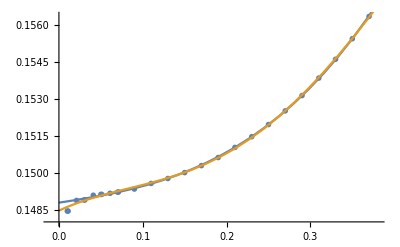
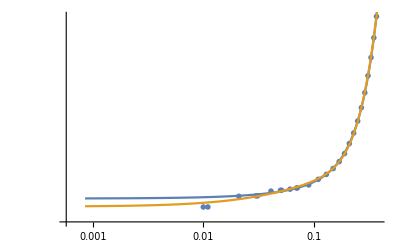
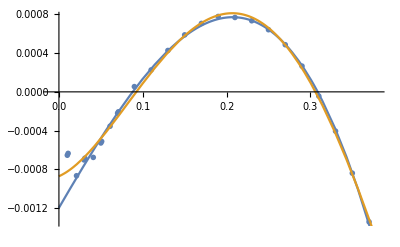

```mathematica
Row[{ 
Show[ ListPlot[ λh[[2;;-1]] , PlotMarkers->"OpenMarkers",ImageSize->400,PlotRange->{{-0.01,.38},All}], Plot[{f-g,f-g4},{x,0,.86}]   ],
Show[ ListLogLogPlot[ λh[[2;;-1]], PlotMarkers->"OpenMarkers",ImageSize->400,PlotRange->{{-0.01,.38},All}], LogLogPlot[ {f-g,f-g4},{x,0,.87}]   ] ,
Show[ ListPlot[ Δλh[[2;;-1]] , PlotMarkers->"OpenMarkers",ImageSize->400,PlotRange->{{-0.01,.38},All}], Plot[{g,g4},{x,0,.7}]   ] 
}]
```

```mathematica
Ls =Range[32,32,2]; 	    tV={0};				hV={{0.001,0,0}};
steps=250;                                     acuracy=3;                             (* ΔeV=0.04999;*) ΔeV=0.099999; eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ;  (*Table[ev,{ev,1500,1500,100}];*)
Js={0.};Ks={-1.};Γs={0.};(* Table[γ,{γ,0.,.0,.2}];*)
h0V =  Table[h,{h,.1,.1}];
hV=Table[{h,0,0},{h,h0V}];

ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
Δηs=(*{.450}; *)Table[Δη,{Δη,.0,.04,.005}];
(*λcs = {-1.1474563477740904,-1.1497631822919772,-1.151624737871482,-1.155238374679877};*)
(*λcs = Join[{-0.1474563477740904,-0.1497631822919772,-0.151624737871482,-0.155238374679877},{-0.14462019062140619,-0.14889811341884163,-0.15072923311348285,-0.1536836129010679}];
*)
λcs= Table[-(0.148366928718033+0.0176034596924664 x-0.107356456971657 x^2+0.49802639028315204 x^3-0.484157728903065 x^4), {x,h0V}];
λcs={-.6};

hindex[p_]:=Ceiling[p/Length[Δηs]];
Module[{parameters0,parameters1},
parameters0=Tuples[{Js,Ks,Γs,hs,Δηs}];
parameters1=Tuples[{Js,Ks,Γs,hV,Δηs}];
parameters={Table[  Flatten[{ parameters0[[i]][[1;;4]],parameters1[[i]][[1;;4]],{0},λcs[[ hindex[i] ]]+parameters1[[i]][[5]]},1],  {i,1,Length@parameters0}]};       ];

χGx = -{{0.5248657458506312014761390306,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy =- {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz =- {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = {{ⅈ,0,0,0},{0,ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,ⅈ}};ωGB = ωGA;
```

```mathematica
jstepC=500;Δcrit=0.1;
t0=AbsoluteTime[]; 
AbsoluteTiming[
Do[ Do[ Module[{ gauge="free_lambda",Γ,J,K,L=Ls[[l]],Nc,h,Λ,T,EMF,EMF0,Esum,cmf,Emf,Eλ,En,EnList={{},{},{}},u,u2,j,Δ1=1,Δ2=1,ES,gap,Δt,kTable,Δω,
Wp,Δωseq={},Δseq={},hp=Mod[p,Length@hV,1],
U,W,Jm,λ,G=Gmat},
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
Nc=L^2;
λ=parameters[[1,p]][[10]]{ h,h};
(*If[ p==1, UG={χGx,χGy,χGz}; WG={ωGA,ωGB}; ];*)
(*UG={χGx,χGy,χGz}; WG={ωGA,ωGB};  *)
WPG = N@With[{hn=(h+10^-9 hc)},Sum[  (hn[[α]]/Norm[hn])Mmat[[α]] ,{α,1,3}] ];
UG={χGx,χGy,χGz}; WG={ωGA,ωGB};
U=UG; W=WG;  

Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=",NumberForm[Norm[h],{4,4}],"; ","λ=",parameters[[1,p]][[10]]   ];
kTable=toMomentumTable[L];
For[j=1,( ( j<steps)∧(Chop[ Δ1,10^(-acuracy )]!= 0) ), j++,  
If[ (j>jstepC)∧(Δ1>=Δcrit), U=0 UG; W={WPG,WPG};];
u=Re@Chop@Total@Table[
 Module[{H,Hr,Un,𝕌,𝕌less,k,icc,𝕌gtr,Tk= IdentityMatrix[8] (*KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]*)    },
k=kTable[[l]];
H=HmfMomentum[Jm,h,λ, U,W, k];
Hr=Tk† . H . Tk; 
Un=UmatK[Hr];𝕌=Tk . Un;
𝕌less=𝕌[[;;,5;;8]];(*icc=(ⅈ/Nc)(Transpose@Chop[𝕌less . 𝕌less† ]);Re@iccK[icc,k] {icc Exp[I k . nx],icc Exp[I k . ny],icc }*)
𝕌gtr=𝕌[[;;,1;;4]];
(ⅈ/Nc)Conjugate@Chop@{      
 Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . nx]+𝕌less . 𝕌less† Exp[-ⅈ k . nx],
 Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . ny]+𝕌less . 𝕌less† Exp[-ⅈ k . ny],
 Conjugate[𝕌gtr] . Transpose[𝕌gtr]+𝕌less . 𝕌less†        } 
],{l,1,Nc}]; 
U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];W[[1]]=u[[3]][[1;;4,1;;4]];W[[2]]=u[[3]][[5;;8,5;;8]];
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;  

Δω=(1/(2 2 3 ))Sum[Abs@Tr[Transpose[W[[σ]]].G[[α]] ]/Abs@Tr[Transpose[W[[σ]]].Nmat[[α]] ],{σ,1,2},{α,1,3}] ; Δωseq={Δωseq,{j,Δω}} ;]; 

cmf=cMF[Jm,U,W];   
Esum=Total[  Sum[  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]] ]  ] ,{l,1,Nc}][[1;;4]] ]/(Nc); 
If[j>=20,
Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω,
"; en=", NumberForm[Re@enMF[Jm,U,W,h,λ],{5,5}],
"; cmf=",NumberForm[Re@#,{5,5}]&@cmf,"; Esum=",NumberForm[Re@#,{5,5}]&@Esum,
"; <Hmf>=",NumberForm[Re@#,{5,5}]&@((1/2)Esum-cmf),"; Wp=", 
NumberForm[#,{5,5}]&/@ Re@{ Product[W⟦σ⟧[[2,3]]W⟦σ⟧[[3,4]] W⟦σ⟧[[4,2]],{σ,1,2}] , (U⟦1⟧⟦2,2⟧)^2 (U⟦2⟧⟦3,3⟧)^2 (U⟦3⟧⟦4,4⟧)^2 }     ]
];
u2=u;  	(*Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω, ";  ",MatrixForm/@{  U[[1]],W[[1]] }]; *)
];
Δt=UnitConvert[ Quantity[AbsoluteTime[] -t0, "Seconds" ], "Hours" ];	Δseq=Partition[Flatten[Δseq],2]; Δωseq=Partition[Flatten[Δωseq],2];
Module[{cyc={{3,4},{4,2},{2,3} }, R={  3  ,2 ,1   ,3  ,2  ,1 }  },
Wp={ Product[   Extract[W[[ Mod[i,2,1]  ]],   cyc[[R[[i]]]]    ]  ,{i,1,6}],Product[ Module[{γ=cyc[[R[[i]]]] ⟦g⟧  },U[[γ-1 ]][[γ,γ]]]  ,{i,{1,3,5}},{g,1,2}]};  ];
Module[{ωv,χv},
ωv={Table[W[[1]],{r,1,Nc} ],Table[W[[2]],{r,1,Nc} ] };
χv={Table[U[[1]],{r,1,Nc} ], Table[U[[2]],{r,1,Nc}], Table[U[[3]],{r,1,Nc}]  };
EMF=EnMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
EMF0=EnMF0[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
Eλ=EnLagMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];  ];                                   
cmf=cMF[Jm,U,W];   
Esum=Total[  Sum[  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]] ]  ] ,{l,1,Nc}][[1;;4]] ]/(Nc); 
Emf=enMF[Jm,U,W,h,λ];
	dataToFile[parameters[[1,p]],L,acuracy,{j,L,U,W,{0,0},{{EMF,EMF0},{Esum,cmf,(1/2)Esum-cmf},{EMF+Eλ,EMF0+Eλ},Δseq,Δωseq,Wp}},gauge,NbName]; 
Print["Max Step = ", j,"; Wp=",Total[Wp], "; Delta=",Δ1, "; Δω=",Δω, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ],"; Emf=",{Esum,cmf,(1/2)Esum-cmf,Emf},"; E=",{EMF,EMF+Eλ,EMF0},"; p=",p,"/",Length@parameters[[1]] ];
	{jG,LG,UG,WG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];
 ];  , {p,1,Length[parameters[[1]] ]}  ],{l,1,Length@Ls}];]
```

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.6

Max Step = 12; Wp=0.969743; Delta=0.000833827; Δω=0.0587499; Δt = 0 h0 min; Emf={-6.29871,-1.56717,-1.58218,-1.58218}; E={-1.55345,-1.56798,-1.53973}; p=1/21

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.595

Max Step = 12; Wp=0.969706; Delta=0.000844071; Δω=0.0502563; Δt = 0 h0 min; Emf={-6.29872,-1.56718,-1.58218,-1.58218}; E={-1.55329,-1.56787,-1.53939}; p=2/21

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.59

Max Step = 12; Wp=0.969666; Delta=0.000854313; Δω=0.0419697; Δt = 0 h1 min; Emf={-6.29873,-1.56718,-1.58218,-1.58218}; E={-1.55312,-1.56777,-1.53906}; p=3/21

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.585

Max Step = 12; Wp=0.969624; Delta=0.000864552; Δω=0.0338827; Δt = 0 h1 min; Emf={-6.29873,-1.56719,-1.58218,-1.58218}; E={-1.55295,-1.56767,-1.53872}; p=4/21

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.58

Max Step = 12; Wp=0.96958; Delta=0.000874789; Δω=0.0259881; Δt = 0 h2 min; Emf={-6.29874,-1.56719,-1.58218,-1.58218}; E={-1.55279,-1.56756,-1.53839}; p=5/21

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.575

Max Step = 12; Wp=0.969532; Delta=0.000885023; Δω=0.0182791; Δt = 0 h2 min; Emf={-6.29875,-1.56719,-1.58218,-1.58218}; E={-1.55262,-1.56746,-1.53805}; p=6/21

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.57

Max Step = 12; Wp=0.969482; Delta=0.000895255; Δω=0.0107493; Δt = 0 h3 min; Emf={-6.29876,-1.56719,-1.58218,-1.58218}; E={-1.55245,-1.56735,-1.53771}; p=7/21

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.565

Max Step = 12; Wp=0.96943; Delta=0.000905485; Δω=0.00339245; Δt = 0 h3 min; Emf={-6.29877,-1.5672,-1.58219,-1.58219}; E={-1.55229,-1.56725,-1.53738}; p=8/21

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.56

Max Step = 12; Wp=0.969375; Delta=0.000915713; Δω=0.00379731; Δt = 0 h4 min; Emf={-6.29878,-1.5672,-1.58219,-1.58219}; E={-1.55212,-1.56714,-1.53704}; p=9/21

J=0.; K=-1.; G=0.; L=32; h=0.1000; λ=-0.555

$Aborted

```mathematica
{jG,LG,UG,WG,ξG,EnG}= loadData[toPath[parameters[[1,1]],Ls[[1]],acuracy,gauge,NbName ]  ];
```

```mathematica
(*EnG[[5]]
MatrixForm/@{  χG[[1]],ωG[[1]] }
ω=ωG;
MatrixForm@{{0,0,0,0,0,0,0,0},
{0,0,0,0, (-ω⟦1,3,4⟧)/(ω⟦1,2,1⟧-ω⟦1,3,4⟧),0,ω⟦1,4,1⟧/(ω⟦1,4,1⟧-ω⟦1,2,3⟧) ,0},
{0,0,0,0, (-ω⟦1,4,2⟧)/(ω⟦1,3,1⟧-ω⟦1,4,2⟧) ,0,0,ω⟦1,2,1⟧/(ω⟦1,2,1⟧-ω⟦1,3,4⟧) },
{0,0,0,0, (-ω⟦1,2,3⟧)/(ω⟦1,4,1⟧-ω⟦1,2,3⟧) , ω⟦1,3,1⟧/(ω⟦1,3,1⟧-ω⟦1,4,2⟧) ,0,0} };
{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,1]],Ls[[1]],acuracy,"free_lambda",NbName ]  ];
*)
```

### loop v2 : changing λ

```mathematica
λcs={-0.5303714554312542,-0.5626573154605023,-0.5789360910886469,-0.5961648173541212,-0.6203003355616785,-0.6573729432506717,-0.7062618374627502};
λh = Sort@Thread[ {h0V,-λcs}];
f=(a +b x)/.FindFit[   λh ,  a +b  x,{a,b},x]
```

0.499085+0.541762 x

```mathematica
Δλh=Table[  {λh[[i,1]], (f/.x->λh[[i,1]]) -λh[[i,2]]},{i,1,Length@λh}]
g=  (     (a + b x + c x^2+d x^3)/.FindFit[   Δλh[[4;;-1]] ,a+ b x + c x^2+d x^3,{a,b,{c,-0.06},{d,-0.097}},x]    )
g4=  (     (a + b x + c x^2+d x^3+e x^4)/.FindFit[   Δλh[[3;;-1]] ,a+ b x + c x^2+d x^3+e x^4,{a,b,{c,-0.06},{d,-0.097},e},x]    )
g4=  (     (a+ b x + c x^2+d x^3+e x^4)/.FindFit[   Δλh[[3;;-1]] ,a+b x + c x^2+d x^3+e x^4,{a,b,c,d,e},x]    )
```

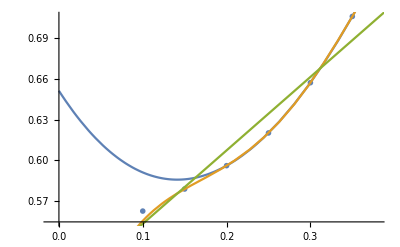
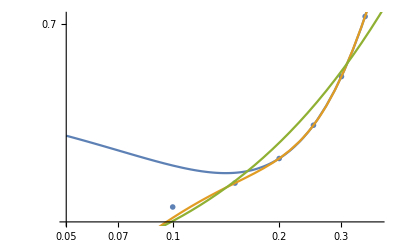
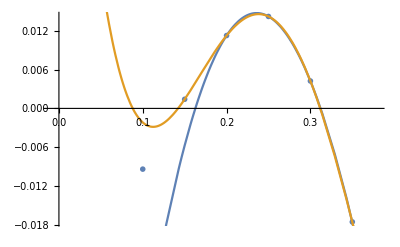

```mathematica
Row[{ 
Show[ ListPlot[ λh[[2;;-1]] , PlotMarkers->"OpenMarkers",ImageSize->400,PlotRange->{{-0.01,.38},All}], Plot[{f-g,f-g4,f},{x,0,.86}]   ],
Show[ ListLogLogPlot[ λh[[2;;-1]], PlotMarkers->"OpenMarkers",ImageSize->400,PlotRange->{{0.05,.38},All}], LogLogPlot[ {f-g,f-g4,f},{x,0.05,.87}]   ] ,
Show[ ListPlot[ Δλh[[2;;-1]] , PlotMarkers->"OpenMarkers",ImageSize->400,PlotRange->{{-0.01,.38},All}], Plot[{g,g4},{x,0,.7}]   ] 
}]
```

```mathematica
λcs
```

{-0.594473,-0.598404,-0.603978,-0.615507,-0.63262}

```mathematica
Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
steps=80;                                     acuracy=6;                             (* ΔeV=0.04999;*) ΔeV=0.099999; eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ;  (*Table[ev,{ev,1500,1500,100}];*)
Js={0.};Ks={-1.};Γs={0.};(* Table[γ,{γ,0.,.0,.2}];*)
h0V =  Table[h,{h,.01,.5,.1}];
hV=Table[{h,0,0},{h,h0V}];

ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300;
Δηs=(*{.450}; *)Table[Δη,{Δη,0,.002,.001}];
(*λcs = {-1.1474563477740904,-1.1497631822919772,-1.151624737871482,-1.155238374679877};*)
(*λcs = Join[{-0.1474563477740904,-0.1497631822919772,-0.151624737871482,-0.155238374679877},{-0.14462019062140619,-0.14889811341884163,-0.15072923311348285,-0.1536836129010679}];
*)
λcs= Table[-4( 0.14846626697716298+0.01617301308149943 x-0.10144606468699975 x^2+0.4917695763340755 x^3-0.4877422141067209 x^4), {x,h0V}];
(*λcs={-0.5816};*)

hindex[p_]:=Ceiling[p/Length[Δηs]];
Module[{parameters0,parameters1},
parameters0=Tuples[{Js,Ks,Γs,hs,Δηs}];
parameters1=Tuples[{Js,Ks,Γs,hV,Δηs}];
parameters={Table[  Flatten[{ parameters0[[i]][[1;;4]],parameters1[[i]][[1;;4]],{0},λcs[[ hindex[i] ]]+parameters1[[i]][[5]]},1],  {i,1,Length@parameters0}]};       ];

χGx = -{{0.5248657458506312014761390306,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy =- {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz =- {{0.5248657458506312014761390306,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = {{ⅈ,0,0,0},{0,ⅈ,0,0},{0,0,ⅈ,0},{0,0,0,ⅈ}};ωGB = ωGA;
```

```mathematica
jstepC=200;Δcrit=0.1;
t0=AbsoluteTime[]; 
AbsoluteTiming[
Do[ Do[ Module[{ gauge="free_lambda",Γ,J,K,L=Ls[[l]],Nc,h,Λ,T,EMF,EMF0,Esum,cmf,Emf,Eλ,En,EnList={{},{},{}},u,u2,j,Δ1=1,Δ2=1,ES,gap,Δt,kTable,Δω,
Wp,Δωseq={},Δseq={},hp=Mod[p,Length@hV,1],λp=Mod[p,Length@Δηs,1],
U,W,Jm,λ,G=Gmat},
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
Nc=L^2;
λ=parameters[[1,p]][[10]]{ h,h};
(*If[ p==1, UG={χGx,χGy,χGz}; WG={ωGA,ωGB}; ];*)
(*UG={χGx,χGy,χGz}; WG={ωGA,ωGB};  *)
WPG = N@With[{hn=(h+10^-9 hc)},Sum[  (hn[[α]]/Norm[hn])Mmat[[α]] ,{α,1,3}] ];
(*If[ λp==1, UG={χGx,χGy,χGz}; WG={ωGA,ωGB}; ];*)
UG={χGx,χGy,χGz}; WG={ωGA,ωGB};
U=UG; W=WG;  

Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=",NumberForm[Norm[h],{4,4}],"; ","λ=",parameters[[1,p]][[10]]   ];
kTable=toMomentumTable[L];
For[j=1,( ( j<steps)∧(Chop[ Δ1,10^(-acuracy )]!= 0) ), j++,  
If[ (j==jstepC)∧(Total[Wp]<=0.04), U=0 UG; W={WPG,WPG};];
u=Re@Chop@Total@Table[ 
Module[{H,Hr,Un,𝕌,𝕌less,k,icc,𝕌gtr,Tk= IdentityMatrix[8] (*KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]*)    },
				k=kTable[[l]];
				H=HmfMomentum[Jm,h,λ, U,W, k];
Hr=Tk† . H . Tk; 
Un=UmatK[Hr];𝕌=Tk . Un;
𝕌less=𝕌[[;;,5;;8]];(*icc=(ⅈ/Nc)(Transpose@Chop[𝕌less . 𝕌less† ]);Re@iccK[icc,k] {icc Exp[I k . nx],icc Exp[I k . ny],icc }*)
𝕌gtr=𝕌[[;;,1;;4]];
(2ⅈ/Nc)Conjugate@Chop@{      
 (*𝕌gtr^* . 𝕌gtr^ᵀ Exp[ⅈ k . nx]+*)𝕌less . 𝕌less† Exp[-ⅈ k . nx],
 (*𝕌gtr^* . 𝕌gtr^ᵀ Exp[ⅈ k . ny]+*)𝕌less . 𝕌less† Exp[-ⅈ k . ny],
 (*𝕌gtr^* . 𝕌gtr^ᵀ+*)𝕌less . 𝕌less†        } 
],{l,1,Nc}]; 
U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];W[[1]]=u[[3]][[1;;4,1;;4]];W[[2]]=u[[3]][[5;;8,5;;8]];
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;  
Δω=(1/(2 2 3 ))Sum[Abs@Tr[Transpose[W[[σ]]].G[[α]] ]/Abs@Tr[Transpose[W[[σ]]].Nmat[[α]] ],{σ,1,2},{α,1,3}] ; Δωseq={Δωseq,{j,Δω}} ;]; 

cmf=cMF[Jm,U,W];   
Esum=Total[  Sum[  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]] ]  ] ,{l,1,Nc}][[1;;4]] ]/(Nc); 
If[j>=30,
Wp=Re@{ Product[W⟦σ⟧[[2,3]]W⟦σ⟧[[3,4]] W⟦σ⟧[[4,2]],{σ,1,2}] , (U⟦1⟧⟦2,2⟧)^2 (U⟦2⟧⟦3,3⟧)^2 (U⟦3⟧⟦4,4⟧)^2 };
Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω,
"; en=", NumberForm[Re@enMF[Jm,U,W,h,λ],{5,5}],
"; cmf=",NumberForm[Re@#,{5,5}]&@cmf,"; Esum=",NumberForm[Re@#,{5,5}]&@Esum,
"; <Hmf>=",NumberForm[Re@#,{5,5}]&@((1/2)Esum-cmf),"; Wp=", 
NumberForm[#,{5,5}]&/@ Wp    ]
];
u2=u;  	
(*Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω, ";  ",MatrixForm/@{  U[[1]],W[[1]] }]; *)
];
Δt=UnitConvert[ Quantity[AbsoluteTime[] -t0, "Seconds" ], "Hours" ];	Δseq=Partition[Flatten[Δseq],2]; Δωseq=Partition[Flatten[Δωseq],2];
Module[{cyc={{3,4},{4,2},{2,3} }, R={  3  ,2 ,1   ,3  ,2  ,1 }  },
Wp={ Product[   Extract[W[[ Mod[i,2,1]  ]],   cyc[[R[[i]]]]    ]  ,{i,1,6}],Product[ Module[{γ=cyc[[R[[i]]]] ⟦g⟧  },U[[γ-1 ]][[γ,γ]]]  ,{i,{1,3,5}},{g,1,2}]};  ];
Module[{ωv,χv},
ωv={Table[W[[1]],{r,1,Nc} ],Table[W[[2]],{r,1,Nc} ] };
χv={Table[U[[1]],{r,1,Nc} ], Table[U[[2]],{r,1,Nc}], Table[U[[3]],{r,1,Nc}]  };
EMF=EnMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
EMF0=EnMF0[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
Eλ=EnLagMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];  ];                                   
cmf=cMF[Jm,U,W];   
Esum=Total[  Sum[  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]] ]  ] ,{l,1,Nc}][[1;;4]] ]/(Nc); 
Emf=enMF[Jm,U,W,h,λ];
	dataToFile[parameters[[1,p]],L,acuracy,{j,L,U,W,{0,0},{{EMF,EMF0},{Esum,cmf,(1/2)Esum-cmf},{EMF+Eλ,EMF0+Eλ},Δseq,Δωseq,Wp}},gauge,NbName]; 
Print["Max Step = ", j,"; Wp=",Total[Wp], "; Delta=",Δ1, "; Δω=",Δω, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ],"; Emf=",{Esum,cmf,(1/2)Esum-cmf,Emf},"; E=",{EMF,EMF+Eλ,EMF0},"; p=",p,"/",Length@parameters[[1]] ];
	{jG,LG,UG,WG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];
 ];  , {p,1,Length[parameters[[1]] ]}  ],{l,1,Length@Ls}];]
```

J=0.; K=-1.; G=0.; L=40; h=0.0100; λ=-0.594473

Max Step = 30; Wp=0.999688; Delta=9.71071×10^-7; Δω=0.0195599; Δt = 0 h1 min; Emf={-6.29843,-1.57453,-1.57468,-1.57468}; E={-1.57439,-1.57453,-1.57424}; p=1/15

J=0.; K=-1.; G=0.; L=40; h=0.0100; λ=-0.593473

Max Step = 30; Wp=0.999688; Delta=9.73465×10^-7; Δω=0.0179571; Δt = 0 h3 min; Emf={-6.29843,-1.57453,-1.57468,-1.57468}; E={-1.57438,-1.57453,-1.57424}; p=2/15

J=0.; K=-1.; G=0.; L=40; h=0.0100; λ=-0.592473

Max Step = 30; Wp=0.999688; Delta=9.7586×10^-7; Δω=0.0163621; Δt = 0 h5 min; Emf={-6.29843,-1.57453,-1.57468,-1.57468}; E={-1.57438,-1.57453,-1.57424}; p=3/15

J=0.; K=-1.; G=0.; L=40; h=0.1100; λ=-0.598404

$Aborted

### loop : changing h and fixing λ by the fit

```mathematica
jstepC=30;Wpcrit=0.05;
t0=AbsoluteTime[]; 
AbsoluteTiming[
Do[ Do[ Module[{ gauge="free_fit",Γ,J,K,L=Ls[[l]],Nc,h,Λ,T,EMF,EMF0,Esum,cmf,Emf,Eλ,En,EnList={{},{},{}},u,u3,j,Δ1=1,Δ2=1,ES,gap,Δt,kTable,Δω,
Wp,Δωseq={},Δseq={},hp=Mod[p,Length@hV,1],U,W,Jm,λ,G=Gmat},
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
λ=parameters[[1,p]][[10]]{h,h};
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
Nc=L^2;
If[ p==1, UG={χGx,χGy,χGz}; WG={ωGA,ωGB}; ];
(*UG={χGx,χGy,χGz}; WG={ωGA,ωGB};  *)
WPG = N@With[{hn=(h+10^-9 hc)},Sum[  (hn[[α]]/Norm[hn])Mmat[[α]] ,{α,1,3}] ];
U=UG; W=WG;  

Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=",NumberForm[Norm[h],{4,4}]  ];
kTable=toMomentumTable[L];
For[j=1,( ( j<steps)∧(Chop[ Δ1,10^(-acuracy )]!= 0) ), j++,  
If[ (j==jstepC)∧(Total[Wp]<=Wpcrit), U=0 UG; W={WPG,WPG};];
(*λ= If[j<10,-1.14745634  {h,h},Table[    -h[[α]] + Jm[[α]][[α,α]](Tr[W[[σ]]^ᵀ.Mmat[[α]] ]-Tr[W[[σ]]^ᵀ.Gmat[[α]] ]  ),{σ,1,2},{α,1,3}]   ];
λh= {λ[[1,1]]/h[[1]],λ[[1,2]]/h[[2]],λ[[1,3]]/h[[3]]};*)
u=Re@Chop@Total@Table[
 Module[{H,Hr,Un,𝕌,𝕌less,k,icc,𝕌gtr,Tk= IdentityMatrix[8] (*KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ]*)    },
				k=kTable[[l]];
				H=HmfMomentum[Jm,h,λ, U,W, k];
Hr=Tk† . H . Tk; 
Un=UmatK[Hr];𝕌=Tk . Un;
𝕌less=𝕌[[;;,5;;8]];(*icc=(ⅈ/Nc)(Transpose@Chop[𝕌less . 𝕌less† ]);Re@iccK[icc,k] {icc Exp[I k . nx],icc Exp[I k . ny],icc }*)
𝕌gtr=𝕌[[;;,1;;4]];
(2ⅈ/Nc)Conjugate@Chop@{      
(* 𝕌gtr^* . 𝕌gtr^ᵀ Exp[ⅈ k . nx]+*)𝕌less . 𝕌less† Exp[-ⅈ k . nx],
 (*𝕌gtr^* . 𝕌gtr^ᵀ Exp[ⅈ k . ny]+*)𝕌less . 𝕌less† Exp[-ⅈ k . ny],
 (*𝕌gtr^* . 𝕌gtr^ᵀ+*)𝕌less . 𝕌less†        } 
],{l,1,Nc}]; 
U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];W[[1]]=u[[3]][[1;;4,1;;4]];W[[2]]=u[[3]][[5;;8,5;;8]];
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u3) ];Δseq={Δseq,{j,Δ1}}  ;  
Δω=(1/(2 2 3 ))Sum[Abs@Tr[Transpose[W[[σ]]].G[[α]] ]/Abs@Tr[Transpose[W[[σ]]].Nmat[[α]] ],{σ,1,2},{α,1,3}] ; Δωseq={Δωseq,{j,Δω}} ;]; 
  
cmf=cMF[Jm,U,W];   
Esum=Total[  Sum[  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]] ]  ] ,{l,1,Nc}][[1;;4]] ]/(Nc); 
If[j>=28,Wp={ Product[W⟦σ⟧[[2,3]]W⟦σ⟧[[3,4]] W⟦σ⟧[[4,2]],{σ,1,2}] , (U⟦1⟧⟦2,2⟧)^2 (U⟦2⟧⟦3,3⟧)^2 (U⟦3⟧⟦4,4⟧)^2 };
Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω,
"; en=", NumberForm[Re@enMF[Jm,U,W,h,λ],{5,5}],
"; cmf=",NumberForm[Re@#,{5,5}]&@cmf,"; Esum=",NumberForm[Re@#,{5,5}]&@Esum,
"; <Hmf>=",NumberForm[Re@#,{5,5}]&@((1/2)Esum-cmf),"; Wp=", 
NumberForm[#,{5,5}]&/@ Re@Wp     ]
];
	u3=u;
(*Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω, "; λ=",λ[[1,1]], "; λ/h=",λ[[1,1]]/h[[1]]  , ";  ",MatrixForm/@{  U[[1]],W[[1]] }   ]; *)
];

Δt=UnitConvert[ Quantity[AbsoluteTime[] -t0, "Seconds" ], "Hours" ];	Δseq=Partition[Flatten[Δseq],2]; Δωseq=Partition[Flatten[Δωseq],2];
Module[{cyc={{3,4},{4,2},{2,3} }, R={  3  ,2 ,1   ,3  ,2  ,1 }  },
Wp={ Product[   Extract[W[[ Mod[i,2,1]  ]],   cyc[[R[[i]]]]    ]  ,{i,1,6}],Product[ Module[{γ=cyc[[R[[i]]]] ⟦g⟧  },U[[γ-1 ]][[γ,γ]]]  ,{i,{1,3,5}},{g,1,2}]};  ];
Module[{ωv,χv},
ωv={Table[W[[1]],{r,1,Nc} ],Table[W[[2]],{r,1,Nc} ] };
χv={Table[U[[1]],{r,1,Nc} ], Table[U[[2]],{r,1,Nc}], Table[U[[3]],{r,1,Nc}]  };
EMF=EnMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
EMF0=EnMF0[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
Eλ=EnLagMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];  ];                                   
cmf=cMF[Jm,U,W];   
Esum=Total[  Sum[  Sort@Eigenvalues[HmfMomentum[Jm,h,λ,U,W,kTable[[l]] ]  ] ,{l,1,Nc}][[1;;4]] ]/(Nc); 
Emf=enMF[Jm,U,W,h,λ];
	dataToFile[parameters[[1,p]],L,acuracy,{j,L,U,W,{0,0},{{EMF,EMF0},{Esum,cmf,(1/2)Esum-cmf},{EMF+Eλ,EMF0+Eλ},Δseq,Δωseq,Wp}},gauge,NbName]; 
Print["Max Step = ", j,"; Wp=",Total[Wp], "; Delta=",Δ1, "; Δω=",Δω, "; λ=",λ[[1,1]], "; λ/h=",λ[[1,1]]/h[[1]] ,"; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ],"; Emf=",{Esum,cmf,(1/2)Esum-cmf,Emf},"; E=",{EMF,EMF+Eλ,EMF0},"; p=",p,"/",Length@parameters[[1]] ];
	{jG,LG,UG,WG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];
 ];  , {p,1,Length[parameters[[1]] ]}  ],{l,1,Length@Ls}];]
```

J=0.; K=-1.; G=0.; L=32; h=0.0100

Max Step = 24; Wp=0.999524; Delta=8.84543×10^-6; Δω=0.321166; λ=-0.000858048; λ/h=-0.148618; Δt = 0 h0 min; Emf={-6.29845,-1.57452,-1.57471,-1.57471}; E={-1.57421,-1.57442,-1.5739}; p=1/40

J=0.; K=-1.; G=0.; L=32; h=0.0350

Max Step = 28; Wp=0.994129; Delta=8.52015×10^-6; Δω=0.321316; λ=-0.00300943; λ/h=-0.148928; Δt = 0 h2 min; Emf={-6.29844,-1.57342,-1.5758,-1.5758}; E={-1.56966,-1.57221,-1.5659}; p=2/40

J=0.; K=-1.; G=0.; L=32; h=0.0600

Max Step = 28; Wp=0.982638; Delta=9.02412×10^-6; Δω=0.32085; λ=-0.00516745; λ/h=-0.149171; Δt = 0 h3 min; Emf={-6.2984,-1.5711,-1.57811,-1.57811}; E={-1.55999,-1.56753,-1.54889}; p=3/40

J=0.; K=-1.; G=0.; L=32; h=0.0850

Max Step = 28; Wp=0.964818; Delta=9.91634×10^-6; Δω=0.320077; λ=-0.00733101; λ/h=-0.149385; Δt = 0 h4 min; Emf={-6.29825,-1.56748,-1.58165,-1.58165}; E={-1.54506,-1.5603,-1.52264}; p=4/40

J=0.; K=-1.; G=0.; L=32; h=0.1100

$Aborted

```mathematica
{jG,LG,UG,WG,ξG,EnG}= loadData[toPath[parameters[[1,1]],Ls[[1]],acuracy,"free_fit",NbName ]  ];
```

```mathematica
EnG
```

{{-1.57449,-1.57444},{-6.29845,-1.57455,-1.57467},{-1.57455,-1.57449},{{2,0.000753298},{3,0.000294899},{4,0.000115448},{5,0.0000451958},{6,0.0000176934},{7,6.92669×10^-6}},{{2,0.0898601},{3,0.0313435},{4,0.01148},{5,0.00410246},{6,0.00127195},{7,0.000172488}},{1.55215×10^-17,0.999835}}

```mathematica
(*EnG[[5]]
MatrixForm/@{  χG[[1]],ωG[[1]] }
ω=ωG;
MatrixForm@{{0,0,0,0,0,0,0,0},
{0,0,0,0, (-ω⟦1,3,4⟧)/(ω⟦1,2,1⟧-ω⟦1,3,4⟧),0,ω⟦1,4,1⟧/(ω⟦1,4,1⟧-ω⟦1,2,3⟧) ,0},
{0,0,0,0, (-ω⟦1,4,2⟧)/(ω⟦1,3,1⟧-ω⟦1,4,2⟧) ,0,0,ω⟦1,2,1⟧/(ω⟦1,2,1⟧-ω⟦1,3,4⟧) },
{0,0,0,0, (-ω⟦1,2,3⟧)/(ω⟦1,4,1⟧-ω⟦1,2,3⟧) , ω⟦1,3,1⟧/(ω⟦1,3,1⟧-ω⟦1,4,2⟧) ,0,0} };
{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,1]],Ls[[1]],acuracy,"free_lambda",NbName ]  ];
*)
```

```mathematica
MatrixForm/@{  χG[[1]],ωG[[2]] }
```

{(-0.520492 | 0 | 0.00145579 | -0.00145579
0 | 0.993393 | -0.00135383 | -0.00135383
0.00145579 | -0.00135383 | 0.00175409 | 0.00452332
-0.00145579 | -0.00135383 | 0.00452332 | 0.00175409),(0.+1. ⅈ | -0.0706686 | -0.0706686 | -0.0706686
0.0706686 | 0.+1. ⅈ | -0.0373313 | 0.0373313
0.0706686 | 0.0373313 | 0.+1. ⅈ | -0.0373313
0.0706686 | -0.0373313 | 0.0373313 | 0.+1. ⅈ)}

## MF loop - Gauge

### Free loop -- changing η

```mathematica
Print["Starting free loop"];Print[" "];
t0=AbsoluteTime[]; 
Do[ Do[ Module[{ gauge="free_lambda",Γ,J,K,L=Ls[[l]],Nc,h,Λ,T,H,EMF,EMF0,Esum,Eλ,En,EnList={{},{},{}},u,u2,χ,ω,j,Δ1=1,Δ2=1,ES,gap,Δt,kTable,Δω,Wp,Δωseq={},Δseq={},η,hp=Mod[p,Length@hV,1]},
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; Nc=L^2;
η=parameters[[1,p]][[10]]{1,1,1};
(*If[ p==1, χG={χGx,χGy,χGz}; ωG={ωGA,ωGB}; ];*)
χG={χGx,χGy,χGz}; ωG={ωGA,ωGB}; 
χ=χG; ω=ωG;  
Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); ","η=",η[[1]] ];
kTable=toMomentumTable[L];
For[j=1,( ( j<steps)∧(Chop[ Δ1,10^(-acuracy )]!= 0) ), j++,  (*  Print[j];*)
u=Chop@Total@Table[ Module[{H0,Hr,U,TU,TUh,k,uu},
k=kTable[[l]];
H0=HMFk[J,K,Γ,h,χ,ω,η,k];
Hr=Tk† . H0 . Tk; 
U=UmatK[Hr];
TU=Tk . U;
TUh=TU[[;;,-4;;-1]];
uu=(1/Nc)I TUh . TUh† ;
uu=(uu-ConjugateTranspose[uu])/2;  {uu Exp[I k . nx],uu Exp[I k . ny],uu }  ],{l,1,Nc}]; 
χ[[1]]=Table[ u[[1]][[β+4,α]]   ,  {α,1,4},{β,1,4} ];
χ[[2]]=Table[ u[[2]][[β+4,α]]   ,  {α,1,4},{β,1,4} ];
χ[[3]]=Table[ u[[3]][[β+4,α]]   ,  {α,1,4},{β,1,4} ];
ω[[1]]=Table[ u[[3]][[β,α]]     ,  {α,1,4},{β,1,4} ];
ω[[2]]=Table[ u[[3]][[β+4,α+4]] ,  {α,1,4},{β,1,4} ]; (*Print["ωx0=",ω[[1,2,1]] ];*)
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;  
Δω=1/6 Sum[Abs[ω[[σ,2,1]]+ω[[σ,3,4]]]+Abs[ω[[σ,3,1]]+ω[[σ,4,2]]]+Abs[ω[[σ,4,1]]+ω[[σ,2,3]]],{σ,1,2}]; Δωseq={Δωseq,{j,Δω}} ;]; 
u2=u;  	(* Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω, ";  ",MatrixForm/@{  χ[[1]],ω[[1]] }]; *)
];
Δt=UnitConvert[ Quantity[AbsoluteTime[] -t0, "Seconds" ], "Hours" ];
	Δseq=Partition[Flatten[Δseq],2]; Δωseq=Partition[Flatten[Δωseq],2];

Module[{cyc={{3,4},{4,2},{2,3} }, R={  3  ,2 ,1   ,3  ,2  ,1 }  },
Wp={ Product[   Extract[ω[[ Mod[i,2,1]  ]],   cyc[[R[[i]]]]    ]  ,{i,1,6}],Product[ Module[{γ=cyc[[R[[i]]]] ⟦g⟧  },χ[[γ-1 ]][[γ,γ]]]  ,{i,{1,3,5}},{g,1,2}]};  ];


Module[{ωv,χv},
ωv={Table[ω[[1]],{r,1,Nc} ],Table[ω[[2]],{r,1,Nc} ] };
χv={Table[χ[[1]],{r,1,Nc} ], Table[χ[[2]],{r,1,Nc}], Table[χ[[3]],{r,1,Nc}]  };
EMF=EnMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
EMF0=EnMF0[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
Eλ=EnLagMF[uniform[J,L,L],uniform[K,L,L],uniform[Γ,L,L],h,χv,ωv,L,L];
];                                        (* <- EnMF0 ?  *)
(*Esum=Sum[  Total[Select[Eigenvalues[HMFk[J,K,Γ,h,χ,ω,η,kTable[[l]] ]  ],#<0&]] ,{l,1,Nc}]/(2Nc);*)
Esum=Total[  Sum[  Sort@Eigenvalues[HMFk[J,K,Γ,h,χ,ω,η,kTable[[l]] ]  ] ,{l,1,Nc}][[1;;4]] ]/(2Nc); 

	dataToFile[parameters[[1,p]],L,acuracy,{j,L,χ,ω,{0,0},{{EMF,EMF0},Esum,{EMF+Eλ,EMF0+Eλ},Δseq,Δωseq,Wp}},gauge,NbName]; 
Print["Max Step = ", j,"; Wp=",Total[Wp], "; Delta=",Δ1, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ],"; E=",{EMF,Esum,EMF+Eλ,EMF0},"; p=",p,"/",Length@parameters[[1]] ];
	{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];
 ];  , {p,1,Length[parameters[[1]] ]}  ],{l,1,Length@Ls}];
```

Starting free loop

J=0.; K=-1.; G=0.; L=40; h=(0.1,0,0); η=-0.1

Max Step = 57; Wp=0.491454; Delta=9.03996×10^-6; Δt = 0 h1 min; E={-1.58723,-1.57635,-1.51749,-1.70519}; p=1/5

J=0.; K=-1.; G=0.; L=40; h=(0.1,0,0); η=0

Max Step = 39; Wp=0.804515; Delta=9.30343×10^-6; Δt = 0 h2 min; E={-1.61081,-1.57468,-1.57468,-1.68308}; p=2/5

J=0.; K=-1.; G=0.; L=40; h=(0.1,0,0); η=0.45

Max Step = 12; Wp=0.96839; Delta=6.9289×10^-6; Δt = 0 h2 min; E={-1.58222,-1.57457,-1.5822,-1.59748}; p=3/5

J=0.; K=-1.; G=0.; L=40; h=(0.1,0,0); η=0.9

Max Step = 6; Wp=0.965652; Delta=2.43771×10^-6; Δt = 0 h2 min; E={-1.56718,-1.5746,-1.57565,-1.5689}; p=4/5

J=0.; K=-1.; G=0.; L=40; h=(0.1,0,0); η=1

Max Step = 3; Wp=0.964161; Delta=1.29631×10^-6; Δt = 0 h2 min; E={-1.56506,-1.5746,-1.5746,-1.56506}; p=5/5

```mathematica
(*EnG[[5]]
MatrixForm/@{  χG[[1]],ωG[[1]] }
ω=ωG;
MatrixForm@{{0,0,0,0,0,0,0,0},
{0,0,0,0, (-ω⟦1,3,4⟧)/(ω⟦1,2,1⟧-ω⟦1,3,4⟧),0,ω⟦1,4,1⟧/(ω⟦1,4,1⟧-ω⟦1,2,3⟧) ,0},
{0,0,0,0, (-ω⟦1,4,2⟧)/(ω⟦1,3,1⟧-ω⟦1,4,2⟧) ,0,0,ω⟦1,2,1⟧/(ω⟦1,2,1⟧-ω⟦1,3,4⟧) },
{0,0,0,0, (-ω⟦1,2,3⟧)/(ω⟦1,4,1⟧-ω⟦1,2,3⟧) , ω⟦1,3,1⟧/(ω⟦1,3,1⟧-ω⟦1,4,2⟧) ,0,0} };
{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,1]],Ls[[1]],acuracy,"free_lambda",NbName ]  ];
*)
```

```mathematica
MatrixForm/@{  χG[[1]],ωG[[2]] }
```

{(-0.520492 | 0 | 0.00145579 | -0.00145579
0 | 0.993393 | -0.00135383 | -0.00135383
0.00145579 | -0.00135383 | 0.00175409 | 0.00452332
-0.00145579 | -0.00135383 | 0.00452332 | 0.00175409),(0.+1. ⅈ | -0.0706686 | -0.0706686 | -0.0706686
0.0706686 | 0.+1. ⅈ | -0.0373313 | 0.0373313
0.0706686 | 0.0373313 | 0.+1. ⅈ | -0.0373313
0.0706686 | -0.0373313 | 0.0373313 | 0.+1. ⅈ)}

### Free JKΓ loop

```mathematica
t1=AbsoluteTime[];Print["Definition timing= ",t1-t0];t0=t1;
```

```mathematica
Print["Starting free loop"];Print[" "];
t0=AbsoluteTime[]; 
Do[ Do[ Module[{ Γ,J,K,L=Ls[[l]],Nc,h,Λ,T,H,En,EnList={{},{},{}},u,u2,χ,ω,j,Δ1=1,Δ2=1,ES,gap,Δt,kTable,Δω,Wp,Δωseq={},Δseq={},η=0.45{1,1,1},hp=Mod[p,Length@hV,1]},
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; Nc=L^2;
If[ p==1, χG=Abs@{χGx,χGy,χGz}; ωG={ωGA,ωGB}; ];
(*χG={χGx,χGy,χGz}; ωG={ωGA,ωGB}; *)
χ=χG; ω=ωG;  
Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); "];
kTable=toMomentumTable[L];
For[j=1,( ( j<steps)∧(Chop[ Δ1,10^(-acuracy -5)]!= 0) ), j++,  (*  Print[j];*)
u=Chop@Total@Table[ Module[{H0,Hr,U,TU,TUh,k,uu},
k=kTable[[l]];
H0=HMFk[J,K,Γ,h,χ,ω,η,k];
Hr=Tk† . H0 . Tk; 
U=UmatK[Hr];
TU=Tk . U;
TUh=TU[[;;,-4;;-1]];
uu=(1/Nc)I TUh . TUh† ;
uu=(uu-ConjugateTranspose[uu])/2;  {uu Exp[I k . nx],uu Exp[I k . ny],uu }  ],{l,1,Nc}]; 
χ[[1]]=Table[ u[[1]][[β+4,α]]   ,  {α,1,4},{β,1,4} ];
χ[[2]]=Table[ u[[2]][[β+4,α]]   ,  {α,1,4},{β,1,4} ];
χ[[3]]=Table[ u[[3]][[β+4,α]]   ,  {α,1,4},{β,1,4} ];
ω[[1]]=Table[ u[[3]][[β,α]]     ,  {α,1,4},{β,1,4} ];
ω[[2]]=Table[ u[[3]][[β+4,α+4]] ,  {α,1,4},{β,1,4} ]; (*Print["ωx0=",ω[[1,2,1]] ];*)
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;  
Δω=1/6 Sum[Abs[ω[[σ,2,1]]+ω[[σ,3,4]]]+Abs[ω[[σ,3,1]]+ω[[σ,4,2]]]+Abs[ω[[σ,4,1]]+ω[[σ,2,3]]],{σ,1,2}]; Δωseq={Δωseq,{j,Δω}} ;]; 
u2=u;  	(* Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω, ";  ",MatrixForm/@{  χ[[1]],ω[[1]] }]; *)
];
Δt=UnitConvert[ Quantity[AbsoluteTime[] -t0, "Seconds" ], "Hours" ];
	Δseq=Partition[Flatten[Δseq],2]; Δωseq=Partition[Flatten[Δωseq],2];

Module[{cyc={{3,4},{4,2},{2,3} }, R={  3  ,2 ,1   ,3  ,2  ,1 }  },
Wp={ Product[   Extract[ω[[ Mod[i,2,1]  ]],   cyc[[R[[i]]]]    ]  ,{i,1,6}],Product[ Module[{γ=cyc[[R[[i]]]] ⟦g⟧  },χ[[γ-1  ]][[γ,γ]]]  ,{i,{1,3,5}},{g,1,2}]};  ];

	dataToFile[parameters[[1,p]],L,acuracy,{j,L,χ,ω,{0,0},{{},{},{},Δseq,Δωseq,Wp}},"free",NbName]; 
Print["Max Step = ", j,"; Wp=",Total[Wp], "; Delta=",Δ1, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ],"p=",p,"/",Length@parameters[[1]] ];
	{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 ];  , {p,1,Length[parameters[[1]] ]}  ],{l,1,Length@Ls}];
```

```mathematica
(*EnG[[5]]
MatrixForm/@{  χG[[1]],ωG[[1]] }
ω=ωG;
MatrixForm@{{0,0,0,0,0,0,0,0},
{0,0,0,0, (-ω⟦1,3,4⟧)/(ω⟦1,2,1⟧-ω⟦1,3,4⟧),0,ω⟦1,4,1⟧/(ω⟦1,4,1⟧-ω⟦1,2,3⟧) ,0},
{0,0,0,0, (-ω⟦1,4,2⟧)/(ω⟦1,3,1⟧-ω⟦1,4,2⟧) ,0,0,ω⟦1,2,1⟧/(ω⟦1,2,1⟧-ω⟦1,3,4⟧) },
{0,0,0,0, (-ω⟦1,2,3⟧)/(ω⟦1,4,1⟧-ω⟦1,2,3⟧) , ω⟦1,3,1⟧/(ω⟦1,3,1⟧-ω⟦1,4,2⟧) ,0,0} }*)
```

```mathematica
MatrixForm/@{  χG[[1]],ωG[[1]] }
```

{(0.52112 | 0 | 0.00217997 | -0.00217997
0 | 0.962003 | 0.00792098 | 0.00792098
0.00217997 | 0.00792098 | -0.0107515 | 0.00339285
-0.00217997 | 0.00792098 | 0.00339285 | -0.0107515),(0.+1. ⅈ | -0.043502 | -0.043502 | -0.043502
0.043502 | 0.+1. ⅈ | -0.129756 | 0.129756
0.043502 | 0.129756 | 0.+1. ⅈ | -0.129756
0.043502 | -0.129756 | 0.129756 | 0.+1. ⅈ)}

### Vortex Free + electric field

```mathematica
gc={};	t0=AbsoluteTime[]; jCrit=15;minSteps=10;
Do[   Module[{χG,ωG,jG,LG,EnG ,gauge="g0"}, 
Module[{J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 
Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); ", " eV0=",parameters[[1,p]][[10]]/1700 ," x 1700 "];Print[" "];
Nc=L^2;
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];

u0=uniformU[+1,L];

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[ev,p]],L,acuracy,"free",NbName ]  ];
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];

(* for Pure Kitaev model: *)
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Upure},   
κ0=(h0/Sqrt[3])^3/(0.262)^2; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  
ω0=Table[ωGA,2,{r,1,Nc} ];
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ];
 
For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy-1) ]≠ 0)    ) , j++,        
(* loop for self-consistent sol. *) PrintTemporary["j=",j,"; "];
Module[{H,u,Λ,TUh,Heff,λ1,λ2},                                                                                                      Heff=HeffList[Jv,Kv,Γv,h,ω];   λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
u=Umat[T† . H . T];
u1=Re@icc[u,L,T];
If[Mod[j,3]==2,(*    Λ=Chop[u†.T†.H.T.u];    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];*)
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};   
];
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];
    ]; , {R0,0,16Nc-1}  ];     
]; 
(*AppendTo[gc,gaugeConfig[χ,L,L]  ];  *)
AppendTo[gc,MFgaugeConfig[χ,ω,L] ]   ; 

(*χ=χgaugetransf[χ,u0,L];*)
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; 
u2=u1;        

PrintTemporary[ "j =",j, "/",steps, "; Delta=",Δ1];
];  
(*{χ,ω}=patchχgauge4v[χ,ω,L];*)
Module[{H,u,Λ,Heff,λ1,λ2},
(*χ=χgauge4v[χ,L];*)(*
χ= χfixgauge[χ,u0,L];*)
Heff=HeffList[Jv,Kv,Γv,h,ω];
λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T];       
    Λ=Chop[u† . T† . H . T . u];
    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,En}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};           
];  (*Bi2Parallel[u,L,T,u1,χ,ω];*)
	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	Δωseq=Partition[Flatten[Δωseq],2]; 

	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,χ,ω,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     

	(* saving data *) 
	t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1 -t0], "Seconds" ], "Hours" ];t0=t1;
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls, "; j MAX=",j, "/",steps, "; Delta=",Δ1, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]
  ];
]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]} , {ev,1,Length[parameters]} ]
```

$Aborted[]

```mathematica
(*Animate[gc[[n]],{n,1,Length@gc,1},AnimationRepetitions->1,DefaultDuration->25,DisplayAllSteps->True ]*)
```

### Four Vortices + electric field

#### backup

```mathematica
(*gc={}; Δseq={};
AbsoluteTiming[t0=AbsoluteTime[] ;Do[   Module[{χG,ωG,jG,LG,EnG ,gauge="g4"}, 

Do[ Module[{ J,K,Γ,Jv,Kv,Γv,L=Ls⟦ l ⟧,Nc,h ,Λ,T, H,En,EMF,Eλ,EnList={{},{},{}},ξG,ξ={0,0},u2,u1,u,u0, χ,ω,j,Δ1=1, Δ2=2,ES,gap , Δt }, 
{J,K,Γ,h}=parameters⟦p⟧; Nc=L^2;
χ = Table[ConstantArray[0,{4,4}],3,{j,1,steps},{r,1,Nc} ];  ω = Table[ConstantArray[0,{4,4}],2,{j,1,steps},{r,1,Nc} ];
Kv= add2VorticesMaxSpaced[ uniformK[-1,L,L]  ,K,K,L,L];
Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
u0= gauge4v[ uniformU[-1,L] ,L];                                                                                                                      (* for Pure Kitaev model: *)
{jG,LG,χG,ωG,ξG,EnG}= Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Upure},    κ0= (h0/√3)^3/(0.262)^2; κ=N@Round[10000 κ0]/10000;   
χ0 = Table[ConstantArray[0,{4,4}],3,{r,1,Nc} ];  ω0 = Table[ωGA,2,{r,1,Nc} ];
Hpure=Hreal[Kv,κ,0 hc,u0,L,0, {0,0}] ;   Tpure= TmatPure[L];  Upure=UmatPure[Tpure†.Hpure.Tpure];
{χ0⟦1⟧,χ0⟦2⟧,χ0⟦3⟧} =  toMFparametersPure[Upure,u0,L,0];   (*  Calculating correlations  *)    
dataToFilePure[ κ,L, K,gauge, {0,L,{χ0[[1]],χ0[[2]],χ0[[3]]},{ω0[[1]],ω0⟦2⟧  },{{{},{},{}},{{},{},{}}},{}   } ]      (* saving data *)  ; 
loadDataPure[ κ,Ls[[l]],K,gauge  ]                                                                                                                                                                                                              ];
	(* Kv  = uniformK[-1,L,L]; Kv= add2VorticesMaxSpaced[ Kv,K,K,L,L]; *)
Do[ χ[[1]][[1]]⟦r⟧ = χG[[1]]⟦r⟧; χ[[2]][[1]]⟦r⟧ = χG[[2]]⟦r⟧; χ[[3]][[1]]⟦r⟧ = χG[[3]]⟦r⟧; ω[[1]][[1]][[r]]= ωGA; ω[[2]][[1]][[r]]= ωGB, {r,1,Nc}];      (* initial guess *)
For[j=1,( j<steps)∧( EvenQ[j]∨(Chop[ Δ1, 10^(-acuracy-1) ]≠ 0) ∨(Chop[ Δ1/(1-Δ1/Δ2), 10^(-acuracy-1) ]≠ 0)     )   , j++,        (* loop for self-consistent sol. *)
	H=HMF[Jv,Kv,Γv,h, {χ⟦1,j⟧,χ⟦2,j⟧,χ⟦3,j⟧}, {ω⟦1,j⟧,ω⟦2,j⟧},L,L]; T= Tmat[L,L];u=Umat[T†.H.T];Λ=Chop[u†.T†.H.T.u];Δ2=Δ1;
	En=1/(4 Nc)Tr@Λ⟦4Nc+1;;8Nc,4Nc+1;;8Nc⟧;
	EMF=EnMF[Jv,Kv,Γv,h, {χ⟦1,j⟧,χ⟦2,j⟧,χ⟦3,j⟧}, {ω⟦1,j⟧,ω⟦2,j⟧},L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h, {χ⟦1,j⟧,χ⟦2,j⟧,χ⟦3,j⟧}, {ω⟦1,j⟧,ω⟦2,j⟧},L,L];
	AppendTo[EnList⟦1⟧,{j,EMF[[1]]}];AppendTo[EnList⟦2⟧,{j,En}];AppendTo[EnList⟦3⟧,{j,EMF[[1]] +Eλ}];
	{χ⟦1⟧⟦j+1⟧,χ⟦2⟧⟦j+1⟧,χ⟦3⟧⟦j+1⟧,ω⟦1,j+1⟧,ω⟦2,j+1⟧,ξ[[1]],ξ[[2]],u1} = bilinears[u,L];   (*  atualising  *)(* AppendTo[gc,gaugeConfig[{χ⟦1⟧⟦j+1⟧,χ⟦2⟧⟦j+1⟧,χ⟦3⟧⟦j+1⟧},L,L]  ];  *)
	If[j>= 2,Δ1=Max[  Abs@(u1-u2) ];  AppendTo[Δseq, {j,Δ1}]  ]; u2=u1;                                                                                                                      ];
	Δt =  UnitConvert[ Quantity[AbsoluteTime[] -t0, "Seconds" ], "Hours" ];
	dataToFile[ parameters⟦p⟧,L,acuracy, {j,L,{χ[[1]]⟦j⟧,χ[[2]]⟦j⟧,χ[[3]]⟦j⟧},{ω⟦1,j⟧,ω⟦2,j⟧},{ξ[[1]],ξ[[2]]},{EnList⟦1⟧,EnList ⟦2⟧,EnList⟦3⟧}},gauge,NbName]      (* saving data *) ; 
	Print[ "Max Step = ", j , "; Δt = ",  IntegerPart[Δt] ,    IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]    ] ;
	{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[p]],L,acuracy, gauge,NbName ]  ];
	r=(  ⌊1/2 ⌈LG/2⌉⌋  -1 )+( LG- ⌊1/2 ⌈LG/2⌉⌋ -1  )LG+1 ;
	χx = χG[[1]][[r]];χy =χG[[2]][[r]];χz =χG[[3]][[r]];ωA =ωG[[1,r]];ωB =ωG[[2,r]];ξA =ξG[[1,1,r]];ξB =ξG[[2,1,r]];
	Print["χ_X=", MatrixForm@χx ,"χ_Y=", MatrixForm@χy,"χ_Z=", MatrixForm@χz,"ωA=", MatrixForm@ωA,"ξAx=", MatrixForm@ξA(*,"ωB=", MatrixForm@ωGB*)]                   ];
	  Print["p=",p,"/",Length@parameters, "; l=",l, "/",Length@Ls]; , {p,1,Length[parameters]}                                                                                    ] ;
], {l,1,Length@Ls}  ]                                                 ][[1]]/60
*)
```

#### code

```mathematica
Print["Starting g4 loop"];Print[" "];
gc={};	t0=AbsoluteTime[]; jCrit=15;minSteps=10;
Do[   Module[{χG,ωG,jG,LG,EnG ,gauge="g4"}, 
Module[{J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 
Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); "];Print[" "];
Nc=L^2;
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
u0=gauge4v[uniformU[-1,L],L];
{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[ev,p]],L,acuracy,"free",NbName ]  ];
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];

(* for Pure Kitaev model: *)
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Upure},   
κ0=(h0/Sqrt[3])^3/(0.262)^2; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  
ω0=Table[ωGA,2,{r,1,Nc} ];
Hpure=Hreal[Kv,κ,0 hc,u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ];
 
χ=χgauge4v[χ,L];(* χfixgauge[χ,u0,L];*)

For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy-1) ]≠ 0)    ) , j++,        
(* loop for self-consistent sol. *) PrintTemporary["j=",j,"; "];

AppendTo[gc,MFgaugeConfig[χ,ω,L] ]   ; 

Module[{H,u,Λ,TUh,Heff,λ1,λ2},
(*χ=χgauge4v[χ,L];*)(*
χ= χfixgauge[χ,u0,L];*)
Heff=HeffList[Jv,Kv,Γv,h,ω];
λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
u=Umat[T† . H . T];
u1=Re@icc[u,L,T];
If[Mod[j,3]==2,(*    Λ=Chop[u†.T†.H.T.u];    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];*)
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};   
];
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];
    ]; , {R0,0,16Nc-1}  ];     
]; 

(*AppendTo[gc,gaugeConfig[χ,L,L]  ];  *)

(*χ=χgaugetransf[χ,u0,L];*)
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; 
u2=u1;        

PrintTemporary[ "j =",j, "/",steps, "; Delta=",Δ1];

(*	If[60>=j>=jCrit, (*{χ,ω}=patchχgauge4v[χ,ω,L]; patchTranslation2[χ,ω,L] *)     {χ,ω}= patchFree[χ,ω,χG,ωG,L,3]; ]; *)      
(*    If[j>=jCrit, {χ,ω}=patchχgauge4v[χ,ω,L]  ];*) 	(*ω=symetrizeω[ω,L];*)                           
(*If[j==⌊minSteps/2⌋,   (*χ=χgauge4vChangeXtoZ[χ,L]*)
Do[  χ[[α,r]] = (-u0[[r,α]])χ[[α,r]]        ,{α,1,3} , {r,1,L^2}];                            
{χ,ω}=(*1/2({χ,ω}+*)reflectX[χ,ω,L] ;
Do[  χ[[α,r]] = (-u0[[r,α]])χ[[α,r]]        ,{α,1,3} , {r,1,L^2}];                 
   ];*)
];  
(*{χ,ω}=patchχgauge4v[χ,ω,L];*)
Module[{H,u,Λ,Heff,λ1,λ2},
(*χ=χgauge4v[χ,L];*)(*
χ= χfixgauge[χ,u0,L];*)
Heff=HeffList[Jv,Kv,Γv,h,ω];
λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T];       
    Λ=Chop[u† . T† . H . T . u];
    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,En}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};           
];  (*Bi2Parallel[u,L,T,u1,χ,ω];*)
	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	Δωseq=Partition[Flatten[Δωseq],2]; 

(*   CHECK THISS -> *)

	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,χ,ω,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     


	(* saving data *) 
	t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1 -t0], "Seconds" ], "Hours" ];t0=t1;
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls, "; j MAX=",j, "/",steps, "; Delta=",Δ1, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]
(*	
	{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[p]],L,acuracy, gauge,NbName ]  ];
	r=(  ⌊1/2 ⌈LG/2⌉⌋  -1 )+( LG- ⌊1/2 ⌈LG/2⌉⌋ -1  )LG+1 ;
	χx = χG[[1]][[r]];χy =χG[[2]][[r]];χz =χG[[3]][[r]];ωA =ωG[[1,r]];ωB =ωG[[2,r]];ξA =ξG[[1,1,r]];ξB =ξG[[2,1,r]];
	Print["Subscript[χ, X]=", MatrixForm@χx ,"Subscript[χ, Y]=", MatrixForm@χy,"Subscript[χ, Z]=", MatrixForm@χz,"ωA=", MatrixForm@ωA,"ξAx=", MatrixForm@ξA(*,"ωB=", MatrixForm@ωGB*)]      
 *)      
	  (*Print["p=",p,"/",Length@parameters, "; l=",l, "/",Length@Ls, "; j MAX=",j, "/",steps, "; Delta=",Δ1,"; "]; *)
  ];
]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]} , {ev,1,Length[parameters]} ]
```

Starting g4 loop

J=0.; K=-1.; G=0.; L=16; h=(0.2612,0,0);

p=1/1; l=1/1; j MAX=23/50; Delta=0.00513934; Δt = 0 h1 min

```mathematica
(*Animate[gc[[n]],{n,1,Length@gc,1},AnimationRepetitions->1,DefaultDuration->25,DisplayAllSteps->True ]*)
```

### Four Vortices + electric field [+ χωList0 ]

```mathematica
gc0={};	χωList0={};
minSteps=5;
Do[   Module[{χG,ωG,jG,LG,EnG ,gauge="g0"},   (* <- gauge name changed *)
Module[{J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[1,p]][[1;;7]]; 
Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); "];Print[" "];
Nc=L^2;
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
(* change gauge g0 *)
u0=uniformU[-1,L];

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];
(* for Pure Kitaev model: *)
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Upure},   
κ0=(h0/Sqrt[3])^3/(0.262)^2; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  
ω0=Table[ωGA,2,{r,1,Nc} ];
Hpure=Hreal[Kv,κ,0 hc,u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ]; 
(*χ=χgauge4v[χ,L];   *)
 Do[ {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy-1) ]≠ 0)    ) , j++,        
(* loop for self-consistent sol. *) PrintTemporary["j=",j,"; "];
χωList0=AppendTo[χωList0,{χ,ω,j,ev,p}]; 
Module[{H,u,Λ,TUh,Heff,λ1,λ2},Heff=HeffList[Jv,Kv,Γv,h,ω];λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
u=Umat[T† . H . T];
u1=Chop@icc[u,L,T];
If[Mod[j,3]==2,
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};                   ];
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];
    ]; , {R0,0,16Nc-1}  ];     
]; 
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; 
u2=u1;        
PrintTemporary[ "j =",j, "/",steps, "; Delta=",Δ1];  ];  
Module[{H,u,Λ,Heff,λ1,λ2},Heff=HeffList[Jv,Kv,Γv,h,ω]; λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T];       
    Λ=Chop[u† . T† . H . T . u];
    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,En}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};           
];  	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	Δωseq=Partition[Flatten[Δωseq],2]; 

	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,χ,ω,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     
Print[ "ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "   ]

, {ev,1,Length[parameters]} ] ;
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls,  "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]         ];
]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]}  ]
```

J=0.; K=-1.; G=0.; L=16; h=(0.01,0,0);

ev=1/11 ; j MAX=5/100; Delta=0.0000249643;

ev=2/11 ; j MAX=5/100; Delta=7.60656×10^-6;

ev=3/11 ; j MAX=5/100; Delta=0.0000251599;

ev=4/11 ; j MAX=5/100; Delta=0.0000458778;

ev=5/11 ; j MAX=5/100; Delta=0.0000695216;

ev=6/11 ; j MAX=5/100; Delta=0.000120342;

ev=7/11 ; j MAX=5/100; Delta=0.000684;

ev=8/11 ; j MAX=100/100; Delta=0.00155888;

ev=9/11 ; j MAX=56/100; Delta=0.000998786;

ev=10/11 ; j MAX=77/100; Delta=0.000999268;

ev=11/11 ; j MAX=21/100; Delta=0.000933783;

p=1/1; l=1/1; Δt = IntegerPart[Δt$6125929]IntegerPart[UnitConvert[FractionalPart[Δt$6125929],Minutes]]

```mathematica
Length@χωList
```

2

### Four Vortices + gradually increase electric field

```mathematica
gc={};	χωList={};
minSteps=12;
Do[   Module[{χG,ωG,jG,LG,EnG ,gauge="g4"}, 
Module[{J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[1,p]][[1;;7]]; 
Nc=L^2;
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
u0=gauge4v[uniformU[-1,L],L];
{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];
(* for Pure Kitaev model: *)
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Upure},   
κ0=(h0/Sqrt[3])^3/(0.262)^2; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  
ω0=Table[ωGA,2,{r,1,Nc} ];
Hpure=Hreal[Kv,κ,0 hc,u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
dataToFilePure[parameters[[ev,1]],L,acuracy,gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} } ]; 
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];           ]; 
χ=χgauge4v[χ,L];(* χfixgauge[χ,u0,L];*)
 Do[ {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 
Print["J=",J,"; K=",K, "; G=",Γ, "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); ", " eV0=",parameters[[ev,p]][[10]]/1700 ," x 1700 "];Print[" "];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy-1) ]≠ 0)    ) , j++,        
(* loop for self-consistent sol. *) PrintTemporary["j=",j,"; "];
(*Module[{filePath,h0,θ,φ}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ hp]]); 
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,StringReplace["gauge_config_t=X1_DeV=X2",{"X1"->ToString@tV[[1]],"X2"->ToString@ΔeV}], StringJoin[ToString@count,".pdf"]}];
Export[ filePath,MFgaugeConfig[χ,ω,L , 
StringReplace["\\text{step}\\!=\\! XX, \\; \\xi\\!=\\!X4",{"XX"-> to3digits@IntegerDigits[j],"X4"-> ToString[ NumberForm[N[eVs[[ev]]/(U-3JH)] ,2]   ]   }],
{StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}]}] ,(*\\; K\\!=\\!X2, *)
StringReplace["\\mathbf{h}=Y1","Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   ]}                       ]      ]; count=count+1;       ];  *)
AppendTo[χωList,{χ,ω,j,ev,p}]; 
(*Module[{h0,θ,φ}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ hp]]);
AppendTo[gc,MFgaugeConfig[χ,ω,L , 
StringReplace["\\text{step}\\!=\\! XX, \\; \\xi\\!=\\!X4",{"XX"-> to3digits@IntegerDigits[j],"X4"-> ToString[ NumberForm[N[eVs[[ev]]/(U-3JH)] ,2]   ]   }],
{StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}]}] ,(*\\; K\\!=\\!X2, *)
StringReplace["\\mathbf{h}=Y1","Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   ]}                       ]]       ];   *)
(*Module[{h0,θ,φ}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ hp]]);
AppendTo[gc,MFgaugeConfig[χ,ω,L , 
StringReplace["step=XX, ξ=X4",{"XX"-> to3digits@IntegerDigits[j],"X4"-> ToString[ NumberForm[N[eVs[[ev]]/(U-3JH)] ,2]   ]   }],
{StringReplace["J=X1, Γ=X3",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}]}] ,(*\\; K\\!=\\!X2, *)
StringReplace["h=Y1","Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   ]}                       ]]       ]; *)    
Module[{H,u,Λ,TUh,Heff,λ1,λ2},Heff=HeffList[Jv,Kv,Γv,h,ω];λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
u=Umat[T† . H . T];
u1=Chop@icc[u,L,T];
If[Mod[j,3]==2,(*    Λ=Chop[u†.T†.H.T.u];    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];*)
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};   
];
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];
    ]; , {R0,0,16Nc-1}  ];     
]; 
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; 
u2=u1;        
PrintTemporary[ "j =",j, "/",steps, "; Delta=",Δ1];          ];  
Module[{H,u,Λ,Heff,λ1,λ2},Heff=HeffList[Jv,Kv,Γv,h,ω]; λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T];       
    Λ=Chop[u† . T† . H . T . u];
    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,En}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};           
];  	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	Δωseq=Partition[Flatten[Δωseq],2]; 
	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,χ,ω,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     
Print[ "ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "   ]
, {ev,1,Length[parameters]} ]   ;
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls,  "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]
  ];      ]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]}  ]
```

```mathematica
Length@χωList
```

2

### comment

#### vortex free + electric field

```mathematica
(**)
```

```mathematica
(*Module[{Δt}, t0v=AbsoluteTime[];
Δt= UnitConvert[ Quantity[N[t0v-tvf], "Seconds" ], "Minutes" ];   
Print["Free loop timing= ", IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Seconds" ]    ];t0=t0v;Print[" "] ];
Print["Starting vortex free + electric field loop: "];Print[" "]*)
```

```mathematica
(*
minSteps=10;
Do[   Module[{χG,ωG,jG,LG,EnG ,gauge="g0"}, 
Module[{ J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h ,Λ,T,En,EMF,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; Print[" "];
Print["J=",J, "; K=",K, "; G=",Γ,"; Jmod=",Jmod, "; Kmod=",Kmod, "; Gmod=",Γmod, "; L=",L, "; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); eV=",N[Round[1000 eVs[[ev]]/1700]/1000]"; "];
Nc=L^2;
ω=Table[ωGA,2,{r,1,Nc} ];
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];

u0=uniformU[-1,L];  (* <-  the only difference  *)

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[ev,p]],L,acuracy,"free",NbName ]  ]; 
(*ωG=symω[ωG];*)
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];

(* Print[" for Pure Kitaev model: " ];*)
Module[ {h0=Norm[h],κ0,κ,χ0,Hpure,Tpure,Upure},   
κ0=(h0/Sqrt[3])^3/(0.262)^2; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  (*
ω0=Table[ωGA,2,{r,1,Nc} ];*)
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
dataToFilePure[κ,L,K,gauge,{0,L,{χ0[[1]],χ0[[2]],χ0[[3]]},{{},{}},{{{},{},{}},{{},{},{}}},{} } ]; 
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ]; 

For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy) ]!= 0)    ) , j++,   
(*Print["  loop for self-consistent sol." ]; *)

Module[{H,u,TUh,Heff,λ1,λ2},
Heff=HeffList[Jv,Kv,Γv,h,ω];(*
λ1=1/2 Heff;λ2=1/2 Heff;*)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff];  
    u=Umat[T† . H . T];
u1=Chop@icc[u,L,T];
	EMF=EnMF0[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};   
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {R0,0,16Nc-1}  ];     
];(*	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=MFpParallel[u,L,T];   *) 
	If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; u2=u1;    
Print[" j =",j, "/",steps, "; Delta=",roundΔ@Δ1";  E=", N[Round[10000(EMF)]/10000],"; "  ];                                                                              
];  
Module[{H,u,Heff,λ1,λ2},
	Heff=HeffList[Jv,Kv,Γv,h,ω];
(*λ1=1/2 Heff;λ2=1/2 Heff;*)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T];       
    (*Λ=Chop[u† . T† . H . T . u];
    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];*)
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};                   
];  (*Bi2Parallel[u,L,T,u1,χ,ω];*)
	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2];
	Δωseq=Partition[Flatten[Δωseq],2]; 
	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,{χ[[1]],χ[[2]],χ[[3]]},{ω[[1]],ω[[2]]},{ξ[[1]],ξ[[2]]},{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     
	(* saving data *) 
	t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1 -t0], "Seconds" ], "Hours" ];t0=t1;
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls, "; j MAX=",j, "/",steps, "; Delta=",roundΔ@Δ1, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]
(*	
	{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[p]],L,acuracy, gauge,NbName ]  ];
	r=(  ⌊1/2 ⌈LG/2⌉⌋  -1 )+( LG- ⌊1/2 ⌈LG/2⌉⌋ -1  )LG+1 ;
	χx = χG[[1]][[r]];χy =χG[[2]][[r]];χz =χG[[3]][[r]];ωA =ωG[[1,r]];ωB =ωG[[2,r]];ξA =ξG[[1,1,r]];ξB =ξG[[2,1,r]];
	Print["Subscript[χ, X]=", MatrixForm@χx ,"Subscript[χ, Y]=", MatrixForm@χy,"Subscript[χ, Z]=", MatrixForm@χz,"ωA=", MatrixForm@ωA,"ξAx=", MatrixForm@ξA(*,"ωB=", MatrixForm@ωGB*)]      
 *)(*Print["p=",p,"/",Length@parameters, "; l=",l, "/",Length@Ls, "; j MAX=",j, "/",steps, "; Delta=",Δ1,"; "]; *)
  ];
]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]} , {ev,1,Length[parameters]} ]                                                 *)
```

#### four vortex + electric field

```mathematica
(**)
```

```mathematica
(*Module[{Δt},t4v=AbsoluteTime[];
Δt= UnitConvert[ Quantity[N[t4v-t0v], "Seconds" ], "Minutes" ];   
Print["Free loop + electric field timing= ", IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Seconds" ]    ];t0=t4v;Print[" "] ];
Print["Starting four vortex + electric field loop: "];Print[" "]*)
```

```mathematica
(*(*gc={};*)


minSteps=10;
Do[   Module[{χG,ωG,jG,LG,EnG ,gauge="g4"},   (* <-  the 1st difference : g0 <-> g4 *)
Module[{ J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h ,Λ,T,En,EMF,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; Print[" "];
Print["J=",J, "; K=",K, "; G=",Γ,"; Jmod=",Jmod, "; Kmod=",Kmod, "; Gmod=",Γmod, "; L=",L, "; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); eV=",N[Round[1000 eVs[[ev]]/1700]/1000]"; "];
Nc=L^2;
ω=Table[ωGA,2,{r,1,Nc} ];
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];

u0=gauge4v[uniformU[-1,L],L]; (* <-  the 2nd difference : gauge4v *)

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[ev,p]],L,acuracy,"free",NbName ]  ]; 
(*ωG=symω[ωG];*)
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];

(* Print[" for Pure Kitaev model: " ];*)
Module[ {h0=Norm[h],κ0,κ,χ0,Hpure,Tpure,Upure},   
κ0=(h0/Sqrt[3])^3/(0.262)^2; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  (*
ω0=Table[ωGA,2,{r,1,Nc} ];*)
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
dataToFilePure[κ,L,K,gauge,{0,L,{χ0[[1]],χ0[[2]],χ0[[3]]},{{},{}},{{{},{},{}},{{},{},{}}},{} } ]; 
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ]; 

χ=χgauge4v[χ,L];   (* <-  the 3rd difference :  χgauge4v *)

For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy) ]!= 0)    ) , j++,   

Module[{H,u,TUh,Heff,λ1,λ2},
Heff=HeffList[Jv,Kv,Γv,h,ω];(*
λ1=1/2 Heff;λ2=1/2 Heff;*)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff];  
    u=Umat[T† . H . T];
    u1=Chop@icc[u,L,T];
	EMF=EnMF0[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};   
 
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {R0,0,16Nc-1}  ];     
];(*	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=MFpParallel[u,L,T];   *) 
	If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; u2=u1;    
Print[" j =",j, "/",steps, "; Delta=",roundΔ@Δ1";  E=", N[Round[10000(EMF)]/10000],"; "  ];                                                                           
];  
Module[{H,u,Heff,λ1,λ2},
	Heff=HeffList[Jv,Kv,Γv,h,ω];
(*λ1=1/2 Heff;λ2=1/2 Heff;*)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T];       
    (*Λ=Chop[u† . T† . H . T . u];
    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];*)
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};                   
];  (*Bi2Parallel[u,L,T,u1,χ,ω];*)
	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2];
	Δωseq=Partition[Flatten[Δωseq],2]; 
	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,{χ[[1]],χ[[2]],χ[[3]]},{ω[[1]],ω[[2]]},{ξ[[1]],ξ[[2]]},{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     
	(* saving data *) 
	t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1 -t0], "Seconds" ], "Hours" ];t0=t1;
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls, "; j MAX=",j, "/",steps, "; Delta=",roundΔ@Δ1, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]
(*	
	{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[p]],L,acuracy, gauge,NbName ]  ];
	r=(  ⌊1/2 ⌈LG/2⌉⌋  -1 )+( LG- ⌊1/2 ⌈LG/2⌉⌋ -1  )LG+1 ;
	χx = χG[[1]][[r]];χy =χG[[2]][[r]];χz =χG[[3]][[r]];ωA =ωG[[1,r]];ωB =ωG[[2,r]];ξA =ξG[[1,1,r]];ξB =ξG[[2,1,r]];
	Print["Subscript[χ, X]=", MatrixForm@χx ,"Subscript[χ, Y]=", MatrixForm@χy,"Subscript[χ, Z]=", MatrixForm@χz,"ωA=", MatrixForm@ωA,"ξAx=", MatrixForm@ξA(*,"ωB=", MatrixForm@ωGB*)]      
 *)(*Print["p=",p,"/",Length@parameters, "; l=",l, "/",Length@Ls, "; j MAX=",j, "/",steps, "; Delta=",Δ1,"; "]; *)
  ];
]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]} , {ev,1,Length[parameters]} ]                                                 *)
```

```mathematica
(*(*gc={};*)


minSteps=10;
Do[   Module[{χG,ωG,jG,LG,EnG ,gauge="g4"}, 
Module[{ J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h ,Λ,T,En,EMF,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; Print[" "];
Print["J=",J, "; K=",K, "; G=",Γ, "; L=",L, "; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); "];
Nc=L^2;
ω=Table[ωGA,2,{r,1,Nc} ];
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
u0=gauge4v[uniformU[-1,L],L];

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[ev,p]],L,acuracy,"free",NbName ]  ]; 
(*ωG=symω[ωG];*)
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];

(* Print[" for Pure Kitaev model: " ];*)
Module[ {h0=Norm[h],κ0,κ,χ0,Hpure,Tpure,Upure},   
κ0=(h0/Sqrt[3])^3/(0.262)^2; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  (*
ω0=Table[ωGA,2,{r,1,Nc} ];*)
Hpure=Hreal[Kv,κ,0 hc,u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
dataToFilePure[κ,L,K,gauge,{0,L,{χ0[[1]],χ0[[2]],χ0[[3]]},{{},{}},{{{},{},{}},{{},{},{}}},{} } ]; 
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ]; 
χ=χgauge4v[χ,L];
For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^(-acuracy) ]!= 0)    ) , j++,   
(*Print["  loop for self-consistent sol." ]; *)

Module[{H,u,TUh,Heff,λ1,λ2},
Heff=HeffList[Jv,Kv,Γv,h,ω];(*
λ1=1/2 Heff;λ2=1/2 Heff;*)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff];  
    u=Umat[T† . H . T];
	(*Λ=Chop[u†.T†.H.T.u];En=1/(4 Nc)Tr@Λ⟦4Nc+1;;8Nc,4Nc+1;;8Nc⟧;*)(*
	EMF=EnMF[Jv,Kv,Γv,h, {χ[[1,j]],χ[[2,j]],χ[[3,j]]}, {ω[[1,j]],ω[[2,j]]},L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h, {χ[[1,j]],χ[[2,j]],χ[[3,j]]}, {ω[[1,j]],ω[[2,j]]},L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}}; *) (*
TUh=Chop[(T.u)[[;;,-4Nc;;-1]],10^-12]; 
u1=Re@Chop[I TUh.TUh†,10^-12];*)
u1=Re@icc[u,L,T];
(*    Λ=Chop[u†.T†.H.T.u];    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];*)
	EMF=EnMF0[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};   

Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1]] ];
    ]; , {R0,0,16Nc-1}  ];     
];(*
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=MFpParallel[u,L,T];   *) 
    (*MFp2Parallel[u,L,T,u1,χ,ω];*)
	(*  atualising  *)
	(* AppendTo[gc,gaugeConfig[{χ⟦1⟧⟦j+1⟧,χ⟦2⟧⟦j+1⟧,χ⟦3⟧⟦j+1⟧},L,L]  ];  *)
	If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; u2=u1;      
(*If[j==⌊-15+minSteps/2⌋, χ=χgauge4vChangeXtoZ[χ,L]  (*χgauge4vCHANGE[χ,L] *)
(*χ=χgauge4vChangeX[χ,L];{χ,ω}=reflectX[χ,ω,L];χ=χgauge4vChangeX[χ,L];*)
]; *)
(*If[j==⌊10+minSteps/2⌋,  {χ,ω}=reflectX[χ,ω,L] (*χgauge4vCHANGE[χ,L] *)];    *)
(*
If[j==⌊minSteps-1⌋, {χ,ω}=TranslationMF2[χ,ω,L]   ];                           *)        
 Print[" j =",j, "/",steps, "; Delta=",roundΔ@Δ1";  E=", N[Round[10000EnList[[3]]]/10000],"; "  ];                                                                              
];  
Module[{H,u,Heff,λ1,λ2},
	Heff=HeffList[Jv,Kv,Γv,h,ω];
(*λ1=1/2 Heff;λ2=1/2 Heff;*)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T];       
    (*Λ=Chop[u† . T† . H . T . u];
    En=1/(4 Nc)Tr@Λ[[4Nc+1;;8Nc,4Nc+1;;8Nc]];*)
	EMF=EnMF[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};                   
];  (*Bi2Parallel[u,L,T,u1,χ,ω];*)
	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2];
	Δωseq=Partition[Flatten[Δωseq],2]; 
	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,{χ[[1]],χ[[2]],χ[[3]]},{ω[[1]],ω[[2]]},{ξ[[1]],ξ[[2]]},{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     
	(* saving data *) 
	t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1 -t0], "Seconds" ], "Hours" ];t0=t1;
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls, "; j MAX=",j, "/",steps, "; Delta=",roundΔ@Δ1, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]
(*	
	{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[p]],L,acuracy, gauge,NbName ]  ];
	r=(  ⌊1/2 ⌈LG/2⌉⌋  -1 )+( LG- ⌊1/2 ⌈LG/2⌉⌋ -1  )LG+1 ;
	χx = χG[[1]][[r]];χy =χG[[2]][[r]];χz =χG[[3]][[r]];ωA =ωG[[1,r]];ωB =ωG[[2,r]];ξA =ξG[[1,1,r]];ξB =ξG[[2,1,r]];
	Print["Subscript[χ, X]=", MatrixForm@χx ,"Subscript[χ, Y]=", MatrixForm@χy,"Subscript[χ, Z]=", MatrixForm@χz,"ωA=", MatrixForm@ωA,"ξAx=", MatrixForm@ξA(*,"ωB=", MatrixForm@ωGB*)]      
 *)(*Print["p=",p,"/",Length@parameters, "; l=",l, "/",Length@Ls, "; j MAX=",j, "/",steps, "; Delta=",Δ1,"; "]; *)
  ];
]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]} , {ev,1,Length[parameters]} ]                                                 *)
```

```mathematica
(*CloseKernels[];*)
```

```mathematica
(**)
```

```mathematica
(*Module[{Δt},t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1-t4v], "Seconds" ], "Hours" ];
Print[ "4 vortices loop timing Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ] ];*)
```

### gauge config

#### gauge config

```mathematica
gc0={ };  Wl={};
Module[{filePath,h0,θ,φ,χωList1,L=Ls[[1]]}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]); 
χωList1= χωList0; 
Do[Module[{χ,ω,j,p,ev,J,K,Γ}, {χ,ω,j,ev,p}=χωList1[[count]]; {J,K,Γ}=parameters[[1,1]][[1;;3]];
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,"g0",StringReplace["gauge_config_t=X1_DeV=X2_L_X3",{"X1"->ToString@tV[[1]],"X2"->ToString@ΔeV,"X3"->ToString@L }], StringJoin[ToString@count,".pdf"]}];
AppendTo[gc0,MFgaugeConfig[χ,ω,L , 
StringReplace["\\text{step}\\!=\\! XX, \\; \\xi\\!=\\!X4",{"XX"-> to3digits@IntegerDigits[j],"X4"-> ToString[ NumberForm[N[eVs[[ev]]/(U-3JH)] ,2]   ]   }],
{StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}]}] ,(*\\; K\\!=\\!X2, *)
StringReplace["\\mathbf{h}=Y1","Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   ]}                       ]   ];
Export[ filePath,gc0[[count]]    , "PDF"  ,"AllowRasterization"->False];
],{count,1,Length@χωList0 }]       ];
```

```mathematica
Module[{χ,ω,j,p,ev,J,K,Γ,filePath,title,h0,θ,φ,χωList0,L=Ls[[1]]}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]); 
 {J,K,Γ}=parameters[[1,1]][[1;;3]];
title=StringReplace["t=X1_DeV=X2_L_X3",{"X1"->ToString@tV[[1]],"X2"->ToString@ΔeV,"X3"->ToString@L }];
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,"g0", StringJoin["gauge_config_",title], StringJoin["video_",title,".gif"]}];
Export[filePath,gc0,"DisplayDurations"-> Flatten@{Table[0.3,Length@gc0-1],2},
 AnimationRepetitions->3         ];        ]
```

```mathematica
gc={ };  Wl={};
Module[{filePath,h0,θ,φ,χωList1,L=Ls[[1]]}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]); 
χωList1= χωList; 
Do[Module[{χ,ω,j,p,ev,J,K,Γ}, {χ,ω,j,ev,p}=χωList1[[count]]; {J,K,Γ}=parameters[[1,1]][[1;;3]];
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,"g4",StringReplace["gauge_config_t=X1_DeV=X2_L_X3",{"X1"->ToString@tV[[1]],"X2"->ToString@ΔeV,"X3"->ToString@L }], StringJoin[ToString@count,".pdf"]}];
AppendTo[gc,MFgaugeConfigZoom[χ,ω,L , 
StringReplace["\\text{step}\\!=\\! XX, \\; \\xi\\!=\\!X4",{"XX"-> to3digits@IntegerDigits[j],"X4"-> ToString[ NumberForm[N[eVs[[ev]]/(U-3JH)] ,2]   ]   }],
{StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}]}] ,(*\\; K\\!=\\!X2, *)
StringReplace["\\mathbf{h}=Y1","Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   ]}                       ]   ];
(*Export[ filePath,     , "PDF"  ,"AllowRasterization"->False];  *)
(*AppendTo[Wl,WilsonLoop[χ,ω,L]   ];*)
Export[ filePath,gc[[count]]    , "PDF"  ,"AllowRasterization"->False];
],{count,1,Length@χωList}]
];
```

```mathematica
Module[{χ,ω,j,p,ev,J,K,Γ,filePath,title,h0,θ,φ,χωList0,L=Ls[[1]]}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]); 
 {J,K,Γ}=parameters[[1,1]][[1;;3]];
title=StringReplace["t=X1_DeV=X2_L_X3",{"X1"->ToString@tV[[1]],"X2"->ToString@ΔeV,"X3"->ToString@L }];
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,"g4", StringJoin["gauge_config_",title], StringJoin["video",title,".mkv"]}];
Export[filePath,
gc[[1;;-1]], AnimationRepetitions->3,"DisplayDurations"-> Flatten@{Table[0.5,Length@gc-1],2}         ];
]
```

#### gauge config zoom

```mathematica
gc0={ };  Wl={};
Module[{filePath,h0,θ,φ,χωList1,L=Ls[[1]]}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]); 
χωList1= χωList0; 
Do[Module[{χ,ω,j,p,ev,J,K,Γ}, {χ,ω,j,ev,p}=χωList1[[count]]; {J,K,Γ}=parameters[[1,1]][[1;;3]];
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,"g0",StringReplace["gauge_config_zoom_t=X1_DeV=X2_L_X3",{"X1"->ToString@tV[[1]],"X2"->ToString@ΔeV,"X3"->ToString@L }], StringJoin[ToString@count,".pdf"]}];
AppendTo[gc0,MFgaugeConfigZoom[χ,ω,L , 
StringReplace["\\text{step}\\!=\\! XX, \\; \\xi\\!=\\!X4",{"XX"-> to3digits@IntegerDigits[j],"X4"-> ToString[ NumberForm[N[eVs[[ev]]/(U-3JH)] ,2]   ]   }],
{StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}]}] ,(*\\; K\\!=\\!X2, *)
StringReplace["\\mathbf{h}=Y1","Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   ]}                       ]   ];
Export[ filePath,gc0[[count]]    , "PDF"  ,"AllowRasterization"->False];

],{count,1,Length@χωList0 }]
];
```

Blend::argl: 0.50336+2.78087×10^-10 ⅈ should be a real number or a list of non-negative numbers, which has the same length as ….

Blend::argl: 3.85174×10^-6+7.88402×10^-11 ⅈ should be a real number or a list of non-negative numbers, which has the same length as ….

Part::partw: Part 3 of … does not exist.

Blend::argl: 3.85174×10^-6+7.88402×10^-11 ⅈ should be a real number or a list of non-negative numbers, which has the same length as ….

General::stop: Further output of Blend::argl will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 4 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
Module[{χ,ω,j,p,ev,J,K,Γ,filePath,title,h0,θ,φ,χωList0,L=Ls[[1]]}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]); 
 {J,K,Γ}=parameters[[1,1]][[1;;3]];
title=StringReplace["t=X1_DeV=X2_L_X3",{"X1"->ToString@tV[[1]],"X2"->ToString@ΔeV,"X3"->ToString@L }];
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,"g0", StringJoin["gauge_config_zoom_",title], StringJoin["video_",title,".gif"]}];
Export[filePath,gc0,(*"Matroska",*)
 AnimationRepetitions->3,"DisplayDurations"-> Flatten@{Table[0.9,Length@gc0-1],2}         ];        ]
```

```mathematica
gc={ };  Wl={};
Module[{filePath,h0,θ,φ,χωList1,L=Ls[[1]]}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]); 
χωList1= χωList; 
Do[Module[{χ,ω,j,p,ev,J,K,Γ}, {χ,ω,j,ev,p}=χωList1[[count]]; {J,K,Γ}=parameters[[1,1]][[1;;3]];
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,"g4",StringReplace["gauge_config_zoom_t=X1_DeV=X2_L_X3",{"X1"->ToString@tV[[1]],"X2"->ToString@ΔeV,"X3"->ToString@L }], StringJoin[ToString@count,".pdf"]}];
AppendTo[gc,MFgaugeConfigZoom[χ,ω,L , 
StringReplace["\\text{step}\\!=\\! XX, \\; \\xi\\!=\\!X4",{"XX"-> to3digits@IntegerDigits[j],"X4"-> ToString[ NumberForm[N[eVs[[ev]]/(U-3JH)] ,2]   ]   }],
{StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}]}] ,(*\\; K\\!=\\!X2, *)
StringReplace["\\mathbf{h}=Y1","Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   ]}                       ]   ];
(*Export[ filePath,     , "PDF"  ,"AllowRasterization"->False];  *)
(*AppendTo[Wl,WilsonLoop[χ,ω,L]   ];*)
Export[ filePath,gc[[count]]    , "PDF"  ,"AllowRasterization"->False];
],{count,1,Length@χωList}]
];
```

```mathematica
Module[{χ,ω,j,p,ev,J,K,Γ,filePath,title,h0,θ,φ,χωList0,L=Ls[[1]]}, {h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]); 
 {J,K,Γ}=parameters[[1,1]][[1;;3]];
title=StringReplace["t=X1_DeV=X2_L_X3",{"X1"->ToString@tV[[1]],"X2"->ToString@ΔeV,"X3"->ToString@L }];
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,"g4", StringJoin["gauge_config_zoom_",title], StringJoin["video",title,".gif"]}];
Export[filePath,
gc[[1;;-1]], AnimationRepetitions->3,"DisplayDurations"-> Flatten@{Table[0.5,Length@gc-1],2}         ];
]
```

```mathematica
MemoryInUse[]
```

345125472

```mathematica
(*gc[[3]]//InputForm*)
```

```mathematica
(*
Module[{filePath},   
filePath=FileNameJoin[{       NotebookDirectory[]   , "Figures" ,NbName,StringReplace["gauge_config_t=X1_DeV=X2.mp4",{"X1"->"0","X2"->"0.198"}]}];
Export[ filePath, gc, AnimationRepetitions->∞  ,"DisplayDurations"-> Table[ 10/(Length@gc),Length@gc]      ]
]*)
```

### convergence analise

```mathematica
discreteDer[list_]:=Table[  {list[[i,1]],(list[[i,2]]-list[[i-1,2]])/(list[[i,1]]-list[[i-1,1]])},{i,2,Length@list}];
```

```mathematica
Module[{J , K,Γ,h,κ,d,title,l,p,len,Δseq},l=1;p=1;  {jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[p]],Ls[[l]],acuracy, "g4",NbName ]  ];
{J , K,Γ,h}=parameters[[p]]; If[  Norm[h]==0, κ=0;d={1,1,1};,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000);d= If[h[[1]]!= 0, h/Abs[h[[1]] ],h/Norm[h]];];
Δseq=EnG[[4]];
title=StringReplace["\\text{Convergence of }\\chi \\text{ for } J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ}] ;
ΔseqBound=Table[ {Δseq[[i,1]],Δseq[[i,2]]/(1-Δseq[[i,2]]/Δseq[[i-1,2]])},{i,2,Length@Δseq}  ];
ΔseqLog = Table[   { Δseq[[i,1]], Log@Δseq[[i,2]]}, {i,1,Length@Δseq}]; len=⌊(Length@Δseq)/2⌋;
fit=FindFit[ ΔseqLog[[len;;-1]]   , a  -b  x, {a,b},x];
f= (  Exp[a -b x] /.fit);
plotSeq1=  ListLogPlot[ Δseq,PlotMarkers->Style["■", Medium, Red], PlotLegends-> Placed[  (MaTeX[#,Magnification->1.5]&)/@{"\\delta \\chi^{(s)}"},{0.2,0.2}] ];
plotSeq2=  ListLogPlot[  ΔseqBound,PlotMarkers->Style["■", Medium, Blue], PlotLegends-> Placed[  (MaTeX[#,Magnification->1.5]&)/@{"\\frac{\\delta \\chi^{(s)}}{1-\\delta \\chi^{(s)}/\\delta \\chi^{(s-1)}}"},{0.2,0.2}] ];
plotFit=LogPlot[ f,{x,0,2len+5},PlotStyle->{Black,Thickness[0.003],Opacity[0.8]},Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"s \\; ", "\\text{precision}"}, FrameStyle->Directive[Black,20],    PlotLabel->MaTeX[title,Magnification->1.5], PlotLegends-> Placed[  (MaTeX[#,Magnification->1.5]&)/@{"a \\; 10^{-b \\, s}"},{0.2,0.2}]    ];
Show[ plotFit,plotSeq1,plotSeq2]

]
```

```mathematica
ListLogPlot@Re[    discreteDer@EnG[[1]]    ]
```

```mathematica
Module[  {l1,l2}, l1= Re@discreteDer@EnG[[1]] ;   l2= Δseq; Table[ {l1[[i,1]],l1[[i,2]]/l2[[i,2]]},{i,1,Length@l1}]   ]
```

### charge density

```mathematica
charge1={};charge2={};charge3={};chargeDia={};chargeHex={};
Do[ 
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
d=parameters[[1,p]][[8]]; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];

	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];     nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];                      
                                                                                                                      
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,sNNN];
(*δn0=δn; ξ0=ξ; sNN0=sNN;sNNN0=sNNN;χ0=χ;*)
δn1=  Module[ {max=Max[Abs@δn],δ0=Abs[4 ((JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3))]},(*Print["max/δ0=",max/δ0];*)    δn/max    ];	
Print[nameComplement];
(* graphics*)
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_CONFIG_FLUX\\CHARG_CONFIG_FLUX_XX.pdf","XX"-> nameComplement]  }],chargeConfigFlux[δn,χ,ω,L,title]       ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_CONFIG_FLUX_ZOOM\\CHARG_CONFIG_FLUX_ZOOM_XX.pdf","XX"-> nameComplement]  }],chargeConfigFluxZoom[δn,χ,ω,L,title]       ];Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_PLOT\\CHARG_PLOT_ZZ_XX.pdf","XX"-> nameComplement]   }],chargePlotZZ[δn,L,parameters[[1,p]],hV[[hp]]] ];
(*
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_CONFIG\\CHARG_CONFIG_XX.pdf","XX"-> nameComplement]  }],chargeConfig[δn1,χ,L]    ];(*
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_ZZ\\CHARG_ZZ_XX.pdf","XX"-> nameComplement]   }], chargeConfigZZ[δn1,χ,L]  ];*)(*
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\RINGS_GRAPH\\RINGS_GRAPH_XX.pdf","XX"-> nameComplement]   }], graphRings[δn1,L,2] ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\PLOT_CIRCLE\\PLOT_CIRCLE_XX.pdf","XX"-> nameComplement]   }], chargePlotCircle[δn,L,parameters⟦1,p⟧,hV[[ hp]] ] ];*) *)

Module[{R,q,dip,Q,v}, L=Ls[[l]]; R=Min[ 5 ](*L/4-3(1/(√3))*);(*
Print["L=",L,"; R=",R,"; t=",t,"; "];
Do[     q[v]=chargeVortex[δn,L,v,R];d[v]=dipoleVortex[δn,L,v,R];Q[v]=quadrupoleVortex[δn,L,v,R];      ,{v,1,4}];
Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]] (*,"; q2=",q[2],"; d2= ",MatrixForm[d[2]],"; Q2= "MatrixForm[Q[2]] ];
Print[ "q3=",q[3],"; d3= ",MatrixForm[d[3]],"; Q3= "MatrixForm[Q[3]],"; q4=",q[4],"; d4= ",MatrixForm[d[4]],"; Q4= "MatrixForm[Q[4]]  *)  ];     *)
Print["L=",L,"; R=",R,"; t=",t,"; "];(*
Do[     q[v]=chargeVortex[δn,L,v,R];d[v]=dipoleVortex[δn,L,v,R];Q[v]=quadrupoleVortex[δn,L,v,R];      ,{v,{1} }];
AppendTo[charge1,{L,R,q[1],d[1],Q[1]}];
Do[     q[v]=chargeVortexDia[δn,L,v,R];d[v]=dipoleVortexDia[δn,L,v,R];Q[v]=quadrupoleVortexDia[δn,L,v,R];      ,{v,{1} }];
AppendTo[chargeDia,{L,R,q[1],d[1],Q[1]}];*)
Do[     q[v]=chargeVortexHex[δn,L,v,R];dip[v]=dipoleVortexHex[δn,L,v,R];Q[v]=quadrupoleVortexHex[δn,L,v,R];      ,{v,{1} }];
AppendTo[chargeHex,{L,R,q[1],dip[1],Q[1]}];

Print[ "q1=",q[1],"; d1= ",MatrixForm[dip[1]],"; Q1= "MatrixForm[Q[1]]    ];   
] ;
(*
Module[{R,q,d,Q,v}, L=Ls[[l]]; R=L/4-2;(*
Print["L=",L,"; R=",R,"; t=",t,"; "]; 
Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]]    ];   *)  
Do[     q[v]=chargeVortex[δn,L,v,R];d[v]=dipoleVortex[δn,L,v,R];Q[v]=quadrupoleVortex[δn,L,v,R];      ,{v,{1} }];
AppendTo[charge2,{L,R,q[1],d[1],Q[1]}];          ] ;
Module[{R,q,d,Q,v}, L=Ls[[l]]; R=5; 
Do[     q[v]=chargeVortex[δn,L,v,R];d[v]=dipoleVortex[δn,L,v,R];Q[v]=quadrupoleVortex[δn,L,v,R];      ,{v,{1} }];
AppendTo[charge3,{L,R,q[1],d[1],Q[1]}];
] ;*)
],{p,1,Length@parameters[[1]]  },{l,1,Length@Ls}]
```

```mathematica
(*TeXForm@*)Column@(N@(  Round[10000 chargeHex  ]/10000)    )
```

{32.,5.,-0.0063,{0.0005,0.0003},{{0.7887,0.0055,0.},{0.0055,0.7555,0.},{0.,0.,-1.5442}}}
{32.,5.,-0.0069,{0.0007,-0.0009},{{0.7489,0.0253,0.},{0.0253,0.828,0.},{0.,0.,-1.5769}}}
{32.,5.,-0.0087,{0.0015,-0.0025},{{0.802,0.0549,0.},{0.0549,0.8741,0.},{0.,0.,-1.6761}}}
{32.,5.,-0.0107,{0.0025,-0.0034},{{0.9119,0.0847,0.},{0.0847,0.9378,0.},{0.,0.,-1.8497}}}
{32.,5.,-0.0124,{0.0039,-0.0045},{{1.0776,0.1102,0.},{0.1102,1.0002,0.},{0.,0.,-2.0778}}}
{32.,5.,-0.0168,{0.0042,-0.0043},{{1.225,0.1184,0.},{0.1184,1.1232,0.},{0.,0.,-2.3482}}}
{32.,5.,-0.0162,{0.0041,-0.0018},{{1.4112,0.1052,0.},{0.1052,0.9687,0.},{0.,0.,-2.3799}}}

```mathematica
Column@N@(  Round[10000 chargeHex]/10000)
```

{40.,5.,-0.003,{0.0072,0.0352},{{1.4268,0.0386,0.},{0.0386,0.5045,0.},{0.,0.,-1.9313}}}
{40.,5.,0.1369,{0.0041,0.},{{1.5357,0.0539,0.},{0.0539,1.5358,0.},{0.,0.,-3.0715}}}

```mathematica
sizeQzz[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[3,3]]  },{i,1,Length@charge}   ];sizeQxxQyy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,1]] -charge[[i,-1]][[2,2]]  },{i,1,Length@charge}   ];sizeQxy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,2]] +charge[[i,-1]][[2,1]]  },{i,1,Length@charge}   ];
```

```mathematica
(*ListPlot[ {sizeQzz[charge1],sizeQzz[chargeDia],sizeQzz[chargeHex]}, Joined->True ]
ListPlot[ {sizeQxy[charge1],sizeQxy[chargeDia],sizeQxy[chargeHex]}, Joined->True ]
Column@{sizeQxy[charge1],sizeQxy[chargeDia]}
sizeQzz[charge1]*)
```

```mathematica
list=sizeQzz[chargeHex][[-5;;-1]]
```

{{28,-1.63996},{32,-1.49053},{36,-1.53986},{40,-1.56205},{44,-1.53546}}

```mathematica
Fit[listQzz[[-7;;-1]],{1,x},x]
Fit[listQxxQyy[[5;;-1]],{1,x},x]
Fit[listQxy[[-6;;-1]],{1,x},x]
```

-0.995176-3.77386 x

-0.0694382+1.37337 x

-0.0830863+1.20539 x

```mathematica
StandardDeviation@listQzz[[-7;;-1,2]] / Mean@listQzz[[-7;;-1,2]]
```

-0.0506256

```mathematica
(listQzz[[-1,2]]-(-1.447588456106501))/-1.447588456106501
```

0.0718898

```mathematica
listQzz[[-7;;-1]]
```

-1.44759-3.38705 x

0.0144788-0.183298 x

0.00133344+0.0887433 x

```mathematica
listQzz=Module[{list=sizeQzz[chargeHex] }, Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list}] ];
listQxxQyy=Module[{list=sizeQxxQyy[chargeHex] }, Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list}] ];
listQxy=Module[{list=sizeQxy[chargeHex] }, Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list}] ];
```

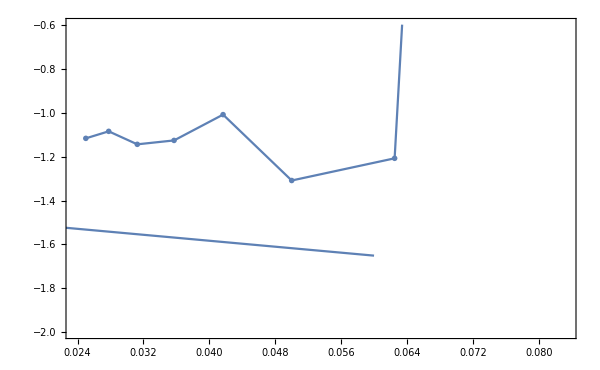

```mathematica
Show[{ListPlot[ {listQzz}, Joined->True ,Frame->True,ImageSize->600,PlotRange->{-2,-0.6},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{zz} "}, FrameStyle->Directive[Black,20],   PlotLabel->MaTeX["\\text{Finite size on the quadrupole tensor}",Magnification->1.8]   , PlotMarkers->"OpenMarkers"    ,PlotLegends-> Placed[{ MaTeX["Q_{zz}",Magnification->1.6]  } , Scaled[{0.9,.36}] ]                   ],
Plot[ {-1.447588456106501-3.387051851102911 x } , {x,0,0.06} ]  }]
```

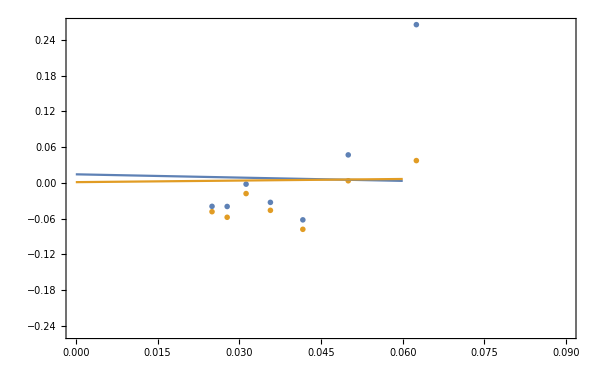

```mathematica
Show[{ListPlot[ {listQxxQyy,listQxy}, Joined->False ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{\\alpha\\beta} "}, FrameStyle->Directive[Black,20], PlotRange->{{0,0.09},Automatic},   PlotLabel->MaTeX["\\text{Finite size on the quadrupole tensor}",Magnification->1.8]   , PlotMarkers->"OpenMarkers"    ,PlotLegends-> Placed[{  MaTeX["Q_{xx}-Q_{yy}",Magnification->1.6], MaTeX["Q_{xy}",Magnification->1.6] } , Scaled[{0.9,.38}] ]                   ],
Plot[ { 0.014478824964698092-0.18329840100624634 x,0.0013334399615231014+0.0887432774778406 x} , {x,0,0.06} ]  }]
```

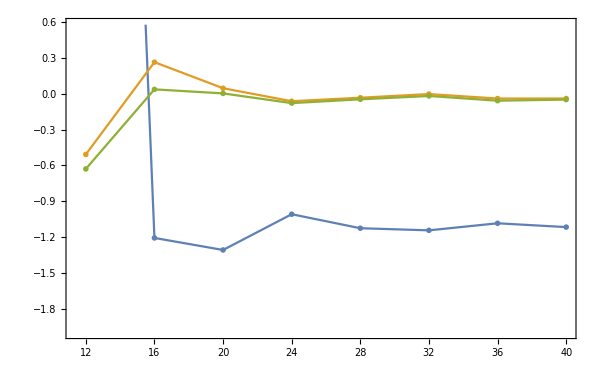

```mathematica
ListPlot[ { sizeQzz[chargeHex],sizeQxxQyy[chargeHex], sizeQxy[chargeHex]}, Joined->True ,Frame->True,ImageSize->600,PlotRange->{-2,0.58},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\text{System size } L \\; ", " Q_{\\alpha \\, \\beta } "}, FrameStyle->Directive[Black,20],   PlotLabel->MaTeX["\\text{Finite size on the quadrupole tensor}",Magnification->1.8]   , PlotMarkers->"OpenMarkers"    ,PlotLegends-> Placed[{ MaTeX["Q_{zz}",Magnification->1.4] , MaTeX["Q_{xx}-Q_{yy}",Magnification->1.4], MaTeX["Q_{xy}",Magnification->1.4] } , Scaled[{0.89,.386}] ]                   ]
```

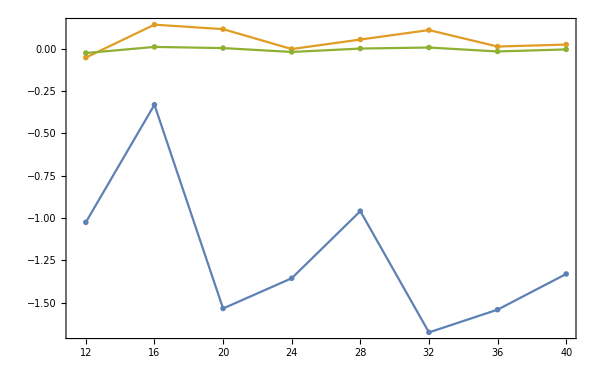

```mathematica
ListPlot[ { sizeQzz[chargeHex]}, Joined->True ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\text{System size } L \\; ", " Q_{zz} "}, FrameStyle->Directive[Black,20],   PlotLabel->MaTeX["\\text{Finite size on the quadrupole tensor}",Magnification->1.8]           ]
ListPlot[ { sizeQxxQyy[chargeHex]}, Joined->True ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\text{System size } L \\; ", "\\text{Anisotropy: } Q_{xx}-Q_{yy} "}, FrameStyle->Directive[Black,20],   PlotLabel->MaTeX["\\text{Finite size on the quadrupole tensor}",Magnification->1.8]           ]
ListPlot[ { sizeQxy[chargeHex]}, Joined->True ,Frame->True,ImageSize->600,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\text{System size } L \\; ", "\\text{Off-diagonal: } Q_{xy} "}, FrameStyle->Directive[Black,20],   PlotLabel->MaTeX["\\text{Finite size on the quadrupole tensor}",Magnification->1.8]           ]
```

```mathematica
sizeQzz[chargeDia]
```

{{12,-1.97608},{16,-2.07035},{20,-1.97238},{24,-1.69843},{28,-1.71578},{32,-1.71421},{36,-1.68246},{40,-1.69435}}

```mathematica
Column@N@(  Round[10000 chargeHex]/10000)
```

{12.,3.,-0.0359,{0.,-0.0004},{{0.5777,0.0016,0.},{0.0016,0.6571,0.},{0.,0.,-1.2348}}}
{16.,3.,-0.0562,{0.0001,-0.0003},{{0.6506,0.0023,0.},{0.0023,0.6434,0.},{0.,0.,-1.294}}}
{20.,3.,-0.0635,{0.0002,0.},{{0.6182,0.0015,0.},{0.0015,0.5738,0.},{0.,0.,-1.192}}}
{24.,6.,-0.0044,{0.0001,0.0001},{{0.7572,-0.0023,0.},{-0.0023,0.7922,0.},{0.,0.,-1.5494}}}
{28.,6.,-0.0047,{0.,-0.0001},{{0.8134,-0.0002,0.},{-0.0002,0.8265,0.},{0.,0.,-1.64}}}
{32.,6.,-0.0087,{0.0001,0.},{{0.7783,-0.0002,0.},{-0.0002,0.7122,0.},{0.,0.,-1.4905}}}
{36.,6.,-0.0059,{0.,-0.0001},{{0.7652,-0.0005,0.},{-0.0005,0.7747,0.},{0.,0.,-1.5399}}}
{40.,6.,-0.0064,{0.,-0.0001},{{0.7706,-0.0001,0.},{-0.0001,0.7914,0.},{0.,0.,-1.5621}}}

```mathematica
Column@N@(  Round[10000 chargeDia]/10000)
```

{12.,3.,0.0875,{0.0007,0.0003},{{1.263,0.0026,0.},{0.0026,0.7131,0.},{0.,0.,-1.9761}}}
{16.,3.,0.0744,{0.0005,0.},{{1.614,0.0022,0.},{0.0022,0.4564,0.},{0.,0.,-2.0703}}}
{20.,3.,0.0692,{0.0005,0.},{{1.5326,0.0025,0.},{0.0025,0.4398,0.},{0.,0.,-1.9724}}}
{24.,6.,0.0034,{0.0003,0.0004},{{0.6889,0.0024,0.},{0.0024,1.0095,0.},{0.,0.,-1.6984}}}
{28.,6.,0.0031,{0.0003,0.0002},{{0.9501,0.0026,0.},{0.0026,0.7656,0.},{0.,0.,-1.7158}}}
{32.,6.,0.0032,{0.0002,0.0003},{{0.834,0.0026,0.},{0.0026,0.8802,0.},{0.,0.,-1.7142}}}
{36.,6.,0.0025,{0.0003,0.0004},{{0.7883,0.0023,0.},{0.0023,0.8941,0.},{0.,0.,-1.6825}}}
{40.,6.,0.0024,{0.0003,0.0003},{{0.8609,0.0024,0.},{0.0024,0.8335,0.},{0.,0.,-1.6943}}}

```mathematica
Column@(charge3[[2;;-1]])
```

```mathematica
TeXForm@Column@N@(  Round[10000 chargeDia]/10000)
```

```mathematica
Column@charge2
```

```mathematica
(*Do[ Print[parameters[[i,j]]] ,{i,1,Length@parameters},{j,1,Length@parameters[[i]]} ];*)
```

### charge config c

#### charge den

```mathematica
(*patchχgauge4v[χ0,ω0,Ls[[l]]];*)
```

```mathematica
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp}, 		 
p=1;l=1;ev=1;
          tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[ev,p]],L,acuracy, gauge,NbName ]  ];  EnG0=EnG;
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];χ0=χ;ω0=ω;

	u0= gauge4v[ uniformU[-1,L] ,L];     
(*χ=χgaugetransf[χ,u0,L];*)
(*χ=χgauge4vChangeXtoZ[χ,L];*)
         t=ts[[tp]];     nameComplement=StringReplace["t=X1_ev=X4_h=X2-L=X3",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X3"-> ToString[parameters[[ev,p]][[10]]  ]  }];                      
                (*{χ,ω}=patchχgauge4v[χ,ω,L]; *)             (*  χ=symmχgauge4v[χ,L];   *)        

(*Do[  χ[[α,r]] = (-u0[[r,α]])χ0[[α,r]]        ,{α,1,3} , {r,1,L^2}];                            
{χ,ω,ξ}=1/2({χ,ω,ξ}+reflectX2[χ,ω,ξ,L] ) ;    
 Do[  χ[[α,r]] = (-u0[[r,α]])χ[[α,r]]        ,{α,1,3} , {r,1,L^2}];     χ1=χ;   *)
              
                                     
         c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
	sNN =sscNN[χ,u0, ω,L]; sNNN=  sscNNN[ ξ,ω,L];
	δn=densityTriang[L,c11,c21,c12,c22,sNN,0 sNNN];
         δn0=δn; ξ0=ξ; sNN0=sNN;sNNN0=sNNN;
δn1=  Module[ {max=Max[Abs@δn],δ0=Abs[4 (JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3)]},Print["max/δ0=",max/δ0];    δn/max    ];           ]
Print[ "Mean=",Mean@Mean@δn0,"; Max=",Max@Abs@δn0,"; Min=",Min@Abs@δn0]
```

max/δ0=1.08531

Mean=2.33265×10^-22; Max=0.0000250432; Min=1.22141×10^-9

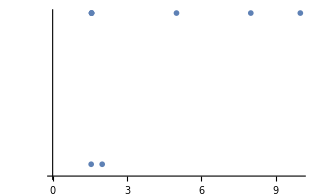
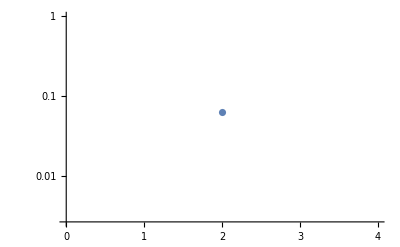
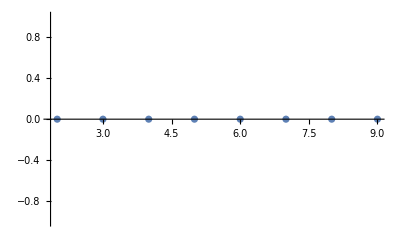

```mathematica
Row[{ListLogPlot@Abs@EnG0[[1]],ListLogPlot@EnG0[[4]],ListPlot@EnG0[[5]]}]
```

```mathematica
Row[{ListLogPlot@Abs@EnG0[[1]],ListLogPlot@EnG0[[4]],ListPlot@EnG0[[5]]}]
```

```mathematica
EnG0[[1,-5;;-1]]
```

{{-1.57095,-1.57095},{8,-1.57095},{-1.57095,-1.57095},{10,-1.57095},{-1.57095,-1.57095}}

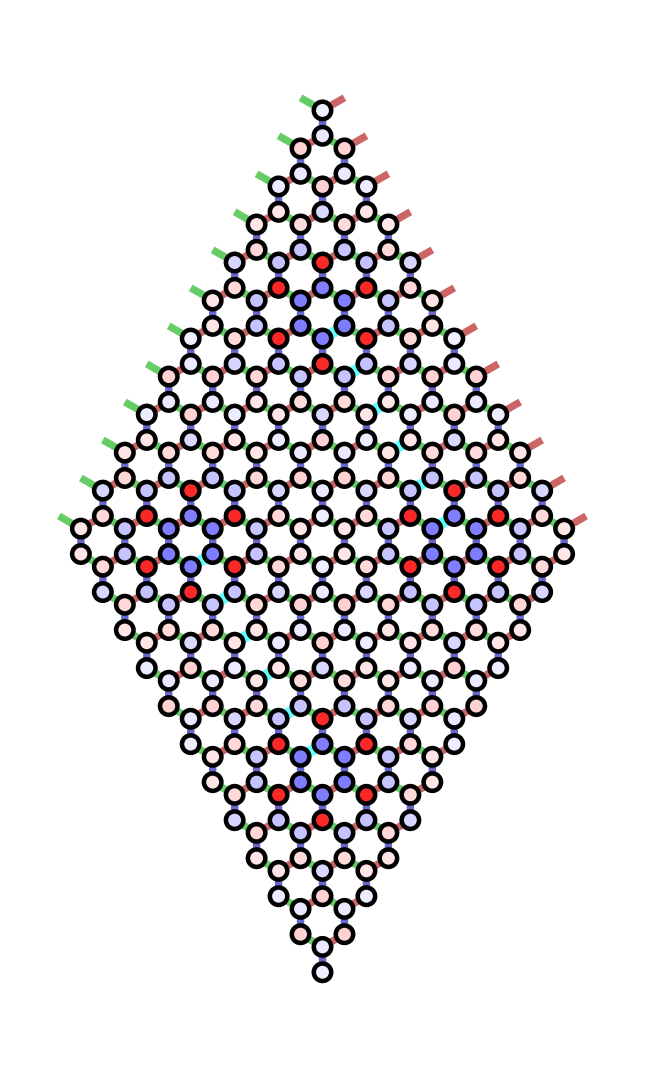

```mathematica
chargeConfig[δn1,χ0,Ls[[l]] ]
```

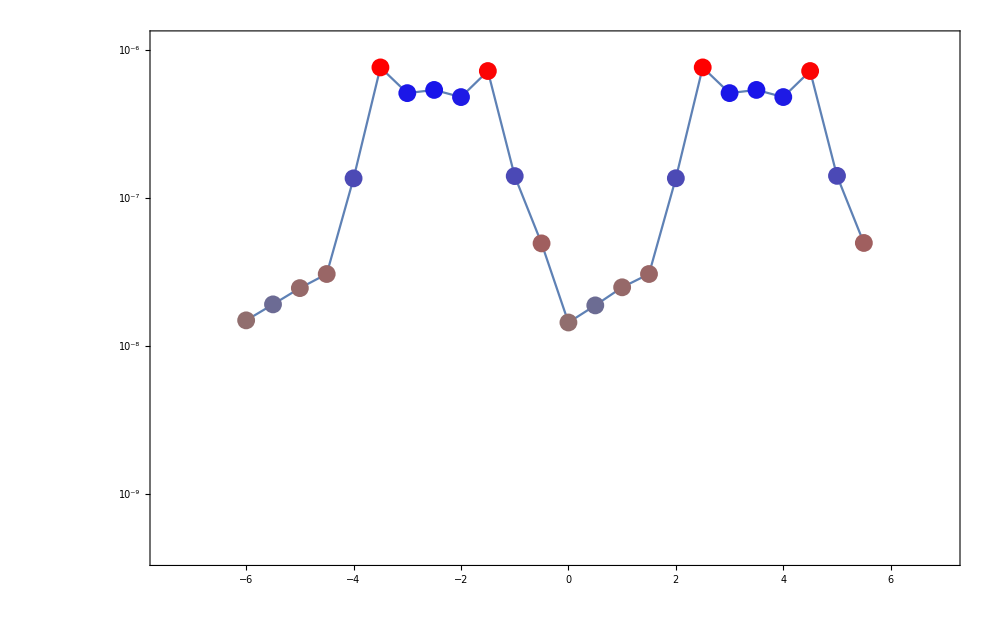

```mathematica
chargePlotZZstring[δn0,Ls[[l]],parameters⟦ev,p⟧]
```

```mathematica
chargePlotZZstring[δn_,L_,par_]:=Module[{points,title,m0,n0,J,K,Γ,JKΓmod,h,κ,d,max}, max=Max[Abs@δn]; (*Print[max];*)
{J , K,Γ,h}=par[[1;;4]];JKΓmod=par[[5;;7]] ;d=par[[8]]; If[  Norm[h]==0, κ=0,κ= N@(Round[10000(Norm[h]/√3)^3/(0.262)^2]/10000) ];
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}] ;

{m0,n0}=positionVortex[1,L];
points = Table[   Module[   {σ=Mod[i-1,2],m,n},
m=m0;n=n0+⌈(i-1)/2⌉; 
Style[   { Mod[⌈(i-1)/2⌉-σ/2 +L/4,L] -L/2, Abs@δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]    } , chargeCFgray[δn[[Mod[m,L]+Mod[n,L] L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\left(-\\frac{1}{2},\\frac{\\sqrt{3}}{2}\\right) \\cdot \\big( \\mathbf{R}_l-\\mathbf{R}_0 \\big) \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{-L/2-1.5,L/2+1},{0.0005max,1.5 max}} ,    PlotLabel->MaTeX[title,Magnification->2.2]                             ]                ];
```

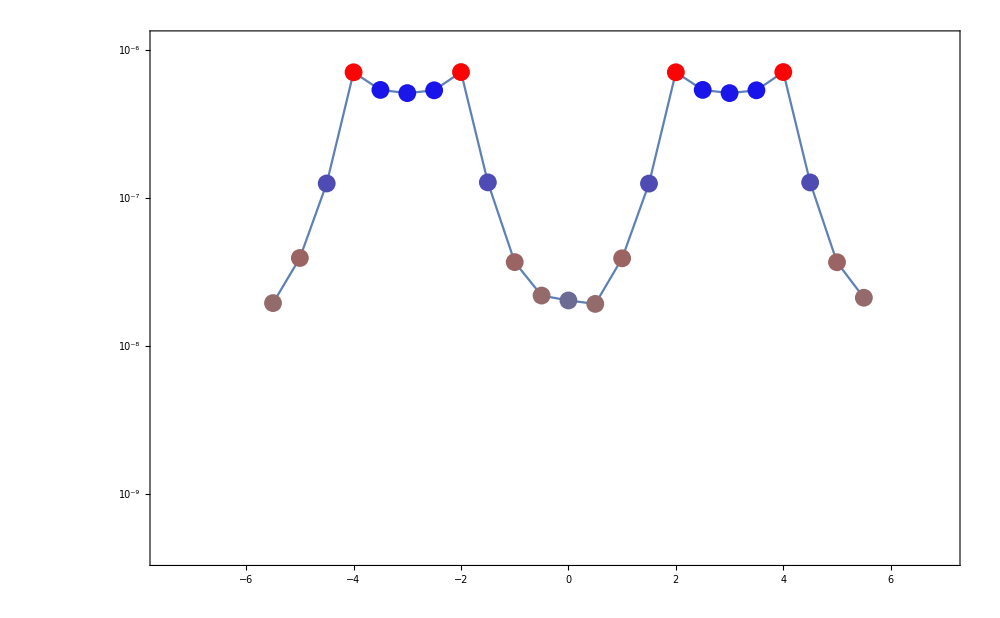

```mathematica
chargePlotZZ[δn0,Ls[[l]],parameters⟦ev,p⟧[[1;;4]],hV[[  Mod[p,Length@hV,1]  ]] ]
```

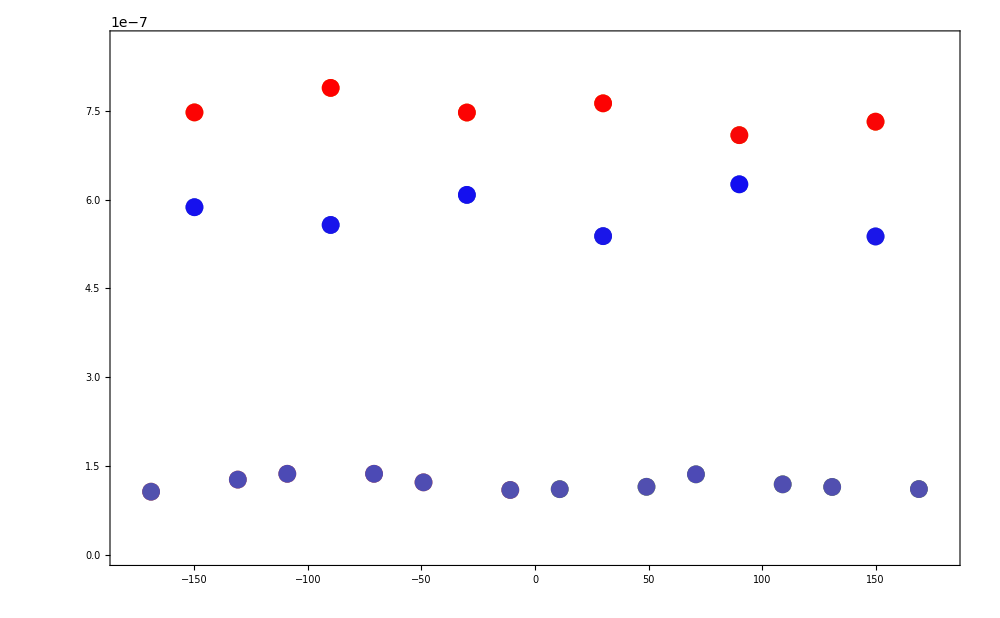

```mathematica
chargePlotCircle[δn0,Ls[[l]],parameters⟦p⟧,hV[[  Mod[p,Length@hV,1]  ]] ]
```

#### more --

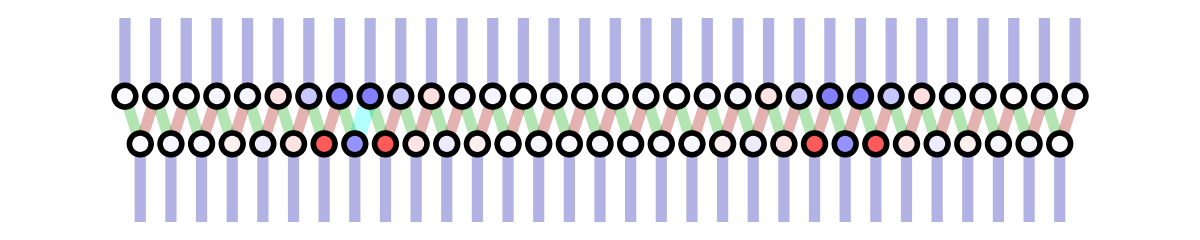

```mathematica
chargeConfigZZ[δn1,χ0,Ls[[1]] ]
```

```mathematica
(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\607\\CHARG_CONFIG_XX.pdf","XX"-> complement]  }], %]*)
```

```mathematica
(*Export[ FileNameJoin[{ NotebookDirectory[],  StringReplace["\\Figures\\607\\CHARG_ZZ_XX.pdf","XX"-> complement]   }], %]*)
```

```mathematica
(* Comparison with translation  *)
Module[{L=Ls[[1]],mS,nS,m1,n1,m2,n2,d0,r1,r2,χ=χ0,i}, d0=⌊1/2 ⌈L/2⌉⌋;{mS,nS}=positionVortex[1,L];
m1=mS;n1=nS+d0; n2=n1;m2=Mod[m1+2d0,L];
r1=m1+n1 L+1;r2=m2+n2 L+1;
Print[MatrixForm/@{-χ[[1]][[r1]],χ[[2]][[r1]],χ[[3]][[r1]]} ];
Print[MatrixForm/@{-χ[[1]][[r2]],χ[[2]][[r2]],χ[[3]][[r2]]} ];
Print[];

Print[MatrixForm/@{-χ[[1]][[r1]]+χ[[1]][[r2]],χ[[2]][[r1]]-χ[[2]][[r2]],χ[[3]][[r1]]-χ[[3]][[r2]]} ];
]
```

```mathematica
{χ2,ω2}=reflectXsign[χ0,ω0,Ls[[1]] ];
```

```mathematica
(* Comparison with reflection  *)
Module[{L=Ls[[1]],mS,nS,mE,nE,d0,r1,r2,χ=χ2,σ}, d0=⌊1/2 ⌈L/2⌉⌋;{mS,nS}=positionVortex[1,L];{mE,nE}=positionVortex[3,L];(* mS=mS+1;*)
r1=mS+(nS+d0)L+1;(*r2=mE+(nE+d0)L+1;*)r2=(nS+d0)+(mS)L+1; σ=2;
Print[MatrixForm/@{changeSign[χ0[[1]][[r1]],-1],χ[[2]][[r1]],χ[[3]][[r1]]} ];
Print[MatrixForm/@{reflectXinternal@χ0[[2]][[r2]],reflectXinternal@χ0[[1]][[r2]],χ0[[3]][[r2]]} ];
Print[];(*
Print[MatrixForm/@{ξ0[[σ,1]][[r1]],-ξ0[[σ,2]][[r1]],ξ0[[σ,3]][[r1]]} ];
Print[MatrixForm/@{ξ0[[σ,1]][[r2]],ξ0[[σ,2]][[r2]],ξ0[[σ,3]][[r2]]} ];
Print[];*)
Print[MatrixForm/@{changeSign[χ0[[1]][[r1]],-1],reflectXinternal@χ0[[2]][[r2]],-changeSign[χ0[[1]][[r1]],-1]+reflectXinternal@χ0[[2]][[r2]]} ];
Print[MatrixForm/@{-changeSign[χ0[[1]][[r1]],-1],reflectXinternal@χ0[[2]][[r2]],-changeSign[χ0[[1]][[r1]],-1]-reflectXinternal@χ0[[2]][[r2]]  } ];
Print[MatrixForm/@{-changeSign[χ0[[2]][[r1]],-1],reflectXinternal@χ0[[1]][[r2]],-changeSign[χ0[[2]][[r1]],-1]-reflectXinternal@χ0[[1]][[r2]]  } ];
Print[MatrixForm/@{-changeSign[χ0[[3]][[r1]],-1],reflectXinternal@χ0[[3]][[r2]],-changeSign[χ0[[3]][[r1]],-1]-reflectXinternal@χ0[[3]][[r2]]  } ];
Print[];
Print[MatrixForm/@{-χ0[[1]][[r1]],χ[[1]][[r1]],-χ0[[1]][[r1]]-χ[[1]][[r1]]} ];
Print[MatrixForm/@{χ0[[1]][[r1]],χ[[1]][[r1]],χ0[[1]][[r1]]-χ[[1]][[r1]]} ];
Print[MatrixForm/@{χ0[[2]][[r1]],χ[[2]][[r1]],χ0[[2]][[r1]]-χ[[2]][[r1]]} ];
Print[MatrixForm/@{χ0[[3]][[r1]],χ[[3]][[r1]],χ0[[3]][[r1]]-χ[[3]][[r1]]} ];
(*Print[MatrixForm/@{χ[[1]][[r1]],χ[[2]][[r2]],χ[[1]][[r1]]+reflectXinternal@χ[[2]][[r2]]} ];*)

]
```

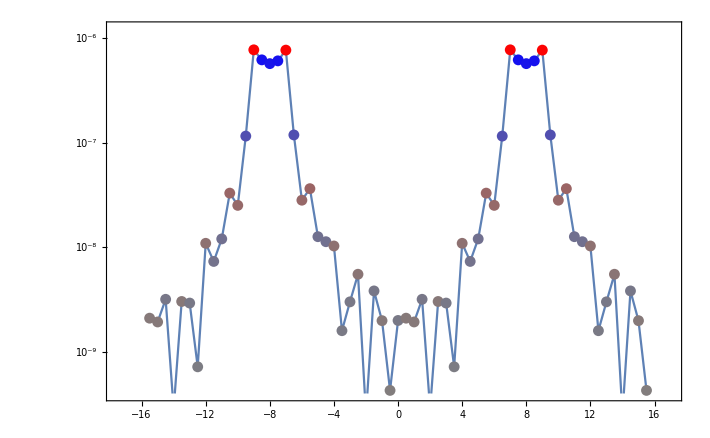
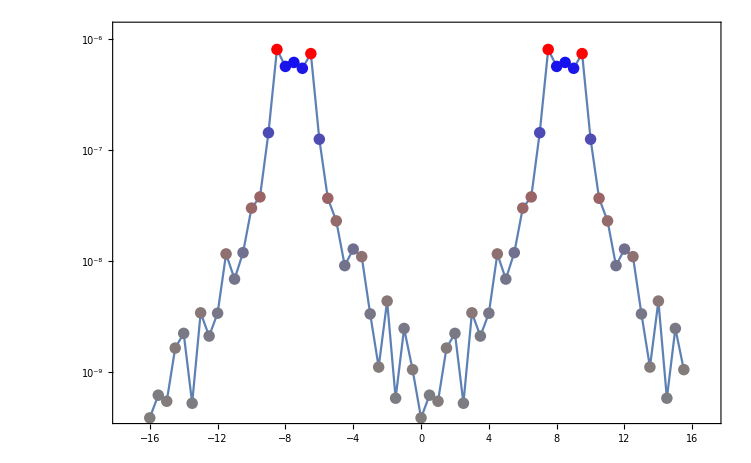

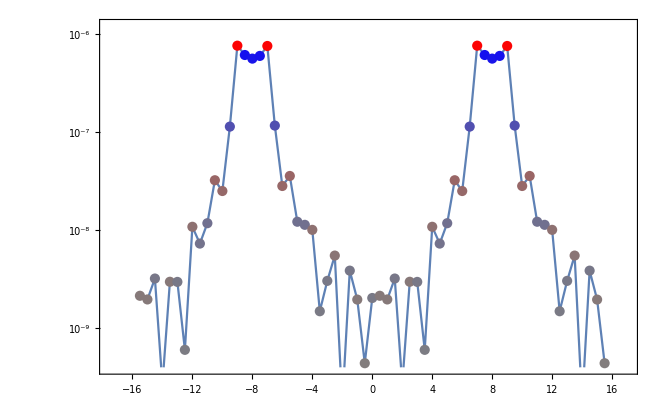

```mathematica
(*chargeLogPlotCircle[δn0,Ls[[l]],parameters⟦p⟧,hV[[  Mod[p,Length@hV,1]  ]] ]*)
```

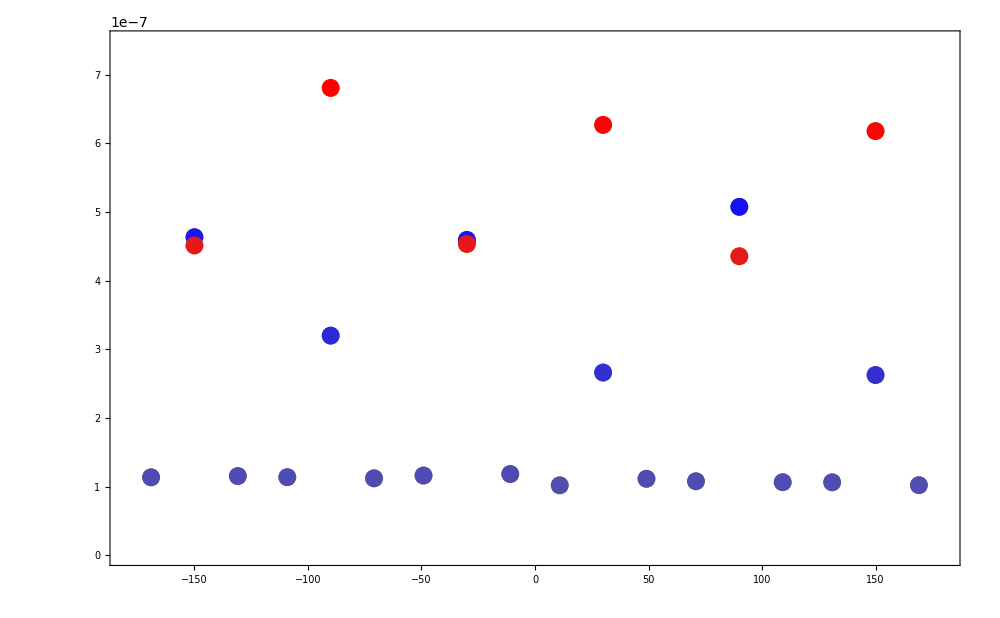

```mathematica
chargePlotCircle[δn0,Ls[[l]],parameters⟦p⟧,hV[[  Mod[p,Length@hV,1]  ]] ]
```

```mathematica
(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\607\\CHARG_PLOT_ZZ_XX.pdf","XX"-> complement]   }], %]*)
```

#### quadrupole

v = 1  South, v = 2 West, v = 3 East, v = 4 North

```mathematica
graphRings[δn1,Ls[[l]],2]
```

```mathematica
(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\607\\RINGS_GRAPH_XX.pdf","XX"-> complement]   }], %]*)
```

```mathematica
Module[{R,l,L,v}, l=1;L=Ls[[l]]; R=L/4-3 1/(√3);
Do[     q[v]=chargeVortex[δn0,L,v,R];d[v]=dipoleVortex[δn0,L,v,R];Q[v]=quadrupoleVortex[δn0,L,v,R];      ,{v,1,4}];
Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; q2=",q[2],"; d2= ",MatrixForm[d[2]],"; Q2= "MatrixForm[Q[2]] ];
Print[ "q3=",q[3],"; d3= ",MatrixForm[d[3]],"; Q3= "MatrixForm[Q[3]],"; q4=",q[4],"; d4= ",MatrixForm[d[4]],"; Q4= "MatrixForm[Q[4]] ];
]
```

q1=0.00638559; d1= (-0.0201646
-0.000270695); Q1=  (1.33092 | 0.0752234 | 0.
0.0752234 | 1.25476 | 0.
0. | 0. | -2.58568); q2=0.00638559; d2= (-0.0201646
-0.000270695); Q2=  (1.33092 | 0.0752234 | 0.
0.0752234 | 1.25476 | 0.
0. | 0. | -2.58568)

q3=0.00638559; d3= (-0.0201646
-0.000270695); Q3=  (1.33092 | 0.0752234 | 0.
0.0752234 | 1.25476 | 0.
0. | 0. | -2.58568); q4=0.00638559; d4= (-0.0201646
-0.000270695); Q4=  (1.33092 | 0.0752234 | 0.
0.0752234 | 1.25476 | 0.
0. | 0. | -2.58568)

#### quadrupole diamant

v = 1  South, v = 2 West, v = 3 East, v = 4 North

```mathematica
Row[Table[graphRingsDia[δn1,Ls[[l]],v],{v,1,4}]   ]
```

```mathematica
(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\607\\RINGS_GRAPH_XX.pdf","XX"-> complement]   }], %]*)
```

```mathematica
Module[{R=1,l,L,v}, l=1;L=Ls[[l]];
Do[     q[v]=chargeVortexDia[δn0,L,v,R];
d[v]=dipoleVortexDia[δn0,L,v,R];Q[v]=quadrupoleVortexDia[δn0,L,v,R];      ,{v,1,4}];

Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; q2=",q[2],"; d2= ",MatrixForm[d[2]],"; Q2= "MatrixForm[Q[2]] ];
Print[ "q3=",q[3],"; d3= ",MatrixForm[d[3]],"; Q3= "MatrixForm[Q[3]],"; q4=",q[4],"; d4= ",MatrixForm[d[4]],"; Q4= "MatrixForm[Q[4]] ];
]
```

```mathematica
Row[Table[graphRingsDia[δn1,Ls[[l]],v],{v,1,4}]   ]
```

```mathematica
Module[{R=Ls[[l]]/4-1,l,L,v}, l=1;L=Ls[[l]];
Do[     q[v]=chargeVortexDia[δn0,L,v,R];
d[v]=dipoleVortexDia[δn0,L,v,R];Q[v]=quadrupoleVortexDia[δn0,L,v,R];      ,{v,1,4}];

Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; q2=",q[2],"; d2= ",MatrixForm[d[2]],"; Q2= "MatrixForm[Q[2]] ];
Print[ "q3=",q[3],"; d3= ",MatrixForm[d[3]],"; Q3= "MatrixForm[Q[3]],"; q4=",q[4],"; d4= ",MatrixForm[d[4]],"; Q4= "MatrixForm[Q[4]] ];
]
```

#### quadrupole hexagon

v = 1  South, v = 2 West, v = 3 East, v = 4 North

```mathematica
chargeConfig[δn1,χ0,Ls[[l]] ]
```

```mathematica
Row[Table[graphRingsHex[δn1,Ls[[l]],v],{v,1,4}]   ]
```

```mathematica
Mean@Abs@δn0
```

```mathematica
Min@Abs@δn0
```

```mathematica
Module[{R=1,L,δn}, L=Ls[[l]]; R=L/4;δn=Chop[δn0,5 10^-10];
Do[     q[v]=chargeVortexHex[δn,L,v,R];
d[v]=dipoleVortexHex[δn,L,v,R];Q[v]=quadrupoleVortexHex[δn,L,v,R];      ,{v,1,4}];
Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],";"  ]
(*
Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; q2=",q[2],"; d2= ",MatrixForm[d[2]],"; Q2= "MatrixForm[Q[2]] ];
Print[ "q3=",q[3],"; d3= ",MatrixForm[d[3]],"; Q3= "MatrixForm[Q[3]],"; q4=",q[4],"; d4= ",MatrixForm[d[4]],"; Q4= "MatrixForm[Q[4]] ];*)
]
```

```mathematica
Row[Table[graphRingsDia[δn1,Ls[[l]],v],{v,1,4}]   ]
```

```mathematica
Module[{R=Ls[[l]]/4-1,l,L,v}, l=1;L=Ls[[l]];
Do[     q[v]=chargeVortexDia[δn0,L,v,R];
d[v]=dipoleVortexDia[δn0,L,v,R];Q[v]=quadrupoleVortexDia[δn0,L,v,R];      ,{v,1,4}];

Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; q2=",q[2],"; d2= ",MatrixForm[d[2]],"; Q2= "MatrixForm[Q[2]] ];
Print[ "q3=",q[3],"; d3= ",MatrixForm[d[3]],"; Q3= "MatrixForm[Q[3]],"; q4=",q[4],"; d4= ",MatrixForm[d[4]],"; Q4= "MatrixForm[Q[4]] ];
]
```

```mathematica
(*Row[Table[graphRingsHex3[δn1,Ls[[l]],v],{v,1,4}]   ]*)
```

```mathematica
Module[{R=1,L,δn,q,d,Q}, L=Ls[[l]]; R=L/4-2/(√3);δn=δn0;
Do[     q[v]=chargeVortexHex3[δn,L,v,R];
d[v]=dipoleVortexHex3[δn,L,v,R];Q[v]=quadrupoleVortexHex3[δn,L,v,R];      ,{v,{1}}];
Print[ "Hex3  :  q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; Eigenvalues= ",MatrixForm@Eigenvalues@Q[1]  ];
Do[     q[v]=chargeVortex[δn,L,v,R];
d[v]=dipoleVortex[δn,L,v,R];Q[v]=quadrupoleVortex[δn,L,v,R];      ,{v,{1}}];
Print[ "Circle  :  q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; Eigenvalues= ",MatrixForm@Eigenvalues@Q[1]  ];
Do[     q[v]=chargeVortexDia[δn,L,v,R];
d[v]=dipoleVortexDia[δn,L,v,R];Q[v]=quadrupoleVortexDia[δn,L,v,R];      ,{v,{1}}];
Print[ "Diamant  :  q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; Eigenvalues= ",MatrixForm@Eigenvalues@Q[1]  ];
Do[     q[v]=chargeVortexHex[δn,L,v,R];
d[v]=dipoleVortexHex[δn,L,v,R];Q[v]=quadrupoleVortexHex[δn,L,v,R];      ,{v,{1}}];
Print[ "Hex  :  q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; Eigenvalues= ",MatrixForm@Eigenvalues@Q[1]  ]
(*
Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]],"; q2=",q[2],"; d2= ",MatrixForm[d[2]],"; Q2= "MatrixForm[Q[2]] ];
Print[ "q3=",q[3],"; d3= ",MatrixForm[d[3]],"; Q3= "MatrixForm[Q[3]],"; q4=",q[4],"; d4= ",MatrixForm[d[4]],"; Q4= "MatrixForm[Q[4]] ];*)
]
```

Hex3  :  q1=-0.00476489; d1= (-0.0125056
-0.0258798); Q1=  (1.12416 | 0.0832477 | 0.
0.0832477 | 0.874706 | 0.
0. | 0. | -1.99887); Eigenvalues= (-1.99887
1.14939
0.849476)

Circle  :  q1=-0.0465921; d1= (-0.0253989
-0.0249014); Q1=  (0.598057 | 0.00871734 | 0.
0.00871734 | 0.90602 | 0.
0. | 0. | -1.50408); Eigenvalues= (-1.50408
0.906266
0.597811)

Diamant  :  q1=-0.0780745; d1= (-0.0107148
-0.00697749); Q1=  (-0.455366 | 0.114859 | 0.
0.114859 | 1.85861 | 0.
0. | 0. | -1.40324); Eigenvalues= (1.8643
-1.40324
-0.461054)

Hex  :  q1=-0.0571318; d1= (-0.0171297
-0.0154117); Q1=  (0.700145 | 0.0728295 | 0.
0.0728295 | 0.652861 | 0.
0. | 0. | -1.35301); Eigenvalues= (-1.35301
0.753074
0.599932)

#### quadrupole hexagon 3

v = 1  South, v = 2 West, v = 3 East, v = 4 North

```mathematica
chargeConfig[δn1,χ0,Ls[[l]] ]
```

### energy vs eV0

```mathematica
{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadData[toPath[parameters[[-1,1]],Ls[[1]],acuracy, "g4",NbName ]  ];
```

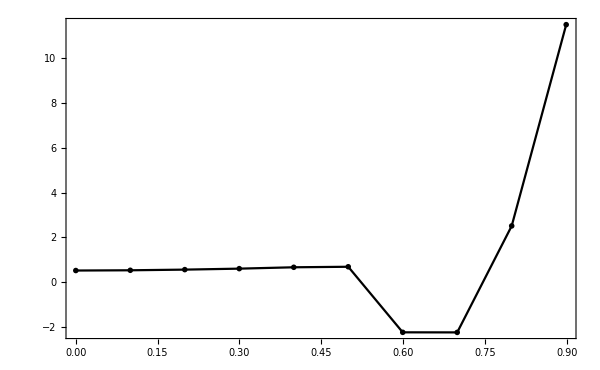

```mathematica
Module[{p,l},p=1;l=1;    enV0={};enV4={};enVΔ={};enMZM0={};enMZM={}; dispMZM0={};dispMZM={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g4", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadData[toPath[parameters[[ev,p]],L,acuracy, "g0",NbName ]  ];  
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[ev,p]],L,acuracy, "g4",NbName ]  ];  
	
 {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
Heff=HeffList[Jv,Kv,Γv,h,ω0];λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ0,ω0,L,L,λ1,λ2,Heff]; 
enH=Quiet@Eigenvalues[H];

AppendTo[dispMZM0,Thread@{eVs[[ev]]/(U-3JH),Sort@enH   }  ];
AppendTo[enMZM0,{eVs[[ev]]/(U-3JH),Sort[Abs@enH   ][[1;;11;;4]]   }  ];
Heff=HeffList[Jv,Kv,Γv,h,ω];λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 

enH=Quiet@Eigenvalues[H];

AppendTo[dispMZM,Thread@{eVs[[ev]]/(U-3JH),Sort@enH   }  ];
AppendTo[enMZM,{eVs[[ev]]/(U-3JH),Sort[Abs@enH   ][[1;;11;;4]]   }  ];
AppendTo[enV0,{eVs[[ev]],EnG0[[3,-1,2]]}  ];
AppendTo[enV4,{eVs[[ev]],EnG[[3,-1,2]]}  ];
AppendTo[enVΔ,{eVs[[ev]]/(U-3JH), L^2(EnG[[3,-1,2]]-EnG0[[3,-1,2]])}  ];
           
]; ,{ev,1, Length@eVs-1}]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);
size=0.012;
tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

plotInset= ListPlot[ enVΔ, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ];


(* ListPlot[ {enV0,enV4}  , Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*) FrameLabel->{MaTeX["e V_0 \\; (\\text{meV})",Magnification->2] , MaTeX["E \\, (V_0)",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,   PlotMarkers->"OpenMarkers",PlotRange->{{enV0[[1,1]]-.1(enV0[[-1,1]]-enV0[[1,1]]),enV0[[-1,1]]+.05(enV0[[-1,1]]-enV0[[1,1]])},Full},
PlotLabel-> Style[MaTeX[title,Magnification->1.82] ,20 ,Black ]  ,  PlotStyle->  {{ Darker@Blue,PointSize[size]},{ Darker@Red,PointSize[size]}} , Epilog->Inset[plotInset,Scaled[{0.012,.24}],Left,{600,Automatic} ] , PlotLegends-> Placed[{ MaTeX["E_{0\\textrm{v}}  \\, (V_0)",Magnification->1.2] , MaTeX["E_{4\\textrm{v}}  \\, (V_0)",Magnification->1.2] } , Scaled[{0.85,.86}] ]                    ]  *)

(* ListPlot[ {enV0,enV4}  , Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*) FrameLabel->{MaTeX["e V_0 \\; (\\text{meV})",Magnification->2] , MaTeX["E \\, (V_0)",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,   PlotMarkers->"OpenMarkers",PlotRange->{{enV0[[1,1]]-.1(enV0[[-1,1]]-enV0[[1,1]]),enV0[[-1,1]]+.05(enV0[[-1,1]]-enV0[[1,1]])},Full},
PlotLabel-> Style[MaTeX[title,Magnification->1.82] ,20 ,Black ]  ,  PlotStyle->  {{ Darker@Blue,PointSize[size]},{ Darker@Red,PointSize[size]}} , Epilog->Inset[plotInset,Scaled[{0.012,.24}],Left,{600,Automatic} ] , PlotLegends-> Placed[{ MaTeX["E_{0\\textrm{v}}  \\, (V_0)",Magnification->1.2] , MaTeX["E_{4\\textrm{v}}  \\, (V_0)",Magnification->1.2] } , Scaled[{0.85,.86}] ]                    ] *)

plotInset 
  
]  ]
```

```mathematica
N[0.001 Round/@(1000enMZM0  )  ]
```

{{0.,{0.235,0.235,0.235}},{0.1,{0.233,0.233,0.237}},{0.2,{0.227,0.227,0.244}},{0.3,{0.217,0.217,0.255}},{0.4,{0.202,0.202,0.271}},{0.499,{0.184,0.184,0.289}},{0.599,{0.164,0.164,0.277}},{0.699,{0.,0.,0.}},{0.799,{0.,0.,0.}},{0.899,{0.,0.,0.}}}

{{0.,{0.018,0.254,0.266}},{0.1,{0.018,0.257,0.267}},{0.2,{0.019,0.263,0.271}},{0.3,{0.019,0.273,0.276}},{0.4,{0.02,0.279,0.284}},{0.499,{0.021,0.28,0.293}},{0.599,{0.022,0.271,0.271}},{0.699,{0.,0.,0.}},{0.799,{0.,0.,0.}},{0.899,{0.,0.,0.}}}

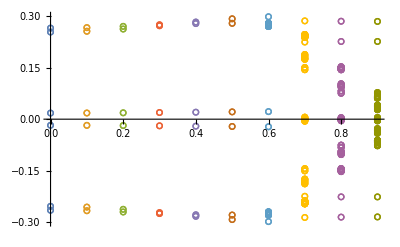

```mathematica
N[0.001 Round/@(1000enMZM  )  ]
```

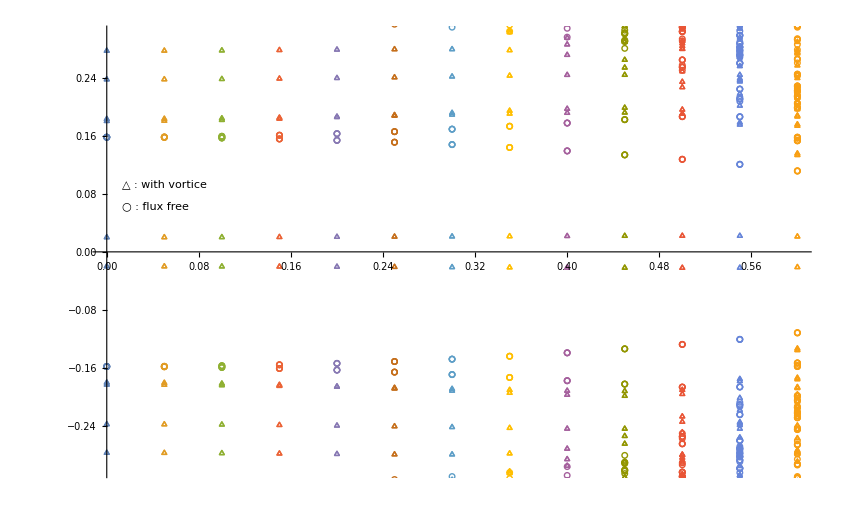

```mathematica
Show[ ListPlot[  dispMZM  , PlotRange->{-0.3,0.3}, PlotMarkers->{"△",Scaled[0.02]} ,  Epilog->{Inset["○ : flux free"  ,Scaled[{0.04,.6}],Left,{0.15,Automatic}  ]   , Inset["△ : with vortice"  ,Scaled[{0.04,.65}],Left,{0.15,Automatic}  ]}          ],
ListPlot[  dispMZM0  , PlotRange->{-0.3,0.3}, PlotMarkers->{"○",Scaled[0.02]}          ]
 ]
```

### finite size charge density

```mathematica
sizeQzz[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[3,3]]  },{i,1,Length@charge}   ];sizeQxxQyy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,1]] -charge[[i,-1]][[2,2]]  },{i,1,Length@charge}   ];sizeQxy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,2]] +charge[[i,-1]][[2,1]]  },{i,1,Length@charge}   ];

anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ]   *)
sizeAni[charge_]:=Table[ {charge[[i,1]],anisotropy@charge[[i,-1]]  },{i,1,Length@charge}   ];
```

```mathematica
pmax=Length@parameters[[1]];Δp=1;     chargeHex=Table[{},pmax];
Module[ {J,K,Γ}, {J,K,Γ}=parameters⟦1,1⟧[[1;;3]];Print["J=",J,"; K=",K,"; Γ=",Γ,"; "];]
Do[ 
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];

	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@(Round[10000toKappa[h]   ]/10000) ];
	u0= gauge4v[ uniformU[-1,L] ,L];     
	t=ts[[tp]];     
nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];               
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		(*δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN];*)
δn=densityTriangVortexHex[L,c11,c21,c12,c22,sNN,sNNN,1,5];
(*δn0=δn; ξ0=ξ; sNN0=sNN;sNNN0=sNNN;χ0=χ;*)
(* graphics*)
title=StringReplace["J=X1,\\; \\Gamma=X3 \\;h=(Y1,Y2,Y3)",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]]}];
(*
Print[nameComplement];
(* graphics*)
title=StringReplace["J=X1,\\;K=X2,\\;\\Gamma=X3,\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@Round[1000J]/1000],"X2"->ToString@N@Round[1000K]/1000,"X3"-> ToString@N@Round[1000Γ]/1000,"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_CONFIG_FLUX\\CHARG_CONFIG_FLUX_XX.pdf","XX"-> nameComplement]  }],chargeConfigFlux[δn,χ,ω,L,title]       ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_CONFIG_FLUX_ZOOM\\CHARG_CONFIG_FLUX_ZOOM_XX.pdf","XX"-> nameComplement]  }],chargeConfigFluxZoom[δn,χ,ω,L,title]       ];Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_PLOT\\CHARG_PLOT_ZZ_XX.pdf","XX"-> nameComplement]   }],chargePlotZZ[δn,L,parameters[[1,p]],hV[[hp]]] ];

*)
Module[{R,q,dip,Q,v}, L=Ls[[l]]; R=Min[ 5 ];
Print["L=",L,"; R=",R,"; t=",t,"; ", nameComplement];
Do[     q[v]=chargeVortexHex[δn,L,v,R];dip[v]=dipoleVortexHex[δn,L,v,R];Q[v]=quadrupoleVortexHex[δn,L,v,R];      ,{v,{1} }];
AppendTo[chargeHex[[p]],  {L,R,q[1],dip[1],Q[1]}   ];
Print[ "q1=",q[1],"; d1= ",MatrixForm[dip[1]],"; Q1= "MatrixForm[Q[1]]    ];   
] ;
],{p,1, pmax,Δp  },{l,1,Length@Ls,1}]
```

```mathematica
(*TeXForm@Column@N@(  Round[10000 chargeHex[[;;,-3]] ]/10000)
anisotropy[Q_]:=Module[{q1,q2},{q1,q2}=Eigenvalues@Q[[1;;2,1;;2]] ;q1-q2]
Column@N@(  Round[10000 chargeHex[[1]]    ]/10000)*)
```

```mathematica
Column@N@(  Round[10000 chargeHex[[3]]    ]/10000)
```

```mathematica
(* StandardDeviation@listQzz[[-7;;-1,2]] / Mean@listQzz[[-7;;-1,2]] *)
```

```mathematica
fitNum=-15;
Module[{epilog={},title,plots,fit=Array[Null,{3,pmax}] ,chargeList,listQ ,fitName,name,ceilpmax ,Np,ΔL=1},
Do[ Module[{ λ,  J,K,Γ, h , t, d,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]]; 
	d=parameters[[1,p]][[8]];
	t=ts[[tp]]; 
title=StringReplace["\\text{Finite size analize: Quadrupole } J=X1,\\, \\Gamma=X3",
{"X1"->ToString@N@( Round[1000 #]/1000)&@J,"X2"->ToString@N@( Round[1000 #]/1000)&@K,"X3"->ToString@N@( Round[1000 #]/1000)&@Γ   }      ];
        AppendTo[epilog,
StringReplace["h=(Y1,Y2,Y3)",
{"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]]}]       ]
(*nameComplement=StringReplace["t=X1_h=X2-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]], "X4"-> ToString[acuracy]  }];      *)

],{p,1,pmax,Δp }];
Np=⌊(pmax-1)/Δp⌋+1;
ceilpmax=(1+(Np-1) Δp);
chargeList= chargeHex;
listQ={       
Table[ Module[{list=sizeQzz[chargeList[[p]] ] },       Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list,ΔL}] ],{p,1,pmax,Δp}],
Table[Module[{list=sizeQxxQyy[chargeList[[p]] ] },  Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list,ΔL}] ],{p,1,pmax,Δp}],
Table[ Module[{list=sizeQxy[chargeList[[p]] ] },        Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list,ΔL}] ],{p,1,pmax,Δp}],
Table[ Module[{list=sizeAni[chargeList[[p]] ] },        Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list,ΔL}] ],{p,1,pmax,Δp}]             };
Print[ToString[    Np==Length@listQ[[1]]     ] ];
listQ2=listQ;
 fit =Table[ Fit[listQ[[α]][[p]][[fitNum;;-1]],{1,x},x],{α,1,4},{p,1,Np}];
fitt=fit;
fitName=Table[ 
StringReplace[ ToString@TeXForm@StandardForm[ ScientificForm[fit[[α]][[p]],4]  ] ,  {"\\left("->"","\\right)"->"","x"->" \\, L^{-1}"}  ]
,{α,1,4},{p,1,Np}  ];
fittName=fitName;
(*Abort[];*)
plots={
Show[{ListPlot[ listQ[[1]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},Automatic},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{zz} "}, FrameStyle->Directive[Black,20],PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->"OpenMarkers"    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ] 
(*,Epilog->Placed[MaTeX[epilog,Magnification->1.3], {Scaled[{0.01,.9}],{0,0} }]  *)                 ],
Plot[Evaluate@fit[[1]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@fitName[[1]] , {Scaled[{0.02,.05}],{0,0} } ]  ]     } 
],
(*Evaluate it needed to plot "fit" since Mathematica treats fit[[α]] as a Table and usually first evaluate the Plot and then the Table. This is a trick to properlly display the colors we. *)
Show[{ListPlot[ listQ[[2]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},Full },FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{xx}-Q_{yy} "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ]            ],
Plot[ Evaluate@fit[[2]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[2]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
],
Show[{ListPlot[ listQ[[3]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},MinMax[ listQ[[3]][[;;,;;,2]],Scaled[1] ]       },FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " 2 Q_{xy} "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ]               ],
Plot[ Evaluate@fit[[3]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[3]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
],
Show[{ListPlot[ listQ[[4]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04}, Full},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", "\\text{Anisotropy } \\vert Q_{xx}^{\\prime}-Q_{yy}^{\\prime}\\vert "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.82}],{0,0} } ]               ],
Plot[ Evaluate@fit[[4]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[4]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
]};
Print[plots];
name=StringReplace["h=X1-X2_L=X3-X4",{"X1"->  ToString[hV[[1]]], "X2"->  ToString[hV[[ceilpmax]]], "X3"-> ToString[Ls[[1]] ], "X4"-> ToString[Ls[[-1]] ]  }]; ;
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qzz_FINITE_SIZE_XX_pure.pdf","XX"->name]  }],      plots[[1]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\QxxQyy_FINITE_SIZE_XX_pure.pdf","XX"->name]  }],plots[[2]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qxy_FINITE_SIZE_XX_pure.pdf","XX"-> name]  }],      plots[[3]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qani_FINITE_SIZE_XX_pure.pdf","XX"-> name]  }],    plots[[4]]      ];
 ]
```

## translation invariant. Energy and correlation.

#### Energy

```mathematica
L=51;Nc=L^2;e0=1/(2Nc)Sum[ Module[{k}, k=toMomentum[l,Nc]; Total@Sort[Eigenvalues[ HMFk[0,-1,0,0 hc,{χGx,χGy,χGz},{ωGA,ωGB},k]] ][[1;;4]]], {l,1,Nc}]
```

-1.57459

```mathematica
e0 =-3 0.5248657458506312014761390306
```

-1.57459723755189360442841709

the expected energy is  -1.5747;  the dependence in the length size is

```mathematica
Lmin=10;Lmax=60;EvsL={};
Do[Module[{Nc=L^2,E}, 
E=1/(2Nc)Sum[ Module[{k}, k=toMomentum[l,Nc]; Total@Sort[Eigenvalues[ HMFk[0,-1,0,0 hc,{χGx,χGy,χGz},{ωGA,ωGB},k]] ][[1;;4]]], {l,1,Nc}];
WriteString["stdout",StringForm["L= ``; ",L]]; 
AppendTo[EvsL,{1/L,E}]; 
] , {L,Lmin,Lmax,1}      ]
```

L= 10; L= 11; L= 12; L= 13; L= 14; L= 15; L= 16; L= 17; L= 18; L= 19; L= 20; L= 21; L= 22; L= 23; L= 24; L= 25; L= 26; L= 27; L= 28; L= 29; L= 30; L= 31; L= 32; L= 33; L= 34; L= 35; L= 36; L= 37; L= 38; L= 39; L= 40; L= 41; L= 42; L= 43; L= 44; L= 45; L= 46; L= 47; L= 48; L= 49; L= 50; L= 51; L= 52; L= 53; L= 54; L= 55; L= 56; L= 57; L= 58; L= 59; L= 60;

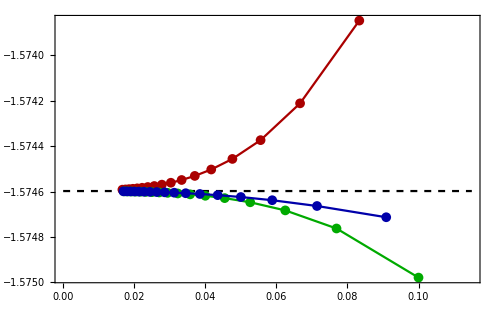

```mathematica
gE1 =ListPlot[EvsL[[3;;-1;;3]],Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"L\\equiv 0 \\text{ (mod 3) }"},{.2,.25}],PlotRange->All];
gE2 =ListPlot[EvsL[[1;;-1;;3]],Joined->True,PlotStyle->{Darker[Green]},PlotMarkers->{"●",Small},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"L\\equiv 1 \\text{ (mod 3) }"},{.2,.25-.075}],PlotRange->All];
gE3 =ListPlot[EvsL[[2;;-1;;3]],Joined->True,PlotStyle->{Darker[Blue]},PlotMarkers->{"●",Small},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"L\\equiv 2 \\text{ (mod 3) }"},{.2,.1}],PlotRange->All];
gref=Plot[e0,{x,0,1/(Lmin)1.15},FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"1/L","\\text{Ground state energy}"},PlotStyle->{Black,Dashed},Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All];
Show[gref,gE1,gE2,gE3,PlotRange->{{0.0,1/Lmin},{e0*.99965,e0  1.00035}}]
```

```mathematica
(*Export[ FileNameJoin[{ NotebookDirectory[], "Figures\\Kitaev\\GS_en_L_h0.pdf"}], %]*)
```

```mathematica
Lmin=10;Lmax=60;EminvsL={};
Do[Module[{Nc=L^2,Emin}, 
Emin=Min@Table[ Module[{k}, k=toMomentum[l,Nc]; Abs[Eigenvalues[ HMFk[0,-1,0,0 hc,{χGx,χGy,χGz},{ωGA,ωGB},k],-1] ] ], {l,1,Nc}];
WriteString["stdout",StringForm["L= ``; ",L]]; 
AppendTo[EminvsL,{1/L,Emin}]; 
] , {L,Lmin,Lmax,1}      ]
```

L= 10; L= 11; L= 12; L= 13; L= 14; L= 15; L= 16; L= 17; L= 18; L= 19; L= 20; L= 21; L= 22; L= 23; L= 24; L= 25; L= 26; L= 27; L= 28; L= 29; L= 30; L= 31; L= 32; L= 33; L= 34; L= 35; L= 36; L= 37; L= 38; L= 39; L= 40; L= 41; L= 42; L= 43; L= 44; L= 45; L= 46; L= 47; L= 48; L= 49; L= 50; L= 51; L= 52; L= 53; L= 54; L= 55; L= 56; L= 57; L= 58; L= 59; L= 60;

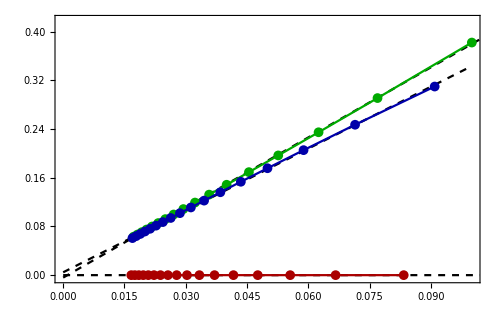

```mathematica
gEm1 =ListPlot[EminvsL[[3;;-1;;3]],Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"L\\equiv 0 \\text{ (mod 3) }"},{.2,.85}],PlotRange->All];
gEm2 =ListPlot[EminvsL[[1;;-1;;3]],Joined->True,PlotStyle->{Darker[Green]},PlotMarkers->{"●",Small},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"L\\equiv 1 \\text{ (mod 3) }"},{.2,.85-.075}],PlotRange->All];
gEm3 =ListPlot[EminvsL[[2;;-1;;3]],Joined->True,PlotStyle->{Darker[Blue]},PlotMarkers->{"●",Small},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"L\\equiv 2 \\text{ (mod 3) }"},{.2,.7}],PlotRange->All];
tf0=a + x b/.FindFit[EminvsL[[3;;-1;;3]],a + x b,{a,b},x];ts0=StringReplace[ToString[SetPrecision[ Chop[ tf0,10^-5], 2 ]], "x"->"\\, L^{-1} "];
tf1=a + x b/.FindFit[EminvsL[[1;;-1;;3]],a + x b,{a,b},x];ts1=StringReplace[ToString[SetPrecision[ Chop[ tf1,10^-6], 2 ]], "x"->"\\, L^{-1} "];
tf2=a + x b/.FindFit[EminvsL[[2;;-1;;3]],a + x b,{a,b},x];ts2=StringReplace[ToString[SetPrecision[ Chop[ tf2,10^-6], 2 ]], "x"->"\\, L^{-1} "];
tendency0=Plot[tf0,{x,0,EminvsL[[3;;-1;;3]][[1,1]] 1.1},PlotStyle->{Black,Dashed},PlotLegends->Placed[(MaTeX[#,Magnification-> .9]&)@ts0,{.45,0.85}]];
tendency1=Plot[tf1,{x,0,EminvsL[[1;;-1;;3]][[1,1]] 1.1},PlotStyle->{Black,Dashed},PlotLegends->Placed[(MaTeX[#,Magnification->.9]&)@ts1,{.45,0.85-.075}]];
tendency2=Plot[tf2,{x,0,EminvsL[[2;;-1;;3]][[1,1]] 1.1},PlotStyle->{Black,Dashed},PlotLegends->Placed[(MaTeX[#,Magnification->.9]&)@ts2,{.45,0.7}]];
gref=Plot[0,{x,0,1/(Lmin)1.15},FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"1/L","\\text{Lowest energetic mode}"},PlotStyle->{Black,Dashed},Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All];
Show[gref,tendency1,tendency2,gEm1,gEm2,gEm3,PlotRange->{{0.0,1/Lmin},All}]
```

```mathematica
Export[ FileNameJoin[{ NotebookDirectory[], "Figures\\Kitaev\\GS_gap_L_h0.pdf"}], %]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD project\Mean-field periodic SO(4)\Figures\Kitaev\GS_gap_L_h0.pdf

#### Correlations (MF parameters)

```mathematica
MatrixForm/@Chop@MFparK[0,-1,0,0 hc,{χGx,χGy,χGz},{ωGA,ωGB},10]
```

{(0.52512 | 0 | 0 | 0
0 | -1. | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0.52512 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -1. | 0
0 | 0 | 0 | 0),(0.52512 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1.),(0.+1. ⅈ | 0 | 0 | 0
0 | 0.+1. ⅈ | 0 | 0
0 | 0 | 0.+1. ⅈ | 0
0 | 0 | 0 | 0.+1. ⅈ),(0.+1. ⅈ | 0 | 0 | 0
0 | 0.+1. ⅈ | 0 | 0
0 | 0 | 0.+1. ⅈ | 0
0 | 0 | 0 | 0.+1. ⅈ)}

```mathematica
Lmin=15;Lmax=30;pmfList=Table[{},5];
Do[Module[{Nc=L^2,E,pmf=Array[Null,5]}, 
pmf=MFparK[0,-1,0,0 hc,{χGx,χGy,χGz},{ωGA,ωGB},L];
WriteString["stdout",StringForm["L= ``; ",L]]; 
Do[AppendTo[pmfList[[i]],{L,Re@pmf[[i]][[1,1]]}], {i,1,5}]; 
] , {L,Lmin,Lmax,1}      ]
```

L= 15; L= 16; L= 17; L= 18; L= 19; L= 20; L= 21; L= 22; L= 23; L= 24; L= 25; L= 26; L= 27; L= 28; L= 29; L= 30;

```mathematica
pmfList[[4]]
```

{{15,0.},{16,0.},{17,0.},{18,0.},{19,0.},{20,0.},{21,0.},{22,0.},{23,0.},{24,0.},{25,0.},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.}}

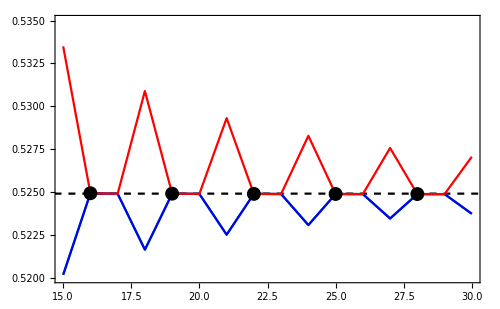

```mathematica
gCz=ListPlot[pmfList[[1]],Joined->True,PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLegends->Placed[(MaTeX[#,Magnification->1.5]&)/@{"\\chi_z^{00}"},{.8,.7}],PlotRange->All];
gCx=ListPlot[pmfList[[2]],Joined->True,PlotStyle->{Blue},Frame->True,FrameStyle->Directive[Black,16],PlotLegends->Placed[(MaTeX[#,Magnification->1.5]&)/@{"\\chi_x^{00}"},{.8,.9}],PlotRange->All];
gCy=ListPlot[pmfList[[3]],Joined->True,PlotStyle->{Red},Frame->True,FrameStyle->Directive[Black,16],PlotLegends->Placed[(MaTeX[#,Magnification->1.5]&)/@{"\\chi_y^{00}"},{.8,.8}],PlotRange->All];
gdots=ListPlot[pmfList[[3]][[2;;-1;;3]],Joined->False,PlotStyle->{Black,PointSize[.02]},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotRange->All];
gref=Plot[0.5249,{L,1,Lmax+0.3},PlotStyle->{Black,Dashed},Frame->True,FrameStyle->Directive[Black,16],FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"L","\\text{Parameter } \\, \\chi_{\\alpha}^{00}"},ImageSize->500,PlotRange->All];
Show[gref,gCz,gCx,gCy,gdots,PlotRange->{{Lmin,Lmax},{.52,.535}}]
```

```mathematica
Export[ FileNameJoin[{ NotebookDirectory[], "Figures\\Kitaev\\chi_00_h0.pdf"}], %]
```

#### Dispersion

```mathematica
Energiesline[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {M = L,line = toLineInMomentumSpace[L^2]},    Table[  N@ {   line⟦n⟧, Chop@Sort[Eigenvalues[ N@HMFk[ J,K, Γ, h,χ,ω,η, line⟦n⟧], 8 ]]    }     , {n,1,M}] ];
```

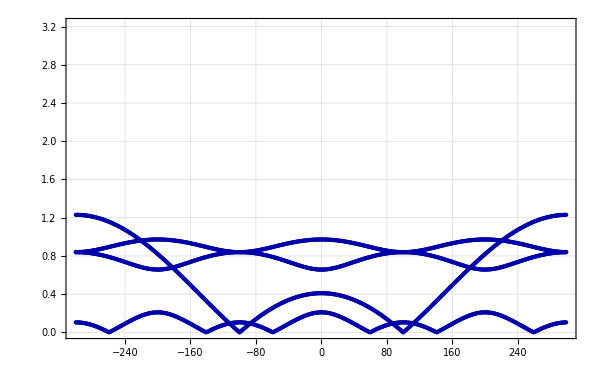

```mathematica
p=7;
Module[{L,Nc,J,K, Γ, h,χ,ω,η=0,l}, l=1;
L=Ls[[l]];{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
En = EnergiesSortedW[600^2,J,K,Γ,h,χ,ω,η];   Disp = lineDispersionSortedW[En];disp = Disp    ];

size=0.005;Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0}, {J,K,Γ,h}=parameters[[1,p]][[1;;4]];
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;
 ListPlot[ disp  , Joined->False ,  PlotRange-> {0,2*1.61} , FrameLabel->{MaTeX["\\mathbf{k}",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{ } , Automatic}   ,  PlotStyle->  {{ Darker@Blue,PointSize[size]}}    ]   ]
```

#### Wilson loop vs h

```mathematica
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,10]],Ls[[1]],acuracy,"free",NbName ]  ];
```

```mathematica
EnG[[6]]
```

{1.74552×10^-9,0.981984}

```mathematica
Wp1H={};Wp2H={};WpH={};
Do[Module[{L,Nc,J,K, Γ, h,jG,LG,χ,ω,en,ξG,EnG,η=0,l}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free_lambda",NbName ]  ];

AppendTo[Wp1H,{Norm@h,EnG[[6,1]]      }];  
AppendTo[Wp2H,{Norm@h,EnG[[6,2]]     }];
AppendTo[WpH,{Norm@h,Total@EnG[[6]]     }];
];   ,
{p,1,Length@parameters[[1]]}];
```

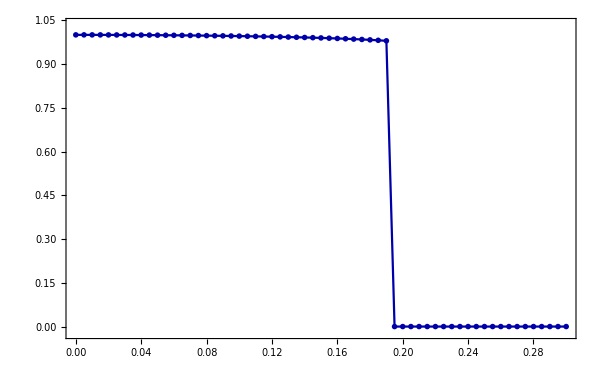

```mathematica
size=0.005;
 ListPlot[ Wp2H  , Joined->True ,  PlotRange-> {-0.02,1.035} , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["\\left<\\, W_p \\right>",Magnification->2] } , 
Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,(* GridLines->None,*)  
PlotLabel-> Style[MaTeX["\\text{Wilson Loop}",Magnification->1.6] ,20 ,Black ]  ,  PlotStyle->  {{ Darker@Blue,PointSize[size]}}     ]
```

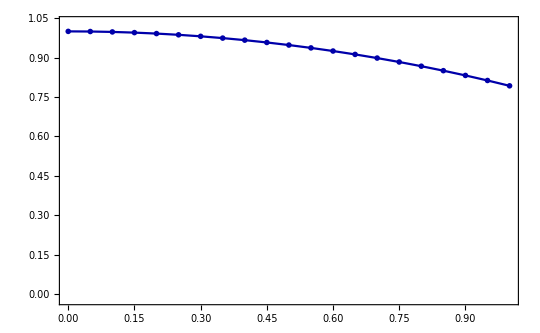
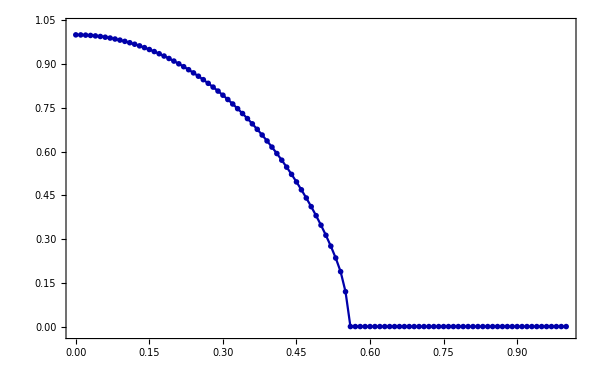

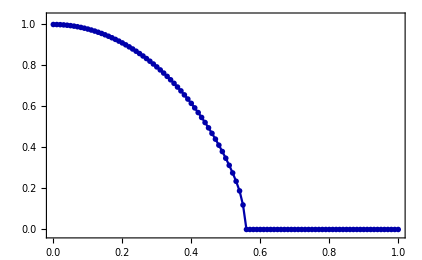

#### Gap vs h

```mathematica
gapH={};gapKH={};gapΓH={};
Do[Module[{L,Nc,J,K, Γ, h,jG,LG,λ,Jm,χ,ω,en,enΓ,enK,ξG,EnG,l}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free_fit",NbName ]  ];

Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
λ=parameters[[1,p]][[10]]{ h,h};

enK= Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jm,h,λ, χ,ω,N@kD1], 8 ]    ][[1]];
enΓ= Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jm,h,λ, χ,ω,{0,0}], 8 ]    ][[1]];
en=Min[enK,enΓ];

AppendTo[gapKH,{Norm@h,enK}];
AppendTo[gapΓH,{Norm@h,enΓ}] ; 
AppendTo[gapH,{Norm@h,en}]    ],
{p,1,Length@parameters[[1]]}];
```

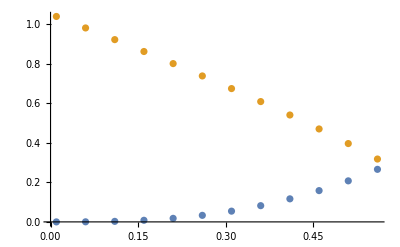

```mathematica
ListPlot[ {gapKH,gapΓH}]
```

```mathematica
FindFit[ gapH[[1;;6]], 3 √3 a/(0.262)^2 (x/(√3))^3, {a},x]
```

{a→1.05237}

```mathematica
(*FindFit[ gapH[[1;;15]], 2 √3 a/(0.262)^2 (x/(2 √3))^3, {a},x]
FindFit[ gapH[[1;;10]], 2 √3 1/(Δ)^2 (x/(2 √3))^3, {{Δ,0.262}},x]
f[h]= (a  h^3)/.FindFit[ gapH[[1;;15]], a  x^3, {a},x]*)
```

```mathematica
(*gap1=gapH[[1;;45]];*)
```

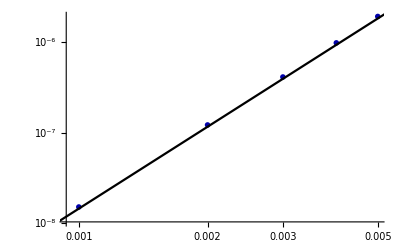

```mathematica
size=0.009;
logInset=Show[ 
ListLogLogPlot[gapH[[1;;-1]],FrameTicks->None, Frame->False,  PlotStyle->  {{ Darker@Blue,PointSize[size]}} ,  PlotRange-> Automatic  , PlotMarkers->"OpenMarkers"(*, Epilog->Inset[ MaTeX["\\Delta_f =  \\sqrt{3} \\;  \\frac{h^xh^yh^z}{1}",Magnification->1.2],  Scaled[{0.3,0.9}] ] *) ],
LogLogPlot[  (3 √3)/(0.262)^2 (h/(√3))^3 ,{h,0.00001,0.85},PlotStyle->Black]              ]
```

```mathematica
gapH
```

{{0.,0.},{0.005,2.91088×10^-8},{0.01,2.34843×10^-7},{0.015,7.95013×10^-7},{0.02,1.88743×10^-6},{0.025,3.69008×10^-6},{0.03,6.38128×10^-6},{0.035,0.0000101398},{0.04,0.000015145},{0.045,0.0000215773},{0.05,0.0000296179},{0.055,0.0000394497},{0.06,0.0000512569},{0.065,0.0000652259},{0.07,0.0000815452},{0.075,0.000100406},{0.08,0.000122002},{0.085,0.000146532},{0.09,0.000174197},{0.095,0.000205203},{0.1,0.000239762},{0.105,0.000278091},{0.11,0.000320414},{0.115,0.000366965},{0.12,0.000417984},{0.125,0.000473725},{0.13,0.000534451},{0.135,0.000600442},{0.14,0.000671996},{0.145,0.00074943},{0.15,0.000833086},{0.155,0.000923337},{0.16,0.00102059},{0.165,0.00112531},{0.17,0.001238},{0.175,0.00135924},{0.18,0.00148971},{0.185,0.00163021},{0.19,0.00178168},{0.195,0.585312},{0.2,0.5875},{0.205,0.589687},{0.21,0.591875},{0.215,0.594063},{0.22,0.59625},{0.225,0.598438},{0.23,0.600625},{0.235,0.602813},{0.24,0.605},{0.245,0.607188},{0.25,0.609375},{0.255,0.611562},{0.26,0.61375},{0.265,0.615938},{0.27,0.618125},{0.275,0.620312},{0.28,0.6225},{0.285,0.624688},{0.29,0.626875},{0.295,0.629063},{0.3,0.63125}}

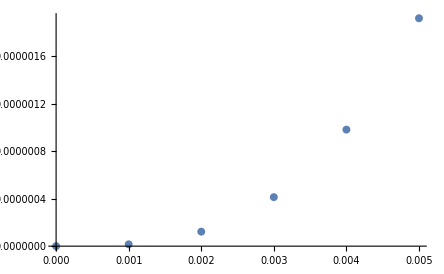

```mathematica
ListPlot[ gapH [[1;;-1]]  ]
```

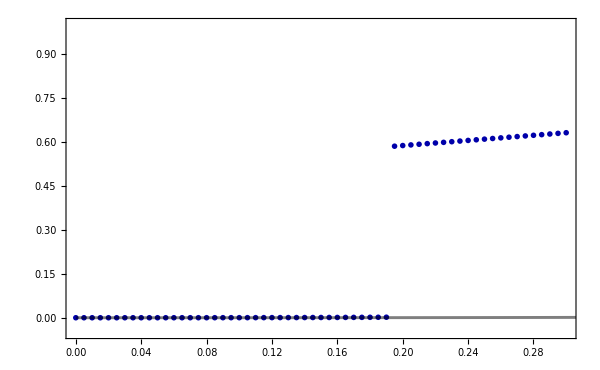

```mathematica
size=0.009;Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0}, 
title=StringReplace["  ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;
Show[
 ListPlot[ gapH  , Joined->False ,  PlotRange-> {-0.05,1} , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["\\text{Gap } \\; \\Delta_f",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,(* GridLines->None,*)  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ]  ,  PlotStyle->  {{ Darker@Blue,PointSize[size]}} , Epilog->Inset[logInset,Scaled[{0.285,0.68}],Center,{0.5,Automatic} ]   ]   
,Plot[  √3(*(1/4)/(0.262)^2*) (h/(2 √3))^3  (*1.207 h^3*) ,{h,0.0000001,0.6}, PlotStyle->{Black,Opacity[.5], Thickness[0.0035 ]}]           ] ]
```

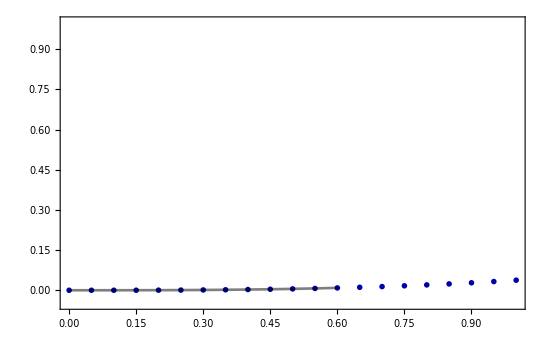
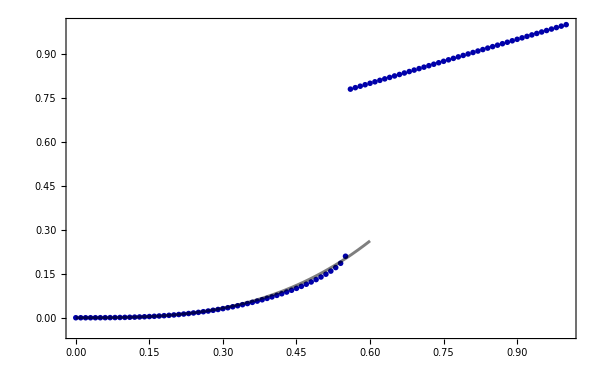

```mathematica
3(0.262)^2
```

0.205932

```mathematica
6/ ( 3(0.262)^2 )
```

29.1358

#### MF vs h

```mathematica
ωH={};χKH={};χcH={};χΓH={};χJH={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];h=h+10^-9 hc;
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free_lambda",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH,{Norm[h],ωM }]; AppendTo[χKH,{Norm[h],χK}]; AppendTo[χcH,{Norm[h],χc}]; AppendTo[χΓH,{Norm[h],χΓ}];  AppendTo[χJH,{Norm[h],χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

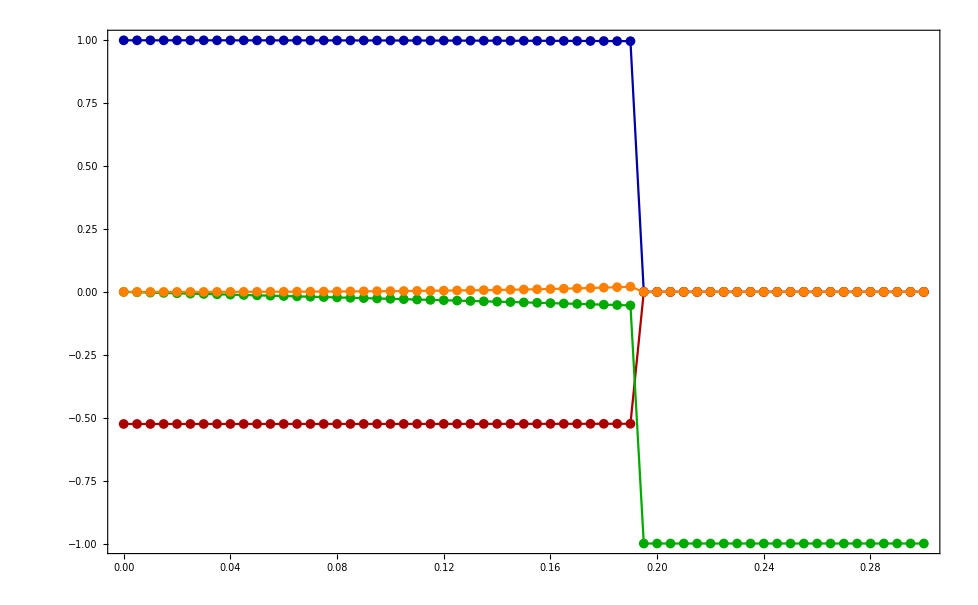

```mathematica
Module[{title,framelabel  }, 
title="J=0, \\, K=+1 , \\,";
framelabel={"||\\mathbf{h}|| ","\\text{MF parameters}"} ;
gK=ListPlot[χKH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Blue]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@framelabel,ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\chi_K"},{.08,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->None,PlotRange-> { -.1,1.2}];
gc=ListPlot[χcH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@framelabel,ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\chi_c"},{.2,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All];
gΓ = ListPlot[χΓH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@framelabel,ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\chi_\\Gamma"},{.32,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All];
gM = ListPlot[ωH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@framelabel,ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"M"},{.45,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All];
Show[gK,gc,gM, gΓ,PlotRange-> Full  ]
]
```

#### MF vs Γ

```mathematica
(*gapΓ={};
Do[Module[{L,Nc,J,K, Γ, h,jG,LG,χ,ω,en,ξG,EnG,η=0,l}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
en= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η, N@kD1], 8 ]    ][[1]];
(*En = EnergiesSortedW[600^2,J,K,Γ,h,χ,ω,η];  
 Disp = lineDispersionSortedW[En];
disp = Disp*)
AppendTo[gapΓ,{Γ,en}]    ],
{p,1,Length@parameters[[1]]}];
*)
```

```mathematica
ωH={};χKH={};χcH={};χΓH={};χJH={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH,{Γ,ωM }]; AppendTo[χKH,{Γ,χK}]; AppendTo[χcH,{Γ,χc}]; AppendTo[χΓH,{Γ,χΓ}];  AppendTo[χJH,{Γ,χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

```mathematica
χJH
```

{{-0.7,0},{-0.6,0},{-0.5,0},{-0.4,0},{-0.3,0.00270184},{-0.2,0.00226023},{-0.1,0.00210568},{0.,0.00202815},{0.1,0.00213869},{0.2,0.0026132},{0.3,1.31816×10^-10},{0.4,0},{0.5,0},{0.6,0},{0.7,0}}

```mathematica
ωH
```

{{-0.7,-0.616678},{-0.6,-0.622839},{-0.5,-0.631287},{-0.4,-0.643582},{-0.3,-0.190323},{-0.2,-0.157594},{-0.1,-0.146985},{0.,-0.143664},{0.1,-0.147664},{0.2,-0.164267},{0.3,-0.857438},{0.4,-0.848449},{0.5,-0.842691},{0.6,-0.838689},{0.7,-0.835748}}

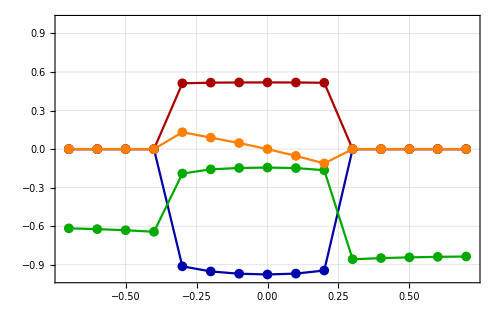

```mathematica
Module[{title}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
gK=ListPlot[χKH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Blue]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\chi_K"},{.08,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic,PlotRange-> { -1,1 }];
gc=ListPlot[χcH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\chi_c"},{.2,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
gΓ = ListPlot[χΓH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\chi_\\Gamma"},{.32,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
gM = ListPlot[ωH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"M"},{.45,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
Show[gK,gc,gM, gΓ,PlotRange-> { {-0.72,0.72},{-1,1} }  ]
]
```

#### Δ MF vs Lagrange multiplier

```mathematica
ωH={};χKH={};χcH={};χΓH={};χJH={};
ωbc={};ωbb={}; Δω={}; Δω0={};ΔW={};ΔWnorm={};ΔhW={};ΔhWnorm={}; λexp={};  λexp0={}; 
enλ1={};enλ2={};enλ3={};enλ={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,gauge="free_lambda" }, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];h=h+10^-9 hc;
η=parameters[[1,p]][[10]]{1,1,1};
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];

AppendTo[ωbc,{η[[1]],       ω0[[1]][[2,1]]   }     ] ;
AppendTo[ωbb,{η[[1]],       -ω0[[1]][[3,4]]   }     ] ;
AppendTo[Δω,{η[[1]],       Abs@( ω0[[1]][[1,2]]+ω0[[1]][[3,4]] )      }     ] ;
AppendTo[Δω0,{η[[1]],       ω0[[1]][[1,2]]-ω0[[1]][[3,4]]    }     ] ;
AppendTo[ΔW,{η[[1]],      Sum[Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ],{σ,1,2},{α,1,3}]     }     ] ;
AppendTo[ΔWnorm,{η[[1]],      1/(2  3)Sum[(Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ])/(Abs@Tr[Transpose[ω0[[σ]]].Mmat[[α]] ]),{σ,1,2},{α,1,3}]     }     ] ;

AppendTo[ΔhW,{η[[1]]h[[1]],      Sum[Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ],{σ,1,2},{α,1,3}]     }     ] ;
AppendTo[ΔhWnorm,{η[[1]]h[[1]],      1/(2  3)Sum[(Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ])/(Abs@Tr[Transpose[ω0[[σ]]].Mmat[[α]] ]),{σ,1,2},{α,1,3}]     }     ] ;
AppendTo[λexp,{η[[1]],  -1+1/(2 3)Sum[   (K+J)/h[[α]](Tr[Transpose[ω0[[σ]]].Mmat[[α]] ] - Tr[Transpose[ω0[[σ]]].Gmat[[α]] ]     ),{σ,1,2},{α,1,3}]     }     ] ;
AppendTo[λexp0,{η[[1]],      Sum[   (K+J)/h[[α]](Tr[ω0[[σ]]ᵀ.Mmat[[α]] ]-Tr[ω0[[σ]]ᵀ.Gmat[[α]] ]  ),{σ,1,1},{α,1,1}]     }     ] ;
AppendTo[enλ,{η[[1]],      -EnG[[2,3]]    }     ] ;
AppendTo[enλ1,{η[[1]],      1/4 EnG[[2,1]]    }     ] ;
AppendTo[enλ2,{η[[1]],      EnG[[2,2]]    }     ] ;
AppendTo[enλ3,{η[[1]],      EnG[[2,3]]    }     ] ;
χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH,{η[[1]],ωM }]; AppendTo[χKH,{η[[1]],χK}]; AppendTo[χcH,{η[[1]],χc}]; AppendTo[χΓH,{η[[1]],χΓ}];  AppendTo[χJH,{η[[1]],χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

```mathematica
FullSimplify[     a /.FindFit[   #[[1;;-2]]    ,  b (x-a) , {a,b},x]     ,x>0    ]&@ΔW
```

-0.562661

```mathematica
λc=FullSimplify[     a /.FindFit[   Reverse[  #[[-3;;-1]]  ]  ,  b (x-a) , {a,b},x]     ,x>0    ]&/@{Δω[[1;;len]],Δω[[len+1;;2len]],Δω[[2len+1;;3len]],Δω[[3len+1;;4len]]}
```

{-0.149051,-0.150223,-0.152484,-0.156333}

{-0.14462,-0.148898,-0.150727,-0.153679}

```mathematica
Module[ {L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title,Δω=ΔW,Nh=Length[hV] }, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]]; len = ⌊ (Length@Δω)/Nh⌋; Δω=ΔW[[1;;len]];
η==parameters[[1,1]][[10]];
title=StringReplace["\\Delta \\mathrm{W} \; \\text{for }  h \\parallel [111] \\, ,  \\, J = X1, K = X2, \\Gamma = X3 ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;
Δω1 =ListPlot[Δω,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],ImageSize->800,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"| \\mathbf{h} | = 0.10 "},{.3,.9}],PlotLabel->(MaTeX[#,Magnification->1.8]&)@title,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\lambda  / | \\mathbf{h} | "," \\Delta \\mathrm{W} = \\vert\\mathrm{Tr}\\big(\\mathrm{W}^{\\mathrm{T}}\\cdot \\mathrm{G}\\big)\\vert  "},PlotRange->All , Epilog->{ Dotted, Black , Line[ { {0.125,-.2},{0.125,.2} }]}];
gΔω=Show[Δω1 ,Plot[0.03872 Abs@(1.159+x),{x,-2,0}]  ] 
]
```

```mathematica
Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,Δe=enλ3,title, color, j0, L0, legends,EnList0,hv,Nh=Length[hV] }, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
len = ⌊ (Length@Δe)/Nh⌋;
hv=(ToString@NumberForm[#,{2,2}])&/@(Norm/@{parameters[[1,1,4]],parameters[[1,1+len,4]],parameters[[1,1+2len,4]]});
title=StringReplace["\\Delta \\mathrm{W} \; \\text{for }  h \\parallel [111] \\, ,  \\, J = X1, K = X2, \\Gamma = X3 ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]   }] ;
legends=StringReplace[#,{"H1"-> hv[[1]],"H2"-> hv[[2]],"H3"-> hv[[3]]}]&/@{"| \\mathbf{h} | = H1 ","| \\mathbf{h} | = H2 ","| \\mathbf{h} | = H3 "};
ListPlot[{Δe[[1;;len]],Δe[[len+1;;2len]],Δe[[2len+1;;3len]]},
Joined->True,PlotMarkers->"OpenMarkers"(*{"●",Small}*),Frame->True,FrameStyle->Directive[Black,16],ImageSize->800,
 PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@legends,{.4,.85}],
PlotLabel->(MaTeX[#,Magnification->1.8]&)@title,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\lambda  / | \\mathbf{h} | "," \\left< H_{\\mathrm{MF}} \\right> "},
PlotRange->All , Epilog->{ Dotted, Black , Line[ { {0.5/4,-.2},{0.5/4,.2} }]}]
]
```

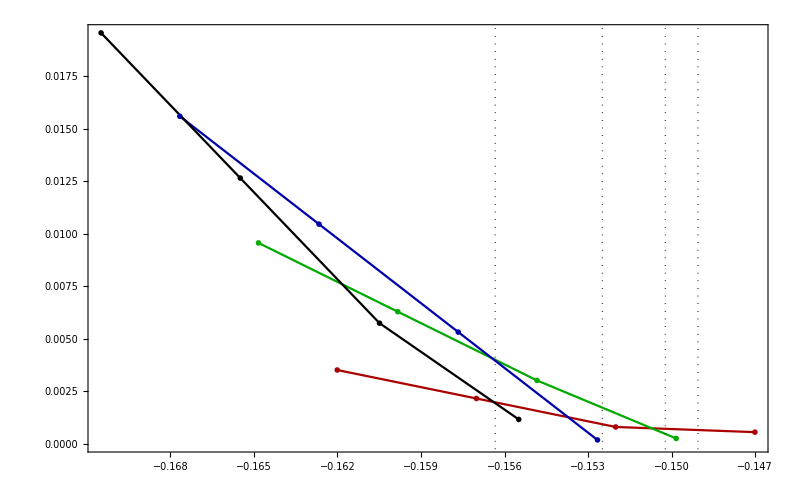

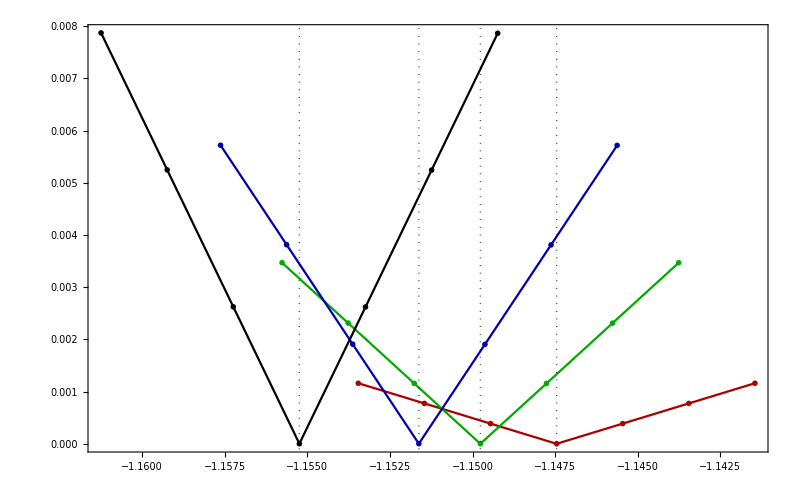

```mathematica
Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,Δω=ΔW,title, color, j0, L0, legends,EnList0,hv,Nh=Length[hV] }, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
len = ⌊ (Length@Δω)/Nh⌋;
hv=(ToString@NumberForm[#,{2,2}])&/@(Norm/@{parameters[[1,1,4]],parameters[[1,1+len,4]],parameters[[1,1+2len,4]],parameters[[1,1+3len,4]]});
title=StringReplace["\\Delta \\mathrm{W} \; \\text{for }  h \\parallel [111] \\, ,  \\, J = X1, K = X2, \\Gamma = X3 ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]   }] ;
legends=StringReplace[#,{"H1"-> hv[[1]],"H2"-> hv[[2]],"H3"-> hv[[3]],"H4"-> hv[[4]]}]&/@{"| \\mathbf{h} | = H1 ","| \\mathbf{h} | = H2 ","| \\mathbf{h} | = H3 ","| \\mathbf{h} | = H4 "};
Show[
ListPlot[{Δω[[1;;len]],Δω[[len+1;;2len]],Δω[[2len+1;;3len]],Δω[[3len+1;;4len]]},
Joined->True,PlotMarkers->"OpenMarkers"(*{"●",Small}*),Frame->True,FrameStyle->Directive[Black,16],ImageSize->800,
 PlotStyle->{Darker[Red],Darker[Green],Darker[Blue],Darker[Black]},
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@legends,{.9,.85}],
PlotLabel->(MaTeX[#,Magnification->1.8]&)@title,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\lambda  / | \\mathbf{h} | "," \\Delta \\mathrm{W} = \\vert\\mathrm{Tr}\\big(\\mathrm{W}^{\\mathrm{T}}\\cdot \\mathrm{G}\\big)\\vert  =\\left< \\mathrm{i} c_i \\mathrm{G} c_i\\right>  "},
PlotRange->All , Epilog->{{ Dotted, Black , Line[ { {#,-.2},{#,.2} }]}&/@{-0.14905145544111398,-0.15022322125364185,-0.15248435747369737,-0.15633285924056683}    }   ]
(*,Plot[ f,{x,-1.2,-1}]*)
]
]
```

```mathematica
{ Dotted, Black , Line[ { {#,-.2},{#,.2} }]}&/@{-1.1474563477740904,-1.1497631822919772,-1.151624737871482,-1.155238374679877}
```

{{Dashing[{0,Small}],GrayLevel[0],Line[{{-1.14746,-0.2},{-1.14746,0.2}}]},{Dashing[{0,Small}],GrayLevel[0],Line[{{-1.14976,-0.2},{-1.14976,0.2}}]},{Dashing[{0,Small}],GrayLevel[0],Line[{{-1.15162,-0.2},{-1.15162,0.2}}]},{Dashing[{0,Small}],GrayLevel[0],Line[{{-1.15524,-0.2},{-1.15524,0.2}}]}}

```mathematica
f=FullSimplify[    Abs[ b(x-a)] /.FindFit[   Reverse[  #[[-5;;-1]]  ]  ,  b (x-a) , {a,b},x]     ,x>0    ]&/@{Δω[[1;;len]],Δω[[len+1;;2len]],Δω[[2len+1;;3len]],Δω[[3len+1;;4len]]}
```

{0.0161159 (1.14746+x),0.0481832 (1.14976+x),0.079458 (1.15162+x),0.109344 (1.15524+x)}

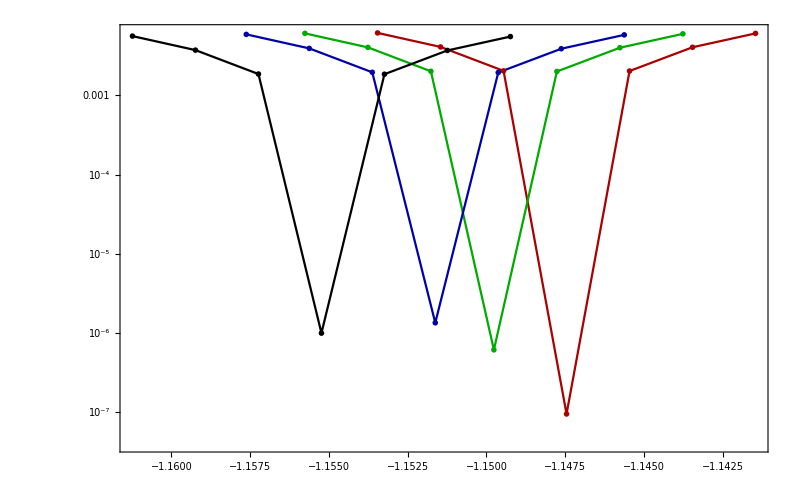

```mathematica
Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,Δω=ΔWnorm,title, color, j0, L0, legends,EnList0,hv,Nh=Length[hV] }, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
len = ⌊ (Length@Δω)/Nh⌋;
hv=(ToString@NumberForm[#,{2,2}])&/@(Norm/@{parameters[[1,1,4]],parameters[[1,1+len,4]],parameters[[1,1+2len,4]],parameters[[1,1+3len,4]]});
title=StringReplace["\\Delta \\mathrm{W} \; \\text{for }  h \\parallel [111] \\, ,  \\, J = X1, K = X2, \\Gamma = X3 ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]   }] ;
legends=StringReplace[#,{"H1"-> hv[[1]],"H2"-> hv[[2]],"H3"-> hv[[3]],"H4"-> hv[[4]]}]&/@{"| \\mathbf{h} | = H1 ","| \\mathbf{h} | = H2 ","| \\mathbf{h} | = H3 ","| \\mathbf{h} | = H4 "};
ListLogPlot[{Δω[[1;;len]],Δω[[len+1;;2len]],Δω[[2len+1;;3len]],Δω[[3len+1;;4len]]},
Joined->True,PlotMarkers->"OpenMarkers"(*{"●",Small}*),Frame->True,FrameStyle->Directive[Black,16],ImageSize->800,
 PlotStyle->{Darker[Red],Darker[Green],Darker[Blue],Black},
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@legends,{.1,.25}],
PlotLabel->(MaTeX[#,Magnification->1.8]&)@title,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\lambda  / | \\mathbf{h} | "," \\Delta \\mathrm{W} = \\vert\\mathrm{Tr}\\big(\\mathrm{W}^{\\mathrm{T}}\\cdot \\mathrm{G}\\big)\\vert  =\\left< \\mathrm{i} c_i \\mathrm{G} c_i\\right>  "},
PlotRange->All , Epilog->{ Dotted, Black , Line[ { {0.5/4,-.2},{0.5/4,.2} }]}]
]
```

```mathematica
(*Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,Δω=ΔhW,title, color, j0, L0, legends,EnList0,hv,Nh=Length[hV] }, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
len = ⌊ (Length@Δω)/Nh⌋;
hv=(ToString@NumberForm[#,{2,2}])&/@(Norm/@{parameters[[1,1,4]],parameters[[1,1+len,4]],parameters[[1,1+2len,4]]});
title=StringReplace["\\Delta \\mathrm{W} \; \\text{for }  h \\parallel [111] \\, ,  \\, J = X1, K = X2, \\Gamma = X3 ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]   }] ;
legends=StringReplace[#,{"H1"-> hv[[1]],"H2"-> hv[[2]],"H3"-> hv[[3]]}]&/@{"| \\mathbf{h} | = H1 ","| \\mathbf{h} | = H2 ","| \\mathbf{h} | = H3 "};
ListPlot[{Δω[[1;;len]],Δω[[len+1;;2len]],Δω[[2len+1;;3len]],Δω[[3len+1;;4len]]},
Joined->True,PlotMarkers->"OpenMarkers"(*{"●",Small}*),Frame->True,FrameStyle->Directive[Black,16],ImageSize->800,
 PlotStyle->{Darker[Red],Darker[Green],Darker[Blue],Darker[Black]},
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@legends,{.4,.85}],
PlotLabel->(MaTeX[#,Magnification->1.8]&)@title,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\lambda  / | \\mathbf{h} | "," \\Delta \\mathrm{W} = \\vert\\mathrm{Tr}\\big(\\mathrm{W}^{\\mathrm{T}}\\cdot \\mathrm{G}\\big)\\vert  =\\left< \\mathrm{i} c_i \\mathrm{G} c_i\\right>  "},
PlotRange->All , Epilog->{ Dotted, Black , Line[ { {0.5/4,-.2},{0.5/4,.2} }]}]
]*)
```

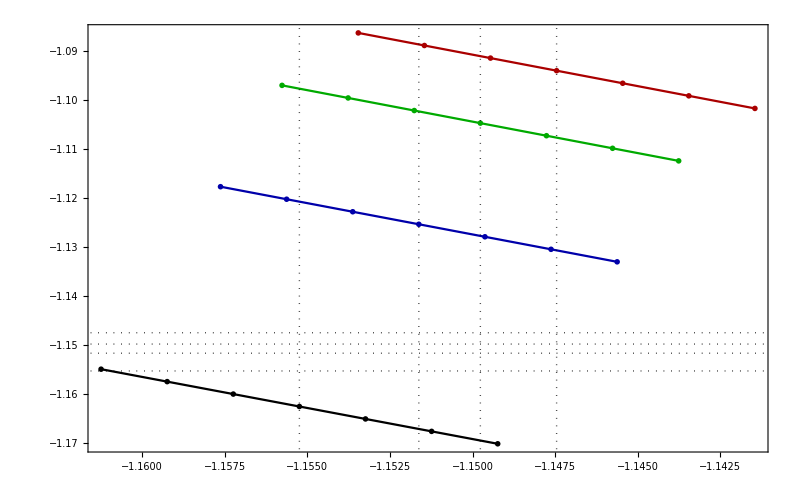

```mathematica
Module[ {L, Nc,J,K,Γ, h ,η, χ0,ω0 ,Δω=λexp0,title, color, j0, L0, legends,EnList0,hv,Nh=Length[hV] }, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
len = ⌊ (Length@Δω)/Nh⌋;
hv=(ToString@NumberForm[#,{2,2}])&/@(Norm/@{parameters[[1,1,4]],parameters[[1,1+len,4]],parameters[[1,1+2len,4]],parameters[[1,1+3len,4]]});
title=StringReplace["\\Delta \\mathrm{W} \; \\text{for }  h \\parallel [111] \\, ,  \\, J = X1, K = X2, \\Gamma = X3 ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]   }] ;
legends=StringReplace[#,{"H1"-> hv[[1]],"H2"-> hv[[2]],"H3"-> hv[[3]],"H4"-> hv[[4]]}]&/@{"| \\mathbf{h} | = H1 ","| \\mathbf{h} | = H2 ","| \\mathbf{h} | = H3 ","| \\mathbf{h} | = H4 "};
Show[
ListPlot[{Δω[[1;;len]],Δω[[len+1;;2len]],Δω[[2len+1;;3len]],Δω[[3len+1;;4len]]},
Joined->True,PlotMarkers->"OpenMarkers"(*{"●",Small}*),Frame->True,FrameStyle->Directive[Black,16],ImageSize->800,
 PlotStyle->{Darker[Red],Darker[Green],Darker[Blue],Darker[Black]},
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@legends,{.9,.85}],
PlotLabel->(MaTeX[#,Magnification->1.8]&)@title,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\lambda  / | \\mathbf{h} | "," \\Delta \\mathrm{W} = \\vert\\mathrm{Tr}\\big(\\mathrm{W}^{\\mathrm{T}}\\cdot \\mathrm{G}\\big)\\vert  =\\left< \\mathrm{i} c_i \\mathrm{G} c_i\\right>  "},
PlotRange-> All(*{{-1.165,-1.14},{-1.16,-1.13}}*)   , Epilog->{{ Dotted, Black , Line[ { {#,-2},{#,2} }]}&/@{-1.1474563477740904,-1.1497631822919772,-1.151624737871482,-1.155238374679877},{ Dotted, Black , Line[ { {-2,#},{2,#} }]}&/@{-1.1474563477740904,-1.1497631822919772,-1.151624737871482,-1.155238374679877}}   ]
(*,Plot[ f,{x,-1.2,-1}]*)
]
]
```

```mathematica
Module[{Δω=λexp0}, FullSimplify[     (a x + b ) /.FindFit[ # ,  a x + b , {a,b},x]     ,x>0    ]&/@{Δω[[1;;len]],Δω[[len+1;;2len]],Δω[[2len+1;;3len]],Δω[[3len+1;;4len]]} ]
```

{-2.5644-1.28136 x,-2.57808-1.2814 x,-2.59328-1.27465 x,-2.62497-1.26596 x}

#### MF vs Lagrange multiplier

```mathematica
ωH={};χKH={};χcH={};χΓH={};χJH={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,gauge="free_lambda" }, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];h=h+10^-9 hc;
η=parameters[[1,p]][[10]]{1,1,1};
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH,{η[[1]],ωM }]; AppendTo[χKH,{η[[1]],χK}]; AppendTo[χcH,{η[[1]],χc}]; AppendTo[χΓH,{η[[1]],χΓ}];  AppendTo[χJH,{η[[1]],χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

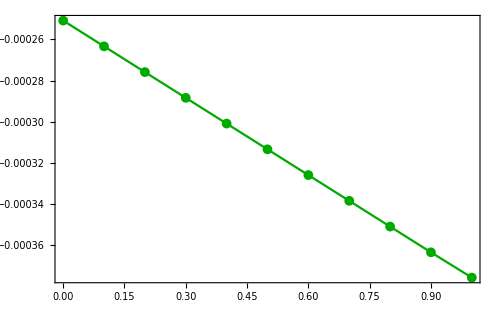

```mathematica
gM
```

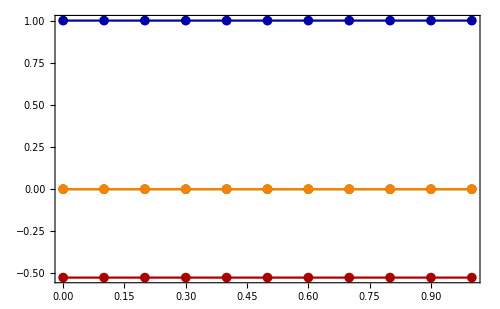

```mathematica
Module[{title,framelabel  }, 
title="J=0, \\, K=+1 , \\,";
framelabel={"\\lambda/||\\mathbf{h}|| ","\\text{MF parameters}"} ;
gK=ListPlot[χKH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Blue]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@framelabel,ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\chi_K"},{.08,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->None,PlotRange-> { -.1,1.2}];
gc=ListPlot[χcH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@framelabel,ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\chi_c"},{.2,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All];
gΓ = ListPlot[χΓH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@framelabel,ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\chi_\\Gamma"},{.32,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All];
gM = ListPlot[ωH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@framelabel,ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"M"},{.45,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All];
Show[gK,gc,gM, gΓ,PlotRange->Automatic ]
]
```

#### Gap vs Lagrange multiplier

```mathematica
energyGap[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {energies},  energies= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η, N@kD1], 8 ]]; energies⟦1⟧]
```

```mathematica
gapH={};
Do[Module[{L,Nc,J,K, Γ, h,jG,LG,Jm,χ,ω,en,ξG,EnG,λ,l,gauge="free_lambda" }, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
(*η=parameters[[1,p]][[10]]{1,1,1};*)
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];

Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},{0,0,0}];
λ=parameters[[1,p]][[10]]{ h,h};
H=HmfMomentum[Jm,h,λ,U,W, k];

en= Sort[Abs/@Eigenvalues[ Chop@N@HmfMomentum[Jm,h,λ, χ,ω,N@kD1], 8 ]    ][[1]];
(*En = EnergiesSortedW[600^2,J,K,Γ,h,χ,ω,η];  
 Disp = lineDispersionSortedW[En];
disp = Disp*)
AppendTo[gapH,{λ[[1]][[1]] ,en}]    ],
{p,1,Length@parameters[[1]]}];
```

```mathematica
gapH
```

{{0.00433013,0.00145858},{0.0129904,0.00174365},{0.0216506,0.00202369},{0.0303109,0.00229343},{0.0389711,0.00254763},{0.0476314,0.00278103},{0.0562917,0.00298832},{0.0649519,0.00316417},{0.0736122,0.00330315}}

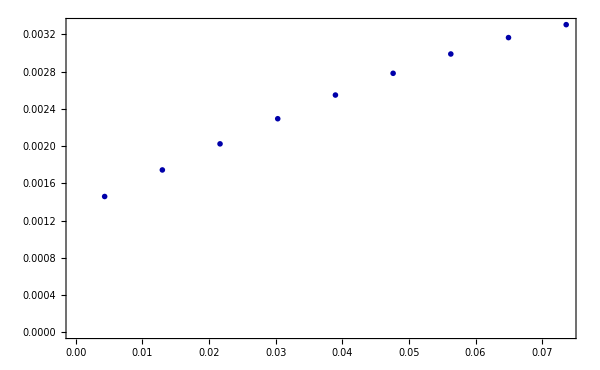

```mathematica
size=0.009;Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0}, 
title=StringReplace["  ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;

 ListPlot[ gapH  , Joined->False ,  PlotRange-> Automatic , FrameLabel->{MaTeX["\\lambda/h",Magnification->2] , MaTeX["\\text{Gap } \\; \\Delta_f",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,(* GridLines->None,*)  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ]  ,  PlotStyle->  {{ Darker@Blue,PointSize[size]}}    ]   
 ]
```

#### Δ MF vs Lagrange multiplier (for each h) ??

```mathematica
ωH={};χKH={};χcH={};χΓH={};χJH={};
ωbc={};ωbb={}; Δω={}; Δω0={};ΔW={};ΔWnorm={};ΔhW={};ΔhWnorm={}; λexp={};  λexp0={}; 
enλ1={};enλ2={};enλ3={};enλ={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,gauge="free_lambda" }, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];h=h+10^-9 hc;
η=parameters[[1,p]][[10]]{1,1,1};
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];

AppendTo[ωbc,{η[[1]],       ω0[[1]][[2,1]]   }     ] ;
AppendTo[ωbb,{η[[1]],       -ω0[[1]][[3,4]]   }     ] ;
AppendTo[Δω,{η[[1]],       Abs@( ω0[[1]][[1,2]]+ω0[[1]][[3,4]] )      }     ] ;
AppendTo[Δω0,{η[[1]],       ω0[[1]][[1,2]]-ω0[[1]][[3,4]]    }     ] ;
AppendTo[ΔW,{h[[1]],η[[1]],      Sum[Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ],{σ,1,2},{α,1,3}]     }     ] ;
AppendTo[ΔWnorm,{h[[1]],η[[1]],      1/(2  3)Sum[(Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ])/(Abs@Tr[Transpose[ω0[[σ]]].Mmat[[α]] ]),{σ,1,2},{α,1,3}]     }     ] ;

AppendTo[ΔhW,{η[[1]]h[[1]],      Sum[Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ],{σ,1,2},{α,1,3}]     }     ] ;
AppendTo[ΔhWnorm,{η[[1]]h[[1]],      1/(2  3)Sum[(Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ])/(Abs@Tr[Transpose[ω0[[σ]]].Mmat[[α]] ]),{σ,1,2},{α,1,3}]     }     ] ;
AppendTo[λexp,{η[[1]],  -1+1/(2 3)Sum[   (K+J)/h[[α]](Tr[Transpose[ω0[[σ]]].Mmat[[α]] ] - Tr[Transpose[ω0[[σ]]].Gmat[[α]] ]     ),{σ,1,2},{α,1,3}]     }     ] ;
AppendTo[λexp0,{η[[1]],      Sum[   (K+J)/h[[α]](Tr[ω0[[σ]]ᵀ.Mmat[[α]] ]-Tr[ω0[[σ]]ᵀ.Gmat[[α]] ]  ),{σ,1,1},{α,1,1}]     }     ] ;
AppendTo[enλ,{η[[1]],      -EnG[[2,3]]    }     ] ;
AppendTo[enλ1,{η[[1]],      1/4 EnG[[2,1]]    }     ] ;
AppendTo[enλ2,{η[[1]],      EnG[[2,2]]    }     ] ;
AppendTo[enλ3,{η[[1]],      EnG[[2,3]]    }     ] ;
χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH,{η[[1]],ωM }]; AppendTo[χKH,{η[[1]],χK}]; AppendTo[χcH,{η[[1]],χc}]; AppendTo[χΓH,{η[[1]],χΓ}];  AppendTo[χJH,{η[[1]],χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

OpenRead::noopen: Cannot open C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\802\free_lambda\lambda_-0.598404_JKG={0., -1., 0.}\data\h=(0.11,0,0)_L=40_A=6.txt.

Failed to OpenRead file at:

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\802\free_lambda\lambda_-0.598404_JKG={0., -1., 0.}\data\h=(0.11,0,0)_L=40_A=6.txt

$Aborted

```mathematica
FindFit[ ΔWnorm[[;;,2;;3]] , b( x-a),{a,b},x]
```

{a→-0.58204,b→-1.54297}

```mathematica
FindFit[ ΔW[[;;,2;;3]] , b( x-a),{a,b},x]
```

{a→-0.581923,b→-0.157848}

```mathematica
ΔW[[;;,2;;3]]
```

{{-0.594473,0.00198101},{-0.593473,0.00182316},{-0.592473,0.00166531}}

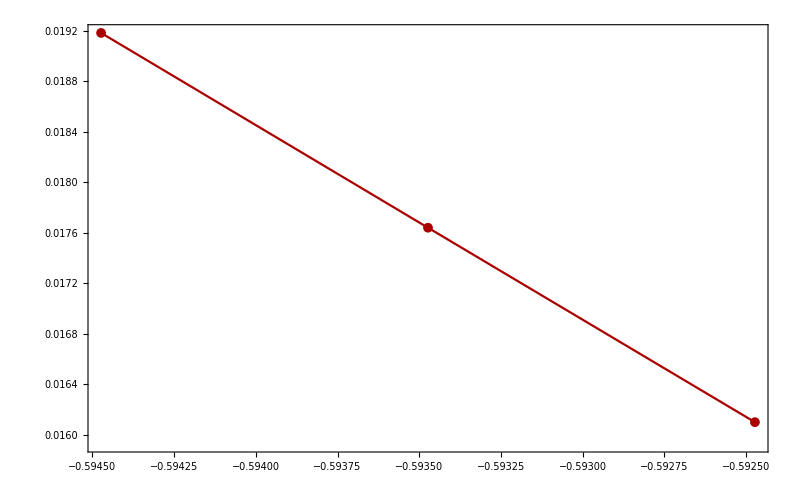

```mathematica
Module[ {L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title,Δω=ΔWnorm[[;;,2;;3]],Nh=1 }, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]]; len = ⌊ (Length@Δω)/Nh⌋;
η==parameters[[1,1]][[10]];
title=StringReplace["\\Delta \\mathrm{W} \; \\text{for }  h \\parallel [111] \\, ,  \\, J = X1, K = X2, \\Gamma = X3 ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;
Δω1 =ListPlot[Δω,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],ImageSize->800,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"| \\mathbf{h} | = 0.10 "},{.3,.9}],PlotLabel->(MaTeX[#,Magnification->1.8]&)@title,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\lambda  / | \\mathbf{h} | "," \\Delta \\mathrm{W} = \\vert\\mathrm{Tr}\\big(\\mathrm{W}^{\\mathrm{T}}\\cdot \\mathrm{G}\\big)\\vert  "},PlotRange->All , Epilog->{ Dotted, Black , Line[ { {0.125,-.2},{0.125,.2} }]}];
gΔω=Show[Δω1 ,Plot[0.03872 Abs@(1.159+x),{x,-2,0}]  ] 
]
```

```mathematica
FullSimplify[     a /.FindFit[   #[[-1;;-2;;-1]]    ,  b (x-a) , {a,b},x]     ,x>0    ]&/@(  SplitBy[ ΔWnorm, #[[1]]&][[;;,;;,2;;3]]  )
```

```mathematica
λcs2=FullSimplify[     b /.FindFit[   #[[1;;2]]    ,  b (x-a) , {a,{b,-1.5}},x]     ,x>0    ]&/@(  SplitBy[ ΔWnorm, #[[1]]&][[;;,;;,2;;3]]  )
```

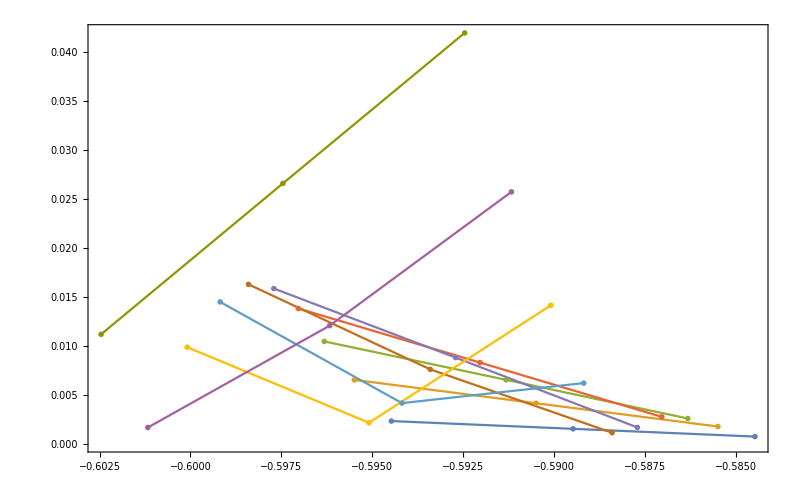

```mathematica
Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,Δω=ΔW,ΔωSplit,title, color, j0, L0, legends,EnList0,hv,Nh=Length[hV] }, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
len = ⌊ (Length@Δω)/Nh⌋;
hv=Table[parameters[[1,1+(i-1)len,4]] , {i,1,Nh}];
legends=Table[ StringJoin["| \\mathbf{h} | = ",ToString[  Norm@hv[[i]]]   ],{i,1,Nh}];
hv=(ToString@NumberForm[#,{2,2}])&/@(Norm/@hv);
title=StringReplace["\\Delta \\mathrm{W} \; \\text{for }  h \\parallel [111] \\, ,  \\, J = X1, K = X2, \\Gamma = X3 ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]   }] ;


ΔωSplit=SplitBy[ Δω, #[[1]]&][[;;,;;,2;;3]] ;
ListPlot[ΔωSplit[[1;;20;;2]],
Joined->True,PlotMarkers->"OpenMarkers"(*{"●",Small}*),Frame->True,FrameStyle->Directive[Black,16],ImageSize->800,
(* PlotStyle->{Darker[Red],Darker[Green],Darker[Blue],Darker[Black]},*)
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@legends,{.8,.8}],
PlotLabel->(MaTeX[#,Magnification->1.8]&)@title,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\lambda  / | \\mathbf{h} | "," \\Delta \\mathrm{W} = \\vert\\mathrm{Tr}\\big(\\mathrm{W}^{\\mathrm{T}}\\cdot \\mathrm{G}\\big)\\vert  =\\left< \\mathrm{i} c_i \\mathrm{G} c_i\\right>  "},
PlotRange->{Full,All} (*,Epilog->{ { Dotted, Black , Line[ { {#,-2},{#,0.005} }]}&/@(λcs[[-13;;-1]])   }*)
]]
```

#### exp λ and λ by minimization vs h

```mathematica
λh = Sort@Thread[ {h0V,-λcs}];
```

```mathematica
λcs={-0.5799611965654217,-0.5812563647973628,-0.581926393004252,-0.5823669527085065,-0.5830850951618409,-0.58385979177868,-0.5846131325337345,-0.5855916023864705,-0.5865287969999988,-0.5878170709765931,-0.5890630579931387,-0.5905991969958831,-0.5921842299477734,-0.5940158554591956,-0.5937057049109367,-0.7024379990618725,-0.6019745564786461,-0.6032137469322231,-0.6061168552630138,-0.609324605771954,-0.612808238529061,-0.6166788806062662,-0.6208661454515428,-0.6254598290828619,-0.6307208124925465,-0.6364371551653731,-0.6427776529546806,-0.6498479962813825,-0.6577945010338859,-0.6669717634084164,-0.677550511632808,-0.6900057325718756,-0.7058109450511634,-0.7253035578927515,-0.7459659656735238,-0.7591514254212349,-0.9713941075860365,-0.622109967559428,-0.6239256681513095,-0.6257550210244529,-0.6274262973478442,-0.6266567986050285,-0.6265123921973748,-0.628637915633542,-0.6307147394588863,-0.6327359696395187,-0.6346913672145109,-0.636564643033912,-0.6383233366016023,-0.639866175936617};
```

```mathematica
(a + b x + c x^2 + d x^3+e x^4)/.FindFit[Join[λh[[1;;14]],λh[[17;;36]]],a + b x + c x^2 + d x^3+e x^4, {a,b,c,d,e},x]
```

0.583057-0.149803 x+3.29789 x^2-16.0973 x^3+33.1101 x^4

```mathematica
λhr = Join[λh[[1;;14]],λh[[17;;36]]];
```

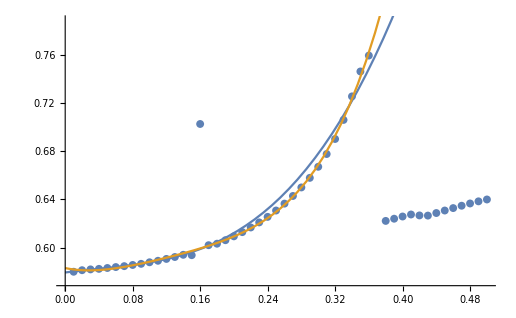

```mathematica
Show[ListPlot[λh],Plot[{0.5793547000739069+0.08976402323298617 x-0.48774941328265015 x^2+4.277304066005793 x^3,0.5830567372899136-0.14980273860827492 x+3.2978906234637577 x^2-16.097304069981774 x^3+33.110071778834154 x^4},{x,0,.5}]   ]
```

```mathematica
ωH={};χKH={};χcH={};χΓH={};χJH={};
ωbc={};ωbb={}; Δω={}; Δω0={};ΔW={};ΔWnorm={};ΔhW={};ΔhWnorm={}; λexp={};  λmin={};
enλ1={};enλ2={};enλ3={};enλ={}; j=1;
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ,gauge="free_lambda" }, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];h=h+10^-9 hc;
η=parameters[[1,p]][[10]]{1,1,1};
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,gauge,NbName ]  ];


AppendTo[ΔW,{η[[1]],      Sum[Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ],{σ,1,2},{α,1,3}]     }     ] ;
AppendTo[ΔWnorm,{η[[1]],      1/(2  3)Sum[(Abs@Tr[Transpose[ω0[[σ]]].Gmat[[α]] ])/(Abs@Tr[Transpose[ω0[[σ]]].Mmat[[α]] ]),{σ,1,2},{α,1,3}]     }     ] ;

If[ Mod[p,Length[Δηs],1]==1,
AppendTo[λmin,{Norm[h],      λcs[[j]]   }     ] ; j=j+1;
AppendTo[λexp,{Norm[h],    1/6  1/h[[1]] Sum[   (K+J)/4(Tr[ω0[[σ]]ᵀ.Mmat[[α]] ] ),{σ,1,2},{α,1,3}]     }     ] 
];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH,{Norm[h],ωM }]; AppendTo[χKH,{Norm[h],χK}]; AppendTo[χcH,{Norm[h],χc}]; AppendTo[χΓH,{Norm[h],χΓ}];  AppendTo[χJH,{Norm[h],χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

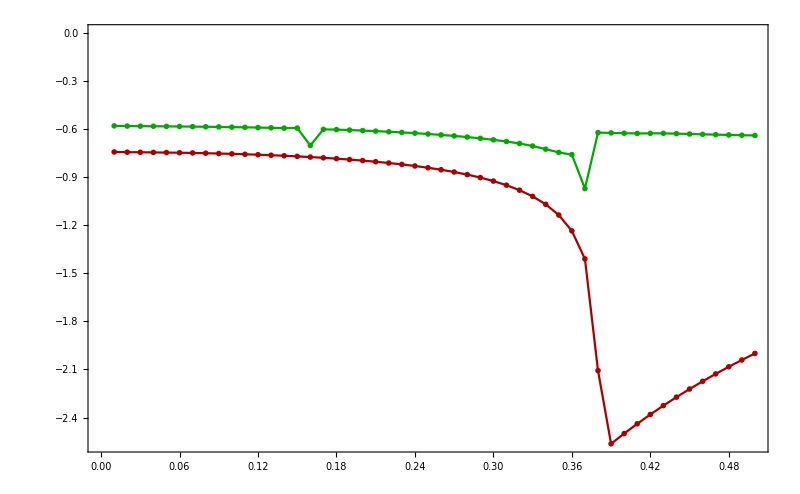

```mathematica
Module[ {J,K,Γ,h,title, color, j0, L0, legends,EnList0,hv,Nh=Length[hV] }, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];

title=StringReplace["\\lambda \; \\text{for }  h \\parallel [111] \\, ,  \\, J = X1, K = X2, \\Gamma = X3 ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]   }] ;


ListPlot[{λexp,λmin  },
Joined->True,PlotMarkers->"OpenMarkers"(*{"●",Small}*),Frame->True,FrameStyle->Directive[Black,16],ImageSize->800,
 PlotStyle->{Darker[Red],Darker[Green],Darker[Blue],Darker[Black]},
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\frac{J+K}{2}\\,\\mathrm{Tr}\\big(\\mathrm{W}^{\\mathrm{T}}_{A} \\, \\mathrm{N}^1 \\big)","\\big( \\lambda_{\\,\\mathrm{ c}} + h^1 \\big) / h^1 "},{.8,.85}],
PlotLabel->(MaTeX[#,Magnification->1.8]&)@title,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"| \\mathbf{h} | "," \\big( \\, \\lambda^\\gamma + h^\\gamma \\, \\big) \\, /  \\, h^\\gamma   "},
PlotRange-> All]
]
```

## charge density - pure Kitaev

#### pure loop w/o vortices

```mathematica
Do[   Module[{gauge="g0",J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},u0,ES,Δt,hp=Mod[p,Length@hV,1] }, 

 {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 
Nc=L^2;
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];

u0=uniformU[-1,L];

(* for Pure Kitaev model: *)
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Epure,Upure},   
κ0=toKappa[h](*(h0/Sqrt[3])^3/(0.262)^2*); 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  
ω0=Table[ωGA,2,{r,1,Nc} ];
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   
Tpure=TmatPure[L]; 
Upure=UmatPure[Tpure† . Hpure . Tpure]; 
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];
(*   χ0=χgauge4v[χ0,L];*)
dataToFilePure[parameters[[ev,p]],L,acuracy,gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} } ]; 
Print["Pure data saved: "];
Print["Kappa=",κ,"; Lambda=",toλ[h] ,"; Epure=",Epure,"; "];
       ]; 
Print["L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); ", " eV0=",parameters[[ev,p]][[10]]/1700 ," x 1700 "];
Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls  ];
        ]  , {ev,1,Length[parameters]}, {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]}  ]
```

#### pure loop w/ vortices

```mathematica
Do[   Module[{gauge="g4",J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},u0,ES,Δt,hp=Mod[p,Length@hV,1] }, 

 {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 
Nc=L^2;
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
u0=gauge4v[uniformU[-1,L],L];
(* for Pure Kitaev model: *)
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Epure,Upure},   
κ0=toKappa[h]; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  
ω0=Table[ωGA,2,{r,1,Nc} ];
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   
Tpure=TmatPure[L]; 
Upure=UmatPure[Tpure† . Hpure . Tpure]; 
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);

{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   χ0=χgauge4v[χ0,L];
dataToFilePure[parameters[[ev,p]],L,acuracy,gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} } ]; 
Print["Pure data saved: "];
Print["Kappa=",κ,"; Lambda=",toλ[h] ,"; Epure=",Epure,"; "];
       ]; 
Print["L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); ", " eV0=",N[Round[ 100  parameters[[ev,p]][[10]]/1700 ] /100]," x 1700 "];
Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls  ];
        ]  , {ev,1,Length[parameters]}, {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]}  ]
```

### charge density

```mathematica
charge1={};charge2={};charge3={};chargeDia={};chargeHex={};
Do[ 
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure[parameters[[1,p]],L,acuracy, gauge ]  ];
               ω=Table[ωGA,2,{r,1,Nc} ];
          ξ=Table[0 ωGA,2,3,{r,1,Nc} ];

	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@(Round[10000toKappa[h]   ]/10000) ];
	u0= gauge4v[ uniformU[-1,L] ,L];     
	t=ts[[tp]];     

nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];               
                                                                                                                      
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,sNNN];
(*δn0=δn; ξ0=ξ; sNN0=sNN;sNNN0=sNNN;χ0=χ;*)
δn1=  Module[ {max=Max[Abs@δn],δ0=Abs[4 ((JH t[[2]]^2 t[[5]] (11 JH^2-10 JH U+3 U^2))/(18 (3 JH^2-4 JH U+U^2)^3))]},(*Print["max/δ0=",max/δ0];*)    δn/max    ];	
Print[nameComplement];
(* graphics*)
title=StringReplace["\\text{Kitaev Pure }\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\CHARG_CONFIG_FLUX\\CHARG_CONFIG_FLUX_XX_pure.pdf","XX"-> nameComplement]  }],chargeConfigFlux[δn,χ,ω,L,title]       ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\CHARG_CONFIG_FLUX_ZOOM\\CHARG_CONFIG_FLUX_ZOOM_XX_pure.pdf","XX"-> nameComplement]  }],chargeConfigFluxZoom[δn,χ,ω,L,title]       ];Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\CHARG_PLOT\\CHARG_PLOT_ZZ_XX_pure.pdf","XX"-> nameComplement]   }],chargePlotZZ[δn,L,parameters[[1,p]],hV[[hp]]] ];

Module[{R,q,dip,Q,v}, L=Ls[[l]]; R=Min[ 5 ](*L/4-3(1/(√3))*);(*
Print["L=",L,"; R=",R,"; t=",t,"; "];
Do[     q[v]=chargeVortex[δn,L,v,R];d[v]=dipoleVortex[δn,L,v,R];Q[v]=quadrupoleVortex[δn,L,v,R];      ,{v,1,4}];
Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]] (*,"; q2=",q[2],"; d2= ",MatrixForm[d[2]],"; Q2= "MatrixForm[Q[2]] ];
Print[ "q3=",q[3],"; d3= ",MatrixForm[d[3]],"; Q3= "MatrixForm[Q[3]],"; q4=",q[4],"; d4= ",MatrixForm[d[4]],"; Q4= "MatrixForm[Q[4]]  *)  ];     *)
Print["L=",L,"; R=",R,"; t=",t,"; "];(*
Do[     q[v]=chargeVortex[δn,L,v,R];d[v]=dipoleVortex[δn,L,v,R];Q[v]=quadrupoleVortex[δn,L,v,R];      ,{v,{1} }];
AppendTo[charge1,{L,R,q[1],d[1],Q[1]}];
Do[     q[v]=chargeVortexDia[δn,L,v,R];d[v]=dipoleVortexDia[δn,L,v,R];Q[v]=quadrupoleVortexDia[δn,L,v,R];      ,{v,{1} }];
AppendTo[chargeDia,{L,R,q[1],d[1],Q[1]}];*)
Do[     q[v]=chargeVortexHex[δn,L,v,R];dip[v]=dipoleVortexHex[δn,L,v,R];Q[v]=quadrupoleVortexHex[δn,L,v,R];      ,{v,{1} }];
AppendTo[chargeHex,{L,R,q[1],dip[1],Q[1]}];

Print[ "q1=",q[1],"; d1= ",MatrixForm[dip[1]],"; Q1= "MatrixForm[Q[1]]    ];   
] ;
(*
Module[{R,q,d,Q,v}, L=Ls[[l]]; R=L/4-2;(*
Print["L=",L,"; R=",R,"; t=",t,"; "]; 
Print[ "q1=",q[1],"; d1= ",MatrixForm[d[1]],"; Q1= "MatrixForm[Q[1]]    ];   *)  
Do[     q[v]=chargeVortex[δn,L,v,R];d[v]=dipoleVortex[δn,L,v,R];Q[v]=quadrupoleVortex[δn,L,v,R];      ,{v,{1} }];
AppendTo[charge2,{L,R,q[1],d[1],Q[1]}];          ] ;
Module[{R,q,d,Q,v}, L=Ls[[l]]; R=5; 
Do[     q[v]=chargeVortex[δn,L,v,R];d[v]=dipoleVortex[δn,L,v,R];Q[v]=quadrupoleVortex[δn,L,v,R];      ,{v,{1} }];
AppendTo[charge3,{L,R,q[1],d[1],Q[1]}];
] ;*)
],{p,1,Length@parameters[[1]]  },{l,1,Length@Ls}]
```

t=3_h={0.2, 0, 0}-L=32-ac=6

L=32; R=5; t={15,160,-36,0,-60};

q1=-0.00761101; d1= (-8.18807×10^-14
-4.05259×10^-13); Q1=  (0.857031 | 4.50202×10^-13 | 0.
4.50202×10^-13 | 0.861466 | 0.
0. | 0. | -1.7185)

OpenRead::noopen: Cannot open C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\pure\g4\t=3_eV=0._JKG={0, -1., 0}_JKGmod={0, -1., 0}\data\h=(0.2,0,15)_L=32_A=6.txt.

Failed to OpenRead file at:

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\Mathematica2\Files\pure\g4\t=3_eV=0._JKG={0, -1., 0}_JKGmod={0, -1., 0}\data\h=(0.2,0,15)_L=32_A=6.txt

$Aborted

### finite size charge density

```mathematica
sizeQzz[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[3,3]]  },{i,1,Length@charge}   ];sizeQxxQyy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,1]] -charge[[i,-1]][[2,2]]  },{i,1,Length@charge}   ];sizeQxy[charge_]:=Table[ {charge[[i,1]],charge[[i,-1]][[1,2]] +charge[[i,-1]][[2,1]]  },{i,1,Length@charge}   ];

anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ]   *)
sizeAni[charge_]:=Table[ {charge[[i,1]],anisotropy@charge[[i,-1]]  },{i,1,Length@charge}   ];
```

```mathematica
pmax=6;Δp=2;     chargeHex=Table[{},pmax];
Do[ 
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,title,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure[parameters[[1,p]],L,acuracy, gauge ]  ];
               ω=Table[ωGA,2,{r,1,Nc} ];
          ξ=Table[0 ωGA,2,3,{r,1,Nc} ];

	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@(Round[10000toKappa[h]   ]/10000) ];
	u0= gauge4v[ uniformU[-1,L] ,L];     
	t=ts[[tp]];     
nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];               
c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		(*δn=densityTriang[L,c11,c21,c12,c22,sNN,0sNNN];*)
δn=densityTriangVortexHex[L,c11,c21,c12,c22,sNN,0sNNN,1,5];
(*δn0=δn; ξ0=ξ; sNN0=sNN;sNNN0=sNNN;χ0=χ;*)

(* graphics*)
title=StringReplace["\\text{Kitaev Pure }\\;h \\parallel(Y1,Y2,Y3),\\;\\kappa=Y4,\\;L=X4",{"X1"->ToString[N@(Round[1000J]/1000)],"X2"->ToString@N@(Round[1000K]/1000),"X3"-> ToString@N@(Round[1000Γ]/1000),"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ,"X4"-> ToString@L}];
Module[{R,q,dip,Q,v}, L=Ls[[l]]; R=Min[ 5 ];
Print["L=",L,"; R=",R,"; t=",t,"; ", nameComplement];
Do[     q[v]=chargeVortexHex[δn,L,v,R];dip[v]=dipoleVortexHex[δn,L,v,R];Q[v]=quadrupoleVortexHex[δn,L,v,R];      ,{v,{1} }];
AppendTo[chargeHex[[p]],  {L,R,q[1],dip[1],Q[1]}   ];
Print[ "q1=",q[1],"; d1= ",MatrixForm[dip[1]],"; Q1= "MatrixForm[Q[1]]    ];   
] ;
],{p,1, pmax,Δp  },{l,1,Length@Ls,1}]
```

```mathematica
(*TeXForm@Column@N@(  Round[10000 chargeHex[[;;,-3]] ]/10000)
anisotropy[Q_]:=Module[{q1,q2},{q1,q2}=Eigenvalues@Q[[1;;2,1;;2]] ;q1-q2]
Column@N@(  Round[10000 chargeHex[[1]]    ]/10000)*)
```

```mathematica
Column@N@(  Round[10000 chargeHex[[3]]    ]/10000)
```

```mathematica
(* StandardDeviation@listQzz[[-7;;-1,2]] / Mean@listQzz[[-7;;-1,2]] *)
```

```mathematica
fitNum=-15;
Module[{epilog={},title,plots,fit=Array[Null,{3,pmax}] ,chargeList,listQ ,fitName,name,ceilpmax ,Np,ΔL=1},
Do[ Module[{ λ,  J,K,Γ, h , t, d,κ,tp=⌈p/Length@hV⌉,hp=Mod[p,Length@hV,1]}, 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]]; 
	d=parameters[[1,p]][[8]];
 	If[  Norm[h]==0, κ=0,κ= N@(Round[10000toKappa[h]   ]/10000) ];
         λ= N@(Round[1000toλ[h]   ]/1000);      
	t=ts[[tp]]; 
        AppendTo[epilog,
StringReplace["h=(Y1,Y2,Y3),\\;\\kappa=Y4,\\;\\lambda=(X1,X2,X3)",
{"X1"->ToString@λ[[1]],"X2"->ToString@λ[[2]],"X3"->ToString@λ[[3]],
"Y1"->ToString@d[[1]],"Y2"->ToString@d[[2]],"Y3"->ToString@d[[3]],"Y4"-> ToString@κ}]       ]
(*nameComplement=StringReplace["t=X1_h=X2-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]], "X4"-> ToString[acuracy]  }];      *)
],{p,1,pmax,Δp }];
Np=⌊(pmax-1)/Δp⌋+1;
ceilpmax=(1+(Np-1) Δp);
chargeList= chargeHex;
listQ={       
Table[ Module[{list=sizeQzz[chargeList[[p]] ] },       Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list,ΔL}] ],{p,1,pmax,Δp}],
Table[Module[{list=sizeQxxQyy[chargeList[[p]] ] },  Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list,ΔL}] ],{p,1,pmax,Δp}],
Table[ Module[{list=sizeQxy[chargeList[[p]] ] },        Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list,ΔL}] ],{p,1,pmax,Δp}],
Table[ Module[{list=sizeAni[chargeList[[p]] ] },        Table[  {1/list[[i,1]],list[[i,2]]}, {i,1,Length@list,ΔL}] ],{p,1,pmax,Δp}]             };
Print[ToString[    Np==Length@listQ[[1]]     ] ];
listQ2=listQ;
 fit =Table[ Fit[listQ[[α]][[p]][[fitNum;;-1]],{1,x},x],{α,1,4},{p,1,Np}];
fitt=fit;
fitName=Table[ 
StringReplace[ ToString@TeXForm@StandardForm[ ScientificForm[fit[[α]][[p]],4]  ] ,  {"\\left("->"","\\right)"->"","x"->" \\, L^{-1}"}  ]
,{α,1,4},{p,1,Np}  ];
fittName=fitName;
(*Abort[];*)
title="\\text{Finite size analize: Quadrupole for pure Kitaev model}";
plots={
Show[{ListPlot[ listQ[[1]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},Automatic},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{zz} "}, FrameStyle->Directive[Black,20],PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->"OpenMarkers"    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ] 
(*,Epilog->Placed[MaTeX[epilog,Magnification->1.3], {Scaled[{0.01,.9}],{0,0} }]  *)                 ],
Plot[Evaluate@fit[[1]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@fitName[[1]] , {Scaled[{0.02,.05}],{0,0} } ]  ]     } 
],
(*Evaluate it needed to plot "fit" since Mathematica treats fit[[α]] as a Table and usually first evaluate the Plot and then the Table. This is a trick to properlly display the colors we. *)
Show[{ListPlot[ listQ[[2]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},Full },FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " Q_{xx}-Q_{yy} "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ]            ],
Plot[ Evaluate@fit[[2]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[2]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
],
Show[{ListPlot[ listQ[[3]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04},MinMax[ listQ[[3]][[;;,;;,2]],Scaled[1] ]       },FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", " 2 Q_{xy} "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.77}],{0,0} } ]               ],
Plot[ Evaluate@fit[[3]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[3]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
],
Show[{ListPlot[ listQ[[4]], Joined->True ,Frame->True,ImageSize->1000,PlotRange->{{0,0.04}, Full},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"1/ L \\; ", "\\text{Anisotropy } \\vert Q_{xx}^{\\prime}-Q_{yy}^{\\prime}\\vert "}, FrameStyle->Directive[Black,20],PlotStyle->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}},   PlotLabel->MaTeX[title,Magnification->1.4]   , PlotMarkers->{"OpenMarkers"}    ,PlotLegends-> Placed[Table[MaTeX[epilog[[p]],Magnification->1.15],{p,1,Np}] ,{Scaled[{0.02,.82}],{0,0} } ]               ],
Plot[ Evaluate@fit[[4]] , {x,0.001,0.06} ,PlotStyle->{{Darker[Red] ,Thickness[0.0023]},{Darker[Green] ,Thickness[0.0023]},{Darker[Blue] ,Thickness[0.0023]}   } ,PlotLegends-> Placed[   MaTeX[#,Magnification->1.2]&/@fitName[[4]] , {Scaled[{0.02,.025}],{0,0} } ]  ]     } 
]};
Print[plots];
name=StringReplace["h=X1-X2_L=X3-X4",{"X1"->  ToString[hV[[1]]], "X2"->  ToString[hV[[ceilpmax]]], "X3"-> ToString[Ls[[1]] ], "X4"-> ToString[Ls[[-1]] ]  }]; 
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qzz_FINITE_SIZE_XX_pure.pdf","XX"->name]  }],      plots[[1]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\QxxQyy_FINITE_SIZE_XX_pure.pdf","XX"->name]  }],plots[[2]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qxy_FINITE_SIZE_XX_pure.pdf","XX"-> name]  }],      plots[[3]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_FINITE_SIZE\\Qani_FINITE_SIZE_XX_pure.pdf","XX"-> name]  }],    plots[[4]]      ];
 ]
```

```mathematica
listQ2
```

```mathematica
(* Module[{min,max,abs,scale=5},
{min,max}=MinMax[ listQ2[[3]][[;;,;;,2]]]; 
abs=Max@Abs@{min,max};
{min-abs scale,max+abs scale}]*)
```

```mathematica
(*Table[ Fit[listQ[[α]][[p]][[fitNum;;-1]],{1,x},x],{α,1,4},{p,1,ceilpmax}];*)
```

### energy vs eV0

```mathematica
Module[{p0,p,l},p0=1;p=1;l=1;    enV0={};enV4={};enVΔ={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g4", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure[parameters[[ev,p0]],L,acuracy, "g0" ]  ]; 
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure[parameters[[ev,p0]],L,acuracy, "g4" ]  ];  

AppendTo[enV0,{eVs[[ev]],EnG0[[-1]]}  ];
AppendTo[enV4,{eVs[[ev]],EnG[[-1]]}  ];
AppendTo[enVΔ,{eVs[[ev]]/(U-3JH), L^2(EnG[[-1]]-EnG0[[-1]])}  ];           
]; ,{ev,1, Length@eVs}]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);
size=0.012;
tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

plotInset= ListPlot[ enVΔ, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ];

(* ListPlot[ {enV0,enV4}  , Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*) FrameLabel->{MaTeX["e V_0 \\; (\\text{meV})",Magnification->2] , MaTeX["E \\, (V_0)",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,   PlotMarkers->"OpenMarkers",PlotRange->{{enV0[[1,1]]-.1(enV0[[-1,1]]-enV0[[1,1]]),enV0[[-1,1]]+.05(enV0[[-1,1]]-enV0[[1,1]])},Full},
PlotLabel-> Style[MaTeX[title,Magnification->1.82] ,20 ,Black ]  ,  PlotStyle->  {{ Darker@Blue,PointSize[size]},{ Darker@Red,PointSize[size]}} , Epilog->Inset[plotInset,Scaled[{0.012,.24}],Left,{600,Automatic} ] , PlotLegends-> Placed[{ MaTeX["E_{0\\textrm{v}}  \\, (V_0)",Magnification->1.2] , MaTeX["E_{4\\textrm{v}}  \\, (V_0)",Magnification->1.2] } , Scaled[{0.85,.86}] ]                    ]  *)

(* ListPlot[ {enV0,enV4}  , Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*) FrameLabel->{MaTeX["e V_0 \\; (\\text{meV})",Magnification->2] , MaTeX["E \\, (V_0)",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,   PlotMarkers->"OpenMarkers",PlotRange->{{enV0[[1,1]]-.1(enV0[[-1,1]]-enV0[[1,1]]),enV0[[-1,1]]+.05(enV0[[-1,1]]-enV0[[1,1]])},Full},
PlotLabel-> Style[MaTeX[title,Magnification->1.82] ,20 ,Black ]  ,  PlotStyle->  {{ Darker@Blue,PointSize[size]},{ Darker@Red,PointSize[size]}} , Epilog->Inset[plotInset,Scaled[{0.012,.24}],Left,{600,Automatic} ] , PlotLegends-> Placed[{ MaTeX["E_{0\\textrm{v}}  \\, (V_0)",Magnification->1.2] , MaTeX["E_{4\\textrm{v}}  \\, (V_0)",Magnification->1.2] } , Scaled[{0.85,.86}] ]                    ] *)
   
]  ]
```

```mathematica
Module[{p0,p,l},p0=1;p=1;l=1;   enV02={};enV42={}; enVΔ2={};enMZM0={};enMZM={}; dispMZM0={};dispMZM={};
Do[Module[{jG0,LG0,χ0,ω0,ξ0,EnG0,χ,ω,ξ,jG,LG,EnG ,gauge="g4", 
Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,enH,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,tp,hp,λ1,λ2,Heff,Jmod,Kmod,Γmod,en0,en}, 		 
	tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
	{J,K,Γ,h}=parameters⟦ev,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG0,LG0,χ0,ω0,ξ0,EnG0}=Chop@loadDataPure[toPathPure[parameters[[ev,p0]],L,acuracy, "g0" ]  ]; 
          ω0=Table[ωGA,2,{r,1,Nc} ];
          ξ0=Table[0 ωGA,2,3,{r,1,Nc} ];
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadDataPure[toPathPure[parameters[[ev,p0]],L,acuracy, "g4" ]  ];  
          ω=Table[ωGA,2,{r,1,Nc} ];
          ξ=Table[0 ωGA,2,3,{r,1,Nc} ];

 {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
en0=EnMF[Jv,Kv,Γv,h,χ0,ω0,L,L];
 (*
Heff=HeffList[Jv,Kv,Γv,h,ω0];λ1=1/2 Heff;λ2=1/2 Heff;
H=HMF[Jv,Kv,Γv,h,χ0,ω0,L,L,λ1,λ2,Heff]; 
enH=Quiet@Eigenvalues[H];

AppendTo[dispMZM0,Thread@{eVs[[ev]]/(U-3JH),Sort@enH   }  ];
AppendTo[enMZM0,{eVs[[ev]]/(U-3JH),Sort[Abs@enH   ][[1;;11;;4]]   }  ];*)

en=EnMF[Jv,Kv,Γv,h,χ,ω,L,L];

AppendTo[enV02,{eVs[[ev]],en0}  ];
AppendTo[enV42,{eVs[[ev]],en}  ];
AppendTo[enVΔ2,{eVs[[ev]]/(U-3JH), L^2(en-en0)}  ];           
           
]; ,{ev,1, Length@eVs}]; 

Module[ {En, Disp,h0,θ,φ,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0,tp,hp,size,plotInset},
{h0,θ,φ}=ToString/@(NumberForm[#,2]&/@hV[[ 1]]);
size=0.012;
tp=⌈p/(Length@hV)⌉;hp=Mod[p,Length@hV,1];
{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
(*title=StringReplace[" a ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;*)
title=
StringReplace["J\\!=\\!X1, \\; \\Gamma\\!=\\!X3, \\; \\mathbf{h}=Y1",{"X1"->ToString@NumberForm[J,{2,2}],"X2"->ToString@NumberForm[K,{2,2}],"X3"->ToString@NumberForm[Γ,{2,2}], "Y1"->StringJoin@{  "(",h0,",",θ,",",φ,")" }   }      ];

plotInset= ListPlot[ enVΔ2, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi",Magnification->1] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.2] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotStyle->  {{ Black,PointSize[2*size]}    } ];

  
]  ]
```

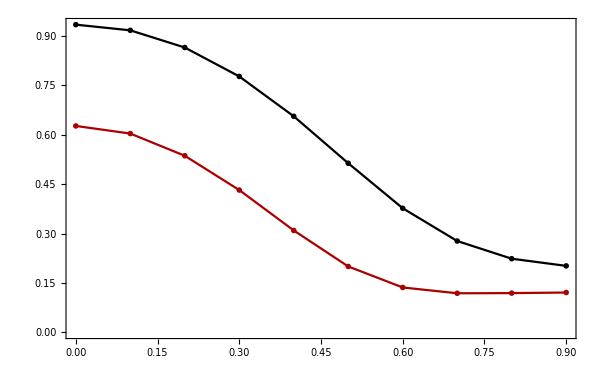

```mathematica
plotInset= ListPlot[ {enVΔ,enVΔ2}, Joined->True ,(*  PlotRange-> {-1.635,-1.6175} ,*)FrameLabel->{MaTeX["\\xi=eV_0/(U-3J_H)",Magnification->1.4] , MaTeX["E_{4\\textrm{v}\\!}\\!-\\!E_{0\\textrm{v}}",Magnification->1.5] }, Frame->True ,  ImageSize->600,  FrameStyle ->Directive[Black,14], PlotMarkers->"OpenMarkers",FrameTicksStyle->Directive[Black,12], PlotLabel-> Style[MaTeX["h=(0.01,0,0), \\, L=32",Magnification->1.2] ,20 ,Black ],PlotStyle->  {{ Black,PointSize[0.05]},{ Darker@Red,PointSize[0.05]}    } ]
```

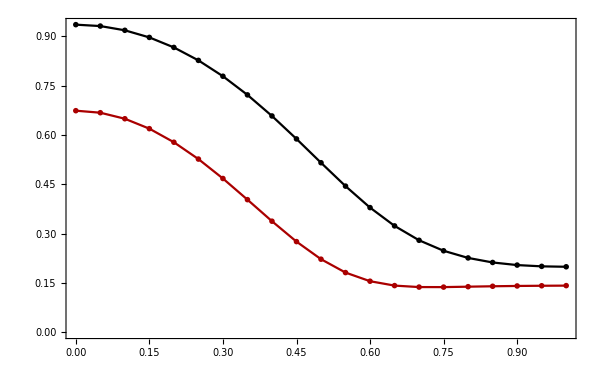

## Figures

## Fig 1 - dispersion

### defs

#### color

```mathematica
Module[ {Γ,J,K,L=Ls[[1]],Nc,h,χ,ω,η=0.45 ,χ0,ω0 ,title, color, j0, L0, EnList0}, 
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
 Nc=L^2;

title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h] ,"X5"-> ToString[η]   }] ;

Show[ ListPlot[ Disp⟦1⟧ ,PlotStyle->PointSize[size], Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } ,ColorFunction->cFun[[1]],ColorFunctionScaling->False  , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->800, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{ } , Automatic}(*
PlotLegends->BarLegend["Rainbow",LegendFunction->"Panel",LegendMargins->0,LabelStyle->Directive[Black,FontSize-> 18,FontFamily->"Helvetica"], LegendLabel->Placed[ MaTeX["0 \\to c, \\qquad \\qquad 1 \\to b ",Magnification->2] ,Left,Rotate[#,90Degree]&]   ],*)  ],
ListPlot[ Disp⟦2⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> cFun[[2]],ColorFunctionScaling->False  ] ,
ListPlot[ Disp⟦3⟧ ,PlotStyle->PointSize[size] , Joined->False , ColorFunction-> cFun[[3]],ColorFunctionScaling->False ] ,
ListPlot[ Disp⟦4⟧ ,PlotStyle->PointSize[size], Joined->False , ColorFunction-> cFun[[4]],ColorFunctionScaling->False ] 
]
]
```

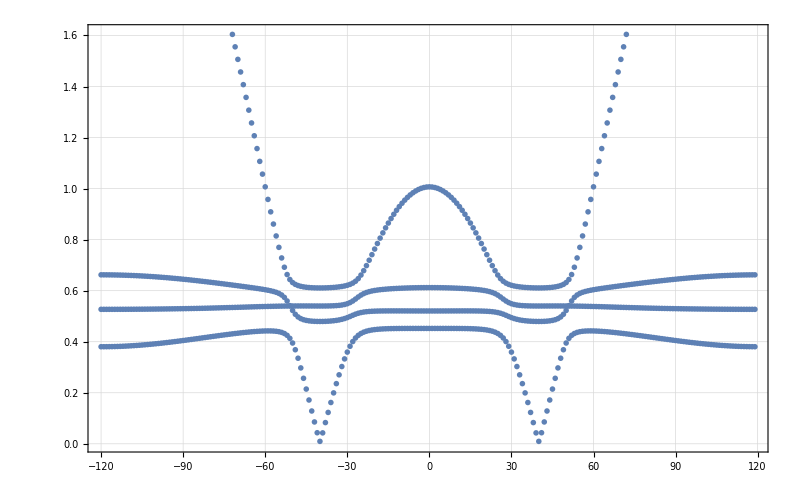

#### plain

```mathematica
disp={};
Module[{j0,L0,χ0,ω0,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
(*{j0,L0,χ0,ω0,EnList0}= loadData[toPath[parameters[[p]],L,acuracy]][[-1]];*)
 Nc = 900^2;
{J,K,Γ,h}=parameters[[1,1]][[1;;4]];
{χ0,ω0}={χG,ωG};
En = EnergiesSortedW[Nc, J,K, Γ, h,χ0,ω0,η] ;
Disp = lineDispersionSortedW[En];
disp = Disp    ];
```

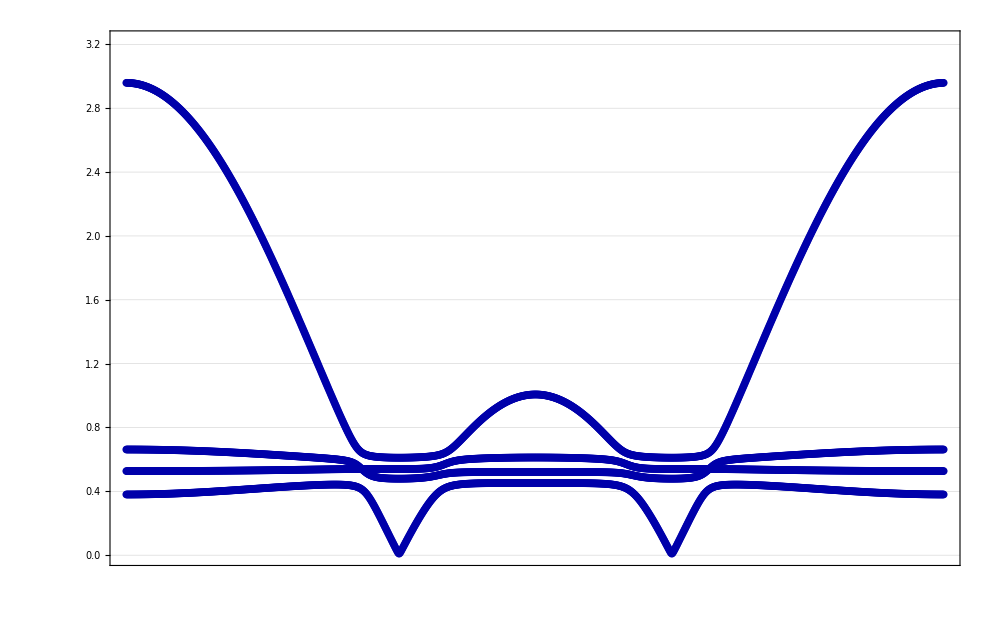

```mathematica
size=0.0056;Module[ {En, Disp,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,1]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{K}^\\prime",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]    }] ;
 ListPlot[ disp  , Joined->False ,  PlotRange-> {0,2*1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000, GridLines->Automatic,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    ,
  PlotStyle->  {{ Darker@Blue,PointSize[size]}}    ]   ]
```

#### plain ΓKMΓ

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
pathΓKMΓ=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,Kpoint,Mpoint,Γpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Black,Dashed,Opacity[0.5],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
EnergiesSortedWΓKMΓ[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line = toLineΓKMΓ[L]},
Table[Chop@cutNegativeEV[Eigensystem@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧]]  , {i,1,L}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i   ,1/2 E⟦i⟧⟦j,2⟧ }, {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
En = EnergiesSortedWΓKMΓ[L, J,K, Γ, h,χ0,ω0,η] ;
Disp = lineDispersionSortedW[En];
dispΓKMΓ[[p]] = Disp    ],{p,1,Length@parameters[[1]]}];
```

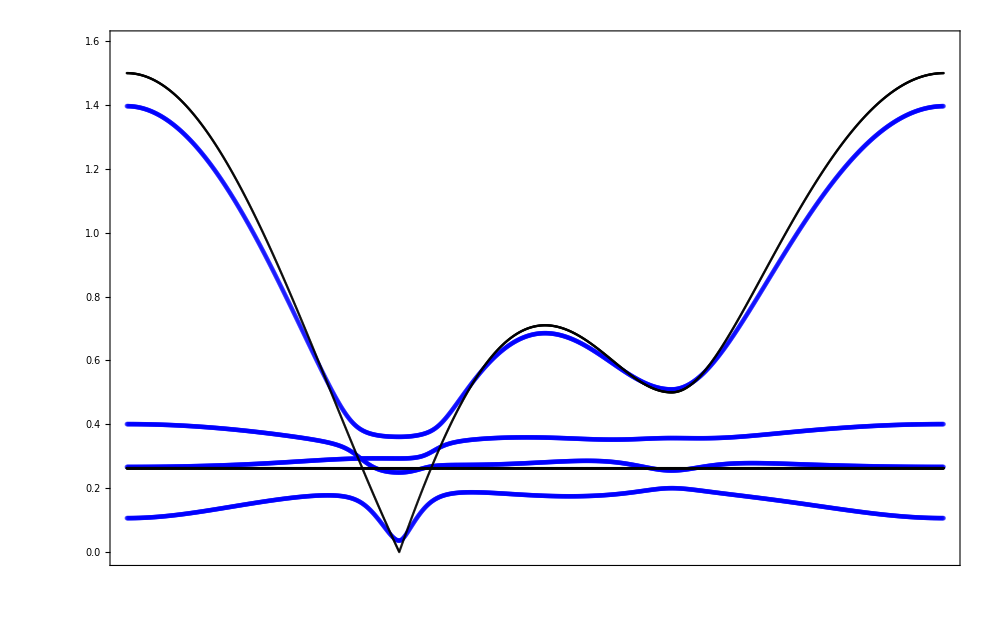

```mathematica
size=0.003;
p0=2;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->False ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.95}],Scaled[{0.5,1}],Scaled[2.5]  ],
 PlotStyle->  {{ Blue,Opacity[0.4],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],   PlotStyle->  {{ Black,Opacity[0.8],PointSize[0.58size]}} ] 
}]
]
```

#### plain full path

```mathematica
toLineΓKMΓKMM[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

```mathematica
pathΓKMΓKMM=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[MPpoint],Point[MPPpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{M}^{\\prime}",Magnification->mag],MPpoint,Scaled[{0.75,-0.25}]  ],
Inset[MaTeX["\\,\\mathrm{M}^{\\prime\\prime}",Magnification->mag],MPPpoint,Scaled[{0.25,-0.25}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Purple,Opacity[0.5],Arrowheads[Large],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
EnergiesSortedWΓKMΓKMM[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line = toLineΓKMΓKMM[L]},
Table[Chop@weightSort@cutNegativeEV[Eigensystem@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧]]  , {i,1,L}]      ];
lineDispersionSortedW[E_]:=Module[ {M = Length[E]},    Table[  { i ,1/2 E⟦i⟧⟦j,2⟧ }, {j,1,4}       , {i,1,M} ]  ];
```

```mathematica
dispΓKMΓKMM=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
En = EnergiesSortedWΓKMΓKMM[L, J,K, Γ, h,χ0,ω0,η] ;
Disp = lineDispersionSortedW[En];
dispΓKMΓKMM[[p]] = Disp    ],{p,1,Length@parameters[[1]]}];
```

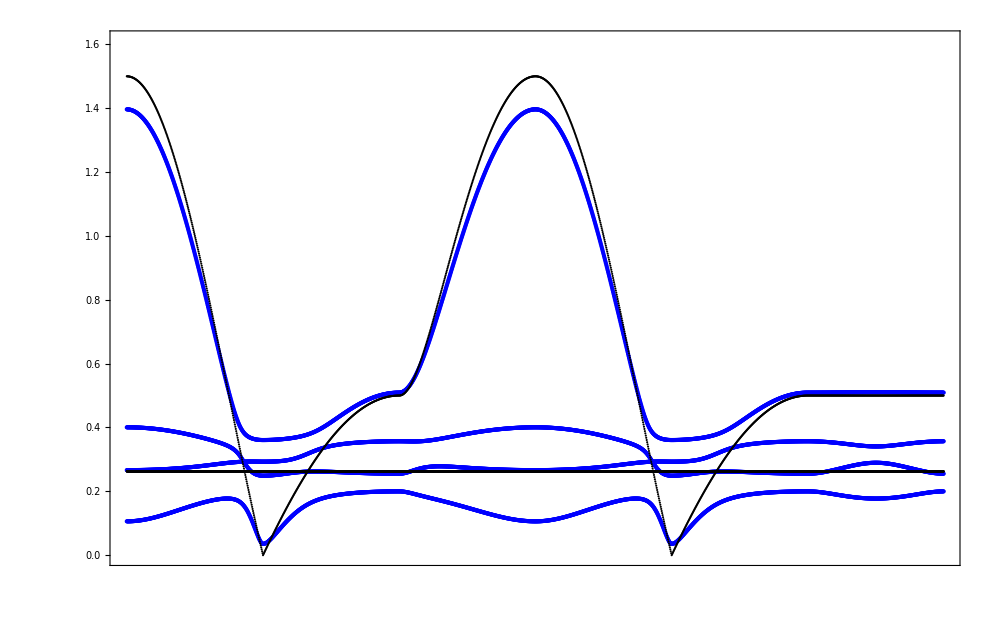

```mathematica
size=0.003;
p0=2;
Module[ {En,  disp=dispΓKMΓKMM,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,M,Kticks,ks,klabel,knum},
Kval=disp[[1,1,;;,1]];
M=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
knum=Length[{ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }];
ks=Table[  Kval[[  ⌊(i M)/(knum-1)⌋  +1-KroneckerDelta[knum-1,i]]]  , {i,0,knum-1}];
klabel=MaTeX[#,Magnification->1.8]&/@{"\\Gamma","\\mathrm{K}^{\\prime}","\\mathrm{M}^{\\prime}","\\Gamma","\\mathrm{K}","\\mathrm{M}","\\mathrm{M}^{\\prime\\prime}"};
Kticks=Thread[{ks,klabel}]; 
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]    }] ;

Show[{
 ListPlot[ disp[[p0]]  , Joined->False ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[path,Scaled[{0.8,.92}],Scaled[{0.5,1}],Scaled[3]  ],
   PlotStyle->  {{ Blue,PointSize[size]}}     ]  ,
ListPlot[ disp[[1]],PlotStyle->  {{ Black,PointSize[0.5size]}}  ] 
}]
 ]
```

#### sort for join test

```mathematica
(*Module[{ev0=ev,L,Δev0,ΔevF={},evF={},ΔevPerm,evPerm,indices={},j,x},
L=Length[ev0];
Δev0;
evPerm=Permutations/@ev0;
ΔevPerm=Permutations/@Δev0;(* Thread[  {Range[Factorial[4]],Permutations[#]}]&/@ev0;*)
AppendTo[indices,1];
AppendTo[ΔevF,ΔevPerm[[1,indices[[1]] ]]  ];
AppendTo[evF,evPerm[[1,indices[[1]] ]]  ];

Do[
x=SortBy[Table[{j,Total@Abs[evPerm[[i,j]]-evF[[i-1]]]},{j,1,Factorial[4]}  ],Last];
(*Print@x[[1;;3]];*)
j=x[[1,1]];

AppendTo[indices,j];
AppendTo[evF,evPerm[[i,indices[[i]] ]]];
,{i,2,L}];
Print[indices];
(*ListPlot[ evF ]*)
ListPlot[     Table[  { i   ,1/2 evF⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ] , Joined->True]
]
weightSort2[es_] := Module[ {E1,ΔE1,E2},
E1=Sort@Table[ { es⟦n,1⟧,n}, {n,1,4}];
Sort[En]
];*)
```

```mathematica
Module[{j0,L0,χ0,ω0,ξG,EnList0,p=1,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp,line },
L0=Ls[[1]];L=1800;
line = toLineΓKMΓKMM[L];
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L0,acuracy,"free",NbName ]  ];
ev= Table[Chop[cutNegativeEV[Eigenvalues@N@HMFk[J,K,Γ,h,χ0,ω0,η,line⟦i⟧]],10^-8]  , {i,1,L}]     
];
```

```mathematica
pairCP[changepoints_]:=If[Length@changepoints<= 2,{{3,3,3},{1,0,0}},  If[ Subtract@@changepoints[[1;;2,1]] ==0,changepoints[[1;;2]],pairCP@Drop[changepoints,1]   ]   ];
```

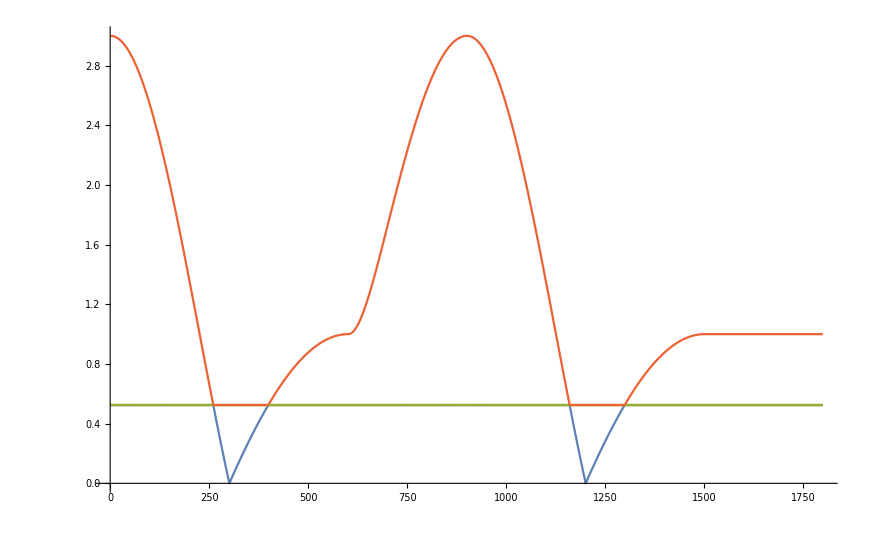

{{260,-7.50427,1},{260,8.13535,4},{261,-4.65336,1},{261,4.05478,4},{301,16.3405,1},{399,-2.65135,1},{399,2.13109,4},{400,-1.34637,1},{400,1.8521,4},{1160,-7.50427,1},{1160,8.13535,4},{1161,-4.65336,1},{1161,4.05478,4},{1201,16.3405,1},{1299,-2.65135,1},{1299,2.13109,4},{1300,-1.34637,1},{1300,1.8521,4}}

{{260,-7.50427,1},{260,8.13535,4},{261,-4.65336,1},{261,4.05478,4}}

0.631079

-Graphics-

{{260,-7.50427,1},{260,8.13535,4},{261,-4.65336,1},{261,4.05478,4},{301,16.3405,1},{399,-2.65135,1},{399,2.13109,4},{400,-1.34637,1},{400,1.8521,4},{1160,-7.50427,1},{1160,8.13535,4},{1161,-4.65336,1},{1161,4.05478,4},{1201,16.3405,1},{1299,-2.65135,1},{1299,2.13109,4},{1300,-1.34637,1},{1300,1.8521,4}}

{{260,-7.50427,1},{260,8.13535,4},{261,-4.65336,1},{261,4.05478,4}}

0.631079

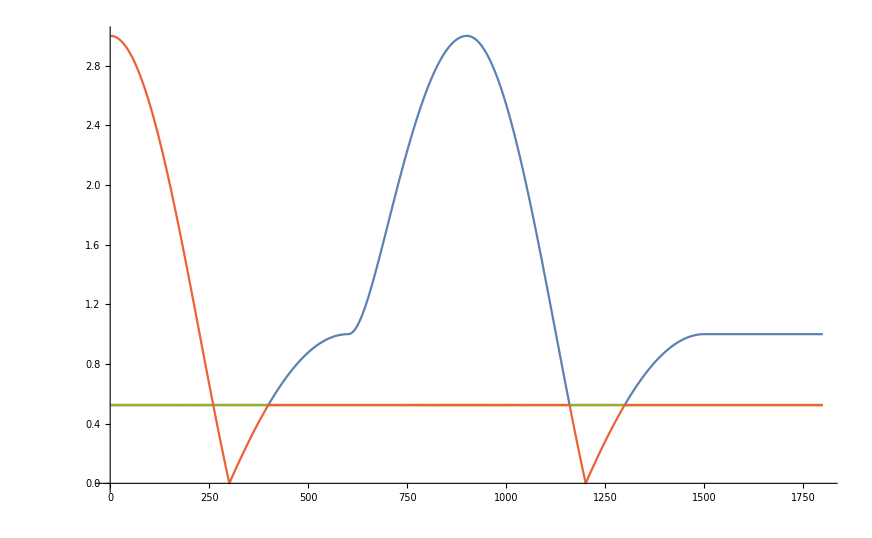

{{301,16.3405,4},{399,-2.65135,4},{399,2.13109,1},{400,-1.34637,4},{400,1.8521,1},{1160,-7.50427,4},{1160,8.13535,1},{1161,-4.65336,4},{1161,4.05478,1},{1201,16.3405,4},{1299,-2.65135,4},{1299,2.13109,1},{1300,-1.34637,4},{1300,1.8521,1}}

{{301,16.3405,4},{399,-2.65135,4},{399,2.13109,1},{400,-1.34637,4}}

-0.520259

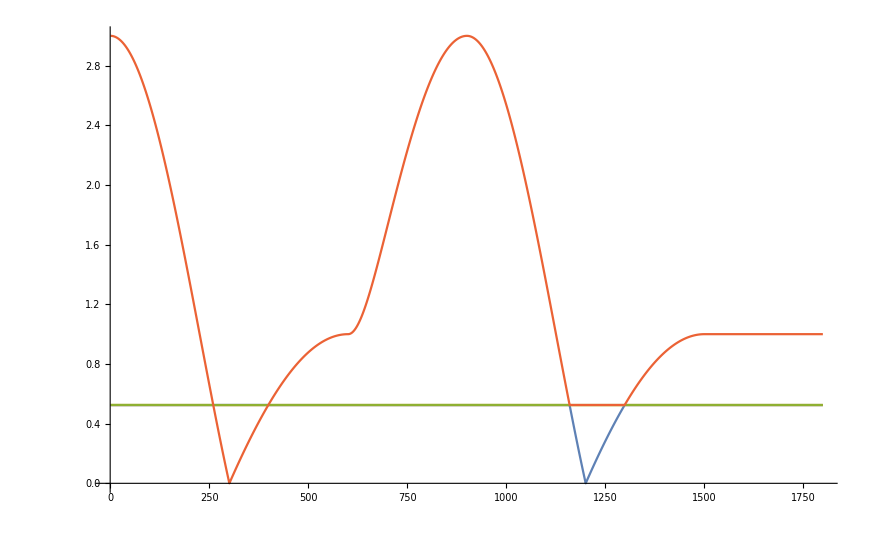

{{301,16.3405,4},{1160,-7.50427,1},{1160,8.13535,4},{1161,-4.65336,1},{1161,4.05478,4},{1201,16.3405,1},{1299,-2.65135,1},{1299,2.13109,4},{1300,-1.34637,1},{1300,1.8521,4}}

{{301,16.3405,4},{1160,-7.50427,1},{1160,8.13535,4},{1161,-4.65336,1}}

0.631079

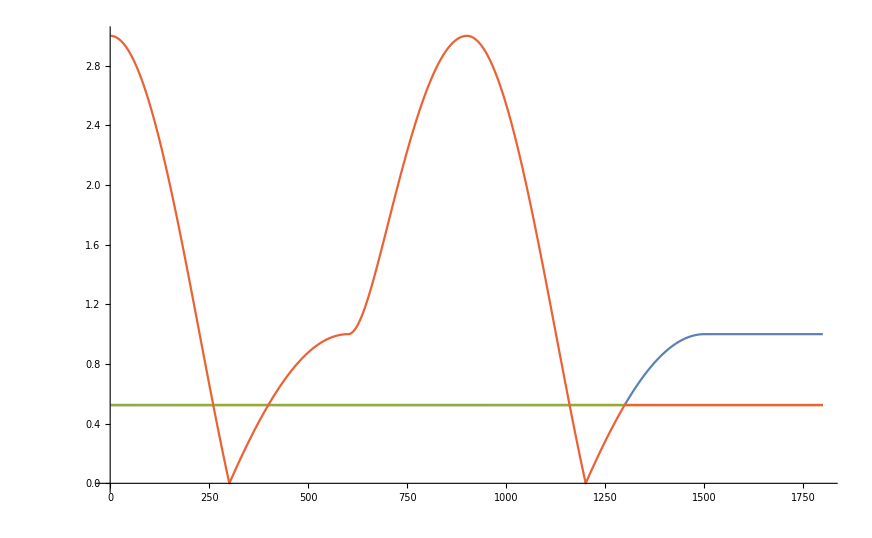

{{301,16.3405,4},{1201,16.3405,4},{1299,-2.65135,4},{1299,2.13109,1},{1300,-1.34637,4},{1300,1.8521,1}}

-0.520259

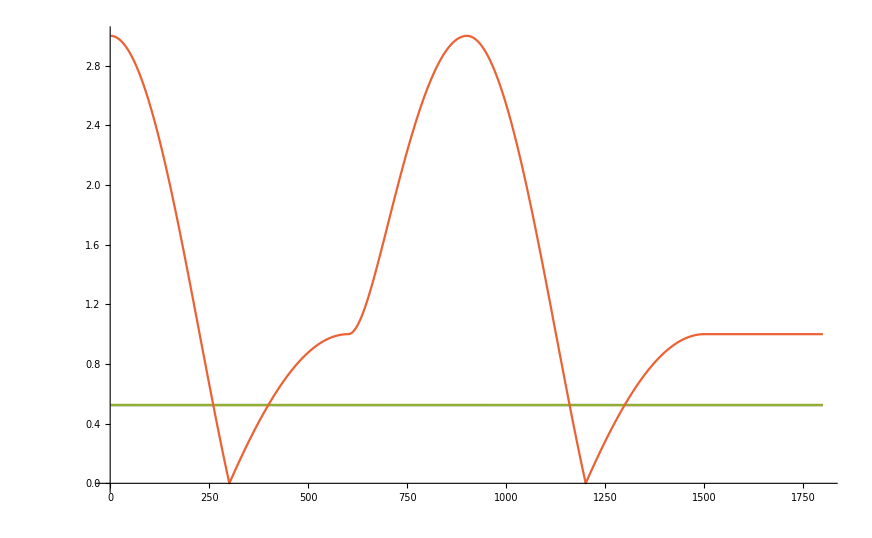

{{301,16.3405,4},{1201,16.3405,4}}

3

False

-Graphics-

```mathematica
Module[{L=1800,evN=ev},

Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
Print@changepoints[[1;;4]];
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
Print@changepoints[[1;;4]];
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;

Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
Print@changepoints[[1;;4]];
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;

Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
Print@changepoints[[1;;4]];
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;
Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];

changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;
Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];

changepoints=Sort[Flatten[Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ,1]];
Print@changepoints;

{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints]  ;
Print[δ1+δ2];

Print[i1==i2 && Abs[δ1+δ2]<1];


evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]]     ]     ,evN                      ] ;
Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];


(*
evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]],evN          ]                 ] ;

Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];
changepoints=Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   ) ;
Print@changepoints;
Print@Sort[Flatten[changepoints,1]][[1;;2]];*)

(*ListPlot[     Table[  { i   , L/2(evN⟦i+1⟧⟦j⟧-2evN⟦i⟧⟦j⟧+evN⟦i-1⟧⟦j⟧)    }, {j,1,4}       , {i,2,L-1} ] , PlotRange->Full,Joined->True]*)
]
```

```mathematica
changepoints
```

{{301,16.3405,4},{1201,16.3405,4}}

```mathematica
DeleteDuplicates@Select[Select[Flatten[changepoints],IntegerQ[#]&],#<= 4&&#>= 1&]
```

{4}

```mathematica
Select[ Split@Select[Flatten[changepoints],IntegerQ[#] && #>4&], Length[#]==2&]
```

{}

#### sort for join

```mathematica
pairCP[changepoints_]:=If[Length@changepoints<= 2,{{3,3,3},{1,0,0}},  If[ Subtract@@changepoints[[1;;2,1]] ==0,changepoints[[1;;2]],pairCP@Drop[changepoints,1]   ]   ];
```

```mathematica
sortContinuos[ev_]:=Module[{L,evN=ev,Δcp=2,changepoints,a=0}, L=Length[ev];
While[ a<10 && Δcp>=2  , a=a+1;
changepoints=Sort@Flatten[   Select[#,Abs[#[[2]]  ]>1&]&/@(  Table[  {  i,L/2(evN⟦i+1⟧⟦n⟧-2evN⟦i⟧⟦n⟧+evN⟦i-1⟧⟦n⟧),n    }, {n,1,4}       , {i,2,L-1} ]   )  ,1] ;
Δcp=Length[   Select[ Split@Select[Flatten[changepoints],IntegerQ[#] && #>4&], Length[#]==2&]       ];
PrintTemporary[a];
If[Δcp<1,Continue[]  ];
(*Print[ "Δcp=", Δcp,"; points= ",Sort[    changepoints   ]   ];*)
{{i1,δ1,n1},{i2,δ2,n2}}=pairCP[changepoints];
evN=If[i1==i2 && Abs[δ1+δ2]<1,  Join[  evN[[1;;i1]],Permute[ #, Cycles[{    {n1,n2}         }] ]&/@evN[[i1+1;;-1]]   ],evN           ] 
(*Print[ListPlot[     Table[  { i   ,  evN⟦i⟧⟦j⟧    }, {j,1,4}       , {i,1,L} ] , PlotRange->Full,Joined->True]];*)
]  ;evN];
```

```mathematica
Module[{j0,L0,χ0,ω0,ξG,EnList0,p=1,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp,line },
L0=Ls[[1]];
L=1800;
line = toLineΓKMΓKMM[L];
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L0,acuracy,"free",NbName ]  ];
ev= sortContinuos@Table[Chop[cutNegativeEV[Eigenvalues@N@HMFk[J,K,Γ,h,χ0,ω0,η,line⟦i⟧]],10^-9]  , {i,1,L}]  ; 
disp=  Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ];
];
```

```mathematica
(*ListPlot[     disp , PlotRange->Full,Joined->True]*)
```

#### plain ΓKMΓ

```mathematica
dispersionContinumΓKMΓ[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line,ks,Ne,Δt,M=L,ev},
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1;  
line=Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1];
ev= sortContinuos@Table[Chop@cutNegativeEV[ Eigenvalues@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧ ] ]    , {i,1,L}]  ; 
Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ]
 ];
```

```mathematica
pathΓKMΓ=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,Kpoint,Mpoint,Γpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Black,Dashed,Opacity[0.5],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

### figs

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js={0.};
		Ks={-1.};
		Γs=Table[γ,{γ,0.,.2,.2}];
		hV=Table[{h,0,0},{h,0.,0.4,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		]
```

```mathematica
dispΓKMΓ=Table[{},Length@parameters[[1]] ];
Do[
Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]]; 
dispΓKMΓ[[p]] = dispersionContinumΓKMΓ[L, J,K, Γ, h,χ0,ω0,η] ;      ],{p,1,Length@parameters[[1]]}];
```

```mathematica
size=0.0035;
p0=2;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color,img=800, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->True ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,25], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->img,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.92}],Scaled[{0.5,1}],Scaled[4]  ],
 PlotStyle->  {{ Blue,Opacity[0.8],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],  Joined->True ,PlotRange->All, PlotStyle->  {{ Black,Dashed,Opacity[0.8],PointSize[0.4size]}} ] 
}]
]
```

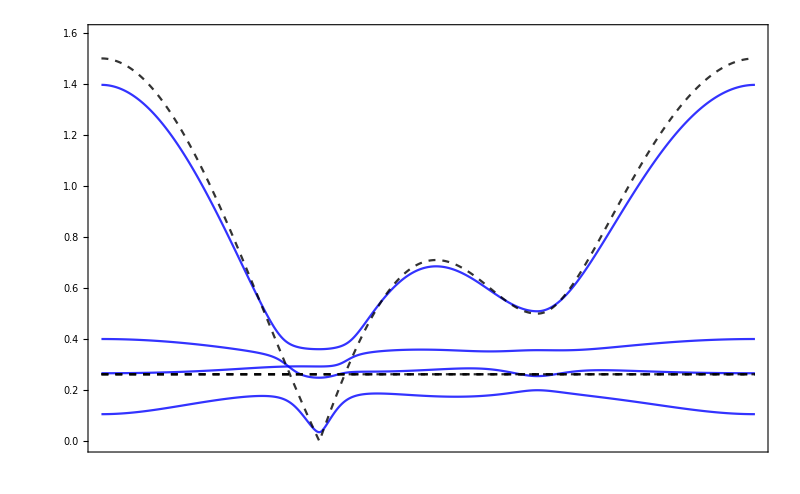

```mathematica
size=0.0035;
p0=3;
Module[ {En, disp=dispΓKMΓ,L, J,K,Γ, h ,η, χ0,ω0 ,title, color,img=800, j0, L0, EnList0,Kval,Nc,Kticks},
Kval=disp[[1,1]][[;;,1]];
Nc=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
Kticks={ { Kval[[1]],MaTeX["\\Gamma",Magnification->1.8]},{Kval[[  ⌊Nc/3⌋+1  ]],MaTeX["\\mathrm{K}",Magnification->1.8]},{Kval[[ ⌊(2Nc)/3⌋+1]],MaTeX["\\mathrm{M}",Magnification->1.8]},{Kval[[-1]]+1,MaTeX["\\Gamma",Magnification->1.8]}};
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]     }] ;
Show[{
 ListPlot[ disp[[p0]]  ,  Joined->True ,  PlotRange-> {-0.01,1.6} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,25], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->img,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓ,Scaled[{0.36,.92}],Scaled[{0.5,1}],Scaled[4]  ],
 PlotStyle->  {{ Blue,Opacity[0.8],PointSize[1.12 size]}}     ]  ,
ListPlot[ disp[[1]],  Joined->True ,PlotRange->All, PlotStyle->  {{ Black,Dashed,Opacity[0.8],PointSize[0.4size]}} ] 
}]
]
```

#### joined path ΓKMΓKMM

```mathematica
dispersionContinumΓKMΓKMM[L_, J_,K_, Γ_, h_,χ_,ω_,η_] :=  Module[ {line,ks,Ne,Δt,M=L,ev},
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
line=Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1];
ev= sortContinuos@Table[Chop@cutNegativeEV[ Eigenvalues@N@HMFk[J,K,Γ,h,χ,ω,η,line⟦i⟧ ] ]    , {i,1,L}]  ; 
Table[  { i ,1/2 ev⟦i⟧⟦j⟧ }, {j,1,4}       , {i,1,L} ]
 ];
```

```mathematica
pathΓKMΓKMM=With[{ps=.03,mag=1.7},
Graphics[{
{Red,Thickness[0.3ps],Opacity[1],Arrowheads[{{0.07,0.57}}],
Arrow[#]&/@Partition[  {Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint}  ,2,1]},
{Black,PointSize[ps],Point[Mpoint],Point[MPpoint],Point[MPPpoint],Point[Γpoint],Point[Kpoint],Point[KPpoint]},
Inset[MaTeX["\\mathrm{M}",Magnification->mag],Mpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{M}^{\\prime}",Magnification->mag],MPpoint,Scaled[{0.75,-0.25}]  ],
Inset[MaTeX["\\,\\mathrm{M}^{\\prime\\prime}",Magnification->mag],MPPpoint,Scaled[{0.25,-0.25}]  ],
Inset[MaTeX["\\mathrm{\\Gamma}",Magnification->mag],Γpoint,Scaled[{0.5,1.2}]  ],
Inset[MaTeX["\\mathrm{K}",Magnification->mag],Kpoint,Scaled[{0.5,0}]  ],
Inset[MaTeX["\\mathrm{K}^\\prime",Magnification->mag],KPpoint,Scaled[{0.5,0}]  ],
(*{Purple,Opacity[0.5],Arrowheads[Large],Arrow[{{0,0},mx}],Arrow[{{0,0},my}]},*)
Black,Dashed,Line[{ Kpoint,KPpoint,Kpoint-mx,KPpoint-mx-my,Kpoint-mx-my,KPpoint-my ,Kpoint}]
 },ImageSize->400]];
```

```mathematica
dispΓKMΓKMM=Table[{},Length@parameters[[1]] ];
Do[Module[{j0,L0,χ0,ω0,ξG,EnList0,J,K,Γ,h, en,η=0.45,L,Nc, En,Disp},L=Ls[[1]];
{j0,L0,χ0,ω0,ξG,EnList0}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
 L = 1800;
{J,K,Γ,h}=parameters[[1,p]][[1;;4]];
dispΓKMΓKMM[[p]] = dispersionContinumΓKMΓKMM[L, J,K, Γ, h,χ0,ω0,η] ;
],{p,1,Length@parameters[[1]]}];
```

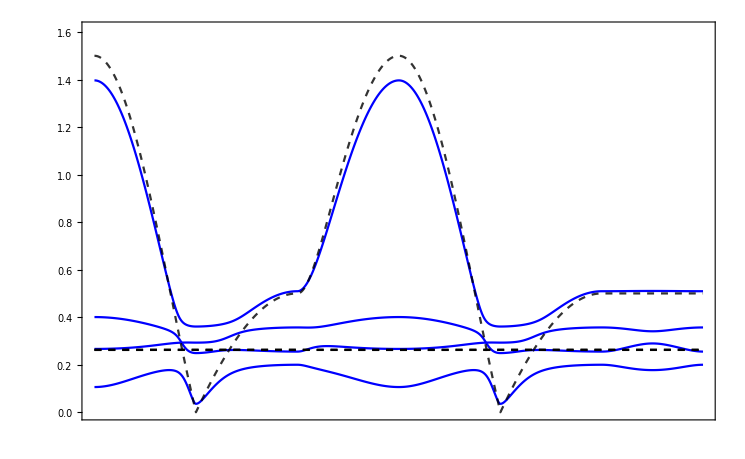

```mathematica
size=0.003;
p0=2;
Module[ {En,  disp=dispΓKMΓKMM,L, J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0, EnList0,Kval,M,Kticks,ks,klabel,knum},
Kval=disp[[1,1,;;,1]];
M=Length@Kval;
 {J,K,Γ,h}=parameters[[1,p0]][[1;;4]];
knum=Length[{ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }];
ks=Table[  Kval[[  ⌊(i M)/(knum-1)⌋  +1-KroneckerDelta[knum-1,i]]]  , {i,0,knum-1}];
klabel=MaTeX[#,Magnification->1.8]&/@{"\\Gamma","\\mathrm{K}^{\\prime}","\\mathrm{M}^{\\prime}","\\Gamma","\\mathrm{K}","\\mathrm{M}","\\mathrm{M}^{\\prime\\prime}"};
Kticks=Thread[{ks,klabel}]; 
title=StringReplace["J = X1, K = X2, \\Gamma = X3, \\mathbf{h} =  X4 \\, \\mathbf{c}",{"X1"-> ToString[NumberForm[J,{2,2}]],"X2"-> ToString[NumberForm[K,{2,2}]],"X3"-> ToString[NumberForm[Γ,{2,2}]] ,"X4"-> ToString[NumberForm[N[Round[100Norm@h]/100],{2,2}]]    }] ;

Show[{
 ListPlot[ disp[[p0]]  , Joined->True ,  PlotRange-> {0,1.61} , FrameLabel->{MaTeX[" ",Magnification->2] , MaTeX["E(\\mathbf{k})",Magnification->2] } , Frame->True ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],(*PlotMarkers->Scaled[],*)ImageSize->1000,  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ],  FrameTicks->{{Automatic,None}, {Kticks,None }  }    , 
Epilog->Inset[pathΓKMΓKMM,Scaled[{0.85,.92}],Scaled[{0.5,1}],Scaled[3.5]  ],
   PlotStyle->  {{ Blue,PointSize[size]}}     ]  ,
ListPlot[ disp[[1]],Joined->True ,PlotRange-> Full,PlotStyle->  {{ Black,Dashed,Opacity[0.8],PointSize[0.5size]}}  ] 
}]
 ]
```

## Fig 2 - gap

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js={0.};
		Ks={-1.};
		Γs=Table[γ,{γ,0.,.2,.2}];
		hV=Table[{h,0,0},{h,0.,0.4,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		]
```

```mathematica
energyGap[Nb_, J_,K_, Γ_, h_,χ_,ω_,η_] :=Module[ {energies},  energies= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η, N@kD1], 8 ]]; energies⟦1⟧]
```

```mathematica
gapH1={};
Do[Module[{L,Nc,J,K, Γ, h,jG,LG,χ,ω,en,ξG,EnG,η=0,l}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
en= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η, N@kD1], 8 ]    ][[1]]; 
AppendTo[gapH1,{Norm@h,en}]    ],
{p,1,Length@parameters[[1]]}];
```

```mathematica
gapH2={};
Do[Module[{L,Nc,J,K, Γ, h,jG,LG,χ,ω,en,ξG,EnG,η=0,l}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ,ω,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];
en= Sort[Abs/@Eigenvalues[ Chop@N@HMFk[ J,K, Γ, h,χ,ω,η, N@kD1], 8 ]    ][[1]]; 
AppendTo[gapH2,{Norm@h,en}]    ],
{p,1,Length@parameters[[1]]}];
```

```mathematica
gap1=gapH1[[1;;25]];
gap2=gapH2[[1;;25]];
```

```mathematica
size=0.009;
logInset=Show[ 
ListLogLogPlot[{gap1,gap2},FrameTicks->None, Frame->False,  PlotStyle->  {{ Darker@Blue,PointSize[size]}} ,  PlotRange-> Automatic  , PlotMarkers->"OpenMarkers", Epilog->Inset[ MaTeX["\\Delta_f = 6 \\sqrt{3} \\;  \\frac{h^xh^yh^z}{3\\Delta_v^2}",Magnification->1.2] ,Scaled[{0.3,0.9}]]  ],
LogLogPlot[  2 √3 1/(0.262)^2 (h/(2 √3))^3 ,{h,0.00001,0.85},PlotStyle->Black]              ]
```

```mathematica
size=0.009;Module[ {En, Disp,L, Nc,J,K,Γ, h ,η, χ0,ω0 ,title, color, j0, L0}, 
title=StringReplace["  ",{"X1"-> ToString[J],"X2"-> ToString[K],"X3"-> ToString[Γ] ,"X4"-> ToString[Norm@h]  }] ;
Show[
 ListPlot[ {gapH1,gapH2}  , Joined->False ,  PlotRange-> {-0.05,1} , FrameLabel->{MaTeX["h",Magnification->2] , MaTeX["\\text{Gap } \\; \\Delta_f",Magnification->2] } , Frame->True, PlotMarkers->"OpenMarkers" ,   FrameStyle ->Directive[Black,20], FrameTicksStyle->Directive[Black,15],ImageSize->600,(* GridLines->None,*)  PlotLabel-> Style[MaTeX[title,Magnification->2] ,20 ,Black ]  ,  PlotStyle->  {{ Darker@Blue,PointSize[size]}} , Epilog->Inset[logInset,Scaled[{0.285,0.68}],Center,{0.5,Automatic} ]   ]   
,Plot[  2 √3 1/(0.262)^2 (h/(2 √3))^3  (*1.207 h^3*) ,{h,0.0000001,0.6}, PlotStyle->{Black,Opacity[.5], Thickness[0.0035 ]}]           ] ]
```

## Fig 3 - MF parameters

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js={0.};
		Ks={-1.};
		Γs=Table[γ,{γ,-1,1,.05}];
		hV=Table[{h,0,0},{h,0.2,0.2,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		]
```

```mathematica
ωH={};χKH={};χcH={};χΓH={};χJH={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH,{Γ,ωM }]; AppendTo[χKH,{Γ,χK}]; AppendTo[χcH,{Γ,χc}]; AppendTo[χΓH,{Γ,χΓ}];  AppendTo[χJH,{Γ,χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

```mathematica
Module[{title}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
gK=ListPlot[χKH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Blue]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_K=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}"},{.08,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic,PlotRange-> { -1,1 }];
gc=ListPlot[χcH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Red]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}"},{.2,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
gΓ = ListPlot[χΓH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}"},{.32,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
gJ = ListPlot[χJH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{ Orange },Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}"},{.32,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
gM = ListPlot[ωH,Joined->True,PlotMarkers->{"●",Small}, PlotStyle->{Darker[Green]},Frame->True,FrameStyle->Directive[Black,16],PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma ","\\text{MF parameters}"},ImageSize->500,PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\braket{\\sigma}=\\mathrm{W}^{0\\alpha}\\hat{h}^{\\alpha}"},{.45,.9}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->Automatic];
Show[gK,gc,gJ,gM, gΓ,PlotRange-> { {-0.72,0.72},{-1,1} }  ]
]
```

also, we could insert both Γ and J in the horizontal axis, just changing the plot markers

```mathematica
NbName = "705"; 
		Ls =Range[40,40,2]; 	    tV={0};				hV={{0.001,0,0}};
		steps=600;                                     acuracy=6;                               ΔeV=0.099999;                                           eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ; 

		Js=Table[j,{j,-1,1,.05}];
		Ks={-1.};
		Γs= {0.};
		hV=Table[{h,0,0},{h,0.2,0.2,.2}];

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;

		Module[{parameters0,parameters1},
				parameters0=Tuples[{Js,Ks,Γs,hs}];
				parameters1=Tuples[{Js,Ks,Γs,hV}];
				parameters={Table[  Flatten[{ parameters0[[i]],parameters1[[i]],{0},{0}},1],  {i,1,Length@parameters0}]};
		]
```

```mathematica
ωH2={};χKH2={};χcH2={};χΓH2={};χJH2={};
 Do[Module[{L,Nc,J,K, Γ, h,jG,LG,en,ξG,EnG,η=0,l,χ0,ω0, χc,χK,ωM,χJ,χΓ}, l=1;
L=Ls[[l]];
{J,K, Γ, h}=parameters[[1,p]][[1;;4]];
{jG,LG,χ0,ω0,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];

χc=1/3( χ0[[1]][[1,1]]   + χ0[[2]][[1,1]]+χ0[[3]][[1,1]]);
χJ=1/6( χ0[[1]][[3,3]]+χ0[[1]][[4,4]] + χ0[[2]][[2,2]]+ χ0[[2]][[4,4]]+χ0[[3]][[2,2]] +χ0[[3]][[3,3]]   ); 
χK=1/3( χ0[[1]][[2,2]]   + χ0[[2]][[3,3]]+χ0[[3]][[4,4]] - 3χJ );
χΓ=1/6( χ0[[1]][[3,4]]+χ0[[1]][[4,3]] + χ0[[2]][[2,4]]+ χ0[[2]][[4,2]]+χ0[[3]][[2,3]] +χ0[[3]][[3,2]]   );
ωM= 1/(2Norm[h]) ( h.{ω0[[1]][[2,1]],ω0[[1]][[3,1]],ω0[[1]][[4,1]]}   + h.{ω0[[2]][[2,1]],ω0[[2]][[3,1]],ω0[[2]][[4,1]]}   );

 AppendTo[ωH2,{Γ,ωM }]; AppendTo[χKH2,{Γ,χK}]; AppendTo[χcH2,{Γ,χc}]; AppendTo[χΓH2,{Γ,χΓ}];  AppendTo[χJH2,{Γ,χJ}];               ];
, {p,1,Length[parameters[[1]] ]} ]
```

```mathematica
Module[{title}, title="J=0, \\, K=-1 , \\,   \\mathbf{h}=0.2 \\mathbf{c}";
g1=ListPlot[{χKH,χcH,χΓH,χJH,ωH},Joined->True,PlotMarkers->"○" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
PlotLabel->(MaTeX[#,Magnification->1.6]&)@title,
FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\Gamma[\\circ] , \\, J [\triangle] ","\\text{MF parameters}"},
ImageSize->500,
PlotLegends->Placed[(MaTeX[#,Magnification->1.3]&)/@{"\\mathrm{U}_K=\\mathrm{U}_{\\gamma}^{\\gamma\\gamma}","\\mathrm{U}_{0}=\\mathrm{U}_{\\gamma}^{00}","\\mathrm{U}_{\\Gamma}=\\mathrm{U}_{\\gamma}^{\\alpha\\beta}","\\mathrm{U}_{J}=\\mathrm{U}_{\\gamma}^{\\alpha\\alpha}","\\braket{\\sigma}=\\mathrm{W}^{0\\alpha}\\hat{h}^{\\alpha}"},{.08,.9}],
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];

g2=ListPlot[{χKH2,χcH2,χΓH2,χJH2,ωH2},Joined->True,PlotMarkers->"△" ,
 PlotStyle->{Darker[Blue],Darker[Red],Orange,Pink,Darker[Green]},
Frame->True,FrameStyle->Directive[Black,16],
ImageSize->500,
PlotRange->All,Frame->True,FrameStyle->Directive[Black,16], ImageSize->500,PlotRange->All,GridLines->False,
PlotRange-> { -1,1 }];


Show[g1,g2,PlotRange-> { {-0.72,0.72},{-1,1} }  ]
]
```

## Fig 5 - Charge density line plot

```mathematica
NbName = "705"; 

		Ls = Range[42,42,4]; 				tV={0,2.74356};			
		hV= { {0.0001,0,0},{0.2,0,0}};

		steps=350;				acuracy=8;     eVs=Table[1700 x, {x,0,0,0.099999}];  (* eV=ξ(U-3JH)=1500ξ *)

		ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
		hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
		eV0=0;U=2600;JH=300;
 
		parameters=Table[
Flatten[ Table[ {N@Jr[0,JH,U,ts[[t]] ],N@Kr[0,JH,U,ts[[t]]],N@Γr[0,JH,U,ts[[t]]],hs[[h]] ,N@Jr[eVs[[ev]],JH,U,ts[[t]] ],N@Kr[eVs[[ev]],JH,U,ts[[t]]],N@Γr[eVs[[ev]],JH,U,ts[[t]]],hV[[h]],tV[[t]],eVs[[ev]]} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs}];
```

```mathematica
Module[{χ,ω,ξ,jG,LG,EnG ,gauge="g4", Jv,Kv,Γv,J,K,Γ,L,Nc,h ,u0,H,T,u,t,t0,c11,c21,c12,c22,sNN,sNNN,δn,δn1,d,κ,p,l,tp,hp},
l=1;


p=1;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]]; 
	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];                   
                                                                                                                      
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];
		(* δn1=  Module[ {max=Max[Abs@δn]},   δn/max    ];	 *)
δnP=δn;

chPlotZZ0=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=MinMax[Abs@δn]; (*Print[max];*)

points = Table[   Module[   {σ=Mod[i,2],m,n},m=m0+⌊(i-1)/2⌋;n=n0-⌊(i-1)/2⌋-1+σ; 
  {position[σ,m,n][[1]], Abs@δn[[m+n L+1,σ+1]]    }     ]     ,{i,1,2L-1}];ListLogPlot[ Sort@points,Joined->True,PlotStyle->Directive[Gray,Dashed,Bold],Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{0,L/2+1},{min,1.25 max}}                       ]            ];


p=2;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]]; 
	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];                                                                                   
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];
δnH=δn;

chPlotZZH=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=MinMax[Abs@δn]; (*Print[max];*)

points = Table[   Module[   {σ=Mod[i,2],m,n},m=m0+⌊(i-1)/2⌋;n=n0-⌊(i-1)/2⌋-1+σ; 
Style[   {position[σ,m,n][[1]], Abs@δn[[m+n L+1,σ+1]]    } , chargeCFgray[δn[[m+n L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L-1}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{0,L/2+1},{min,1.25 max}}                       ]            ];

p=3;tp=⌈p/Length@hV⌉;hp=Mod[p,Length@hV,1]; 		 
	{J,K,Γ,h}=parameters⟦1,p⟧[[1;;4]];L=Ls⟦l⟧; Nc=L^2;
	{jG,LG,χ,ω,ξ,EnG}=Chop@loadData[toPath[parameters[[1,p]],L,acuracy, gauge,NbName ]  ];
	Kv= uniform[K,L,L];Jv=uniform[J,L,L];Γv=uniform[Γ,L,L];
	d=parameters[[1,p]][[8]]; 
	u0= gauge4v[ uniformU[-1,L] ,L];     
        t=ts[[tp]];                                                                                   
		c11=coefTriang11[JH,U,t];c21=coefTriang21[JH,U,t];  c12=coefTriang12[JH,U,t];c22=coefTriang22[JH,U,t];  
		sNN = sscNN[χ,ω,L]; sNNN= sscNNN[ξ,ω,L];
		δn=densityTriang[L,c11,c21,c12,c22,sNN,0  sNNN];
δnΓ=δn;

chPlotZZΓ=Module[{points,title,m0=0,n0=L-1,min,max}, {min,max}=MinMax[Abs@δn]; (*Print[max];*)

points = Table[   Module[   {σ=Mod[i,2],m,n},m=m0+⌊(i-1)/2⌋;n=n0-⌊(i-1)/2⌋-1+σ; 
Style[   {position[σ,m,n][[1]], Abs@δn[[m+n L+1,σ+1]]    } , chargeCFgray[δn[[m+n L+1,σ+1]]/max ], Bold      ]     ]     ,{i,1,2L-1}];ListLogPlot[ Sort@points,Joined->True,Frame->True,ImageSize->1000,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"x \\; ", "\\Vert \\, \\delta n_{l} \\,  \\Vert"}, FrameStyle->Directive[Black,20],PlotRange->{{0,L/2+1},{min,1.25 max}}                       ]            ];

(*
	nameComplement=StringReplace["t=X1_h=X2-L=X3-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]],"X3"-> ToString[L],"X4"-> ToString[acuracy]  }];        
Print[nameComplement];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_CONFIG_FLUX\\CHARG_CONFIG_FLUX_XX.pdf","XX"-> nameComplement]  }],chargeConfigFlux[δn,χ,ω,L,title]       ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_CONFIG_FLUX_ZOOM\\CHARG_CONFIG_FLUX_ZOOM_XX.pdf","XX"-> nameComplement]  }],chargeConfigFluxZoom[δn,χ,ω,L,title]       ];Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\705\\CHARG_PLOT\\CHARG_PLOT_ZZ_XX.pdf","XX"-> nameComplement]   }],chargePlotZZ[δn,L,parameters[[1,p]],hV[[hp]]] ];
*)

chP1=Show[chPlotZZH,chPlotZZ0];
chP2=Show[chPlotZZΓ,chPlotZZ0];


    ]
```

## Fig 6 - Quadrupole projected

```mathematica
θφQzz[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],charge[[i,5]][[3,3]]  },{i,1,Length@charge}   ];θφQxxQyy[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],charge[[i,5]][[1,1]] -charge[[i,5]][[2,2]]  },{i,1,Length@charge}   ];θφQxy[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],charge[[i,5]][[1,2]] +charge[[i,5]][[2,1]]  },{i,1,Length@charge}   ];

anisotropy[Q_]:=√(Q⟦1,1⟧^2+4 Q⟦1,2⟧ Q⟦2,1⟧-2 Q⟦1,1⟧ Q⟦2,2⟧+Q⟦2,2⟧^2);    (*  2 Sqrt[ ((Qxx-Qyy)/2)^2+ QxyQyx   ] 00  *)
θφAni[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ];
θφAni2[charge_]:=Table[ {charge[[i,6]][[2]],charge[[i,6]][[3]],1/Abs[charge[[i,5]][[3,3]]] anisotropy@charge[[i,5]]  },{i,1,Length@charge}   ]; 
projectSouthHemesphere[list0_]:=Module[{list}, list=Select[list0,(#[[1]]>=90∧#[[1]]<=180)& ];  Table[{(Cos[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]), (Sin[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]),list[[i,3]] },{i,1,Length@list}   ] ];
projecthHemesphereSquare[list0_]:=Select[ Module[{list}, list=Select[list0,(#[[1]]>=10)& ];  Table[{(Cos[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]), (Sin[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]),list[[i,3]] },{i,1,Length@list}   ] ], (Abs[#[[1]]]<=1&&Abs[#[[2]]]<=1)&  ];
```

```mathematica
projectAnyHemesphere[list0_,θ_,φ_]:=Module[{list}, 
list=Table[ { Mod[ list0[[i,1]]-θ, 180,1], Mod[ list0[[i,2]]-φ, 360,1],list0[[i,3]] },{i,1,Length@list0}   ];
list=Select[list,(#[[1]]>=90∧#[[1]]<=180)& ];  
Table[{(Cos[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]), (Sin[π list[[i,2]]/180]Sin[π list[[i,1]]/180])/(1-Cos[π list[[i,1]]/180]),list[[i,3]] },{i,1,Length@list}   ] 
];
```

```mathematica
NbName="709";
		Ls = Range[42,42,2]; 				tV={0};				
		hV=With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,0.1,360.1,1},{θ,0.1,180.1,1}],1]        ]; 
		θV = Table[θ,{θ,0,180,1}];	


		φV1 = Table[φ,{φ,0,60,1}];	
		hV1 = With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,φV1},{θ,θV}],1]        ]; 
		φV2 = Table[φ,{φ,64,120,1}];	
		hV2 = With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,φV2},{θ,θV}],1]        ]; 
		φV3 = Table[φ,{φ,124,180,1}];	
		hV3 = With[{h=0.2},Flatten[Table[{h,θ,φ},{φ,φV3},{θ,θV}],1]        ]; 

		acuracy=9;
```

```mathematica
λpoints={{},{},{}} ;
κpoints={};
hV=Sort@Join[hV1,hV2,hV3];

Do[ Module[{ h,hv }, 	
	hv=hV[[hp]];
	h=hv[[1]]  hAngle[hv[[2]],hv[[3]]] ;
AppendTo[κpoints,         {hv[[2]],hv[[3]],  toKappa[h]}  ];
AppendTo[λpoints[[1]],  {hv[[2]],hv[[3]],  toλ[h].ha  }  ];
AppendTo[λpoints[[2]],  {hv[[2]],hv[[3]],  toλ[h].hb  }  ];
AppendTo[λpoints[[3]],  {hv[[2]],hv[[3]],  toλ[h].hc  }  ];
(*nameComplement=StringReplace["t=X1_h=X2-ac=X4",{"X1"-> ToString[tV[[tp]]],"X2"-> ToString[hV[[hp]]], "X4"-> ToString[acuracy]  }];      *)
],{hp,1,Length@hV,2 }];
```

```mathematica
pmax=Length[  parameters[[1]]   ];Δp=1;   (*  chargeHex01={};*)
extCharge[ch_]:= Join[ch,(  {#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],{#[[6,1]],180-#[[6,2]],180+#[[6,3]]}}    )&/@ch];
Module[{cH1,cH2,cH3,l,χ,ω,ξ,jG,LG,EnG ,gauge="g4",ev=1,p=1,L=Ls[[1]] },
ClearAll[chargeHex0,chargeHex00];
cH1=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV1[[1]],hV1[[-1]]}];
cH2=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV2[[1]],hV2[[-1]]}];
cH3=LoadquadrupolePure[parameters[[ev,p]],L,acuracy,gauge,{hV3[[1]],hV3[[-1]]}];
chargeHex0=Select[ Join[cH1,cH2,cH3],(#[[6,3]]>=0&&#[[6,3]]<=180)& ];
chargeHex00=extCharge[chargeHex0];
]
```

```mathematica
listQ0[[1]]
```

{{0,0,-1.72301},{1,0,-1.72306},{2,0,-1.72226},{3,0,-1.72105},{4,0,-1.71942},{5,0,-1.71739},{6,0,-1.71496},{7,0,-1.71215},{8,0,-1.70857},{9,0,-1.70505},{10,0,-1.7008},{11,0,-1.69663},{12,0,-1.69178},{13,0,-1.68666},{14,0,-1.68129},{15,0,-1.67605},{16,0,-1.67026},63391,{15,360,-1.67605},{14,360,-1.68129},{13,360,-1.68666},{12,360,-1.69178},{11,360,-1.69663},{10,360,-1.7008},{9,360,-1.70505},{8,360,-1.70857},{7,360,-1.71215},{6,360,-1.71496},{5,360,-1.71739},{4,360,-1.71942},{3,360,-1.72105},{2,360,-1.72226},{1,360,-1.72306},{0,360,-1.72301}}
 |  |  |  |

h=.2_L=42_disk

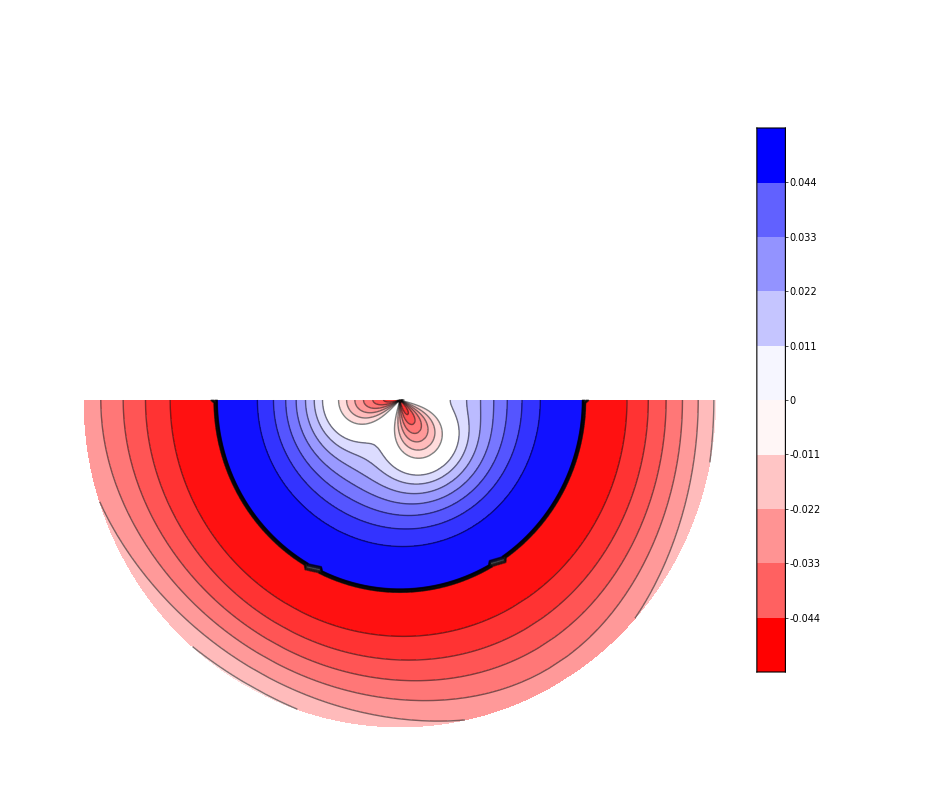
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{epilog={},title,plotsContour,plotsDensity,chargeList,listQ ,κp,λp,name,ΔL=1,rangeθ={-1,1},rangeφ={-1,1},imgs=800 },
epilog ={"\\Vert h \\Vert = 0.2"} ;
chargeList= chargeHex00;
listQ0={       θφQzz[chargeList ],θφQxxQyy[chargeList ],θφQxy[chargeList ],θφAni[chargeList ] ,θφAni2[chargeList ]        };
listQ=listQ0 ;
list0=listQ0[[1]]; 
title="\\text{Quadrupole for pure Kitaev model } \\vec{h}=h \\big( \\mathbf{c} \\cos\\theta + \\mathbf{a} \\sin\\theta \\big)";
max1=N@(Ceiling[Max@Abs[  listQ0[[1]][[;;,3]]   ]  100]/100);
max4=N@(Ceiling[Max@Abs[  listQ0[[4]][[;;,3]]   ]  100]/100);
max2=Max@Abs[  Join[listQ0[[2]][[;;,3]] ,listQ0[[3]][[;;,3]]]];
max=N@(Ceiling[max2 100]/100);
contoursLevels=Flatten[Table[ max/8  x s,{x,1,10},{s,{-1,+1}}],1];
contoursLevels4=Flatten[Table[ max4/8  x s,{x,1,10},{s,{-1,+1}}],1];
δ=0.03;(*
Print[max1, "; "max2, "; "max, "; "δ];
Abort[];*)
colors={{0,Red},{0.5-δ,White},{0.5+δ,White},{1,Blue}};
maxκ=N@(Ceiling[Max@Abs[  κpoints[[;;,3]]   ] 100]/100);

contoursLevelsκ=Flatten[Table[ maxκ/8  x s,{x,1,10},{s,{-1,+1}}],1];
maxλ1=Max@Abs[  λpoints[[1,;;,3]]   ];maxλ1=N@(Ceiling[maxλ1 100]/100);
contoursLevelsλ1=Flatten[Table[ maxλ1/8  x s,{x,1,10},{s,{-1,+1}}],1];

maxλ2=Max@Abs[  λpoints[[2,;;,3]]   ];maxλ2=N@(Ceiling[maxλ2 100]/100);
contoursLevelsλ2=Flatten[Table[ maxλ2/8  x s,{x,1,8},{s,{-1,+1}}],1];

 {θ,φ}={60,180};
listQ=projectAnyHemesphere[#,θ,φ]&/@listQ;
listq0=listQ;
κp=projectAnyHemesphere[#,θ,φ]&@κpoints;
λp=projectAnyHemesphere[#,θ,φ]&/@λpoints;


plotsContour={
ListContourPlot[ listQ[[1]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{zz} ",Magnification->1.4]  , PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,0.15+# .8]&)  , (*Contours->contoursLevels,*) ColorFunctionScaling->True,Contours->9
],
ListContourPlot[ listQ[[2]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{xx}-Q_{yy} ",Magnification->1.4]   , PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  , ColorFunctionScaling->False,Contours->contoursLevels]   ,
ListContourPlot[ listQ[[3]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{"\\theta \\; ","\\varphi"},  PlotLabel->MaTeX[" Q_{xy} ",Magnification->1.4]       (*,PlotLegends->Placed[MaTeX[epilog,Magnification->1.5] ,{Scaled[{0.02,.97}],{0,1} } ]*), PlotLegends->BarLegend[Automatic,All] ,ColorFunction->(Blend[colors,1/2+#/(2 max2)]&)  ,Frame->False,  ColorFunctionScaling->False,Contours->contoursLevels],
ListContourPlot[ listQ[[4]], ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},Frame->False, PlotLabel->MaTeX[" Q_{xx}^\\prime-Q_{yy}^\\prime ",Magnification->1.4]  , PlotLegends->Automatic , ColorFunction->(Blend[colors,1/2+#/(2 max4)]&)  , ColorFunctionScaling->False,Contours->contoursLevels4]    ,
ListContourPlot[κp,PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxκ)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsκ, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotLabel->MaTeX["\\kappa",Magnification->1.4] ],
ListContourPlot[λp[[1]], PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ1)]&) , ColorFunctionScaling->False,Contours->contoursLevelsλ1, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}}, PlotLabel->MaTeX["\\lambda \\cdot \\mathbf{a} ",Magnification->1.4]  ] ,
ListContourPlot[λp[[2]],  PlotLegends->BarLegend[Automatic,9] ,ColorFunction->(Blend[colors,1/2+#/(2 maxλ2)]&)  , ColorFunctionScaling->False,Contours->contoursLevelsλ2, Frame->False,ImageSize->imgs,PlotRange->{{rangeθ[[1]],rangeθ[[2]]},{rangeφ[[1]],rangeφ[[2]]}},PlotLabel->MaTeX["\\lambda \\cdot \\mathbf{b} ",Magnification->1.4]]
};
name="h=.2_L=42_disk"; Print[name];

Print[plotsContour ];

(*
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\Qzz_XX_pure.pdf","XX"->name]  }],      plotsContour[[1]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\QxxQyy_XX_pure.pdf","XX"->name]  }],plotsContour[[2]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\Qxy_XX_pure.pdf","XX"-> name]  }],      plotsContour[[3]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\Qani_XX_pure.pdf","XX"-> name]  }],    plotsContour[[4]]      ];
(*Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\Qani2_Theta_XX_pure.pdf","XX"-> name]  }],    plots[[5]]      ];*)
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\kappa_XX_pure.pdf","XX"-> name]  }],      plotsContour[[5]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\lambdaA_XX_pure.pdf","XX"-> name]  }],      plotsContour[[6]]      ];
Export[ FileNameJoin[{ NotebookDirectory[], StringReplace["\\Figures\\pure\\QUADRUPOLE_th_ph\\lambdaB_XX_pure.pdf","XX"-> name]  }],    plotsContour[[7]]      ];
*)

 ]
```